OLD
This notebook is meant to calculate the population evolution for Ba - 133. There are 16 hyperfine states involved so the density matrix is a bit dense. The biggest complication though is that if we want to know things like state preparation and readout fidelity, we need to consider the effect of off-resonant lasers on transitions between states. This leads to multiply connected states. One could use the JPHYS B approach that we’ve used in the past, but it’s a big mess. The easiest way I think is just use the interaction picture and allow the off-diagonal matrices to have time dependence. Then just solve the time dependent density matrix. This may be more accurate anyway if we push to short timescales. ERH 8/6/15

NEW
I’m updating this notebook to include the P3/2 and D5/2 levels so we can do shelving state detection. Now it’s up to 36 levels.  Updated numbering so state numbers start at 1 and not 0. State number is still a touch odd since it’s more historical than anything else.

```mathematica
(*Let's establish our naming convention*)
```

### Initialization

```mathematica
(*Constants*)
c = 2.998*^8;
ee = 1.602*^-19;
me = 9.11*^-31;
ℏ = (6.626*^-34)/(2π);
ϵo = 8.854*^-12;

(*Parameters*)
λsp = 493.4077*^-9;
ωsp = 2π c/λsp;
λsp2 = 455*^-9;
ωsp2 = 2π c/λsp2;
λdp = 649.6898*^-9;
ωdp = 2π c/λdp;
λdp2 = 585*^-9;
ωdp2 = 2π c/λdp2;
λdp3 = 614*^-9;
ωdp3 = 2π c/λdp3;
Δ1 = -2π 9.925*^9;
Δ2 = -2π 1.840*^9;
Δ3 = -2 π 0.940*^9;
Δ4 = -2 π 0.625*^9;
Δ5 = 2 π 0.093*^9;Δ5 = 2 π 0.08967*^9;
```

```mathematica
State = {
{1,Eng-> 0,F ->  0, Mf->  0, J ->  1/2, L -> 0 ,n -> 6,config-> 1},
{2,Eng-> Δ1,F ->  1, Mf->  -1, J ->  1/2, L -> 0,n -> 6,config-> 1},
{3,Eng-> Δ1,F ->  1, Mf->  0, J ->  1/2, L -> 0,n -> 6,config-> 1},
{4,Eng-> Δ1,F ->  1, Mf->  1, J ->  1/2, L -> 0,n -> 6,config-> 1},
{5,Eng-> ωsp,F ->  0, Mf->  0, J ->  1/2, L -> 1,n -> 6,config-> 2},
{6,Eng-> ωsp + Δ2,F ->  1, Mf->  -1, J ->  1/2, L -> 1,n -> 6,config-> 2},
{7,Eng-> ωsp + Δ2,F ->  1, Mf->  0, J ->  1/2, L -> 1,n -> 6,config-> 2},
{8,Eng-> ωsp + Δ2,F ->  1, Mf->  1, J ->  1/2, L -> 1,n -> 6,config-> 2},
{9,Eng-> ωsp-ωdp, F ->  1, Mf->  -1, J ->  3/2, L -> 2,n -> 5,config-> 3},
{10,Eng-> ωsp-ωdp,F ->  1, Mf->  0, J ->  3/2, L -> 2,n -> 5,config-> 3},
{11,Eng-> ωsp-ωdp,F ->  1, Mf->  1, J ->  3/2, L -> 2,n -> 5,config-> 3},
{12,Eng-> ωsp-ωdp + Δ3,F ->  2, Mf->  -2, J ->  3/2, L -> 2,n ->5,config-> 3},
{13,Eng-> ωsp-ωdp + Δ3,F ->  2, Mf->  -1, J ->  3/2, L -> 2,n -> 5,config-> 3},
{14,Eng-> ωsp-ωdp + Δ3,F ->  2, Mf->  0, J ->  3/2, L -> 2,n -> 5,config-> 3},
{15,Eng-> ωsp-ωdp +Δ3,F ->  2, Mf->  1, J ->  3/2, L -> 2,n -> 5,config-> 3},
{16,Eng-> ωsp-ωdp + Δ3,F ->  2, Mf->  2, J ->  3/2, L -> 2,n -> 5,config-> 3},
{17,Eng-> ωsp2,F-> 1,Mf->  -1,J ->  3/2,L -> 1,n -> 6,config-> 4},
{18,Eng-> ωsp2,F-> 1,Mf->  -0,J ->  3/2,L -> 1,n -> 6,config-> 4},
{19,Eng-> ωsp2,F-> 1,Mf->  1,J ->  3/2,L -> 1,n -> 6,config-> 4},
{20,Eng-> ωsp2+Δ4,F-> 2,Mf->  -2,J ->  3/2,L -> 1,n -> 6,config-> 4},
{21,Eng-> ωsp2+Δ4,F-> 2,Mf->  -1,J ->  3/2,L -> 1,n -> 6,config-> 4},
{22,Eng-> ωsp2+Δ4,F-> 2,Mf->  0,J ->  3/2,L -> 1,n -> 6,config-> 4},
{23,Eng-> ωsp2+Δ4,F-> 2,Mf->  1,J ->  3/2,L -> 1,n -> 6,config-> 4},
{24,Eng-> ωsp2+Δ4,F-> 2,Mf->  2,J ->  3/2,L -> 1,n -> 6,config-> 4},
{25,Eng-> ωsp2-ωdp3,F-> 2, Mf->  -2,J ->  5/2,L -> 2,n -> 5,config-> 5},
{26,Eng-> ωsp2-ωdp3,F-> 2,Mf->  -1,J ->  5/2,L -> 2,n -> 5,config-> 5},
{27,Eng-> ωsp2-ωdp3,F-> 2,Mf->  0,J ->  5/2,L -> 2,n -> 5,config-> 5},
{28,Eng-> ωsp2-ωdp3,F-> 2,Mf->  1,J ->  5/2,L -> 2,n -> 5,config-> 5},
{29,Eng-> ωsp2-ωdp3,F-> 2,Mf->  2,J ->  5/2,L -> 2,n -> 5,config-> 5},
{30,Eng-> ωsp2-ωdp3+Δ5,F-> 3,Mf->  -3,J ->  5/2,L -> 2,n -> 5,config-> 5},
{31,Eng-> ωsp2-ωdp3+Δ5,F-> 3,Mf->  -2,J ->  5/2,L -> 2,n -> 5,config-> 5},
{32,Eng-> ωsp2-ωdp3+Δ5,F-> 3,Mf->  -1,J ->  5/2,L -> 2,n -> 5,config-> 5},
{33,Eng-> ωsp2-ωdp3+Δ5,F-> 3,Mf->  0,J ->  5/2,L -> 2,n -> 5,config-> 5},
{34,Eng-> ωsp2-ωdp3+Δ5,F-> 3,Mf->  1,J ->  5/2,L -> 2,n -> 5,config-> 5},
{35,Eng-> ωsp2-ωdp3+Δ5,F-> 3,Mf->  2,J ->  5/2,L -> 2,n -> 5,config-> 5},
{36,Eng-> ωsp2-ωdp3+Δ5,F-> 3,Mf->  3,J ->  5/2,L -> 2,n -> 5,config-> 5}
};
```

### Create bare Hamiltonian, Ho, and Zeeman Hamiltonian, Hmag.

```mathematica
(*Bare hamiltonian*)
MatrixForm[Ho = DiagonalMatrix[Table[Eng/.State[[ii,2]],{ii,1,Length[State]}]]];
```

```mathematica
(*Zeeman shift; Take B field direction as quantization axis.*)
Ispin = 1/2;
gJ[J_,L_,S_] := (3J(J+1)+S(S+1)-L(L+1))/(2J (J+1))
gF[F_,J_,L_,S_,I_]:= gJ[J,L,S] (F(F+1) - I(I+1) + J(J+1))/(2F(F+1))
μB = ee/(2 me); (*remember ℏ = 1*)
HZEme[J_,L_,S_,Fp_,mFp_,F_,mF_,Bz_] := μB Bz gJ[J,L,S] Sum[(-1)^(mF + mFp)mJ ThreeJSymbol[{J,mJ},{Ispin,mI},{Fp,-mFp}]ThreeJSymbol[{J,mJ},{Ispin,mI},{F,-mF}] √(2 F + 1)√(2 Fp+1),{mJ,-J,J},{mI,-Ispin,Ispin}]
```

```mathematica
MatrixForm[Hmag[Bz_] =Table[Table[ HZEme[J/.State[[ii,5]],L/.State[[ii,6]],1/2,F/.State[[jj,3]],Mf/.State[[jj,4]],F/.State[[ii,3]],Mf/.State[[ii,4]],Bz]KroneckerDelta[J/.State[[ii,5]], J/.State[[jj,5]] ]KroneckerDelta[L/.State[[ii,6]], L/.State[[jj,6]] ] ,{ii,1,36}],{jj,1,36}]];
```

ClebschGordan::phy: ThreeJSymbol[{1/2,-1/2},{1/2,-1/2},{0,0}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1/2,1/2},{1/2,1/2},{0,0}] is not physical.

General::stop: Further output of ClebschGordan::phy will be suppressed during this calculation.

ClebschGordan::tri: ThreeJSymbol[{3/2,-3/2},{1/2,-1/2},{0,0}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{3/2,-3/2},{1/2,1/2},{0,0}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{3/2,-1/2},{1/2,-1/2},{0,0}] is not triangular.

General::stop: Further output of ClebschGordan::tri will be suppressed during this calculation.

```mathematica
(*Calculate Zeeman shift as a sanity check*)
```

```mathematica
ZS = Table[{Bz,Sort[Eigenvalues[Hmag[Bz/10000] + Ho]]},{Bz,0,1000}];
```

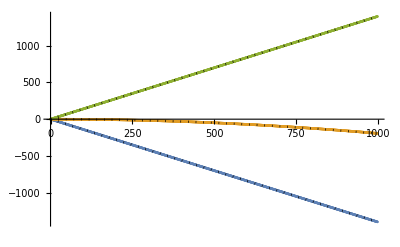

```mathematica
Show[ListPlot[{
Table[{ZS[[ii,1]],(ZS[[ii,2]][[1]] - ZS[[1,2]][[1]])/(2π 1*^6)},{ii,1,1000}],Table[{ZS[[ii,1]],(ZS[[ii,2]][[2]] - ZS[[1,2]][[2]])/(2π 1*^6)},{ii,1,1000}],Table[{ZS[[ii,1]],(ZS[[ii,2]][[3]]- ZS[[1,2]][[3]])/(2π 1*^6)},{ii,1,1000}]}],Plot[{- μB(Bz/10000)/(2π 1*^6),- μB^2(Bz/10000)^2/(Abs[Δ1] 2π 1*^6), μB(Bz/10000)/(2π 1*^6)},{Bz,0,1000},PlotStyle->{{Dotted,Black}}]]
```

```mathematica
(*Okay, that looks good. Let's really check that they're the same:*)
```

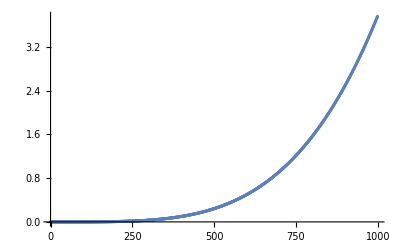

```mathematica
ListPlot[Table[{ZS[[ii,1]],(ZS[[ii,2]][[2]] - ZS[[1,2]][[2]])/(2π 1*^6) - - μB^2((ii-1)/10000)^2/(Abs[Δ1] 2π 1*^6)},{ii,1,1000}]]
```

```mathematica
(*I don't think this can couple to any other state, right? This must be numerical error? What is it fractionally??*)
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

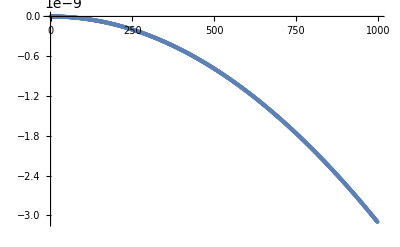

```mathematica
ListPlot[Table[{ZS[[ii,1]],((ZS[[ii,2]][[2]] - ZS[[1,2]][[2]])/(2π 1*^6) - - μB^2((ii-1)/10000)^2/(Abs[Δ1] 2π 1*^6))/(ZS[[ii,2]][[2]] - ZS[[1,2]][[2]])},{ii,1,1000}]]
```

```mathematica
(*Okay, maybe numerical error, but let's double check by making sure the states involved don't couple to anythign else*)
Hmag[1][[All,1]]
```

{0.,0.,8.79254×10^10,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
Hmag[1][[1,All]]
```

{0.,0.,8.79254×10^10,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
Hmag[1][[All,3]]
```

{8.79254×10^10,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
Hmag[1][[3,All]]
```

{8.79254×10^10,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
(*Yeah, so I guess it's numerical error...*)
```

### Spontaneous emission rate definition for each state

First find the reduced matrix elements in J basis and then extend to F.

```mathematica
Solve[1/(4π ϵo)4/3(dps^2 ωsp^3)/(ℏ c^3) == (2 1/2 + 1)/(2 1/2+1)9.53*^7,dps]
 Solve[1/(4π ϵo)4/3(dpd^2 ωdp^3)/(ℏ c^3) == (2 1/2 + 1)/(2 3/2+1)3.1*^7,dpd]
 Solve[1/(4π ϵo)4/3(dps2^2 ωsp2^3)/(ℏ c^3) == (2 3/2 + 1)/(2 1/2+1)1.188*^8,dps2]
 Solve[1/(4π ϵo)4/3(dpd2^2 ωdp2^3)/(ℏ c^3) == (2 3/2 + 1)/(2 3/2+1)0.04610*^8,dpd2]
 Solve[1/(4π ϵo)4/3(dpd3^2 ωdp3^3)/(ℏ c^3) == (2 3/2 + 1)/(2 5/2+1)0.3758*^8,dpd3]
```

{{dps→-2.01524×10^-29},{dps→2.01524×10^-29}}

{{dpd→-1.22799×10^-29},{dpd→1.22799×10^-29}}

{{dps2→-2.81781×10^-29},{dps2→2.81781×10^-29}}

{{dpd2→-5.7221×10^-30},{dpd2→5.7221×10^-30}}

{{dpd3→-1.43435×10^-29},{dpd3→1.43435×10^-29}}

```mathematica
(*Dipole moment chosen to reproduces reported A values*)
ReducedMEsp = 2.015239355816575*^-29;
ReducedMEdp =1.2279939393594047*^-29;
ReducedMEsp2 = 2.817809407506768*^-29;
ReducedMEdp2 = 5.7221015823024066*^-30;
ReducedMEdp3 = 1.4343548843989273*^-29;

(*Define functions that gives the reduced matrix element between the states and the ω. This part is a touch kludgy*)
RMEmatrix = Table[0,{ii,1,5},{jj,1,5}];
ωmatrix = Table[0,{ii,1,5},{jj,1,5}];
RMEmatrix[[1,2]] = ReducedMEsp;
ωmatrix[[1,2]] = ωsp;
RMEmatrix[[1,4]] = ReducedMEsp2;
ωmatrix[[1,4]] = ωsp2;
RMEmatrix[[2,3]] = ReducedMEdp;
ωmatrix[[2,3]] = ωdp;
RMEmatrix[[4,3]] = ReducedMEdp2;
ωmatrix[[4,3]] = ωdp2;
RMEmatrix[[4,5]] = ReducedMEdp3;
ωmatrix[[4,5]] = ωdp3;
RMEmatrix = RMEmatrix + Transpose[RMEmatrix];
ωmatrix = ωmatrix + Transpose[ωmatrix];
RME[config1_,config2_] := RMEmatrix [[config1,config2]]
ωtran[config1_,config2_]:= ωmatrix[[config1,config2]]
```

```mathematica
(*Now define dipole moment between hyperfine states*)
(*Then hyperfine basis dipoles are:*)
dreducedHyperfine[Jp_,Fp_,J_,F_,dreducedJ_]:= dreducedJ (-1)^(Fp+J+1+1/2)√((2Fp+1)(2J+1))SixJSymbol[{J,Jp,1},{Fp,F,1/2}]
dreducedHyperfine::usage = " dreducedHyperfine[Jp,Fp,J,F,dreducedJ] gives the reduced matrix element of the transition dipole moment in the hyperfine basis. Jp & Fp are the excited state quantum numbers. J & F are the ground state. dreducedJ is the reduced matrix element in the J basis, which is found by solving 1/(4  π ϵo)4/3dreducedJ^2/(ℏ SuperscriptBox[c, 3]) == (2 J  +  1)/(2 Jp + 1)1/τ.  ";

dif[Fp_,mFp_,F_,mF_, q_,dreducedF_]:= dreducedF (-1)^(Fp-1+mF)√(2F+1)ThreeJSymbol[{Fp,mFp},{1,q},{F,-mF}]
dif::usage = "dif[Fp,mFp,F,mF, q,dreducedF] gives the transition dipole moment between hyperfine states. Fp & mFp are excited state quantum numbers. F & mF are ground state quantum numbers. q is the radiation polarization -1 for σ^-, 0 for π, +1 for σ^+ (as viewed in the emission process). dreducedF comes from dreducedHyperfine function";
```

```mathematica
(*And decay rates*)
Γgen[d_,ω_] := 1/(4π ϵo)4/3(d^2 ω^3)/(ℏ c^3)
```

```mathematica
Table[ RME[config/.State[[ii,8]],config/.State[[jj,8]]],{ii,1,1},{jj,6,6}]
```

{{2.01524×10^-29}}

```mathematica
State[[1]]
```

{1,Eng→0,F→0,Mf→0,J→1/2,L→0,n→6,config→1}

```mathematica
Table[  ωtran[ config/.State[[ii,8]],config/.State[[jj,8]]],{ii,1,1},{jj,6,6}]
```

{{3.81773×10^15}}

```mathematica
Clear[Γ]
```

```mathematica
Γ[ii_,jj_]:= Sum[
Γgen[dif[F/.State[[ii,3]],Mf/.State[[ii,4]],F/.State[[jj,3]],Mf/.State[[jj,4]],q,dreducedHyperfine[J/.State[[ii,5]],F/.State[[ii,3]],J/.State[[jj,5]],F/.State[[jj,3]],RME[config/.State[[ii,8]],config/.State[[jj,8]]]]], ωtran[config/.State[[ii,8]],config/.State[[jj,8]]]],{q,-1,1,1}];
```

```mathematica
(*Okay, now let's check that we get the right decay rates.*)
(*We shoudl get:
{9.53*^7, 3.1*^7, 1.188*^8, 0.04610*^8, 0.3758*^8}*)
```

```mathematica
Sum[Γ[6,k],{k,1,4}]
```

ClebschGordan::phy: ThreeJSymbol[{1, -1}, {1, -1}, {0, 0}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1, -1}, {1, 0}, {0, 0}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1, -1}, {1, -1}, {1, 1}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

3.17667×10^7

```mathematica
Sum[Γ[6,k],{k,9,16}]
```

ClebschGordan::phy: ThreeJSymbol[{1, -1}, {1, -1}, {1, 1}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1, -1}, {1, -1}, {1, 0}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1, -1}, {1, 0}, {1, 0}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

2.58333×10^7

```mathematica
Sum[Γ[17,k],{k,1,4}]
```

ClebschGordan::phy: ThreeJSymbol[{1, -1}, {1, -1}, {0, 0}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1, -1}, {1, 0}, {0, 0}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1, -1}, {1, -1}, {1, 1}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

1.98×10^7

```mathematica
Sum[Γ[17,k],{k,9,16}]
```

ClebschGordan::phy: ThreeJSymbol[{1, -1}, {1, -1}, {1, 1}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1, -1}, {1, -1}, {1, 0}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1, -1}, {1, 0}, {1, 0}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

2.61233×10^6

```mathematica
Sum[Γ[17,k],{k,25,36}]
```

ClebschGordan::phy: ThreeJSymbol[{1, -1}, {1, 0}, {2, 2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1, -1}, {1, -1}, {2, 1}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1, -1}, {1, -1}, {2, 0}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

SixJSymbol::tri: SixJSymbol[{5/2, 3/2, 1}, {1, 3, 1/2}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{1, -1}, {1, -1}, {3, 3}] is not triangular.

SixJSymbol::tri: SixJSymbol[{5/2, 3/2, 1}, {1, 3, 1/2}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{1, -1}, {1, 0}, {3, 3}] is not triangular.

SixJSymbol::tri: SixJSymbol[{5/2, 3/2, 1}, {1, 3, 1/2}] is not triangular.

General::stop: Further output of SixJSymbol :: tri will be suppressed during this calculation.

ClebschGordan::tri: ThreeJSymbol[{1, -1}, {1, -1}, {3, 2}] is not triangular.

General::stop: Further output of ClebschGordan :: tri will be suppressed during this calculation.

3.3822×10^7

```mathematica
(*Okay, looks like we now have the decay between each state in Γ[ii,jj]*)
```

### Define the relaxation Lindblad stuff (this is slow. I’ve pasted the result into notebook so if you can, skip this part and pass the paste result on)

```mathematica
(*Define the density matrix*)
ρ = ToExpression[Table[StringJoin[{"ρ", ToString[ii],"b",ToString[jj],"[t]"}],{ii,1,36},{jj,1,36}]];
```

```mathematica
(*Damping given by*)
Ldamp[X_,A_] :=-1/2( Transpose[X].X.A + A.Transpose[X].X- 2 X.A.Transpose[X])
(*To get the Zeeman coherence decay right you have to correctly account for the sign of the dipole matrix element! Since I'm square rooting to get magnitude it disappears, so have to add it back*)
WhichSign[ii_,jj_,q_]:=Sign[dif[F/.State[[ii,3]],Mf/.State[[ii,4]], F/.State[[jj,3]],Mf/.State[[jj,4]],q,1]]
Cop[ii_,jj_,q_] := √Γ[ii,jj] WhichSign[ii,jj,q]Table[KroneckerDelta[kk,ii] KroneckerDelta[mm,jj],{kk,1,36},{mm,1,36}]
```

```mathematica
(*(Mf/.State[[jj,4]]) -( Mf/.State[[ii,4]])*)
```

```mathematica
(*Rememer the point of the Lindblad relaxation part is that you add up each distinguishable decay mode separately. If something is indistinguishable then you add it up as one relaxation bit. I imagine if a big B-field is turned on to make these decays distinguishable then the Hamiltonian evolution part will suppress the Zeeman coherence stuff. This part is a little kludgy but would probably take a while to make it nice and automatic.*)
(*So need a function that adds all of the decays of one polarization from one group of states, specficied by F and config, to another group of states, specified by F and config:*)
```

```mathematica
Cuse[config1_, F1_,config2_,F2_,q_] :=  Sum[ KroneckerDelta[config1,config/.State[[jj,8]]] KroneckerDelta[F1, F/.State[[jj,3]]] Sum[Cop[ii,jj,q] KroneckerDelta[config2,config/.State[[ii,8]]] KroneckerDelta[F2, F/.State[[ii,3]]],{ii,1,36}],{jj,1,36}]
Cuse::usage = "Cuse[config1_, F1_,config2_,F2_] gives the relaxation matrix for a decay from one F state to another. config1 and F1 specify the excited state, while config2 and F2 specify the lower state that is decayed to. q is the polarization of the decay mode. It's emission so σm is q = 1, etc.";
```

```mathematica
Sum[Cop[ii,jj,q] KroneckerDelta[config2,config/.State[[ii,8]]] KroneckerDelta[F2, F/.State[[ii,3]]],{ii,1,36}]
```

Part::pkspec1: The expression jj cannot be used as a part specification.

ReplaceAll::reps: {{{1, Eng → 0, F → 0, Mf → 0, J → 1/2, L → 0, n → 6, config → 1}, {2, Eng → -6.23606×10^10, F → 1, Mf → -1, J → 1/2, L → 0, n → 6, config → 1}, {3, Eng → -6.23606×10^10, F → 1, Mf → 0, J → 1/2, L → 0, n → 6, config → 1}, « 31 », {35, Eng → 1.07208×10^15, F → 3, Mf → 2, J → 5/2, L → 2, n → 5, config → 5}, {36, Eng → 1.07208×10^15, F → 3, Mf → 3, J → 5/2, L → 2, n → 5, config → 5}} ⟦ jj, 3 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::pkspec1: The expression jj cannot be used as a part specification.

ReplaceAll::reps: {{{1, Eng → 0, F → 0, Mf → 0, J → 1/2, L → 0, n → 6, config → 1}, {2, Eng → -6.23606×10^10, F → 1, Mf → -1, J → 1/2, L → 0, n → 6, config → 1}, {3, Eng → -6.23606×10^10, F → 1, Mf → 0, J → 1/2, L → 0, n → 6, config → 1}, « 31 », {35, Eng → 1.07208×10^15, F → 3, Mf → 2, J → 5/2, L → 2, n → 5, config → 5}, {36, Eng → 1.07208×10^15, F → 3, Mf → 3, J → 5/2, L → 2, n → 5, config → 5}} ⟦ jj, 4 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::pkspec1: The expression jj cannot be used as a part specification.

General::stop: Further output of Part :: pkspec1 will be suppressed during this calculation.

ReplaceAll::reps: {{{1, Eng → 0, F → 0, Mf → 0, J → 1/2, L → 0, n → 6, config → 1}, {2, Eng → -6.23606×10^10, F → 1, Mf → -1, J → 1/2, L → 0, n → 6, config → 1}, {3, Eng → -6.23606×10^10, F → 1, Mf → 0, J → 1/2, L → 0, n → 6, config → 1}, « 31 », {35, Eng → 1.07208×10^15, F → 3, Mf → 2, J → 5/2, L → 2, n → 5, config → 5}, {36, Eng → 1.07208×10^15, F → 3, Mf → 3, J → 5/2, L → 2, n → 5, config → 5}} ⟦ jj, 5 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

{1}
 |  |  |  |

```mathematica
(*Let's check this on some test cases*)
```

```mathematica
(*The decay from P1/2, F = 0 to S1/2 F = 1 are all single state events*)
(*σm*)
Cop[2,5,1];
(*π*)
Cop[3,5,0];
(*σp*)
Cop[4,5,-1];
```

ClebschGordan::phy: ThreeJSymbol[{1, -1}, {1, -1}, {0, 0}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1, -1}, {1, 0}, {0, 0}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1, 0}, {1, -1}, {0, 0}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1, 0}, {1, 1}, {0, 0}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1, 1}, {1, 0}, {0, 0}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1, 1}, {1, 1}, {0, 0}] is not physical.

```mathematica
(*q = 0 mode*)
Cuse[2,0,1,1,0] == Cop[3,5,0]
```

SixJSymbol::tri: SixJSymbol[{1/2, 1/2, 1}, {0, 0, 1/2}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{0, 0}, {1, -1}, {0, 0}] is not triangular.

SixJSymbol::tri: SixJSymbol[{1/2, 1/2, 1}, {0, 0, 1/2}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{0, 0}, {1, 0}, {0, 0}] is not triangular.

SixJSymbol::tri: SixJSymbol[{1/2, 1/2, 1}, {0, 0, 1/2}] is not triangular.

General::stop: Further output of SixJSymbol :: tri will be suppressed during this calculation.

ClebschGordan::tri: ThreeJSymbol[{0, 0}, {1, 1}, {0, 0}] is not triangular.

General::stop: Further output of ClebschGordan :: tri will be suppressed during this calculation.

ClebschGordan::phy: ThreeJSymbol[{1, -1}, {1, -1}, {0, 0}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1, -1}, {1, 0}, {0, 0}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

True

General::stop: Further output of ClebschGordan::phy will be suppressed during this calculation.

ClebschGordan::phy: ThreeJSymbol[{1,-1},{1,0},{0,0}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1,-1},{1,-1},{0,0}] is not physical.

General::stop: Further output of ClebschGordan::tri will be suppressed during this calculation.

ClebschGordan::tri: ThreeJSymbol[{0,0},{1,1},{0,0}] is not triangular.

General::stop: Further output of SixJSymbol::tri will be suppressed during this calculation.

SixJSymbol::tri: SixJSymbol[{1/2,1/2,1},{0,0,1/2}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{0,0},{1,0},{0,0}] is not triangular.

SixJSymbol::tri: SixJSymbol[{1/2,1/2,1},{0,0,1/2}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{0,0},{1,-1},{0,0}] is not triangular.

SixJSymbol::tri: SixJSymbol[{1/2,1/2,1},{0,0,1/2}] is not triangular.

```mathematica
(*Decays from P1/2, F = 1 to S1/2 F = 0 are all single state events*)
(*σm*)
Cop[1,8,1];
(*π*)
Cop[1,7,0];
(*σp*)
Cop[1,6,-1];
Cuse[2,1,1,0,0] == Cop[1,7,0]
```

ClebschGordan::phy: ThreeJSymbol[{0, 0}, {1, -1}, {1, -1}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{0, 0}, {1, 0}, {1, -1}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{0, 0}, {1, -1}, {1, 0}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{0, 0}, {1, 1}, {1, 0}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{0, 0}, {1, 0}, {1, 1}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{0, 0}, {1, 1}, {1, 1}] is not physical.

SixJSymbol::tri: SixJSymbol[{1/2, 1/2, 1}, {0, 0, 1/2}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{0, 0}, {1, -1}, {0, 0}] is not triangular.

SixJSymbol::tri: SixJSymbol[{1/2, 1/2, 1}, {0, 0, 1/2}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{0, 0}, {1, 0}, {0, 0}] is not triangular.

SixJSymbol::tri: SixJSymbol[{1/2, 1/2, 1}, {0, 0, 1/2}] is not triangular.

General::stop: Further output of SixJSymbol :: tri will be suppressed during this calculation.

ClebschGordan::tri: ThreeJSymbol[{0, 0}, {1, 1}, {0, 0}] is not triangular.

General::stop: Further output of ClebschGordan :: tri will be suppressed during this calculation.

ClebschGordan::phy: ThreeJSymbol[{1, -1}, {1, -1}, {0, 0}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1, -1}, {1, 0}, {0, 0}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

True

```mathematica
Cuse[2,1,1,0,1] == Cop[1,8,1]
```

SixJSymbol::tri: SixJSymbol[{1/2, 1/2, 1}, {0, 0, 1/2}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{0, 0}, {1, -1}, {0, 0}] is not triangular.

SixJSymbol::tri: SixJSymbol[{1/2, 1/2, 1}, {0, 0, 1/2}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{0, 0}, {1, 0}, {0, 0}] is not triangular.

SixJSymbol::tri: SixJSymbol[{1/2, 1/2, 1}, {0, 0, 1/2}] is not triangular.

General::stop: Further output of SixJSymbol :: tri will be suppressed during this calculation.

ClebschGordan::tri: ThreeJSymbol[{0, 0}, {1, 1}, {0, 0}] is not triangular.

General::stop: Further output of ClebschGordan :: tri will be suppressed during this calculation.

ClebschGordan::phy: ThreeJSymbol[{1, -1}, {1, -1}, {0, 0}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1, -1}, {1, 0}, {0, 0}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1, 0}, {1, -1}, {0, 0}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

True

```mathematica
(*Decay from P1/2, F = 1 to S1/2 F = 1 are all two state events*)
(*σm*)
Cop[2,7,1] + Cop[3,8,1];
(*π*)
Cop[2,6,0] + Cop[4,8,0];
(*σp*)
Cop[3,6,-1] + Cop[4,7,-1];
Cuse[2,1,1,1,-1] == Cop[3,6,-1] + Cop[4,7,-1]
```

ClebschGordan::phy: ThreeJSymbol[{1, -1}, {1, -1}, {1, 0}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1, -1}, {1, 0}, {1, 0}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1, 0}, {1, -1}, {1, -1}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

ClebschGordan::phy: ThreeJSymbol[{1, -1}, {1, -1}, {1, 1}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1, -1}, {1, 1}, {1, 1}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1, 1}, {1, -1}, {1, -1}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

ClebschGordan::phy: ThreeJSymbol[{1, 0}, {1, 0}, {1, 1}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1, 0}, {1, 1}, {1, 1}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1, 1}, {1, 0}, {1, 0}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

SixJSymbol::tri: SixJSymbol[{1/2, 1/2, 1}, {0, 0, 1/2}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{0, 0}, {1, -1}, {0, 0}] is not triangular.

SixJSymbol::tri: SixJSymbol[{1/2, 1/2, 1}, {0, 0, 1/2}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{0, 0}, {1, 0}, {0, 0}] is not triangular.

SixJSymbol::tri: SixJSymbol[{1/2, 1/2, 1}, {0, 0, 1/2}] is not triangular.

General::stop: Further output of SixJSymbol :: tri will be suppressed during this calculation.

ClebschGordan::tri: ThreeJSymbol[{0, 0}, {1, 1}, {0, 0}] is not triangular.

General::stop: Further output of ClebschGordan :: tri will be suppressed during this calculation.

ClebschGordan::phy: ThreeJSymbol[{1, -1}, {1, -1}, {0, 0}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1, -1}, {1, 0}, {0, 0}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1, -1}, {1, -1}, {0, 0}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

True

```mathematica
(*Okay, so far, so good! Let's check a decay to the D5/2 F = 3 state from the P3/2 F = 2 state*)
(*π polarization*)
Cuse[4,2,5,3,0] == Cop[31,20,0]+Cop[32,21,0]+Cop[33,22,0]+Cop[34,23,0]+Cop[35,24,0]
```

SixJSymbol::tri: SixJSymbol[{1/2, 1/2, 1}, {0, 0, 1/2}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{0, 0}, {1, -1}, {0, 0}] is not triangular.

SixJSymbol::tri: SixJSymbol[{1/2, 1/2, 1}, {0, 0, 1/2}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{0, 0}, {1, 0}, {0, 0}] is not triangular.

SixJSymbol::tri: SixJSymbol[{1/2, 1/2, 1}, {0, 0, 1/2}] is not triangular.

General::stop: Further output of SixJSymbol :: tri will be suppressed during this calculation.

ClebschGordan::tri: ThreeJSymbol[{0, 0}, {1, 1}, {0, 0}] is not triangular.

General::stop: Further output of ClebschGordan :: tri will be suppressed during this calculation.

ClebschGordan::phy: ThreeJSymbol[{1, -1}, {1, -1}, {0, 0}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1, -1}, {1, 0}, {0, 0}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

True

```mathematica
(*Alright, I think this is working now just need to make the relaxation matrix. All decays start in either config 2 or 4*)
dρdtrelax  = Sum[Sum[Sum[Sum[Ldamp[Cuse[2,F1,config2,F2,q],ρ],{F2,0,3}],{q,-1,1}],{config2,1,5}],{F1,0,1}] + Sum[Sum[Sum[Sum[Ldamp[Cuse[4,F1,config2,F2,q],ρ],{F2,0,3}],{q,-1,1}],{config2,1,5}],{F1,1,2}];
```

SixJSymbol::tri: SixJSymbol[{1/2, 1/2, 1}, {0, 0, 1/2}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{0, 0}, {1, -1}, {0, 0}] is not triangular.

SixJSymbol::tri: SixJSymbol[{1/2, 1/2, 1}, {0, 0, 1/2}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{0, 0}, {1, 0}, {0, 0}] is not triangular.

SixJSymbol::tri: SixJSymbol[{1/2, 1/2, 1}, {0, 0, 1/2}] is not triangular.

General::stop: Further output of SixJSymbol :: tri will be suppressed during this calculation.

ClebschGordan::tri: ThreeJSymbol[{0, 0}, {1, 1}, {0, 0}] is not triangular.

General::stop: Further output of ClebschGordan :: tri will be suppressed during this calculation.

ClebschGordan::phy: ThreeJSymbol[{1, -1}, {1, -1}, {0, 0}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1, -1}, {1, 0}, {0, 0}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1, -1}, {1, -1}, {0, 0}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

```mathematica
MatrixForm[FullSimplify[Diagonal[dρdtrelax]]]
```

(0.+1.584×10^8 ρ17b17[t]+1.584×10^8 ρ18b18[t]+1.584×10^8 ρ19b19[t]+3.17667×10^7 ρ6b6[t]+3.17667×10^7 ρ7b7[t]+3.17667×10^7 ρ8b8[t]
0.+3.96×10^7 ρ17b17[t]+3.96×10^7 ρ18b18[t]+2.376×10^8 ρ20b20[t]+1.188×10^8 ρ21b21[t]+3.96×10^7 ρ22b22[t]+3.17667×10^7 ρ5b5[t]+3.17667×10^7 ρ6b6[t]+3.17667×10^7 ρ7b7[t]
0.+3.96×10^7 ρ17b17[t]+3.96×10^7 ρ19b19[t]+1.188×10^8 ρ21b21[t]+1.584×10^8 ρ22b22[t]+1.188×10^8 ρ23b23[t]+3.17667×10^7 ρ5b5[t]+3.17667×10^7 ρ6b6[t]+3.17667×10^7 ρ8b8[t]
0.+3.96×10^7 ρ18b18[t]+3.96×10^7 ρ19b19[t]+3.96×10^7 ρ22b22[t]+1.188×10^8 ρ23b23[t]+2.376×10^8 ρ24b24[t]+3.17667×10^7 ρ5b5[t]+3.17667×10^7 ρ7b7[t]+3.17667×10^7 ρ8b8[t]
0.-1.108×10^8 ρ5b5[t]
0.-1.108×10^8 ρ6b6[t]
0.-1.108×10^8 ρ7b7[t]
0.-1.108×10^8 ρ8b8[t]
0.+1.92083×10^6 ρ17b17[t]+1.92083×10^6 ρ18b18[t]+461000. ρ20b20[t]+230500. ρ21b21[t]+76833.3 ρ22b22[t]+5.16667×10^6 ρ5b5[t]+1.29167×10^6 ρ6b6[t]+1.29167×10^6 ρ7b7[t]
0.+1.92083×10^6 ρ17b17[t]+1.92083×10^6 ρ19b19[t]+230500. ρ21b21[t]+307333. ρ22b22[t]+230500. ρ23b23[t]+5.16667×10^6 ρ5b5[t]+1.29167×10^6 ρ6b6[t]+1.29167×10^6 ρ8b8[t]
0.+1.92083×10^6 ρ18b18[t]+1.92083×10^6 ρ19b19[t]+76833.3 ρ22b22[t]+230500. ρ23b23[t]+461000. ρ24b24[t]+5.16667×10^6 ρ5b5[t]+1.29167×10^6 ρ7b7[t]+1.29167×10^6 ρ8b8[t]
0.+461000. ρ17b17[t]+2.766×10^6 ρ20b20[t]+1.383×10^6 ρ21b21[t]+7.75×10^6 ρ6b6[t]
0.+230500. ρ17b17[t]+230500. ρ18b18[t]+1.383×10^6 ρ20b20[t]+691500. ρ21b21[t]+2.0745×10^6 ρ22b22[t]+3.875×10^6 ρ6b6[t]+3.875×10^6 ρ7b7[t]
0.+76833.3 ρ17b17[t]+307333. ρ18b18[t]+76833.3 ρ19b19[t]+2.0745×10^6 ρ21b21[t]+2.0745×10^6 ρ23b23[t]+1.29167×10^6 ρ6b6[t]+5.16667×10^6 ρ7b7[t]+1.29167×10^6 ρ8b8[t]
0.+230500. ρ18b18[t]+230500. ρ19b19[t]+2.0745×10^6 ρ22b22[t]+691500. ρ23b23[t]+1.383×10^6 ρ24b24[t]+3.875×10^6 ρ7b7[t]+3.875×10^6 ρ8b8[t]
0.+461000. ρ19b19[t]+1.383×10^6 ρ23b23[t]+2.766×10^6 ρ24b24[t]+7.75×10^6 ρ8b8[t]
0.-2.67263×10^8 ρ17b17[t]
0.-2.67263×10^8 ρ18b18[t]
0.-2.67263×10^8 ρ19b19[t]
0.-2.67263×10^8 ρ20b20[t]
0.-2.67263×10^8 ρ21b21[t]
0.-2.67263×10^8 ρ22b22[t]
0.-2.67263×10^8 ρ23b23[t]
0.-2.67263×10^8 ρ24b24[t]
0.+1.5032×10^7 ρ17b17[t]+1.11348×10^6 ρ20b20[t]+556741. ρ21b21[t]
0.+7.516×10^6 ρ17b17[t]+7.516×10^6 ρ18b18[t]+556741. ρ20b20[t]+278370. ρ21b21[t]+835111. ρ22b22[t]
0.+2.50533×10^6 ρ17b17[t]+1.00213×10^7 ρ18b18[t]+2.50533×10^6 ρ19b19[t]+835111. ρ21b21[t]+835111. ρ23b23[t]
0.+7.516×10^6 ρ18b18[t]+7.516×10^6 ρ19b19[t]+835111. ρ22b22[t]+278370. ρ23b23[t]+556741. ρ24b24[t]
0.+1.5032×10^7 ρ19b19[t]+556741. ρ23b23[t]+1.11348×10^6 ρ24b24[t]
0.+1.67022×10^7 ρ20b20[t]
0.+5.56741×10^6 ρ20b20[t]+1.11348×10^7 ρ21b21[t]
0.+1.11348×10^6 ρ20b20[t]+8.90785×10^6 ρ21b21[t]+6.68089×10^6 ρ22b22[t]
0.+3.34044×10^6 ρ21b21[t]+1.00213×10^7 ρ22b22[t]+3.34044×10^6 ρ23b23[t]
0.+6.68089×10^6 ρ22b22[t]+8.90785×10^6 ρ23b23[t]+1.11348×10^6 ρ24b24[t]
0.+1.11348×10^7 ρ23b23[t]+5.56741×10^6 ρ24b24[t]
0.+1.67022×10^7 ρ24b24[t])

```mathematica
(*That looks right. Let's check some of the coherence decays*)
```

```mathematica
FullSimplify[dρdtrelax[[1,5]]]
```

0.-5.54×10^7 ρ1b5[t]

```mathematica
Sum[Γ[ii,5],{ii,1,36}]/2
```

SixJSymbol::tri: SixJSymbol[{1/2, 1/2, 1}, {0, 0, 1/2}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{0, 0}, {1, -1}, {0, 0}] is not triangular.

SixJSymbol::tri: SixJSymbol[{1/2, 1/2, 1}, {0, 0, 1/2}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{0, 0}, {1, 0}, {0, 0}] is not triangular.

SixJSymbol::tri: SixJSymbol[{1/2, 1/2, 1}, {0, 0, 1/2}] is not triangular.

General::stop: Further output of SixJSymbol :: tri will be suppressed during this calculation.

ClebschGordan::tri: ThreeJSymbol[{0, 0}, {1, 1}, {0, 0}] is not triangular.

General::stop: Further output of ClebschGordan :: tri will be suppressed during this calculation.

ClebschGordan::phy: ThreeJSymbol[{1, -1}, {1, -1}, {0, 0}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1, -1}, {1, 0}, {0, 0}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1, 0}, {1, -1}, {0, 0}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

5.54×10^7

```mathematica
FullSimplify[dρdtrelax[[18,5]]]
```

0.-1.89032×10^8 ρ18b5[t]

```mathematica
(Sum[Γ[ii,5],{ii,1,36}] + Sum[Γ[ii,18],{ii,1,36}])/2
```

SixJSymbol::tri: SixJSymbol[{1/2, 1/2, 1}, {0, 0, 1/2}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{0, 0}, {1, -1}, {0, 0}] is not triangular.

SixJSymbol::tri: SixJSymbol[{1/2, 1/2, 1}, {0, 0, 1/2}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{0, 0}, {1, 0}, {0, 0}] is not triangular.

SixJSymbol::tri: SixJSymbol[{1/2, 1/2, 1}, {0, 0, 1/2}] is not triangular.

General::stop: Further output of SixJSymbol :: tri will be suppressed during this calculation.

ClebschGordan::tri: ThreeJSymbol[{0, 0}, {1, 1}, {0, 0}] is not triangular.

General::stop: Further output of ClebschGordan :: tri will be suppressed during this calculation.

ClebschGordan::phy: ThreeJSymbol[{1, -1}, {1, -1}, {0, 0}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1, -1}, {1, 0}, {0, 0}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1, 0}, {1, -1}, {0, 0}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

1.89032×10^8

```mathematica
(*Okay those are decaying correctly. Now let's look at a zeeman coherence*)
FullSimplify[dρdtrelax[[2,3]]]
```

0.+3.96×10^7 ρ18b19[t]+1.68009×10^8 ρ20b21[t]+1.37178×10^8 ρ21b22[t]+6.85892×10^7 ρ22b23[t]+3.17667×10^7 ρ7b8[t]

```mathematica
(*This looks correct to me. Whew. Since it literally took like an hour to for mathematica to calcuata dρdtrelax. Let's print it here so in principle you can skip calculation in future.*)
```

```mathematica
dρdtrelax
```

{1}
 |  |  |  |

### Just paste in the Lindblad answer

```mathematica
(*Define the density matrix*)
ρ = ToExpression[Table[StringJoin[{"ρ", ToString[ii],"b",ToString[jj],"[t]"}],{ii,1,36},{jj,1,36}]];
```

```mathematica
dρdtrelax = {{0.+1/2 (0.+2 (0.+12585.706178041819 (0.+12585.706178041819 ρ17b17[t])))+1/2 (0.+2 (0.+12585.706178041819 (0.+12585.706178041819 ρ18b18[t])))+1/2 (0.+2 (0.+12585.706178041819 (0.+12585.706178041819 ρ19b19[t])))+1/2 (0.+2 (0.+5636.192568273967 (0.+5636.192568273967 ρ6b6[t])))+1/2 (0.+2 (0.+5636.192568273967 (0.+5636.192568273967 ρ7b7[t])))+1/2 (0.+2 (0.+5636.192568273967 (0.+5636.192568273967 ρ8b8[t]))),0.,0.,0.,0.+1/2 (0.+5636.192568273965 (0.-5636.192568273965 ρ1b5[t]))+1/2 (0.+2273.0302828309764 (0.-2273.0302828309764 ρ1b5[t]))-2273.0302828309764 (0.+2273.0302828309764 ρ1b5[t])-5636.192568273965 (0.+5636.192568273965 ρ1b5[t]),0.+1/2 (0.+5636.192568273964 (0.-5636.192568273964 ρ1b6[t]))+1/2 (0.+1968.501968502953 (0.-1968.501968502953 ρ1b6[t]))+1/2 (0.+1136.5151414154882 (0.-1136.5151414154882 ρ1b6[t]))-1136.5151414154882 (0.+1136.5151414154882 ρ1b6[t])+1/2 (0.-2783.882181415011 (0.+2783.882181415011 ρ1b6[t]))+1/2 (0.-5636.192568273964 (0.+5636.192568273964 ρ1b6[t]))+1/2 (0.-5636.192568273967 (0.+5636.192568273967 ρ1b6[t])),0.+1/2 (0.+5636.192568273964 (0.-5636.192568273964 ρ1b7[t]))+1/2 (0.+2273.0302828309764 (0.-2273.0302828309764 ρ1b7[t]))+1/2 (0.+1136.5151414154882 (0.-1136.5151414154882 ρ1b7[t]))-1968.501968502953 (0.+1968.501968502953 ρ1b7[t])+1/2 (0.-1136.5151414154882 (0.+1136.5151414154882 ρ1b7[t]))+1/2 (0.-5636.192568273964 (0.+5636.192568273964 ρ1b7[t]))+1/2 (0.-5636.192568273967 (0.+5636.192568273967 ρ1b7[t])),0.+1/2 (0.+5636.192568273964 (0.-5636.192568273964 ρ1b8[t]))+1/2 (0.+1968.501968502953 (0.-1968.501968502953 ρ1b8[t]))+1/2 (0.+1136.5151414154882 (0.-1136.5151414154882 ρ1b8[t]))-1136.5151414154882 (0.+1136.5151414154882 ρ1b8[t])+1/2 (0.-2783.882181415011 (0.+2783.882181415011 ρ1b8[t]))+1/2 (0.-5636.192568273964 (0.+5636.192568273964 ρ1b8[t]))+1/2 (0.-5636.192568273967 (0.+5636.192568273967 ρ1b8[t])),0.,0.,0.,0.,0.,0.,0.,0.,0.+1/2 (0.+6292.853089020909 (0.-6292.853089020909 ρ1b17[t]))+1/2 (0.+2741.5324181924243 (0.-2741.5324181924243 ρ1b17[t]))+1/2 (0.+1385.9413166989912 (0.-1385.9413166989912 ρ1b17[t]))+1/2 (0.+480.1041553663121 (0.-480.1041553663121 ρ1b17[t]))+1/2 (0.-277.1882633397982 (0.+277.1882633397982 ρ1b17[t]))+1/2 (0.-678.9698078707181 (0.+678.9698078707181 ρ1b17[t]))+1/2 (0.-1385.9413166989912 (0.+1385.9413166989912 ρ1b17[t]))+1/2 (0.-1582.8244796354816 (0.+1582.8244796354816 ρ1b17[t]))+1/2 (0.-3877.112327493234 (0.+3877.112327493234 ρ1b17[t]))+1/2 (0.-6292.853089020909 (0.+6292.853089020909 ρ1b17[t]))+1/2 (0.-12585.706178041819 (0.+12585.706178041819 ρ1b17[t])),0.+1/2 (0.+6292.853089020909 (0.-6292.853089020909 ρ1b18[t]))+1/2 (0.+3165.648959270963 (0.-3165.648959270963 ρ1b18[t]))+1/2 (0.+1385.9413166989912 (0.-1385.9413166989912 ρ1b18[t]))+1/2 (0.+554.3765266795964 (0.-554.3765266795964 ρ1b18[t]))-480.1041553663121 (0.+480.1041553663121 ρ1b18[t])-2741.5324181924243 (0.+2741.5324181924243 ρ1b18[t])+1/2 (0.-1385.9413166989912 (0.+1385.9413166989912 ρ1b18[t]))+1/2 (0.-6292.853089020909 (0.+6292.853089020909 ρ1b18[t]))+1/2 (0.-12585.706178041819 (0.+12585.706178041819 ρ1b18[t])),0.+1/2 (0.+6292.853089020909 (0.-6292.853089020909 ρ1b19[t]))+1/2 (0.+2741.5324181924243 (0.-2741.5324181924243 ρ1b19[t]))+1/2 (0.+1385.9413166989912 (0.-1385.9413166989912 ρ1b19[t]))+1/2 (0.+480.1041553663121 (0.-480.1041553663121 ρ1b19[t]))+1/2 (0.-277.1882633397982 (0.+277.1882633397982 ρ1b19[t]))+1/2 (0.-678.9698078707181 (0.+678.9698078707181 ρ1b19[t]))+1/2 (0.-1385.9413166989912 (0.+1385.9413166989912 ρ1b19[t]))+1/2 (0.-1582.8244796354816 (0.+1582.8244796354816 ρ1b19[t]))+1/2 (0.-3877.112327493234 (0.+3877.112327493234 ρ1b19[t]))+1/2 (0.-6292.853089020909 (0.+6292.853089020909 ρ1b19[t]))+1/2 (0.-12585.706178041819 (0.+12585.706178041819 ρ1b19[t])),0.+1/2 (0.+2359.535421943779 (0.-2359.535421943779 ρ1b20[t]))+1/2 (0.+1663.129580038789 (0.-1663.129580038789 ρ1b20[t]))+1/2 (0.+1055.216319756988 (0.-1055.216319756988 ρ1b20[t]))+1/2 (0.-678.9698078707181 (0.+678.9698078707181 ρ1b20[t]))+1/2 (0.-746.1506153188785 (0.+746.1506153188785 ρ1b20[t]))+1/2 (0.-1055.216319756988 (0.+1055.216319756988 ρ1b20[t]))+1/2 (0.-1176.0102040373627 (0.+1176.0102040373627 ρ1b20[t]))+1/2 (0.-4086.8352330650937 (0.+4086.8352330650937 ρ1b20[t]))+1/2 (0.-15414.279094398153 (0.+15414.279094398153 ρ1b20[t])),0.+1/2 (0.+2984.602461275514 (0.-2984.602461275514 ρ1b21[t]))+1/2 (0.+1176.0102040373627 (0.-1176.0102040373627 ρ1b21[t]))+1/2 (0.+831.5647900193946 (0.-831.5647900193946 ρ1b21[t]))+1/2 (0.+746.1506153188785 (0.-746.1506153188785 ρ1b21[t]))+1/2 (0.+527.6081598784942 (0.-527.6081598784942 ρ1b21[t]))-480.10415536631217 (0.+480.10415536631217 ρ1b21[t])-10899.54127475097 (0.+10899.54127475097 ρ1b21[t])+1/2 (0.-913.8441393974751 (0.+913.8441393974751 ρ1b21[t]))+1/2 (0.-1440.3124660989367 (0.+1440.3124660989367 ρ1b21[t]))+1/2 (0.-1827.6882787949494 (0.+1827.6882787949494 ρ1b21[t]))+1/2 (0.-3336.8869946126156 (0.+3336.8869946126156 ρ1b21[t])),0.+1/2 (0.+3165.648959270964 (0.-3165.648959270964 ρ1b22[t]))+1/2 (0.+1440.3124660989367 (0.-1440.3124660989367 ρ1b22[t]))+1/2 (0.+913.8441393974751 (0.-913.8441393974751 ρ1b22[t]))-277.18826333979825 (0.+277.18826333979825 ρ1b22[t])-2584.741551662156 (0.+2584.741551662156 ρ1b22[t])-6292.853089020909 (0.+6292.853089020909 ρ1b22[t])+1/2 (0.-554.3765266795964 (0.+554.3765266795964 ρ1b22[t]))+1/2 (0.-913.8441393974751 (0.+913.8441393974751 ρ1b22[t]))+1/2 (0.-1440.3124660989367 (0.+1440.3124660989367 ρ1b22[t]))+1/2 (0.-12585.706178041817 (0.+12585.706178041817 ρ1b22[t])),0.+1/2 (0.+2984.602461275514 (0.-2984.602461275514 ρ1b23[t]))+1/2 (0.+1440.3124660989367 (0.-1440.3124660989367 ρ1b23[t]))+1/2 (0.+913.8441393974751 (0.-913.8441393974751 ρ1b23[t]))-480.10415536631217 (0.+480.10415536631217 ρ1b23[t])-10899.54127475097 (0.+10899.54127475097 ρ1b23[t])+1/2 (0.-527.6081598784942 (0.+527.6081598784942 ρ1b23[t]))+1/2 (0.-746.1506153188785 (0.+746.1506153188785 ρ1b23[t]))+1/2 (0.-831.5647900193946 (0.+831.5647900193946 ρ1b23[t]))+1/2 (0.-1176.0102040373627 (0.+1176.0102040373627 ρ1b23[t]))+1/2 (0.-1827.6882787949494 (0.+1827.6882787949494 ρ1b23[t]))+1/2 (0.-3336.8869946126156 (0.+3336.8869946126156 ρ1b23[t])),0.+1/2 (0.+2359.535421943779 (0.-2359.535421943779 ρ1b24[t]))+1/2 (0.+1176.0102040373627 (0.-1176.0102040373627 ρ1b24[t]))+1/2 (0.+746.1506153188785 (0.-746.1506153188785 ρ1b24[t]))-1055.216319756988 (0.+1055.216319756988 ρ1b24[t])+1/2 (0.-678.9698078707181 (0.+678.9698078707181 ρ1b24[t]))+1/2 (0.-1663.129580038789 (0.+1663.129580038789 ρ1b24[t]))+1/2 (0.-4086.8352330650937 (0.+4086.8352330650937 ρ1b24[t]))+1/2 (0.-15414.279094398153 (0.+15414.279094398153 ρ1b24[t])),0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.+1/2 (0.+2 (0.-6292.853089020909 (0.-6292.853089020909 ρ17b17[t])))+1/2 (0.+2 (0.-6292.853089020909 (0.-6292.853089020909 ρ18b18[t])))+1/2 (0.+2 (0.+15414.279094398153 (0.+15414.279094398153 ρ20b20[t])))+1/2 (0.+2 (0.+10899.54127475097 (0.+10899.54127475097 ρ21b21[t])))+1/2 (0.+2 (0.+6292.853089020909 (0.+6292.853089020909 ρ22b22[t])))+1/2 (0.+2 (0.+5636.192568273965 (0.+5636.192568273965 ρ5b5[t])))+1/2 (0.+2 (0.-5636.192568273964 (0.-5636.192568273964 ρ6b6[t])))+1/2 (0.+2 (0.-5636.192568273964 (0.-5636.192568273964 ρ7b7[t]))),0.+1/2 (0.+2 (0.-6292.853089020909 (0.-6292.853089020909 ρ18b19[t])))+1/2 (0.+2 (0.+10899.54127475097 (0.+15414.279094398153 ρ20b21[t])))+1/2 (0.+2 (0.+12585.706178041817 (0.+10899.54127475097 ρ21b22[t])))+1/2 (0.+2 (0.+10899.54127475097 (0.+6292.853089020909 ρ22b23[t])))+1/2 (0.+2 (0.-5636.192568273964 (0.-5636.192568273964 ρ7b8[t]))),0.+1/2 (0.+2 (0.+6292.853089020909 (0.-6292.853089020909 ρ17b19[t])))+1/2 (0.+2 (0.+6292.853089020909 (0.+15414.279094398153 ρ20b22[t])))+1/2 (0.+2 (0.+10899.54127475097 (0.+10899.54127475097 ρ21b23[t])))+1/2 (0.+2 (0.+15414.279094398153 (0.+6292.853089020909 ρ22b24[t])))+1/2 (0.+2 (0.+5636.192568273964 (0.-5636.192568273964 ρ6b8[t]))),0.+1/2 (0.+5636.192568273965 (0.-5636.192568273965 ρ2b5[t]))+1/2 (0.+2273.0302828309764 (0.-2273.0302828309764 ρ2b5[t]))-2273.0302828309764 (0.+2273.0302828309764 ρ2b5[t])-5636.192568273965 (0.+5636.192568273965 ρ2b5[t]),0.+1/2 (0.+5636.192568273964 (0.-5636.192568273964 ρ2b6[t]))+1/2 (0.+1968.501968502953 (0.-1968.501968502953 ρ2b6[t]))+1/2 (0.+1136.5151414154882 (0.-1136.5151414154882 ρ2b6[t]))-1136.5151414154882 (0.+1136.5151414154882 ρ2b6[t])+1/2 (0.-2783.882181415011 (0.+2783.882181415011 ρ2b6[t]))+1/2 (0.-5636.192568273964 (0.+5636.192568273964 ρ2b6[t]))+1/2 (0.-5636.192568273967 (0.+5636.192568273967 ρ2b6[t])),0.+1/2 (0.+5636.192568273964 (0.-5636.192568273964 ρ2b7[t]))+1/2 (0.+2273.0302828309764 (0.-2273.0302828309764 ρ2b7[t]))+1/2 (0.+1136.5151414154882 (0.-1136.5151414154882 ρ2b7[t]))-1968.501968502953 (0.+1968.501968502953 ρ2b7[t])+1/2 (0.-1136.5151414154882 (0.+1136.5151414154882 ρ2b7[t]))+1/2 (0.-5636.192568273964 (0.+5636.192568273964 ρ2b7[t]))+1/2 (0.-5636.192568273967 (0.+5636.192568273967 ρ2b7[t])),0.+1/2 (0.+5636.192568273964 (0.-5636.192568273964 ρ2b8[t]))+1/2 (0.+1968.501968502953 (0.-1968.501968502953 ρ2b8[t]))+1/2 (0.+1136.5151414154882 (0.-1136.5151414154882 ρ2b8[t]))-1136.5151414154882 (0.+1136.5151414154882 ρ2b8[t])+1/2 (0.-2783.882181415011 (0.+2783.882181415011 ρ2b8[t]))+1/2 (0.-5636.192568273964 (0.+5636.192568273964 ρ2b8[t]))+1/2 (0.-5636.192568273967 (0.+5636.192568273967 ρ2b8[t])),0.,0.,0.,0.,0.,0.,0.,0.,0.+1/2 (0.+6292.853089020909 (0.-6292.853089020909 ρ2b17[t]))+1/2 (0.+2741.5324181924243 (0.-2741.5324181924243 ρ2b17[t]))+1/2 (0.+1385.9413166989912 (0.-1385.9413166989912 ρ2b17[t]))+1/2 (0.+480.1041553663121 (0.-480.1041553663121 ρ2b17[t]))+1/2 (0.-277.1882633397982 (0.+277.1882633397982 ρ2b17[t]))+1/2 (0.-678.9698078707181 (0.+678.9698078707181 ρ2b17[t]))+1/2 (0.-1385.9413166989912 (0.+1385.9413166989912 ρ2b17[t]))+1/2 (0.-1582.8244796354816 (0.+1582.8244796354816 ρ2b17[t]))+1/2 (0.-3877.112327493234 (0.+3877.112327493234 ρ2b17[t]))+1/2 (0.-6292.853089020909 (0.+6292.853089020909 ρ2b17[t]))+1/2 (0.-12585.706178041819 (0.+12585.706178041819 ρ2b17[t])),0.+1/2 (0.+6292.853089020909 (0.-6292.853089020909 ρ2b18[t]))+1/2 (0.+3165.648959270963 (0.-3165.648959270963 ρ2b18[t]))+1/2 (0.+1385.9413166989912 (0.-1385.9413166989912 ρ2b18[t]))+1/2 (0.+554.3765266795964 (0.-554.3765266795964 ρ2b18[t]))-480.1041553663121 (0.+480.1041553663121 ρ2b18[t])-2741.5324181924243 (0.+2741.5324181924243 ρ2b18[t])+1/2 (0.-1385.9413166989912 (0.+1385.9413166989912 ρ2b18[t]))+1/2 (0.-6292.853089020909 (0.+6292.853089020909 ρ2b18[t]))+1/2 (0.-12585.706178041819 (0.+12585.706178041819 ρ2b18[t])),0.+1/2 (0.+6292.853089020909 (0.-6292.853089020909 ρ2b19[t]))+1/2 (0.+2741.5324181924243 (0.-2741.5324181924243 ρ2b19[t]))+1/2 (0.+1385.9413166989912 (0.-1385.9413166989912 ρ2b19[t]))+1/2 (0.+480.1041553663121 (0.-480.1041553663121 ρ2b19[t]))+1/2 (0.-277.1882633397982 (0.+277.1882633397982 ρ2b19[t]))+1/2 (0.-678.9698078707181 (0.+678.9698078707181 ρ2b19[t]))+1/2 (0.-1385.9413166989912 (0.+1385.9413166989912 ρ2b19[t]))+1/2 (0.-1582.8244796354816 (0.+1582.8244796354816 ρ2b19[t]))+1/2 (0.-3877.112327493234 (0.+3877.112327493234 ρ2b19[t]))+1/2 (0.-6292.853089020909 (0.+6292.853089020909 ρ2b19[t]))+1/2 (0.-12585.706178041819 (0.+12585.706178041819 ρ2b19[t])),0.+1/2 (0.+2359.535421943779 (0.-2359.535421943779 ρ2b20[t]))+1/2 (0.+1663.129580038789 (0.-1663.129580038789 ρ2b20[t]))+1/2 (0.+1055.216319756988 (0.-1055.216319756988 ρ2b20[t]))+1/2 (0.-678.9698078707181 (0.+678.9698078707181 ρ2b20[t]))+1/2 (0.-746.1506153188785 (0.+746.1506153188785 ρ2b20[t]))+1/2 (0.-1055.216319756988 (0.+1055.216319756988 ρ2b20[t]))+1/2 (0.-1176.0102040373627 (0.+1176.0102040373627 ρ2b20[t]))+1/2 (0.-4086.8352330650937 (0.+4086.8352330650937 ρ2b20[t]))+1/2 (0.-15414.279094398153 (0.+15414.279094398153 ρ2b20[t])),0.+1/2 (0.+2984.602461275514 (0.-2984.602461275514 ρ2b21[t]))+1/2 (0.+1176.0102040373627 (0.-1176.0102040373627 ρ2b21[t]))+1/2 (0.+831.5647900193946 (0.-831.5647900193946 ρ2b21[t]))+1/2 (0.+746.1506153188785 (0.-746.1506153188785 ρ2b21[t]))+1/2 (0.+527.6081598784942 (0.-527.6081598784942 ρ2b21[t]))-480.10415536631217 (0.+480.10415536631217 ρ2b21[t])-10899.54127475097 (0.+10899.54127475097 ρ2b21[t])+1/2 (0.-913.8441393974751 (0.+913.8441393974751 ρ2b21[t]))+1/2 (0.-1440.3124660989367 (0.+1440.3124660989367 ρ2b21[t]))+1/2 (0.-1827.6882787949494 (0.+1827.6882787949494 ρ2b21[t]))+1/2 (0.-3336.8869946126156 (0.+3336.8869946126156 ρ2b21[t])),0.+1/2 (0.+3165.648959270964 (0.-3165.648959270964 ρ2b22[t]))+1/2 (0.+1440.3124660989367 (0.-1440.3124660989367 ρ2b22[t]))+1/2 (0.+913.8441393974751 (0.-913.8441393974751 ρ2b22[t]))-277.18826333979825 (0.+277.18826333979825 ρ2b22[t])-2584.741551662156 (0.+2584.741551662156 ρ2b22[t])-6292.853089020909 (0.+6292.853089020909 ρ2b22[t])+1/2 (0.-554.3765266795964 (0.+554.3765266795964 ρ2b22[t]))+1/2 (0.-913.8441393974751 (0.+913.8441393974751 ρ2b22[t]))+1/2 (0.-1440.3124660989367 (0.+1440.3124660989367 ρ2b22[t]))+1/2 (0.-12585.706178041817 (0.+12585.706178041817 ρ2b22[t])),0.+1/2 (0.+2984.602461275514 (0.-2984.602461275514 ρ2b23[t]))+1/2 (0.+1440.3124660989367 (0.-1440.3124660989367 ρ2b23[t]))+1/2 (0.+913.8441393974751 (0.-913.8441393974751 ρ2b23[t]))-480.10415536631217 (0.+480.10415536631217 ρ2b23[t])-10899.54127475097 (0.+10899.54127475097 ρ2b23[t])+1/2 (0.-527.6081598784942 (0.+527.6081598784942 ρ2b23[t]))+1/2 (0.-746.1506153188785 (0.+746.1506153188785 ρ2b23[t]))+1/2 (0.-831.5647900193946 (0.+831.5647900193946 ρ2b23[t]))+1/2 (0.-1176.0102040373627 (0.+1176.0102040373627 ρ2b23[t]))+1/2 (0.-1827.6882787949494 (0.+1827.6882787949494 ρ2b23[t]))+1/2 (0.-3336.8869946126156 (0.+3336.8869946126156 ρ2b23[t])),0.+1/2 (0.+2359.535421943779 (0.-2359.535421943779 ρ2b24[t]))+1/2 (0.+1176.0102040373627 (0.-1176.0102040373627 ρ2b24[t]))+1/2 (0.+746.1506153188785 (0.-746.1506153188785 ρ2b24[t]))-1055.216319756988 (0.+1055.216319756988 ρ2b24[t])+1/2 (0.-678.9698078707181 (0.+678.9698078707181 ρ2b24[t]))+1/2 (0.-1663.129580038789 (0.+1663.129580038789 ρ2b24[t]))+1/2 (0.-4086.8352330650937 (0.+4086.8352330650937 ρ2b24[t]))+1/2 (0.-15414.279094398153 (0.+15414.279094398153 ρ2b24[t])),0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.+1/2 (0.+2 (0.-6292.853089020909 (0.-6292.853089020909 ρ19b18[t])))+1/2 (0.+2 (0.+15414.279094398153 (0.+10899.54127475097 ρ21b20[t])))+1/2 (0.+2 (0.+10899.54127475097 (0.+12585.706178041817 ρ22b21[t])))+1/2 (0.+2 (0.+6292.853089020909 (0.+10899.54127475097 ρ23b22[t])))+1/2 (0.+2 (0.-5636.192568273964 (0.-5636.192568273964 ρ8b7[t]))),0.+1/2 (0.+2 (0.+6292.853089020909 (0.+6292.853089020909 ρ17b17[t])))+1/2 (0.+2 (0.-6292.853089020909 (0.-6292.853089020909 ρ19b19[t])))+1/2 (0.+2 (0.+10899.54127475097 (0.+10899.54127475097 ρ21b21[t])))+1/2 (0.+2 (0.+12585.706178041817 (0.+12585.706178041817 ρ22b22[t])))+1/2 (0.+2 (0.+10899.54127475097 (0.+10899.54127475097 ρ23b23[t])))+1/2 (0.+2 (0.-5636.192568273965 (0.-5636.192568273965 ρ5b5[t])))+1/2 (0.+2 (0.+5636.192568273964 (0.+5636.192568273964 ρ6b6[t])))+1/2 (0.+2 (0.-5636.192568273964 (0.-5636.192568273964 ρ8b8[t]))),0.+1/2 (0.+2 (0.+6292.853089020909 (0.+6292.853089020909 ρ17b18[t])))+1/2 (0.+2 (0.+6292.853089020909 (0.+10899.54127475097 ρ21b22[t])))+1/2 (0.+2 (0.+10899.54127475097 (0.+12585.706178041817 ρ22b23[t])))+1/2 (0.+2 (0.+15414.279094398153 (0.+10899.54127475097 ρ23b24[t])))+1/2 (0.+2 (0.+5636.192568273964 (0.+5636.192568273964 ρ6b7[t]))),0.+1/2 (0.+5636.192568273965 (0.-5636.192568273965 ρ3b5[t]))+1/2 (0.+2273.0302828309764 (0.-2273.0302828309764 ρ3b5[t]))-2273.0302828309764 (0.+2273.0302828309764 ρ3b5[t])-5636.192568273965 (0.+5636.192568273965 ρ3b5[t]),0.+1/2 (0.+5636.192568273964 (0.-5636.192568273964 ρ3b6[t]))+1/2 (0.+1968.501968502953 (0.-1968.501968502953 ρ3b6[t]))+1/2 (0.+1136.5151414154882 (0.-1136.5151414154882 ρ3b6[t]))-1136.5151414154882 (0.+1136.5151414154882 ρ3b6[t])+1/2 (0.-2783.882181415011 (0.+2783.882181415011 ρ3b6[t]))+1/2 (0.-5636.192568273964 (0.+5636.192568273964 ρ3b6[t]))+1/2 (0.-5636.192568273967 (0.+5636.192568273967 ρ3b6[t])),0.+1/2 (0.+5636.192568273964 (0.-5636.192568273964 ρ3b7[t]))+1/2 (0.+2273.0302828309764 (0.-2273.0302828309764 ρ3b7[t]))+1/2 (0.+1136.5151414154882 (0.-1136.5151414154882 ρ3b7[t]))-1968.501968502953 (0.+1968.501968502953 ρ3b7[t])+1/2 (0.-1136.5151414154882 (0.+1136.5151414154882 ρ3b7[t]))+1/2 (0.-5636.192568273964 (0.+5636.192568273964 ρ3b7[t]))+1/2 (0.-5636.192568273967 (0.+5636.192568273967 ρ3b7[t])),0.+1/2 (0.+5636.192568273964 (0.-5636.192568273964 ρ3b8[t]))+1/2 (0.+1968.501968502953 (0.-1968.501968502953 ρ3b8[t]))+1/2 (0.+1136.5151414154882 (0.-1136.5151414154882 ρ3b8[t]))-1136.5151414154882 (0.+1136.5151414154882 ρ3b8[t])+1/2 (0.-2783.882181415011 (0.+2783.882181415011 ρ3b8[t]))+1/2 (0.-5636.192568273964 (0.+5636.192568273964 ρ3b8[t]))+1/2 (0.-5636.192568273967 (0.+5636.192568273967 ρ3b8[t])),0.,0.,0.,0.,0.,0.,0.,0.,0.+1/2 (0.+6292.853089020909 (0.-6292.853089020909 ρ3b17[t]))+1/2 (0.+2741.5324181924243 (0.-2741.5324181924243 ρ3b17[t]))+1/2 (0.+1385.9413166989912 (0.-1385.9413166989912 ρ3b17[t]))+1/2 (0.+480.1041553663121 (0.-480.1041553663121 ρ3b17[t]))+1/2 (0.-277.1882633397982 (0.+277.1882633397982 ρ3b17[t]))+1/2 (0.-678.9698078707181 (0.+678.9698078707181 ρ3b17[t]))+1/2 (0.-1385.9413166989912 (0.+1385.9413166989912 ρ3b17[t]))+1/2 (0.-1582.8244796354816 (0.+1582.8244796354816 ρ3b17[t]))+1/2 (0.-3877.112327493234 (0.+3877.112327493234 ρ3b17[t]))+1/2 (0.-6292.853089020909 (0.+6292.853089020909 ρ3b17[t]))+1/2 (0.-12585.706178041819 (0.+12585.706178041819 ρ3b17[t])),0.+1/2 (0.+6292.853089020909 (0.-6292.853089020909 ρ3b18[t]))+1/2 (0.+3165.648959270963 (0.-3165.648959270963 ρ3b18[t]))+1/2 (0.+1385.9413166989912 (0.-1385.9413166989912 ρ3b18[t]))+1/2 (0.+554.3765266795964 (0.-554.3765266795964 ρ3b18[t]))-480.1041553663121 (0.+480.1041553663121 ρ3b18[t])-2741.5324181924243 (0.+2741.5324181924243 ρ3b18[t])+1/2 (0.-1385.9413166989912 (0.+1385.9413166989912 ρ3b18[t]))+1/2 (0.-6292.853089020909 (0.+6292.853089020909 ρ3b18[t]))+1/2 (0.-12585.706178041819 (0.+12585.706178041819 ρ3b18[t])),0.+1/2 (0.+6292.853089020909 (0.-6292.853089020909 ρ3b19[t]))+1/2 (0.+2741.5324181924243 (0.-2741.5324181924243 ρ3b19[t]))+1/2 (0.+1385.9413166989912 (0.-1385.9413166989912 ρ3b19[t]))+1/2 (0.+480.1041553663121 (0.-480.1041553663121 ρ3b19[t]))+1/2 (0.-277.1882633397982 (0.+277.1882633397982 ρ3b19[t]))+1/2 (0.-678.9698078707181 (0.+678.9698078707181 ρ3b19[t]))+1/2 (0.-1385.9413166989912 (0.+1385.9413166989912 ρ3b19[t]))+1/2 (0.-1582.8244796354816 (0.+1582.8244796354816 ρ3b19[t]))+1/2 (0.-3877.112327493234 (0.+3877.112327493234 ρ3b19[t]))+1/2 (0.-6292.853089020909 (0.+6292.853089020909 ρ3b19[t]))+1/2 (0.-12585.706178041819 (0.+12585.706178041819 ρ3b19[t])),0.+1/2 (0.+2359.535421943779 (0.-2359.535421943779 ρ3b20[t]))+1/2 (0.+1663.129580038789 (0.-1663.129580038789 ρ3b20[t]))+1/2 (0.+1055.216319756988 (0.-1055.216319756988 ρ3b20[t]))+1/2 (0.-678.9698078707181 (0.+678.9698078707181 ρ3b20[t]))+1/2 (0.-746.1506153188785 (0.+746.1506153188785 ρ3b20[t]))+1/2 (0.-1055.216319756988 (0.+1055.216319756988 ρ3b20[t]))+1/2 (0.-1176.0102040373627 (0.+1176.0102040373627 ρ3b20[t]))+1/2 (0.-4086.8352330650937 (0.+4086.8352330650937 ρ3b20[t]))+1/2 (0.-15414.279094398153 (0.+15414.279094398153 ρ3b20[t])),0.+1/2 (0.+2984.602461275514 (0.-2984.602461275514 ρ3b21[t]))+1/2 (0.+1176.0102040373627 (0.-1176.0102040373627 ρ3b21[t]))+1/2 (0.+831.5647900193946 (0.-831.5647900193946 ρ3b21[t]))+1/2 (0.+746.1506153188785 (0.-746.1506153188785 ρ3b21[t]))+1/2 (0.+527.6081598784942 (0.-527.6081598784942 ρ3b21[t]))-480.10415536631217 (0.+480.10415536631217 ρ3b21[t])-10899.54127475097 (0.+10899.54127475097 ρ3b21[t])+1/2 (0.-913.8441393974751 (0.+913.8441393974751 ρ3b21[t]))+1/2 (0.-1440.3124660989367 (0.+1440.3124660989367 ρ3b21[t]))+1/2 (0.-1827.6882787949494 (0.+1827.6882787949494 ρ3b21[t]))+1/2 (0.-3336.8869946126156 (0.+3336.8869946126156 ρ3b21[t])),0.+1/2 (0.+3165.648959270964 (0.-3165.648959270964 ρ3b22[t]))+1/2 (0.+1440.3124660989367 (0.-1440.3124660989367 ρ3b22[t]))+1/2 (0.+913.8441393974751 (0.-913.8441393974751 ρ3b22[t]))-277.18826333979825 (0.+277.18826333979825 ρ3b22[t])-2584.741551662156 (0.+2584.741551662156 ρ3b22[t])-6292.853089020909 (0.+6292.853089020909 ρ3b22[t])+1/2 (0.-554.3765266795964 (0.+554.3765266795964 ρ3b22[t]))+1/2 (0.-913.8441393974751 (0.+913.8441393974751 ρ3b22[t]))+1/2 (0.-1440.3124660989367 (0.+1440.3124660989367 ρ3b22[t]))+1/2 (0.-12585.706178041817 (0.+12585.706178041817 ρ3b22[t])),0.+1/2 (0.+2984.602461275514 (0.-2984.602461275514 ρ3b23[t]))+1/2 (0.+1440.3124660989367 (0.-1440.3124660989367 ρ3b23[t]))+1/2 (0.+913.8441393974751 (0.-913.8441393974751 ρ3b23[t]))-480.10415536631217 (0.+480.10415536631217 ρ3b23[t])-10899.54127475097 (0.+10899.54127475097 ρ3b23[t])+1/2 (0.-527.6081598784942 (0.+527.6081598784942 ρ3b23[t]))+1/2 (0.-746.1506153188785 (0.+746.1506153188785 ρ3b23[t]))+1/2 (0.-831.5647900193946 (0.+831.5647900193946 ρ3b23[t]))+1/2 (0.-1176.0102040373627 (0.+1176.0102040373627 ρ3b23[t]))+1/2 (0.-1827.6882787949494 (0.+1827.6882787949494 ρ3b23[t]))+1/2 (0.-3336.8869946126156 (0.+3336.8869946126156 ρ3b23[t])),0.+1/2 (0.+2359.535421943779 (0.-2359.535421943779 ρ3b24[t]))+1/2 (0.+1176.0102040373627 (0.-1176.0102040373627 ρ3b24[t]))+1/2 (0.+746.1506153188785 (0.-746.1506153188785 ρ3b24[t]))-1055.216319756988 (0.+1055.216319756988 ρ3b24[t])+1/2 (0.-678.9698078707181 (0.+678.9698078707181 ρ3b24[t]))+1/2 (0.-1663.129580038789 (0.+1663.129580038789 ρ3b24[t]))+1/2 (0.-4086.8352330650937 (0.+4086.8352330650937 ρ3b24[t]))+1/2 (0.-15414.279094398153 (0.+15414.279094398153 ρ3b24[t])),0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.+1/2 (0.+2 (0.-6292.853089020909 (0.+6292.853089020909 ρ19b17[t])))+1/2 (0.+2 (0.+15414.279094398153 (0.+6292.853089020909 ρ22b20[t])))+1/2 (0.+2 (0.+10899.54127475097 (0.+10899.54127475097 ρ23b21[t])))+1/2 (0.+2 (0.+6292.853089020909 (0.+15414.279094398153 ρ24b22[t])))+1/2 (0.+2 (0.-5636.192568273964 (0.+5636.192568273964 ρ8b6[t]))),0.+1/2 (0.+2 (0.+6292.853089020909 (0.+6292.853089020909 ρ18b17[t])))+1/2 (0.+2 (0.+10899.54127475097 (0.+6292.853089020909 ρ22b21[t])))+1/2 (0.+2 (0.+12585.706178041817 (0.+10899.54127475097 ρ23b22[t])))+1/2 (0.+2 (0.+10899.54127475097 (0.+15414.279094398153 ρ24b23[t])))+1/2 (0.+2 (0.+5636.192568273964 (0.+5636.192568273964 ρ7b6[t]))),0.+1/2 (0.+2 (0.+6292.853089020909 (0.+6292.853089020909 ρ18b18[t])))+1/2 (0.+2 (0.+6292.853089020909 (0.+6292.853089020909 ρ19b19[t])))+1/2 (0.+2 (0.+6292.853089020909 (0.+6292.853089020909 ρ22b22[t])))+1/2 (0.+2 (0.+10899.54127475097 (0.+10899.54127475097 ρ23b23[t])))+1/2 (0.+2 (0.+15414.279094398153 (0.+15414.279094398153 ρ24b24[t])))+1/2 (0.+2 (0.+5636.192568273965 (0.+5636.192568273965 ρ5b5[t])))+1/2 (0.+2 (0.+5636.192568273964 (0.+5636.192568273964 ρ7b7[t])))+1/2 (0.+2 (0.+5636.192568273964 (0.+5636.192568273964 ρ8b8[t]))),0.+1/2 (0.+5636.192568273965 (0.-5636.192568273965 ρ4b5[t]))+1/2 (0.+2273.0302828309764 (0.-2273.0302828309764 ρ4b5[t]))-2273.0302828309764 (0.+2273.0302828309764 ρ4b5[t])-5636.192568273965 (0.+5636.192568273965 ρ4b5[t]),0.+1/2 (0.+5636.192568273964 (0.-5636.192568273964 ρ4b6[t]))+1/2 (0.+1968.501968502953 (0.-1968.501968502953 ρ4b6[t]))+1/2 (0.+1136.5151414154882 (0.-1136.5151414154882 ρ4b6[t]))-1136.5151414154882 (0.+1136.5151414154882 ρ4b6[t])+1/2 (0.-2783.882181415011 (0.+2783.882181415011 ρ4b6[t]))+1/2 (0.-5636.192568273964 (0.+5636.192568273964 ρ4b6[t]))+1/2 (0.-5636.192568273967 (0.+5636.192568273967 ρ4b6[t])),0.+1/2 (0.+5636.192568273964 (0.-5636.192568273964 ρ4b7[t]))+1/2 (0.+2273.0302828309764 (0.-2273.0302828309764 ρ4b7[t]))+1/2 (0.+1136.5151414154882 (0.-1136.5151414154882 ρ4b7[t]))-1968.501968502953 (0.+1968.501968502953 ρ4b7[t])+1/2 (0.-1136.5151414154882 (0.+1136.5151414154882 ρ4b7[t]))+1/2 (0.-5636.192568273964 (0.+5636.192568273964 ρ4b7[t]))+1/2 (0.-5636.192568273967 (0.+5636.192568273967 ρ4b7[t])),0.+1/2 (0.+5636.192568273964 (0.-5636.192568273964 ρ4b8[t]))+1/2 (0.+1968.501968502953 (0.-1968.501968502953 ρ4b8[t]))+1/2 (0.+1136.5151414154882 (0.-1136.5151414154882 ρ4b8[t]))-1136.5151414154882 (0.+1136.5151414154882 ρ4b8[t])+1/2 (0.-2783.882181415011 (0.+2783.882181415011 ρ4b8[t]))+1/2 (0.-5636.192568273964 (0.+5636.192568273964 ρ4b8[t]))+1/2 (0.-5636.192568273967 (0.+5636.192568273967 ρ4b8[t])),0.,0.,0.,0.,0.,0.,0.,0.,0.+1/2 (0.+6292.853089020909 (0.-6292.853089020909 ρ4b17[t]))+1/2 (0.+2741.5324181924243 (0.-2741.5324181924243 ρ4b17[t]))+1/2 (0.+1385.9413166989912 (0.-1385.9413166989912 ρ4b17[t]))+1/2 (0.+480.1041553663121 (0.-480.1041553663121 ρ4b17[t]))+1/2 (0.-277.1882633397982 (0.+277.1882633397982 ρ4b17[t]))+1/2 (0.-678.9698078707181 (0.+678.9698078707181 ρ4b17[t]))+1/2 (0.-1385.9413166989912 (0.+1385.9413166989912 ρ4b17[t]))+1/2 (0.-1582.8244796354816 (0.+1582.8244796354816 ρ4b17[t]))+1/2 (0.-3877.112327493234 (0.+3877.112327493234 ρ4b17[t]))+1/2 (0.-6292.853089020909 (0.+6292.853089020909 ρ4b17[t]))+1/2 (0.-12585.706178041819 (0.+12585.706178041819 ρ4b17[t])),0.+1/2 (0.+6292.853089020909 (0.-6292.853089020909 ρ4b18[t]))+1/2 (0.+3165.648959270963 (0.-3165.648959270963 ρ4b18[t]))+1/2 (0.+1385.9413166989912 (0.-1385.9413166989912 ρ4b18[t]))+1/2 (0.+554.3765266795964 (0.-554.3765266795964 ρ4b18[t]))-480.1041553663121 (0.+480.1041553663121 ρ4b18[t])-2741.5324181924243 (0.+2741.5324181924243 ρ4b18[t])+1/2 (0.-1385.9413166989912 (0.+1385.9413166989912 ρ4b18[t]))+1/2 (0.-6292.853089020909 (0.+6292.853089020909 ρ4b18[t]))+1/2 (0.-12585.706178041819 (0.+12585.706178041819 ρ4b18[t])),0.+1/2 (0.+6292.853089020909 (0.-6292.853089020909 ρ4b19[t]))+1/2 (0.+2741.5324181924243 (0.-2741.5324181924243 ρ4b19[t]))+1/2 (0.+1385.9413166989912 (0.-1385.9413166989912 ρ4b19[t]))+1/2 (0.+480.1041553663121 (0.-480.1041553663121 ρ4b19[t]))+1/2 (0.-277.1882633397982 (0.+277.1882633397982 ρ4b19[t]))+1/2 (0.-678.9698078707181 (0.+678.9698078707181 ρ4b19[t]))+1/2 (0.-1385.9413166989912 (0.+1385.9413166989912 ρ4b19[t]))+1/2 (0.-1582.8244796354816 (0.+1582.8244796354816 ρ4b19[t]))+1/2 (0.-3877.112327493234 (0.+3877.112327493234 ρ4b19[t]))+1/2 (0.-6292.853089020909 (0.+6292.853089020909 ρ4b19[t]))+1/2 (0.-12585.706178041819 (0.+12585.706178041819 ρ4b19[t])),0.+1/2 (0.+2359.535421943779 (0.-2359.535421943779 ρ4b20[t]))+1/2 (0.+1663.129580038789 (0.-1663.129580038789 ρ4b20[t]))+1/2 (0.+1055.216319756988 (0.-1055.216319756988 ρ4b20[t]))+1/2 (0.-678.9698078707181 (0.+678.9698078707181 ρ4b20[t]))+1/2 (0.-746.1506153188785 (0.+746.1506153188785 ρ4b20[t]))+1/2 (0.-1055.216319756988 (0.+1055.216319756988 ρ4b20[t]))+1/2 (0.-1176.0102040373627 (0.+1176.0102040373627 ρ4b20[t]))+1/2 (0.-4086.8352330650937 (0.+4086.8352330650937 ρ4b20[t]))+1/2 (0.-15414.279094398153 (0.+15414.279094398153 ρ4b20[t])),0.+1/2 (0.+2984.602461275514 (0.-2984.602461275514 ρ4b21[t]))+1/2 (0.+1176.0102040373627 (0.-1176.0102040373627 ρ4b21[t]))+1/2 (0.+831.5647900193946 (0.-831.5647900193946 ρ4b21[t]))+1/2 (0.+746.1506153188785 (0.-746.1506153188785 ρ4b21[t]))+1/2 (0.+527.6081598784942 (0.-527.6081598784942 ρ4b21[t]))-480.10415536631217 (0.+480.10415536631217 ρ4b21[t])-10899.54127475097 (0.+10899.54127475097 ρ4b21[t])+1/2 (0.-913.8441393974751 (0.+913.8441393974751 ρ4b21[t]))+1/2 (0.-1440.3124660989367 (0.+1440.3124660989367 ρ4b21[t]))+1/2 (0.-1827.6882787949494 (0.+1827.6882787949494 ρ4b21[t]))+1/2 (0.-3336.8869946126156 (0.+3336.8869946126156 ρ4b21[t])),0.+1/2 (0.+3165.648959270964 (0.-3165.648959270964 ρ4b22[t]))+1/2 (0.+1440.3124660989367 (0.-1440.3124660989367 ρ4b22[t]))+1/2 (0.+913.8441393974751 (0.-913.8441393974751 ρ4b22[t]))-277.18826333979825 (0.+277.18826333979825 ρ4b22[t])-2584.741551662156 (0.+2584.741551662156 ρ4b22[t])-6292.853089020909 (0.+6292.853089020909 ρ4b22[t])+1/2 (0.-554.3765266795964 (0.+554.3765266795964 ρ4b22[t]))+1/2 (0.-913.8441393974751 (0.+913.8441393974751 ρ4b22[t]))+1/2 (0.-1440.3124660989367 (0.+1440.3124660989367 ρ4b22[t]))+1/2 (0.-12585.706178041817 (0.+12585.706178041817 ρ4b22[t])),0.+1/2 (0.+2984.602461275514 (0.-2984.602461275514 ρ4b23[t]))+1/2 (0.+1440.3124660989367 (0.-1440.3124660989367 ρ4b23[t]))+1/2 (0.+913.8441393974751 (0.-913.8441393974751 ρ4b23[t]))-480.10415536631217 (0.+480.10415536631217 ρ4b23[t])-10899.54127475097 (0.+10899.54127475097 ρ4b23[t])+1/2 (0.-527.6081598784942 (0.+527.6081598784942 ρ4b23[t]))+1/2 (0.-746.1506153188785 (0.+746.1506153188785 ρ4b23[t]))+1/2 (0.-831.5647900193946 (0.+831.5647900193946 ρ4b23[t]))+1/2 (0.-1176.0102040373627 (0.+1176.0102040373627 ρ4b23[t]))+1/2 (0.-1827.6882787949494 (0.+1827.6882787949494 ρ4b23[t]))+1/2 (0.-3336.8869946126156 (0.+3336.8869946126156 ρ4b23[t])),0.+1/2 (0.+2359.535421943779 (0.-2359.535421943779 ρ4b24[t]))+1/2 (0.+1176.0102040373627 (0.-1176.0102040373627 ρ4b24[t]))+1/2 (0.+746.1506153188785 (0.-746.1506153188785 ρ4b24[t]))-1055.216319756988 (0.+1055.216319756988 ρ4b24[t])+1/2 (0.-678.9698078707181 (0.+678.9698078707181 ρ4b24[t]))+1/2 (0.-1663.129580038789 (0.+1663.129580038789 ρ4b24[t]))+1/2 (0.-4086.8352330650937 (0.+4086.8352330650937 ρ4b24[t]))+1/2 (0.-15414.279094398153 (0.+15414.279094398153 ρ4b24[t])),0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.+3/2 (0.-3.176666666666667*^7 ρ5b1[t])+3/2 (0.-5.166666666666669*^6 ρ5b1[t]),0.+3/2 (0.-3.176666666666667*^7 ρ5b2[t])+3/2 (0.-5.166666666666669*^6 ρ5b2[t]),0.+3/2 (0.-3.176666666666667*^7 ρ5b3[t])+3/2 (0.-5.166666666666669*^6 ρ5b3[t]),0.+3/2 (0.-3.176666666666667*^7 ρ5b4[t])+3/2 (0.-5.166666666666669*^6 ρ5b4[t]),0.+1/2 (0.+5636.192568273965 (0.-5636.192568273965 ρ5b5[t])-3.176666666666667*^7 ρ5b5[t])+1/2 (0.+2273.0302828309764 (0.-2273.0302828309764 ρ5b5[t])-5.166666666666669*^6 ρ5b5[t])-3.693333333333334*^7 ρ5b5[t]-2273.0302828309764 (0.+2273.0302828309764 ρ5b5[t])-5636.192568273965 (0.+5636.192568273965 ρ5b5[t]),0.+1/2 (0.+5636.192568273964 (0.-5636.192568273964 ρ5b6[t]))+1/2 (0.+1968.501968502953 (0.-1968.501968502953 ρ5b6[t]))+1/2 (0.+1136.5151414154882 (0.-1136.5151414154882 ρ5b6[t]))+3/2 (0.-3.176666666666667*^7 ρ5b6[t])+3/2 (0.-5.166666666666669*^6 ρ5b6[t])-1136.5151414154882 (0.+1136.5151414154882 ρ5b6[t])+1/2 (0.-2783.882181415011 (0.+2783.882181415011 ρ5b6[t]))+1/2 (0.-5636.192568273964 (0.+5636.192568273964 ρ5b6[t]))+1/2 (0.-5636.192568273967 (0.+5636.192568273967 ρ5b6[t])),0.+1/2 (0.+5636.192568273964 (0.-5636.192568273964 ρ5b7[t]))+1/2 (0.+2273.0302828309764 (0.-2273.0302828309764 ρ5b7[t]))+1/2 (0.+1136.5151414154882 (0.-1136.5151414154882 ρ5b7[t]))+3/2 (0.-3.176666666666667*^7 ρ5b7[t])+3/2 (0.-5.166666666666669*^6 ρ5b7[t])-1968.501968502953 (0.+1968.501968502953 ρ5b7[t])+1/2 (0.-1136.5151414154882 (0.+1136.5151414154882 ρ5b7[t]))+1/2 (0.-5636.192568273964 (0.+5636.192568273964 ρ5b7[t]))+1/2 (0.-5636.192568273967 (0.+5636.192568273967 ρ5b7[t])),0.+1/2 (0.+5636.192568273964 (0.-5636.192568273964 ρ5b8[t]))+1/2 (0.+1968.501968502953 (0.-1968.501968502953 ρ5b8[t]))+1/2 (0.+1136.5151414154882 (0.-1136.5151414154882 ρ5b8[t]))+3/2 (0.-3.176666666666667*^7 ρ5b8[t])+3/2 (0.-5.166666666666669*^6 ρ5b8[t])-1136.5151414154882 (0.+1136.5151414154882 ρ5b8[t])+1/2 (0.-2783.882181415011 (0.+2783.882181415011 ρ5b8[t]))+1/2 (0.-5636.192568273964 (0.+5636.192568273964 ρ5b8[t]))+1/2 (0.-5636.192568273967 (0.+5636.192568273967 ρ5b8[t])),0.+3/2 (0.-3.176666666666667*^7 ρ5b9[t])+3/2 (0.-5.166666666666669*^6 ρ5b9[t]),0.+3/2 (0.-3.176666666666667*^7 ρ5b10[t])+3/2 (0.-5.166666666666669*^6 ρ5b10[t]),0.+3/2 (0.-3.176666666666667*^7 ρ5b11[t])+3/2 (0.-5.166666666666669*^6 ρ5b11[t]),0.+3/2 (0.-3.176666666666667*^7 ρ5b12[t])+3/2 (0.-5.166666666666669*^6 ρ5b12[t]),0.+3/2 (0.-3.176666666666667*^7 ρ5b13[t])+3/2 (0.-5.166666666666669*^6 ρ5b13[t]),0.+3/2 (0.-3.176666666666667*^7 ρ5b14[t])+3/2 (0.-5.166666666666669*^6 ρ5b14[t]),0.+3/2 (0.-3.176666666666667*^7 ρ5b15[t])+3/2 (0.-5.166666666666669*^6 ρ5b15[t]),0.+3/2 (0.-3.176666666666667*^7 ρ5b16[t])+3/2 (0.-5.166666666666669*^6 ρ5b16[t]),0.+1/2 (0.+6292.853089020909 (0.-6292.853089020909 ρ5b17[t]))+1/2 (0.+2741.5324181924243 (0.-2741.5324181924243 ρ5b17[t]))+1/2 (0.+1385.9413166989912 (0.-1385.9413166989912 ρ5b17[t]))+1/2 (0.+480.1041553663121 (0.-480.1041553663121 ρ5b17[t]))+3/2 (0.-3.176666666666667*^7 ρ5b17[t])+3/2 (0.-5.166666666666669*^6 ρ5b17[t])+1/2 (0.-277.1882633397982 (0.+277.1882633397982 ρ5b17[t]))+1/2 (0.-678.9698078707181 (0.+678.9698078707181 ρ5b17[t]))+1/2 (0.-1385.9413166989912 (0.+1385.9413166989912 ρ5b17[t]))+1/2 (0.-1582.8244796354816 (0.+1582.8244796354816 ρ5b17[t]))+1/2 (0.-3877.112327493234 (0.+3877.112327493234 ρ5b17[t]))+1/2 (0.-6292.853089020909 (0.+6292.853089020909 ρ5b17[t]))+1/2 (0.-12585.706178041819 (0.+12585.706178041819 ρ5b17[t])),0.+1/2 (0.+6292.853089020909 (0.-6292.853089020909 ρ5b18[t]))+1/2 (0.+3165.648959270963 (0.-3165.648959270963 ρ5b18[t]))+1/2 (0.+1385.9413166989912 (0.-1385.9413166989912 ρ5b18[t]))+1/2 (0.+554.3765266795964 (0.-554.3765266795964 ρ5b18[t]))+3/2 (0.-3.176666666666667*^7 ρ5b18[t])+3/2 (0.-5.166666666666669*^6 ρ5b18[t])-480.1041553663121 (0.+480.1041553663121 ρ5b18[t])-2741.5324181924243 (0.+2741.5324181924243 ρ5b18[t])+1/2 (0.-1385.9413166989912 (0.+1385.9413166989912 ρ5b18[t]))+1/2 (0.-6292.853089020909 (0.+6292.853089020909 ρ5b18[t]))+1/2 (0.-12585.706178041819 (0.+12585.706178041819 ρ5b18[t])),0.+1/2 (0.+6292.853089020909 (0.-6292.853089020909 ρ5b19[t]))+1/2 (0.+2741.5324181924243 (0.-2741.5324181924243 ρ5b19[t]))+1/2 (0.+1385.9413166989912 (0.-1385.9413166989912 ρ5b19[t]))+1/2 (0.+480.1041553663121 (0.-480.1041553663121 ρ5b19[t]))+3/2 (0.-3.176666666666667*^7 ρ5b19[t])+3/2 (0.-5.166666666666669*^6 ρ5b19[t])+1/2 (0.-277.1882633397982 (0.+277.1882633397982 ρ5b19[t]))+1/2 (0.-678.9698078707181 (0.+678.9698078707181 ρ5b19[t]))+1/2 (0.-1385.9413166989912 (0.+1385.9413166989912 ρ5b19[t]))+1/2 (0.-1582.8244796354816 (0.+1582.8244796354816 ρ5b19[t]))+1/2 (0.-3877.112327493234 (0.+3877.112327493234 ρ5b19[t]))+1/2 (0.-6292.853089020909 (0.+6292.853089020909 ρ5b19[t]))+1/2 (0.-12585.706178041819 (0.+12585.706178041819 ρ5b19[t])),0.+1/2 (0.+2359.535421943779 (0.-2359.535421943779 ρ5b20[t]))+1/2 (0.+1663.129580038789 (0.-1663.129580038789 ρ5b20[t]))+1/2 (0.+1055.216319756988 (0.-1055.216319756988 ρ5b20[t]))+3/2 (0.-3.176666666666667*^7 ρ5b20[t])+3/2 (0.-5.166666666666669*^6 ρ5b20[t])+1/2 (0.-678.9698078707181 (0.+678.9698078707181 ρ5b20[t]))+1/2 (0.-746.1506153188785 (0.+746.1506153188785 ρ5b20[t]))+1/2 (0.-1055.216319756988 (0.+1055.216319756988 ρ5b20[t]))+1/2 (0.-1176.0102040373627 (0.+1176.0102040373627 ρ5b20[t]))+1/2 (0.-4086.8352330650937 (0.+4086.8352330650937 ρ5b20[t]))+1/2 (0.-15414.279094398153 (0.+15414.279094398153 ρ5b20[t])),0.+1/2 (0.+2984.602461275514 (0.-2984.602461275514 ρ5b21[t]))+1/2 (0.+1176.0102040373627 (0.-1176.0102040373627 ρ5b21[t]))+1/2 (0.+831.5647900193946 (0.-831.5647900193946 ρ5b21[t]))+1/2 (0.+746.1506153188785 (0.-746.1506153188785 ρ5b21[t]))+1/2 (0.+527.6081598784942 (0.-527.6081598784942 ρ5b21[t]))+3/2 (0.-3.176666666666667*^7 ρ5b21[t])+3/2 (0.-5.166666666666669*^6 ρ5b21[t])-480.10415536631217 (0.+480.10415536631217 ρ5b21[t])-10899.54127475097 (0.+10899.54127475097 ρ5b21[t])+1/2 (0.-913.8441393974751 (0.+913.8441393974751 ρ5b21[t]))+1/2 (0.-1440.3124660989367 (0.+1440.3124660989367 ρ5b21[t]))+1/2 (0.-1827.6882787949494 (0.+1827.6882787949494 ρ5b21[t]))+1/2 (0.-3336.8869946126156 (0.+3336.8869946126156 ρ5b21[t])),0.+1/2 (0.+3165.648959270964 (0.-3165.648959270964 ρ5b22[t]))+1/2 (0.+1440.3124660989367 (0.-1440.3124660989367 ρ5b22[t]))+1/2 (0.+913.8441393974751 (0.-913.8441393974751 ρ5b22[t]))+3/2 (0.-3.176666666666667*^7 ρ5b22[t])+3/2 (0.-5.166666666666669*^6 ρ5b22[t])-277.18826333979825 (0.+277.18826333979825 ρ5b22[t])-2584.741551662156 (0.+2584.741551662156 ρ5b22[t])-6292.853089020909 (0.+6292.853089020909 ρ5b22[t])+1/2 (0.-554.3765266795964 (0.+554.3765266795964 ρ5b22[t]))+1/2 (0.-913.8441393974751 (0.+913.8441393974751 ρ5b22[t]))+1/2 (0.-1440.3124660989367 (0.+1440.3124660989367 ρ5b22[t]))+1/2 (0.-12585.706178041817 (0.+12585.706178041817 ρ5b22[t])),0.+1/2 (0.+2984.602461275514 (0.-2984.602461275514 ρ5b23[t]))+1/2 (0.+1440.3124660989367 (0.-1440.3124660989367 ρ5b23[t]))+1/2 (0.+913.8441393974751 (0.-913.8441393974751 ρ5b23[t]))+3/2 (0.-3.176666666666667*^7 ρ5b23[t])+3/2 (0.-5.166666666666669*^6 ρ5b23[t])-480.10415536631217 (0.+480.10415536631217 ρ5b23[t])-10899.54127475097 (0.+10899.54127475097 ρ5b23[t])+1/2 (0.-527.6081598784942 (0.+527.6081598784942 ρ5b23[t]))+1/2 (0.-746.1506153188785 (0.+746.1506153188785 ρ5b23[t]))+1/2 (0.-831.5647900193946 (0.+831.5647900193946 ρ5b23[t]))+1/2 (0.-1176.0102040373627 (0.+1176.0102040373627 ρ5b23[t]))+1/2 (0.-1827.6882787949494 (0.+1827.6882787949494 ρ5b23[t]))+1/2 (0.-3336.8869946126156 (0.+3336.8869946126156 ρ5b23[t])),0.+1/2 (0.+2359.535421943779 (0.-2359.535421943779 ρ5b24[t]))+1/2 (0.+1176.0102040373627 (0.-1176.0102040373627 ρ5b24[t]))+1/2 (0.+746.1506153188785 (0.-746.1506153188785 ρ5b24[t]))+3/2 (0.-3.176666666666667*^7 ρ5b24[t])+3/2 (0.-5.166666666666669*^6 ρ5b24[t])-1055.216319756988 (0.+1055.216319756988 ρ5b24[t])+1/2 (0.-678.9698078707181 (0.+678.9698078707181 ρ5b24[t]))+1/2 (0.-1663.129580038789 (0.+1663.129580038789 ρ5b24[t]))+1/2 (0.-4086.8352330650937 (0.+4086.8352330650937 ρ5b24[t]))+1/2 (0.-15414.279094398153 (0.+15414.279094398153 ρ5b24[t])),0.+3/2 (0.-3.176666666666667*^7 ρ5b25[t])+3/2 (0.-5.166666666666669*^6 ρ5b25[t]),0.+3/2 (0.-3.176666666666667*^7 ρ5b26[t])+3/2 (0.-5.166666666666669*^6 ρ5b26[t]),0.+3/2 (0.-3.176666666666667*^7 ρ5b27[t])+3/2 (0.-5.166666666666669*^6 ρ5b27[t]),0.+3/2 (0.-3.176666666666667*^7 ρ5b28[t])+3/2 (0.-5.166666666666669*^6 ρ5b28[t]),0.+3/2 (0.-3.176666666666667*^7 ρ5b29[t])+3/2 (0.-5.166666666666669*^6 ρ5b29[t]),0.+3/2 (0.-3.176666666666667*^7 ρ5b30[t])+3/2 (0.-5.166666666666669*^6 ρ5b30[t]),0.+3/2 (0.-3.176666666666667*^7 ρ5b31[t])+3/2 (0.-5.166666666666669*^6 ρ5b31[t]),0.+3/2 (0.-3.176666666666667*^7 ρ5b32[t])+3/2 (0.-5.166666666666669*^6 ρ5b32[t]),0.+3/2 (0.-3.176666666666667*^7 ρ5b33[t])+3/2 (0.-5.166666666666669*^6 ρ5b33[t]),0.+3/2 (0.-3.176666666666667*^7 ρ5b34[t])+3/2 (0.-5.166666666666669*^6 ρ5b34[t]),0.+3/2 (0.-3.176666666666667*^7 ρ5b35[t])+3/2 (0.-5.166666666666669*^6 ρ5b35[t]),0.+3/2 (0.-3.176666666666667*^7 ρ5b36[t])+3/2 (0.-5.166666666666669*^6 ρ5b36[t])},{0.+1/2 (0.-3.176666666666669*^7 ρ6b1[t])+1/2 (0.-7.75*^6 ρ6b1[t])+1/2 (0.-3.8750000000000014*^6 ρ6b1[t])+1/2 (0.-1.2916666666666672*^6 ρ6b1[t])-3.305833333333333*^7 ρ6b1[t],0.+1/2 (0.-3.176666666666669*^7 ρ6b2[t])+1/2 (0.-7.75*^6 ρ6b2[t])+1/2 (0.-3.8750000000000014*^6 ρ6b2[t])+1/2 (0.-1.2916666666666672*^6 ρ6b2[t])-3.305833333333333*^7 ρ6b2[t],0.+1/2 (0.-3.176666666666669*^7 ρ6b3[t])+1/2 (0.-7.75*^6 ρ6b3[t])+1/2 (0.-3.8750000000000014*^6 ρ6b3[t])+1/2 (0.-1.2916666666666672*^6 ρ6b3[t])-3.305833333333333*^7 ρ6b3[t],0.+1/2 (0.-3.176666666666669*^7 ρ6b4[t])+1/2 (0.-7.75*^6 ρ6b4[t])+1/2 (0.-3.8750000000000014*^6 ρ6b4[t])+1/2 (0.-1.2916666666666672*^6 ρ6b4[t])-3.305833333333333*^7 ρ6b4[t],0.+1/2 (0.+5636.192568273965 (0.-5636.192568273965 ρ6b5[t]))+1/2 (0.+2273.0302828309764 (0.-2273.0302828309764 ρ6b5[t]))+1/2 (0.-3.176666666666669*^7 ρ6b5[t])+1/2 (0.-7.75*^6 ρ6b5[t])+1/2 (0.-3.8750000000000014*^6 ρ6b5[t])+1/2 (0.-1.2916666666666672*^6 ρ6b5[t])-3.305833333333333*^7 ρ6b5[t]-2273.0302828309764 (0.+2273.0302828309764 ρ6b5[t])-5636.192568273965 (0.+5636.192568273965 ρ6b5[t]),0.+1/2 (0.+5636.192568273964 (0.-5636.192568273964 ρ6b6[t])-3.176666666666666*^7 ρ6b6[t])+1/2 (0.+1968.501968502953 (0.-1968.501968502953 ρ6b6[t])-3.8750000000000014*^6 ρ6b6[t])+1/2 (0.+1136.5151414154882 (0.-1136.5151414154882 ρ6b6[t])-1.2916666666666672*^6 ρ6b6[t])-1.2916666666666672*^6 ρ6b6[t]-1136.5151414154882 (0.+1136.5151414154882 ρ6b6[t])+1/2 (0.-7.75*^6 ρ6b6[t]-2783.882181415011 (0.+2783.882181415011 ρ6b6[t]))+1/2 (0.-3.176666666666666*^7 ρ6b6[t]-5636.192568273964 (0.+5636.192568273964 ρ6b6[t]))+1/2 (0.-3.176666666666669*^7 ρ6b6[t]-5636.192568273967 (0.+5636.192568273967 ρ6b6[t])),0.+1/2 (0.+5636.192568273964 (0.-5636.192568273964 ρ6b7[t]))+1/2 (0.+1136.5151414154882 (0.-1136.5151414154882 ρ6b7[t]))+1/2 (0.-3.176666666666669*^7 ρ6b7[t])+1/2 (0.-3.176666666666666*^7 ρ6b7[t])+1/2 (0.+2273.0302828309764 (0.-2273.0302828309764 ρ6b7[t])-3.8750000000000014*^6 ρ6b7[t])+1/2 (0.-1.2916666666666672*^6 ρ6b7[t])+1/2 (0.-1.2916666666666672*^6 ρ6b7[t]-1136.5151414154882 (0.+1136.5151414154882 ρ6b7[t]))+1/2 (0.-7.75*^6 ρ6b7[t]-1968.501968502953 (0.+1968.501968502953 ρ6b7[t]))+1/2 (0.-1.2916666666666672*^6 ρ6b7[t]-1968.501968502953 (0.+1968.501968502953 ρ6b7[t]))+1/2 (0.-3.176666666666666*^7 ρ6b7[t]-5636.192568273964 (0.+5636.192568273964 ρ6b7[t]))+1/2 (0.-5636.192568273967 (0.+5636.192568273967 ρ6b7[t])),0.+1/2 (0.+5636.192568273964 (0.-5636.192568273964 ρ6b8[t]))+1/2 (0.+1136.5151414154882 (0.-1136.5151414154882 ρ6b8[t]))+1/2 (0.-3.176666666666669*^7 ρ6b8[t])+1/2 (0.-3.176666666666666*^7 ρ6b8[t])+1/2 (0.+1968.501968502953 (0.-1968.501968502953 ρ6b8[t])-3.8750000000000014*^6 ρ6b8[t])+1/2 (0.-1.2916666666666672*^6 ρ6b8[t])+1/2 (0.-7.75*^6 ρ6b8[t]-1136.5151414154882 (0.+1136.5151414154882 ρ6b8[t]))+1/2 (0.-1.2916666666666672*^6 ρ6b8[t]-1136.5151414154882 (0.+1136.5151414154882 ρ6b8[t]))+1/2 (0.-1.2916666666666672*^6 ρ6b8[t]-2783.882181415011 (0.+2783.882181415011 ρ6b8[t]))+1/2 (0.-3.176666666666666*^7 ρ6b8[t]-5636.192568273964 (0.+5636.192568273964 ρ6b8[t]))+1/2 (0.-5636.192568273967 (0.+5636.192568273967 ρ6b8[t])),0.+1/2 (0.-3.176666666666669*^7 ρ6b9[t])+1/2 (0.-7.75*^6 ρ6b9[t])+1/2 (0.-3.8750000000000014*^6 ρ6b9[t])+1/2 (0.-1.2916666666666672*^6 ρ6b9[t])-3.305833333333333*^7 ρ6b9[t],0.+1/2 (0.-3.176666666666669*^7 ρ6b10[t])+1/2 (0.-7.75*^6 ρ6b10[t])+1/2 (0.-3.8750000000000014*^6 ρ6b10[t])+1/2 (0.-1.2916666666666672*^6 ρ6b10[t])-3.305833333333333*^7 ρ6b10[t],0.+1/2 (0.-3.176666666666669*^7 ρ6b11[t])+1/2 (0.-7.75*^6 ρ6b11[t])+1/2 (0.-3.8750000000000014*^6 ρ6b11[t])+1/2 (0.-1.2916666666666672*^6 ρ6b11[t])-3.305833333333333*^7 ρ6b11[t],0.+1/2 (0.-3.176666666666669*^7 ρ6b12[t])+1/2 (0.-7.75*^6 ρ6b12[t])+1/2 (0.-3.8750000000000014*^6 ρ6b12[t])+1/2 (0.-1.2916666666666672*^6 ρ6b12[t])-3.305833333333333*^7 ρ6b12[t],0.+1/2 (0.-3.176666666666669*^7 ρ6b13[t])+1/2 (0.-7.75*^6 ρ6b13[t])+1/2 (0.-3.8750000000000014*^6 ρ6b13[t])+1/2 (0.-1.2916666666666672*^6 ρ6b13[t])-3.305833333333333*^7 ρ6b13[t],0.+1/2 (0.-3.176666666666669*^7 ρ6b14[t])+1/2 (0.-7.75*^6 ρ6b14[t])+1/2 (0.-3.8750000000000014*^6 ρ6b14[t])+1/2 (0.-1.2916666666666672*^6 ρ6b14[t])-3.305833333333333*^7 ρ6b14[t],0.+1/2 (0.-3.176666666666669*^7 ρ6b15[t])+1/2 (0.-7.75*^6 ρ6b15[t])+1/2 (0.-3.8750000000000014*^6 ρ6b15[t])+1/2 (0.-1.2916666666666672*^6 ρ6b15[t])-3.305833333333333*^7 ρ6b15[t],0.+1/2 (0.-3.176666666666669*^7 ρ6b16[t])+1/2 (0.-7.75*^6 ρ6b16[t])+1/2 (0.-3.8750000000000014*^6 ρ6b16[t])+1/2 (0.-1.2916666666666672*^6 ρ6b16[t])-3.305833333333333*^7 ρ6b16[t],0.+1/2 (0.+6292.853089020909 (0.-6292.853089020909 ρ6b17[t]))+1/2 (0.+2741.5324181924243 (0.-2741.5324181924243 ρ6b17[t]))+1/2 (0.+1385.9413166989912 (0.-1385.9413166989912 ρ6b17[t]))+1/2 (0.+480.1041553663121 (0.-480.1041553663121 ρ6b17[t]))+1/2 (0.-3.176666666666669*^7 ρ6b17[t])+1/2 (0.-7.75*^6 ρ6b17[t])+1/2 (0.-3.8750000000000014*^6 ρ6b17[t])+1/2 (0.-1.2916666666666672*^6 ρ6b17[t])-3.305833333333333*^7 ρ6b17[t]+1/2 (0.-277.1882633397982 (0.+277.1882633397982 ρ6b17[t]))+1/2 (0.-678.9698078707181 (0.+678.9698078707181 ρ6b17[t]))+1/2 (0.-1385.9413166989912 (0.+1385.9413166989912 ρ6b17[t]))+1/2 (0.-1582.8244796354816 (0.+1582.8244796354816 ρ6b17[t]))+1/2 (0.-3877.112327493234 (0.+3877.112327493234 ρ6b17[t]))+1/2 (0.-6292.853089020909 (0.+6292.853089020909 ρ6b17[t]))+1/2 (0.-12585.706178041819 (0.+12585.706178041819 ρ6b17[t])),0.+1/2 (0.+6292.853089020909 (0.-6292.853089020909 ρ6b18[t]))+1/2 (0.+3165.648959270963 (0.-3165.648959270963 ρ6b18[t]))+1/2 (0.+1385.9413166989912 (0.-1385.9413166989912 ρ6b18[t]))+1/2 (0.+554.3765266795964 (0.-554.3765266795964 ρ6b18[t]))+1/2 (0.-3.176666666666669*^7 ρ6b18[t])+1/2 (0.-7.75*^6 ρ6b18[t])+1/2 (0.-3.8750000000000014*^6 ρ6b18[t])+1/2 (0.-1.2916666666666672*^6 ρ6b18[t])-3.305833333333333*^7 ρ6b18[t]-480.1041553663121 (0.+480.1041553663121 ρ6b18[t])-2741.5324181924243 (0.+2741.5324181924243 ρ6b18[t])+1/2 (0.-1385.9413166989912 (0.+1385.9413166989912 ρ6b18[t]))+1/2 (0.-6292.853089020909 (0.+6292.853089020909 ρ6b18[t]))+1/2 (0.-12585.706178041819 (0.+12585.706178041819 ρ6b18[t])),0.+1/2 (0.+6292.853089020909 (0.-6292.853089020909 ρ6b19[t]))+1/2 (0.+2741.5324181924243 (0.-2741.5324181924243 ρ6b19[t]))+1/2 (0.+1385.9413166989912 (0.-1385.9413166989912 ρ6b19[t]))+1/2 (0.+480.1041553663121 (0.-480.1041553663121 ρ6b19[t]))+1/2 (0.-3.176666666666669*^7 ρ6b19[t])+1/2 (0.-7.75*^6 ρ6b19[t])+1/2 (0.-3.8750000000000014*^6 ρ6b19[t])+1/2 (0.-1.2916666666666672*^6 ρ6b19[t])-3.305833333333333*^7 ρ6b19[t]+1/2 (0.-277.1882633397982 (0.+277.1882633397982 ρ6b19[t]))+1/2 (0.-678.9698078707181 (0.+678.9698078707181 ρ6b19[t]))+1/2 (0.-1385.9413166989912 (0.+1385.9413166989912 ρ6b19[t]))+1/2 (0.-1582.8244796354816 (0.+1582.8244796354816 ρ6b19[t]))+1/2 (0.-3877.112327493234 (0.+3877.112327493234 ρ6b19[t]))+1/2 (0.-6292.853089020909 (0.+6292.853089020909 ρ6b19[t]))+1/2 (0.-12585.706178041819 (0.+12585.706178041819 ρ6b19[t])),0.+1/2 (0.+2359.535421943779 (0.-2359.535421943779 ρ6b20[t]))+1/2 (0.+1663.129580038789 (0.-1663.129580038789 ρ6b20[t]))+1/2 (0.+1055.216319756988 (0.-1055.216319756988 ρ6b20[t]))+1/2 (0.-3.176666666666669*^7 ρ6b20[t])+1/2 (0.-7.75*^6 ρ6b20[t])+1/2 (0.-3.8750000000000014*^6 ρ6b20[t])+1/2 (0.-1.2916666666666672*^6 ρ6b20[t])-3.305833333333333*^7 ρ6b20[t]+1/2 (0.-678.9698078707181 (0.+678.9698078707181 ρ6b20[t]))+1/2 (0.-746.1506153188785 (0.+746.1506153188785 ρ6b20[t]))+1/2 (0.-1055.216319756988 (0.+1055.216319756988 ρ6b20[t]))+1/2 (0.-1176.0102040373627 (0.+1176.0102040373627 ρ6b20[t]))+1/2 (0.-4086.8352330650937 (0.+4086.8352330650937 ρ6b20[t]))+1/2 (0.-15414.279094398153 (0.+15414.279094398153 ρ6b20[t])),0.+1/2 (0.+2984.602461275514 (0.-2984.602461275514 ρ6b21[t]))+1/2 (0.+1176.0102040373627 (0.-1176.0102040373627 ρ6b21[t]))+1/2 (0.+831.5647900193946 (0.-831.5647900193946 ρ6b21[t]))+1/2 (0.+746.1506153188785 (0.-746.1506153188785 ρ6b21[t]))+1/2 (0.+527.6081598784942 (0.-527.6081598784942 ρ6b21[t]))+1/2 (0.-3.176666666666669*^7 ρ6b21[t])+1/2 (0.-7.75*^6 ρ6b21[t])+1/2 (0.-3.8750000000000014*^6 ρ6b21[t])+1/2 (0.-1.2916666666666672*^6 ρ6b21[t])-3.305833333333333*^7 ρ6b21[t]-480.10415536631217 (0.+480.10415536631217 ρ6b21[t])-10899.54127475097 (0.+10899.54127475097 ρ6b21[t])+1/2 (0.-913.8441393974751 (0.+913.8441393974751 ρ6b21[t]))+1/2 (0.-1440.3124660989367 (0.+1440.3124660989367 ρ6b21[t]))+1/2 (0.-1827.6882787949494 (0.+1827.6882787949494 ρ6b21[t]))+1/2 (0.-3336.8869946126156 (0.+3336.8869946126156 ρ6b21[t])),0.+1/2 (0.+3165.648959270964 (0.-3165.648959270964 ρ6b22[t]))+1/2 (0.+1440.3124660989367 (0.-1440.3124660989367 ρ6b22[t]))+1/2 (0.+913.8441393974751 (0.-913.8441393974751 ρ6b22[t]))+1/2 (0.-3.176666666666669*^7 ρ6b22[t])+1/2 (0.-7.75*^6 ρ6b22[t])+1/2 (0.-3.8750000000000014*^6 ρ6b22[t])+1/2 (0.-1.2916666666666672*^6 ρ6b22[t])-3.305833333333333*^7 ρ6b22[t]-277.18826333979825 (0.+277.18826333979825 ρ6b22[t])-2584.741551662156 (0.+2584.741551662156 ρ6b22[t])-6292.853089020909 (0.+6292.853089020909 ρ6b22[t])+1/2 (0.-554.3765266795964 (0.+554.3765266795964 ρ6b22[t]))+1/2 (0.-913.8441393974751 (0.+913.8441393974751 ρ6b22[t]))+1/2 (0.-1440.3124660989367 (0.+1440.3124660989367 ρ6b22[t]))+1/2 (0.-12585.706178041817 (0.+12585.706178041817 ρ6b22[t])),0.+1/2 (0.+2984.602461275514 (0.-2984.602461275514 ρ6b23[t]))+1/2 (0.+1440.3124660989367 (0.-1440.3124660989367 ρ6b23[t]))+1/2 (0.+913.8441393974751 (0.-913.8441393974751 ρ6b23[t]))+1/2 (0.-3.176666666666669*^7 ρ6b23[t])+1/2 (0.-7.75*^6 ρ6b23[t])+1/2 (0.-3.8750000000000014*^6 ρ6b23[t])+1/2 (0.-1.2916666666666672*^6 ρ6b23[t])-3.305833333333333*^7 ρ6b23[t]-480.10415536631217 (0.+480.10415536631217 ρ6b23[t])-10899.54127475097 (0.+10899.54127475097 ρ6b23[t])+1/2 (0.-527.6081598784942 (0.+527.6081598784942 ρ6b23[t]))+1/2 (0.-746.1506153188785 (0.+746.1506153188785 ρ6b23[t]))+1/2 (0.-831.5647900193946 (0.+831.5647900193946 ρ6b23[t]))+1/2 (0.-1176.0102040373627 (0.+1176.0102040373627 ρ6b23[t]))+1/2 (0.-1827.6882787949494 (0.+1827.6882787949494 ρ6b23[t]))+1/2 (0.-3336.8869946126156 (0.+3336.8869946126156 ρ6b23[t])),0.+1/2 (0.+2359.535421943779 (0.-2359.535421943779 ρ6b24[t]))+1/2 (0.+1176.0102040373627 (0.-1176.0102040373627 ρ6b24[t]))+1/2 (0.+746.1506153188785 (0.-746.1506153188785 ρ6b24[t]))+1/2 (0.-3.176666666666669*^7 ρ6b24[t])+1/2 (0.-7.75*^6 ρ6b24[t])+1/2 (0.-3.8750000000000014*^6 ρ6b24[t])+1/2 (0.-1.2916666666666672*^6 ρ6b24[t])-3.305833333333333*^7 ρ6b24[t]-1055.216319756988 (0.+1055.216319756988 ρ6b24[t])+1/2 (0.-678.9698078707181 (0.+678.9698078707181 ρ6b24[t]))+1/2 (0.-1663.129580038789 (0.+1663.129580038789 ρ6b24[t]))+1/2 (0.-4086.8352330650937 (0.+4086.8352330650937 ρ6b24[t]))+1/2 (0.-15414.279094398153 (0.+15414.279094398153 ρ6b24[t])),0.+1/2 (0.-3.176666666666669*^7 ρ6b25[t])+1/2 (0.-7.75*^6 ρ6b25[t])+1/2 (0.-3.8750000000000014*^6 ρ6b25[t])+1/2 (0.-1.2916666666666672*^6 ρ6b25[t])-3.305833333333333*^7 ρ6b25[t],0.+1/2 (0.-3.176666666666669*^7 ρ6b26[t])+1/2 (0.-7.75*^6 ρ6b26[t])+1/2 (0.-3.8750000000000014*^6 ρ6b26[t])+1/2 (0.-1.2916666666666672*^6 ρ6b26[t])-3.305833333333333*^7 ρ6b26[t],0.+1/2 (0.-3.176666666666669*^7 ρ6b27[t])+1/2 (0.-7.75*^6 ρ6b27[t])+1/2 (0.-3.8750000000000014*^6 ρ6b27[t])+1/2 (0.-1.2916666666666672*^6 ρ6b27[t])-3.305833333333333*^7 ρ6b27[t],0.+1/2 (0.-3.176666666666669*^7 ρ6b28[t])+1/2 (0.-7.75*^6 ρ6b28[t])+1/2 (0.-3.8750000000000014*^6 ρ6b28[t])+1/2 (0.-1.2916666666666672*^6 ρ6b28[t])-3.305833333333333*^7 ρ6b28[t],0.+1/2 (0.-3.176666666666669*^7 ρ6b29[t])+1/2 (0.-7.75*^6 ρ6b29[t])+1/2 (0.-3.8750000000000014*^6 ρ6b29[t])+1/2 (0.-1.2916666666666672*^6 ρ6b29[t])-3.305833333333333*^7 ρ6b29[t],0.+1/2 (0.-3.176666666666669*^7 ρ6b30[t])+1/2 (0.-7.75*^6 ρ6b30[t])+1/2 (0.-3.8750000000000014*^6 ρ6b30[t])+1/2 (0.-1.2916666666666672*^6 ρ6b30[t])-3.305833333333333*^7 ρ6b30[t],0.+1/2 (0.-3.176666666666669*^7 ρ6b31[t])+1/2 (0.-7.75*^6 ρ6b31[t])+1/2 (0.-3.8750000000000014*^6 ρ6b31[t])+1/2 (0.-1.2916666666666672*^6 ρ6b31[t])-3.305833333333333*^7 ρ6b31[t],0.+1/2 (0.-3.176666666666669*^7 ρ6b32[t])+1/2 (0.-7.75*^6 ρ6b32[t])+1/2 (0.-3.8750000000000014*^6 ρ6b32[t])+1/2 (0.-1.2916666666666672*^6 ρ6b32[t])-3.305833333333333*^7 ρ6b32[t],0.+1/2 (0.-3.176666666666669*^7 ρ6b33[t])+1/2 (0.-7.75*^6 ρ6b33[t])+1/2 (0.-3.8750000000000014*^6 ρ6b33[t])+1/2 (0.-1.2916666666666672*^6 ρ6b33[t])-3.305833333333333*^7 ρ6b33[t],0.+1/2 (0.-3.176666666666669*^7 ρ6b34[t])+1/2 (0.-7.75*^6 ρ6b34[t])+1/2 (0.-3.8750000000000014*^6 ρ6b34[t])+1/2 (0.-1.2916666666666672*^6 ρ6b34[t])-3.305833333333333*^7 ρ6b34[t],0.+1/2 (0.-3.176666666666669*^7 ρ6b35[t])+1/2 (0.-7.75*^6 ρ6b35[t])+1/2 (0.-3.8750000000000014*^6 ρ6b35[t])+1/2 (0.-1.2916666666666672*^6 ρ6b35[t])-3.305833333333333*^7 ρ6b35[t],0.+1/2 (0.-3.176666666666669*^7 ρ6b36[t])+1/2 (0.-7.75*^6 ρ6b36[t])+1/2 (0.-3.8750000000000014*^6 ρ6b36[t])+1/2 (0.-1.2916666666666672*^6 ρ6b36[t])-3.305833333333333*^7 ρ6b36[t]},{0.+1/2 (0.-3.176666666666669*^7 ρ7b1[t])+1/2 (0.-5.166666666666669*^6 ρ7b1[t])-3.693333333333333*^7 ρ7b1[t],0.+1/2 (0.-3.176666666666669*^7 ρ7b2[t])+1/2 (0.-5.166666666666669*^6 ρ7b2[t])-3.693333333333333*^7 ρ7b2[t],0.+1/2 (0.-3.176666666666669*^7 ρ7b3[t])+1/2 (0.-5.166666666666669*^6 ρ7b3[t])-3.693333333333333*^7 ρ7b3[t],0.+1/2 (0.-3.176666666666669*^7 ρ7b4[t])+1/2 (0.-5.166666666666669*^6 ρ7b4[t])-3.693333333333333*^7 ρ7b4[t],0.+1/2 (0.+5636.192568273965 (0.-5636.192568273965 ρ7b5[t]))+1/2 (0.+2273.0302828309764 (0.-2273.0302828309764 ρ7b5[t]))+1/2 (0.-3.176666666666669*^7 ρ7b5[t])+1/2 (0.-5.166666666666669*^6 ρ7b5[t])-3.693333333333333*^7 ρ7b5[t]-2273.0302828309764 (0.+2273.0302828309764 ρ7b5[t])-5636.192568273965 (0.+5636.192568273965 ρ7b5[t]),0.+1/2 (0.+5636.192568273964 (0.-5636.192568273964 ρ7b6[t]))+1/2 (0.+1136.5151414154882 (0.-1136.5151414154882 ρ7b6[t]))+1/2 (0.-3.176666666666669*^7 ρ7b6[t])+1/2 (0.-3.176666666666666*^7 ρ7b6[t])+1/2 (0.+1968.501968502953 (0.-1968.501968502953 ρ7b6[t])-5.166666666666669*^6 ρ7b6[t])+1/2 (0.-1.2916666666666672*^6 ρ7b6[t])+1/2 (0.-3.8750000000000014*^6 ρ7b6[t]-1136.5151414154882 (0.+1136.5151414154882 ρ7b6[t]))+1/2 (0.-1.2916666666666672*^6 ρ7b6[t]-1136.5151414154882 (0.+1136.5151414154882 ρ7b6[t]))+1/2 (0.-3.8750000000000014*^6 ρ7b6[t]-2783.882181415011 (0.+2783.882181415011 ρ7b6[t]))+1/2 (0.-3.176666666666666*^7 ρ7b6[t]-5636.192568273964 (0.+5636.192568273964 ρ7b6[t]))+1/2 (0.-5636.192568273967 (0.+5636.192568273967 ρ7b6[t])),0.+1/2 (0.+5636.192568273964 (0.-5636.192568273964 ρ7b7[t])-3.176666666666666*^7 ρ7b7[t])+1/2 (0.+2273.0302828309764 (0.-2273.0302828309764 ρ7b7[t])-5.166666666666669*^6 ρ7b7[t])+1/2 (0.+1136.5151414154882 (0.-1136.5151414154882 ρ7b7[t])-1.2916666666666672*^6 ρ7b7[t])-3.8750000000000014*^6 ρ7b7[t]-1968.501968502953 (0.+1968.501968502953 ρ7b7[t])+1/2 (0.-1.2916666666666672*^6 ρ7b7[t]-1136.5151414154882 (0.+1136.5151414154882 ρ7b7[t]))+1/2 (0.-3.176666666666666*^7 ρ7b7[t]-5636.192568273964 (0.+5636.192568273964 ρ7b7[t]))+1/2 (0.-3.176666666666669*^7 ρ7b7[t]-5636.192568273967 (0.+5636.192568273967 ρ7b7[t])),0.+1/2 (0.-3.176666666666669*^7 ρ7b8[t])+1/2 (0.-3.176666666666666*^7 ρ7b8[t])+1/2 (0.+5636.192568273964 (0.-5636.192568273964 ρ7b8[t])-3.176666666666666*^7 ρ7b8[t])+1/2 (0.+1968.501968502953 (0.-1968.501968502953 ρ7b8[t])-5.166666666666669*^6 ρ7b8[t])+1/2 (0.-1.2916666666666672*^6 ρ7b8[t])+1/2 (0.+1136.5151414154882 (0.-1136.5151414154882 ρ7b8[t])-1.2916666666666672*^6 ρ7b8[t])+1/2 (0.-1136.5151414154882 (0.+1136.5151414154882 ρ7b8[t]))+1/2 (0.-3.8750000000000014*^6 ρ7b8[t]-1136.5151414154882 (0.+1136.5151414154882 ρ7b8[t]))+1/2 (0.-3.8750000000000014*^6 ρ7b8[t]-2783.882181415011 (0.+2783.882181415011 ρ7b8[t]))+1/2 (0.-5636.192568273964 (0.+5636.192568273964 ρ7b8[t]))+1/2 (0.-5636.192568273967 (0.+5636.192568273967 ρ7b8[t])),0.+1/2 (0.-3.176666666666669*^7 ρ7b9[t])+1/2 (0.-5.166666666666669*^6 ρ7b9[t])-3.693333333333333*^7 ρ7b9[t],0.+1/2 (0.-3.176666666666669*^7 ρ7b10[t])+1/2 (0.-5.166666666666669*^6 ρ7b10[t])-3.693333333333333*^7 ρ7b10[t],0.+1/2 (0.-3.176666666666669*^7 ρ7b11[t])+1/2 (0.-5.166666666666669*^6 ρ7b11[t])-3.693333333333333*^7 ρ7b11[t],0.+1/2 (0.-3.176666666666669*^7 ρ7b12[t])+1/2 (0.-5.166666666666669*^6 ρ7b12[t])-3.693333333333333*^7 ρ7b12[t],0.+1/2 (0.-3.176666666666669*^7 ρ7b13[t])+1/2 (0.-5.166666666666669*^6 ρ7b13[t])-3.693333333333333*^7 ρ7b13[t],0.+1/2 (0.-3.176666666666669*^7 ρ7b14[t])+1/2 (0.-5.166666666666669*^6 ρ7b14[t])-3.693333333333333*^7 ρ7b14[t],0.+1/2 (0.-3.176666666666669*^7 ρ7b15[t])+1/2 (0.-5.166666666666669*^6 ρ7b15[t])-3.693333333333333*^7 ρ7b15[t],0.+1/2 (0.-3.176666666666669*^7 ρ7b16[t])+1/2 (0.-5.166666666666669*^6 ρ7b16[t])-3.693333333333333*^7 ρ7b16[t],0.+1/2 (0.+6292.853089020909 (0.-6292.853089020909 ρ7b17[t]))+1/2 (0.+2741.5324181924243 (0.-2741.5324181924243 ρ7b17[t]))+1/2 (0.+1385.9413166989912 (0.-1385.9413166989912 ρ7b17[t]))+1/2 (0.+480.1041553663121 (0.-480.1041553663121 ρ7b17[t]))+1/2 (0.-3.176666666666669*^7 ρ7b17[t])+1/2 (0.-5.166666666666669*^6 ρ7b17[t])-3.693333333333333*^7 ρ7b17[t]+1/2 (0.-277.1882633397982 (0.+277.1882633397982 ρ7b17[t]))+1/2 (0.-678.9698078707181 (0.+678.9698078707181 ρ7b17[t]))+1/2 (0.-1385.9413166989912 (0.+1385.9413166989912 ρ7b17[t]))+1/2 (0.-1582.8244796354816 (0.+1582.8244796354816 ρ7b17[t]))+1/2 (0.-3877.112327493234 (0.+3877.112327493234 ρ7b17[t]))+1/2 (0.-6292.853089020909 (0.+6292.853089020909 ρ7b17[t]))+1/2 (0.-12585.706178041819 (0.+12585.706178041819 ρ7b17[t])),0.+1/2 (0.+6292.853089020909 (0.-6292.853089020909 ρ7b18[t]))+1/2 (0.+3165.648959270963 (0.-3165.648959270963 ρ7b18[t]))+1/2 (0.+1385.9413166989912 (0.-1385.9413166989912 ρ7b18[t]))+1/2 (0.+554.3765266795964 (0.-554.3765266795964 ρ7b18[t]))+1/2 (0.-3.176666666666669*^7 ρ7b18[t])+1/2 (0.-5.166666666666669*^6 ρ7b18[t])-3.693333333333333*^7 ρ7b18[t]-480.1041553663121 (0.+480.1041553663121 ρ7b18[t])-2741.5324181924243 (0.+2741.5324181924243 ρ7b18[t])+1/2 (0.-1385.9413166989912 (0.+1385.9413166989912 ρ7b18[t]))+1/2 (0.-6292.853089020909 (0.+6292.853089020909 ρ7b18[t]))+1/2 (0.-12585.706178041819 (0.+12585.706178041819 ρ7b18[t])),0.+1/2 (0.+6292.853089020909 (0.-6292.853089020909 ρ7b19[t]))+1/2 (0.+2741.5324181924243 (0.-2741.5324181924243 ρ7b19[t]))+1/2 (0.+1385.9413166989912 (0.-1385.9413166989912 ρ7b19[t]))+1/2 (0.+480.1041553663121 (0.-480.1041553663121 ρ7b19[t]))+1/2 (0.-3.176666666666669*^7 ρ7b19[t])+1/2 (0.-5.166666666666669*^6 ρ7b19[t])-3.693333333333333*^7 ρ7b19[t]+1/2 (0.-277.1882633397982 (0.+277.1882633397982 ρ7b19[t]))+1/2 (0.-678.9698078707181 (0.+678.9698078707181 ρ7b19[t]))+1/2 (0.-1385.9413166989912 (0.+1385.9413166989912 ρ7b19[t]))+1/2 (0.-1582.8244796354816 (0.+1582.8244796354816 ρ7b19[t]))+1/2 (0.-3877.112327493234 (0.+3877.112327493234 ρ7b19[t]))+1/2 (0.-6292.853089020909 (0.+6292.853089020909 ρ7b19[t]))+1/2 (0.-12585.706178041819 (0.+12585.706178041819 ρ7b19[t])),0.+1/2 (0.+2359.535421943779 (0.-2359.535421943779 ρ7b20[t]))+1/2 (0.+1663.129580038789 (0.-1663.129580038789 ρ7b20[t]))+1/2 (0.+1055.216319756988 (0.-1055.216319756988 ρ7b20[t]))+1/2 (0.-3.176666666666669*^7 ρ7b20[t])+1/2 (0.-5.166666666666669*^6 ρ7b20[t])-3.693333333333333*^7 ρ7b20[t]+1/2 (0.-678.9698078707181 (0.+678.9698078707181 ρ7b20[t]))+1/2 (0.-746.1506153188785 (0.+746.1506153188785 ρ7b20[t]))+1/2 (0.-1055.216319756988 (0.+1055.216319756988 ρ7b20[t]))+1/2 (0.-1176.0102040373627 (0.+1176.0102040373627 ρ7b20[t]))+1/2 (0.-4086.8352330650937 (0.+4086.8352330650937 ρ7b20[t]))+1/2 (0.-15414.279094398153 (0.+15414.279094398153 ρ7b20[t])),0.+1/2 (0.+2984.602461275514 (0.-2984.602461275514 ρ7b21[t]))+1/2 (0.+1176.0102040373627 (0.-1176.0102040373627 ρ7b21[t]))+1/2 (0.+831.5647900193946 (0.-831.5647900193946 ρ7b21[t]))+1/2 (0.+746.1506153188785 (0.-746.1506153188785 ρ7b21[t]))+1/2 (0.+527.6081598784942 (0.-527.6081598784942 ρ7b21[t]))+1/2 (0.-3.176666666666669*^7 ρ7b21[t])+1/2 (0.-5.166666666666669*^6 ρ7b21[t])-3.693333333333333*^7 ρ7b21[t]-480.10415536631217 (0.+480.10415536631217 ρ7b21[t])-10899.54127475097 (0.+10899.54127475097 ρ7b21[t])+1/2 (0.-913.8441393974751 (0.+913.8441393974751 ρ7b21[t]))+1/2 (0.-1440.3124660989367 (0.+1440.3124660989367 ρ7b21[t]))+1/2 (0.-1827.6882787949494 (0.+1827.6882787949494 ρ7b21[t]))+1/2 (0.-3336.8869946126156 (0.+3336.8869946126156 ρ7b21[t])),0.+1/2 (0.+3165.648959270964 (0.-3165.648959270964 ρ7b22[t]))+1/2 (0.+1440.3124660989367 (0.-1440.3124660989367 ρ7b22[t]))+1/2 (0.+913.8441393974751 (0.-913.8441393974751 ρ7b22[t]))+1/2 (0.-3.176666666666669*^7 ρ7b22[t])+1/2 (0.-5.166666666666669*^6 ρ7b22[t])-3.693333333333333*^7 ρ7b22[t]-277.18826333979825 (0.+277.18826333979825 ρ7b22[t])-2584.741551662156 (0.+2584.741551662156 ρ7b22[t])-6292.853089020909 (0.+6292.853089020909 ρ7b22[t])+1/2 (0.-554.3765266795964 (0.+554.3765266795964 ρ7b22[t]))+1/2 (0.-913.8441393974751 (0.+913.8441393974751 ρ7b22[t]))+1/2 (0.-1440.3124660989367 (0.+1440.3124660989367 ρ7b22[t]))+1/2 (0.-12585.706178041817 (0.+12585.706178041817 ρ7b22[t])),0.+1/2 (0.+2984.602461275514 (0.-2984.602461275514 ρ7b23[t]))+1/2 (0.+1440.3124660989367 (0.-1440.3124660989367 ρ7b23[t]))+1/2 (0.+913.8441393974751 (0.-913.8441393974751 ρ7b23[t]))+1/2 (0.-3.176666666666669*^7 ρ7b23[t])+1/2 (0.-5.166666666666669*^6 ρ7b23[t])-3.693333333333333*^7 ρ7b23[t]-480.10415536631217 (0.+480.10415536631217 ρ7b23[t])-10899.54127475097 (0.+10899.54127475097 ρ7b23[t])+1/2 (0.-527.6081598784942 (0.+527.6081598784942 ρ7b23[t]))+1/2 (0.-746.1506153188785 (0.+746.1506153188785 ρ7b23[t]))+1/2 (0.-831.5647900193946 (0.+831.5647900193946 ρ7b23[t]))+1/2 (0.-1176.0102040373627 (0.+1176.0102040373627 ρ7b23[t]))+1/2 (0.-1827.6882787949494 (0.+1827.6882787949494 ρ7b23[t]))+1/2 (0.-3336.8869946126156 (0.+3336.8869946126156 ρ7b23[t])),0.+1/2 (0.+2359.535421943779 (0.-2359.535421943779 ρ7b24[t]))+1/2 (0.+1176.0102040373627 (0.-1176.0102040373627 ρ7b24[t]))+1/2 (0.+746.1506153188785 (0.-746.1506153188785 ρ7b24[t]))+1/2 (0.-3.176666666666669*^7 ρ7b24[t])+1/2 (0.-5.166666666666669*^6 ρ7b24[t])-3.693333333333333*^7 ρ7b24[t]-1055.216319756988 (0.+1055.216319756988 ρ7b24[t])+1/2 (0.-678.9698078707181 (0.+678.9698078707181 ρ7b24[t]))+1/2 (0.-1663.129580038789 (0.+1663.129580038789 ρ7b24[t]))+1/2 (0.-4086.8352330650937 (0.+4086.8352330650937 ρ7b24[t]))+1/2 (0.-15414.279094398153 (0.+15414.279094398153 ρ7b24[t])),0.+1/2 (0.-3.176666666666669*^7 ρ7b25[t])+1/2 (0.-5.166666666666669*^6 ρ7b25[t])-3.693333333333333*^7 ρ7b25[t],0.+1/2 (0.-3.176666666666669*^7 ρ7b26[t])+1/2 (0.-5.166666666666669*^6 ρ7b26[t])-3.693333333333333*^7 ρ7b26[t],0.+1/2 (0.-3.176666666666669*^7 ρ7b27[t])+1/2 (0.-5.166666666666669*^6 ρ7b27[t])-3.693333333333333*^7 ρ7b27[t],0.+1/2 (0.-3.176666666666669*^7 ρ7b28[t])+1/2 (0.-5.166666666666669*^6 ρ7b28[t])-3.693333333333333*^7 ρ7b28[t],0.+1/2 (0.-3.176666666666669*^7 ρ7b29[t])+1/2 (0.-5.166666666666669*^6 ρ7b29[t])-3.693333333333333*^7 ρ7b29[t],0.+1/2 (0.-3.176666666666669*^7 ρ7b30[t])+1/2 (0.-5.166666666666669*^6 ρ7b30[t])-3.693333333333333*^7 ρ7b30[t],0.+1/2 (0.-3.176666666666669*^7 ρ7b31[t])+1/2 (0.-5.166666666666669*^6 ρ7b31[t])-3.693333333333333*^7 ρ7b31[t],0.+1/2 (0.-3.176666666666669*^7 ρ7b32[t])+1/2 (0.-5.166666666666669*^6 ρ7b32[t])-3.693333333333333*^7 ρ7b32[t],0.+1/2 (0.-3.176666666666669*^7 ρ7b33[t])+1/2 (0.-5.166666666666669*^6 ρ7b33[t])-3.693333333333333*^7 ρ7b33[t],0.+1/2 (0.-3.176666666666669*^7 ρ7b34[t])+1/2 (0.-5.166666666666669*^6 ρ7b34[t])-3.693333333333333*^7 ρ7b34[t],0.+1/2 (0.-3.176666666666669*^7 ρ7b35[t])+1/2 (0.-5.166666666666669*^6 ρ7b35[t])-3.693333333333333*^7 ρ7b35[t],0.+1/2 (0.-3.176666666666669*^7 ρ7b36[t])+1/2 (0.-5.166666666666669*^6 ρ7b36[t])-3.693333333333333*^7 ρ7b36[t]},{0.+1/2 (0.-3.176666666666669*^7 ρ8b1[t])+1/2 (0.-7.75*^6 ρ8b1[t])+1/2 (0.-3.8750000000000014*^6 ρ8b1[t])+1/2 (0.-1.2916666666666672*^6 ρ8b1[t])-3.305833333333333*^7 ρ8b1[t],0.+1/2 (0.-3.176666666666669*^7 ρ8b2[t])+1/2 (0.-7.75*^6 ρ8b2[t])+1/2 (0.-3.8750000000000014*^6 ρ8b2[t])+1/2 (0.-1.2916666666666672*^6 ρ8b2[t])-3.305833333333333*^7 ρ8b2[t],0.+1/2 (0.-3.176666666666669*^7 ρ8b3[t])+1/2 (0.-7.75*^6 ρ8b3[t])+1/2 (0.-3.8750000000000014*^6 ρ8b3[t])+1/2 (0.-1.2916666666666672*^6 ρ8b3[t])-3.305833333333333*^7 ρ8b3[t],0.+1/2 (0.-3.176666666666669*^7 ρ8b4[t])+1/2 (0.-7.75*^6 ρ8b4[t])+1/2 (0.-3.8750000000000014*^6 ρ8b4[t])+1/2 (0.-1.2916666666666672*^6 ρ8b4[t])-3.305833333333333*^7 ρ8b4[t],0.+1/2 (0.+5636.192568273965 (0.-5636.192568273965 ρ8b5[t]))+1/2 (0.+2273.0302828309764 (0.-2273.0302828309764 ρ8b5[t]))+1/2 (0.-3.176666666666669*^7 ρ8b5[t])+1/2 (0.-7.75*^6 ρ8b5[t])+1/2 (0.-3.8750000000000014*^6 ρ8b5[t])+1/2 (0.-1.2916666666666672*^6 ρ8b5[t])-3.305833333333333*^7 ρ8b5[t]-2273.0302828309764 (0.+2273.0302828309764 ρ8b5[t])-5636.192568273965 (0.+5636.192568273965 ρ8b5[t]),0.+1/2 (0.-3.176666666666669*^7 ρ8b6[t])+1/2 (0.-3.176666666666666*^7 ρ8b6[t])+1/2 (0.+5636.192568273964 (0.-5636.192568273964 ρ8b6[t])-3.176666666666666*^7 ρ8b6[t])+1/2 (0.+1968.501968502953 (0.-1968.501968502953 ρ8b6[t])-3.8750000000000014*^6 ρ8b6[t])+1/2 (0.-1.2916666666666672*^6 ρ8b6[t])+1/2 (0.+1136.5151414154882 (0.-1136.5151414154882 ρ8b6[t])-1.2916666666666672*^6 ρ8b6[t])+1/2 (0.-1136.5151414154882 (0.+1136.5151414154882 ρ8b6[t]))+1/2 (0.-7.75*^6 ρ8b6[t]-1136.5151414154882 (0.+1136.5151414154882 ρ8b6[t]))+1/2 (0.-1.2916666666666672*^6 ρ8b6[t]-2783.882181415011 (0.+2783.882181415011 ρ8b6[t]))+1/2 (0.-5636.192568273964 (0.+5636.192568273964 ρ8b6[t]))+1/2 (0.-5636.192568273967 (0.+5636.192568273967 ρ8b6[t])),0.+1/2 (0.-3.176666666666669*^7 ρ8b7[t])+1/2 (0.-3.176666666666666*^7 ρ8b7[t])+1/2 (0.+5636.192568273964 (0.-5636.192568273964 ρ8b7[t])-3.176666666666666*^7 ρ8b7[t])+1/2 (0.+2273.0302828309764 (0.-2273.0302828309764 ρ8b7[t])-3.8750000000000014*^6 ρ8b7[t])+1/2 (0.-1.2916666666666672*^6 ρ8b7[t])+1/2 (0.+1136.5151414154882 (0.-1136.5151414154882 ρ8b7[t])-1.2916666666666672*^6 ρ8b7[t])+1/2 (0.-1136.5151414154882 (0.+1136.5151414154882 ρ8b7[t]))+1/2 (0.-7.75*^6 ρ8b7[t]-1968.501968502953 (0.+1968.501968502953 ρ8b7[t]))+1/2 (0.-1.2916666666666672*^6 ρ8b7[t]-1968.501968502953 (0.+1968.501968502953 ρ8b7[t]))+1/2 (0.-5636.192568273964 (0.+5636.192568273964 ρ8b7[t]))+1/2 (0.-5636.192568273967 (0.+5636.192568273967 ρ8b7[t])),0.+1/2 (0.+5636.192568273964 (0.-5636.192568273964 ρ8b8[t])-3.176666666666666*^7 ρ8b8[t])+1/2 (0.+1968.501968502953 (0.-1968.501968502953 ρ8b8[t])-3.8750000000000014*^6 ρ8b8[t])+1/2 (0.+1136.5151414154882 (0.-1136.5151414154882 ρ8b8[t])-1.2916666666666672*^6 ρ8b8[t])-1.2916666666666672*^6 ρ8b8[t]-1136.5151414154882 (0.+1136.5151414154882 ρ8b8[t])+1/2 (0.-7.75*^6 ρ8b8[t]-2783.882181415011 (0.+2783.882181415011 ρ8b8[t]))+1/2 (0.-3.176666666666666*^7 ρ8b8[t]-5636.192568273964 (0.+5636.192568273964 ρ8b8[t]))+1/2 (0.-3.176666666666669*^7 ρ8b8[t]-5636.192568273967 (0.+5636.192568273967 ρ8b8[t])),0.+1/2 (0.-3.176666666666669*^7 ρ8b9[t])+1/2 (0.-7.75*^6 ρ8b9[t])+1/2 (0.-3.8750000000000014*^6 ρ8b9[t])+1/2 (0.-1.2916666666666672*^6 ρ8b9[t])-3.305833333333333*^7 ρ8b9[t],0.+1/2 (0.-3.176666666666669*^7 ρ8b10[t])+1/2 (0.-7.75*^6 ρ8b10[t])+1/2 (0.-3.8750000000000014*^6 ρ8b10[t])+1/2 (0.-1.2916666666666672*^6 ρ8b10[t])-3.305833333333333*^7 ρ8b10[t],0.+1/2 (0.-3.176666666666669*^7 ρ8b11[t])+1/2 (0.-7.75*^6 ρ8b11[t])+1/2 (0.-3.8750000000000014*^6 ρ8b11[t])+1/2 (0.-1.2916666666666672*^6 ρ8b11[t])-3.305833333333333*^7 ρ8b11[t],0.+1/2 (0.-3.176666666666669*^7 ρ8b12[t])+1/2 (0.-7.75*^6 ρ8b12[t])+1/2 (0.-3.8750000000000014*^6 ρ8b12[t])+1/2 (0.-1.2916666666666672*^6 ρ8b12[t])-3.305833333333333*^7 ρ8b12[t],0.+1/2 (0.-3.176666666666669*^7 ρ8b13[t])+1/2 (0.-7.75*^6 ρ8b13[t])+1/2 (0.-3.8750000000000014*^6 ρ8b13[t])+1/2 (0.-1.2916666666666672*^6 ρ8b13[t])-3.305833333333333*^7 ρ8b13[t],0.+1/2 (0.-3.176666666666669*^7 ρ8b14[t])+1/2 (0.-7.75*^6 ρ8b14[t])+1/2 (0.-3.8750000000000014*^6 ρ8b14[t])+1/2 (0.-1.2916666666666672*^6 ρ8b14[t])-3.305833333333333*^7 ρ8b14[t],0.+1/2 (0.-3.176666666666669*^7 ρ8b15[t])+1/2 (0.-7.75*^6 ρ8b15[t])+1/2 (0.-3.8750000000000014*^6 ρ8b15[t])+1/2 (0.-1.2916666666666672*^6 ρ8b15[t])-3.305833333333333*^7 ρ8b15[t],0.+1/2 (0.-3.176666666666669*^7 ρ8b16[t])+1/2 (0.-7.75*^6 ρ8b16[t])+1/2 (0.-3.8750000000000014*^6 ρ8b16[t])+1/2 (0.-1.2916666666666672*^6 ρ8b16[t])-3.305833333333333*^7 ρ8b16[t],0.+1/2 (0.+6292.853089020909 (0.-6292.853089020909 ρ8b17[t]))+1/2 (0.+2741.5324181924243 (0.-2741.5324181924243 ρ8b17[t]))+1/2 (0.+1385.9413166989912 (0.-1385.9413166989912 ρ8b17[t]))+1/2 (0.+480.1041553663121 (0.-480.1041553663121 ρ8b17[t]))+1/2 (0.-3.176666666666669*^7 ρ8b17[t])+1/2 (0.-7.75*^6 ρ8b17[t])+1/2 (0.-3.8750000000000014*^6 ρ8b17[t])+1/2 (0.-1.2916666666666672*^6 ρ8b17[t])-3.305833333333333*^7 ρ8b17[t]+1/2 (0.-277.1882633397982 (0.+277.1882633397982 ρ8b17[t]))+1/2 (0.-678.9698078707181 (0.+678.9698078707181 ρ8b17[t]))+1/2 (0.-1385.9413166989912 (0.+1385.9413166989912 ρ8b17[t]))+1/2 (0.-1582.8244796354816 (0.+1582.8244796354816 ρ8b17[t]))+1/2 (0.-3877.112327493234 (0.+3877.112327493234 ρ8b17[t]))+1/2 (0.-6292.853089020909 (0.+6292.853089020909 ρ8b17[t]))+1/2 (0.-12585.706178041819 (0.+12585.706178041819 ρ8b17[t])),0.+1/2 (0.+6292.853089020909 (0.-6292.853089020909 ρ8b18[t]))+1/2 (0.+3165.648959270963 (0.-3165.648959270963 ρ8b18[t]))+1/2 (0.+1385.9413166989912 (0.-1385.9413166989912 ρ8b18[t]))+1/2 (0.+554.3765266795964 (0.-554.3765266795964 ρ8b18[t]))+1/2 (0.-3.176666666666669*^7 ρ8b18[t])+1/2 (0.-7.75*^6 ρ8b18[t])+1/2 (0.-3.8750000000000014*^6 ρ8b18[t])+1/2 (0.-1.2916666666666672*^6 ρ8b18[t])-3.305833333333333*^7 ρ8b18[t]-480.1041553663121 (0.+480.1041553663121 ρ8b18[t])-2741.5324181924243 (0.+2741.5324181924243 ρ8b18[t])+1/2 (0.-1385.9413166989912 (0.+1385.9413166989912 ρ8b18[t]))+1/2 (0.-6292.853089020909 (0.+6292.853089020909 ρ8b18[t]))+1/2 (0.-12585.706178041819 (0.+12585.706178041819 ρ8b18[t])),0.+1/2 (0.+6292.853089020909 (0.-6292.853089020909 ρ8b19[t]))+1/2 (0.+2741.5324181924243 (0.-2741.5324181924243 ρ8b19[t]))+1/2 (0.+1385.9413166989912 (0.-1385.9413166989912 ρ8b19[t]))+1/2 (0.+480.1041553663121 (0.-480.1041553663121 ρ8b19[t]))+1/2 (0.-3.176666666666669*^7 ρ8b19[t])+1/2 (0.-7.75*^6 ρ8b19[t])+1/2 (0.-3.8750000000000014*^6 ρ8b19[t])+1/2 (0.-1.2916666666666672*^6 ρ8b19[t])-3.305833333333333*^7 ρ8b19[t]+1/2 (0.-277.1882633397982 (0.+277.1882633397982 ρ8b19[t]))+1/2 (0.-678.9698078707181 (0.+678.9698078707181 ρ8b19[t]))+1/2 (0.-1385.9413166989912 (0.+1385.9413166989912 ρ8b19[t]))+1/2 (0.-1582.8244796354816 (0.+1582.8244796354816 ρ8b19[t]))+1/2 (0.-3877.112327493234 (0.+3877.112327493234 ρ8b19[t]))+1/2 (0.-6292.853089020909 (0.+6292.853089020909 ρ8b19[t]))+1/2 (0.-12585.706178041819 (0.+12585.706178041819 ρ8b19[t])),0.+1/2 (0.+2359.535421943779 (0.-2359.535421943779 ρ8b20[t]))+1/2 (0.+1663.129580038789 (0.-1663.129580038789 ρ8b20[t]))+1/2 (0.+1055.216319756988 (0.-1055.216319756988 ρ8b20[t]))+1/2 (0.-3.176666666666669*^7 ρ8b20[t])+1/2 (0.-7.75*^6 ρ8b20[t])+1/2 (0.-3.8750000000000014*^6 ρ8b20[t])+1/2 (0.-1.2916666666666672*^6 ρ8b20[t])-3.305833333333333*^7 ρ8b20[t]+1/2 (0.-678.9698078707181 (0.+678.9698078707181 ρ8b20[t]))+1/2 (0.-746.1506153188785 (0.+746.1506153188785 ρ8b20[t]))+1/2 (0.-1055.216319756988 (0.+1055.216319756988 ρ8b20[t]))+1/2 (0.-1176.0102040373627 (0.+1176.0102040373627 ρ8b20[t]))+1/2 (0.-4086.8352330650937 (0.+4086.8352330650937 ρ8b20[t]))+1/2 (0.-15414.279094398153 (0.+15414.279094398153 ρ8b20[t])),0.+1/2 (0.+2984.602461275514 (0.-2984.602461275514 ρ8b21[t]))+1/2 (0.+1176.0102040373627 (0.-1176.0102040373627 ρ8b21[t]))+1/2 (0.+831.5647900193946 (0.-831.5647900193946 ρ8b21[t]))+1/2 (0.+746.1506153188785 (0.-746.1506153188785 ρ8b21[t]))+1/2 (0.+527.6081598784942 (0.-527.6081598784942 ρ8b21[t]))+1/2 (0.-3.176666666666669*^7 ρ8b21[t])+1/2 (0.-7.75*^6 ρ8b21[t])+1/2 (0.-3.8750000000000014*^6 ρ8b21[t])+1/2 (0.-1.2916666666666672*^6 ρ8b21[t])-3.305833333333333*^7 ρ8b21[t]-480.10415536631217 (0.+480.10415536631217 ρ8b21[t])-10899.54127475097 (0.+10899.54127475097 ρ8b21[t])+1/2 (0.-913.8441393974751 (0.+913.8441393974751 ρ8b21[t]))+1/2 (0.-1440.3124660989367 (0.+1440.3124660989367 ρ8b21[t]))+1/2 (0.-1827.6882787949494 (0.+1827.6882787949494 ρ8b21[t]))+1/2 (0.-3336.8869946126156 (0.+3336.8869946126156 ρ8b21[t])),0.+1/2 (0.+3165.648959270964 (0.-3165.648959270964 ρ8b22[t]))+1/2 (0.+1440.3124660989367 (0.-1440.3124660989367 ρ8b22[t]))+1/2 (0.+913.8441393974751 (0.-913.8441393974751 ρ8b22[t]))+1/2 (0.-3.176666666666669*^7 ρ8b22[t])+1/2 (0.-7.75*^6 ρ8b22[t])+1/2 (0.-3.8750000000000014*^6 ρ8b22[t])+1/2 (0.-1.2916666666666672*^6 ρ8b22[t])-3.305833333333333*^7 ρ8b22[t]-277.18826333979825 (0.+277.18826333979825 ρ8b22[t])-2584.741551662156 (0.+2584.741551662156 ρ8b22[t])-6292.853089020909 (0.+6292.853089020909 ρ8b22[t])+1/2 (0.-554.3765266795964 (0.+554.3765266795964 ρ8b22[t]))+1/2 (0.-913.8441393974751 (0.+913.8441393974751 ρ8b22[t]))+1/2 (0.-1440.3124660989367 (0.+1440.3124660989367 ρ8b22[t]))+1/2 (0.-12585.706178041817 (0.+12585.706178041817 ρ8b22[t])),0.+1/2 (0.+2984.602461275514 (0.-2984.602461275514 ρ8b23[t]))+1/2 (0.+1440.3124660989367 (0.-1440.3124660989367 ρ8b23[t]))+1/2 (0.+913.8441393974751 (0.-913.8441393974751 ρ8b23[t]))+1/2 (0.-3.176666666666669*^7 ρ8b23[t])+1/2 (0.-7.75*^6 ρ8b23[t])+1/2 (0.-3.8750000000000014*^6 ρ8b23[t])+1/2 (0.-1.2916666666666672*^6 ρ8b23[t])-3.305833333333333*^7 ρ8b23[t]-480.10415536631217 (0.+480.10415536631217 ρ8b23[t])-10899.54127475097 (0.+10899.54127475097 ρ8b23[t])+1/2 (0.-527.6081598784942 (0.+527.6081598784942 ρ8b23[t]))+1/2 (0.-746.1506153188785 (0.+746.1506153188785 ρ8b23[t]))+1/2 (0.-831.5647900193946 (0.+831.5647900193946 ρ8b23[t]))+1/2 (0.-1176.0102040373627 (0.+1176.0102040373627 ρ8b23[t]))+1/2 (0.-1827.6882787949494 (0.+1827.6882787949494 ρ8b23[t]))+1/2 (0.-3336.8869946126156 (0.+3336.8869946126156 ρ8b23[t])),0.+1/2 (0.+2359.535421943779 (0.-2359.535421943779 ρ8b24[t]))+1/2 (0.+1176.0102040373627 (0.-1176.0102040373627 ρ8b24[t]))+1/2 (0.+746.1506153188785 (0.-746.1506153188785 ρ8b24[t]))+1/2 (0.-3.176666666666669*^7 ρ8b24[t])+1/2 (0.-7.75*^6 ρ8b24[t])+1/2 (0.-3.8750000000000014*^6 ρ8b24[t])+1/2 (0.-1.2916666666666672*^6 ρ8b24[t])-3.305833333333333*^7 ρ8b24[t]-1055.216319756988 (0.+1055.216319756988 ρ8b24[t])+1/2 (0.-678.9698078707181 (0.+678.9698078707181 ρ8b24[t]))+1/2 (0.-1663.129580038789 (0.+1663.129580038789 ρ8b24[t]))+1/2 (0.-4086.8352330650937 (0.+4086.8352330650937 ρ8b24[t]))+1/2 (0.-15414.279094398153 (0.+15414.279094398153 ρ8b24[t])),0.+1/2 (0.-3.176666666666669*^7 ρ8b25[t])+1/2 (0.-7.75*^6 ρ8b25[t])+1/2 (0.-3.8750000000000014*^6 ρ8b25[t])+1/2 (0.-1.2916666666666672*^6 ρ8b25[t])-3.305833333333333*^7 ρ8b25[t],0.+1/2 (0.-3.176666666666669*^7 ρ8b26[t])+1/2 (0.-7.75*^6 ρ8b26[t])+1/2 (0.-3.8750000000000014*^6 ρ8b26[t])+1/2 (0.-1.2916666666666672*^6 ρ8b26[t])-3.305833333333333*^7 ρ8b26[t],0.+1/2 (0.-3.176666666666669*^7 ρ8b27[t])+1/2 (0.-7.75*^6 ρ8b27[t])+1/2 (0.-3.8750000000000014*^6 ρ8b27[t])+1/2 (0.-1.2916666666666672*^6 ρ8b27[t])-3.305833333333333*^7 ρ8b27[t],0.+1/2 (0.-3.176666666666669*^7 ρ8b28[t])+1/2 (0.-7.75*^6 ρ8b28[t])+1/2 (0.-3.8750000000000014*^6 ρ8b28[t])+1/2 (0.-1.2916666666666672*^6 ρ8b28[t])-3.305833333333333*^7 ρ8b28[t],0.+1/2 (0.-3.176666666666669*^7 ρ8b29[t])+1/2 (0.-7.75*^6 ρ8b29[t])+1/2 (0.-3.8750000000000014*^6 ρ8b29[t])+1/2 (0.-1.2916666666666672*^6 ρ8b29[t])-3.305833333333333*^7 ρ8b29[t],0.+1/2 (0.-3.176666666666669*^7 ρ8b30[t])+1/2 (0.-7.75*^6 ρ8b30[t])+1/2 (0.-3.8750000000000014*^6 ρ8b30[t])+1/2 (0.-1.2916666666666672*^6 ρ8b30[t])-3.305833333333333*^7 ρ8b30[t],0.+1/2 (0.-3.176666666666669*^7 ρ8b31[t])+1/2 (0.-7.75*^6 ρ8b31[t])+1/2 (0.-3.8750000000000014*^6 ρ8b31[t])+1/2 (0.-1.2916666666666672*^6 ρ8b31[t])-3.305833333333333*^7 ρ8b31[t],0.+1/2 (0.-3.176666666666669*^7 ρ8b32[t])+1/2 (0.-7.75*^6 ρ8b32[t])+1/2 (0.-3.8750000000000014*^6 ρ8b32[t])+1/2 (0.-1.2916666666666672*^6 ρ8b32[t])-3.305833333333333*^7 ρ8b32[t],0.+1/2 (0.-3.176666666666669*^7 ρ8b33[t])+1/2 (0.-7.75*^6 ρ8b33[t])+1/2 (0.-3.8750000000000014*^6 ρ8b33[t])+1/2 (0.-1.2916666666666672*^6 ρ8b33[t])-3.305833333333333*^7 ρ8b33[t],0.+1/2 (0.-3.176666666666669*^7 ρ8b34[t])+1/2 (0.-7.75*^6 ρ8b34[t])+1/2 (0.-3.8750000000000014*^6 ρ8b34[t])+1/2 (0.-1.2916666666666672*^6 ρ8b34[t])-3.305833333333333*^7 ρ8b34[t],0.+1/2 (0.-3.176666666666669*^7 ρ8b35[t])+1/2 (0.-7.75*^6 ρ8b35[t])+1/2 (0.-3.8750000000000014*^6 ρ8b35[t])+1/2 (0.-1.2916666666666672*^6 ρ8b35[t])-3.305833333333333*^7 ρ8b35[t],0.+1/2 (0.-3.176666666666669*^7 ρ8b36[t])+1/2 (0.-7.75*^6 ρ8b36[t])+1/2 (0.-3.8750000000000014*^6 ρ8b36[t])+1/2 (0.-1.2916666666666672*^6 ρ8b36[t])-3.305833333333333*^7 ρ8b36[t]},{0.,0.,0.,0.,0.+1/2 (0.+5636.192568273965 (0.-5636.192568273965 ρ9b5[t]))+1/2 (0.+2273.0302828309764 (0.-2273.0302828309764 ρ9b5[t]))-2273.0302828309764 (0.+2273.0302828309764 ρ9b5[t])-5636.192568273965 (0.+5636.192568273965 ρ9b5[t]),0.+1/2 (0.+5636.192568273964 (0.-5636.192568273964 ρ9b6[t]))+1/2 (0.+1968.501968502953 (0.-1968.501968502953 ρ9b6[t]))+1/2 (0.+1136.5151414154882 (0.-1136.5151414154882 ρ9b6[t]))-1136.5151414154882 (0.+1136.5151414154882 ρ9b6[t])+1/2 (0.-2783.882181415011 (0.+2783.882181415011 ρ9b6[t]))+1/2 (0.-5636.192568273964 (0.+5636.192568273964 ρ9b6[t]))+1/2 (0.-5636.192568273967 (0.+5636.192568273967 ρ9b6[t])),0.+1/2 (0.+5636.192568273964 (0.-5636.192568273964 ρ9b7[t]))+1/2 (0.+2273.0302828309764 (0.-2273.0302828309764 ρ9b7[t]))+1/2 (0.+1136.5151414154882 (0.-1136.5151414154882 ρ9b7[t]))-1968.501968502953 (0.+1968.501968502953 ρ9b7[t])+1/2 (0.-1136.5151414154882 (0.+1136.5151414154882 ρ9b7[t]))+1/2 (0.-5636.192568273964 (0.+5636.192568273964 ρ9b7[t]))+1/2 (0.-5636.192568273967 (0.+5636.192568273967 ρ9b7[t])),0.+1/2 (0.+5636.192568273964 (0.-5636.192568273964 ρ9b8[t]))+1/2 (0.+1968.501968502953 (0.-1968.501968502953 ρ9b8[t]))+1/2 (0.+1136.5151414154882 (0.-1136.5151414154882 ρ9b8[t]))-1136.5151414154882 (0.+1136.5151414154882 ρ9b8[t])+1/2 (0.-2783.882181415011 (0.+2783.882181415011 ρ9b8[t]))+1/2 (0.-5636.192568273964 (0.+5636.192568273964 ρ9b8[t]))+1/2 (0.-5636.192568273967 (0.+5636.192568273967 ρ9b8[t])),0.+1/2 (0.+2 (0.-1385.9413166989912 (0.-1385.9413166989912 ρ17b17[t])))+1/2 (0.+2 (0.-1385.9413166989912 (0.-1385.9413166989912 ρ18b18[t])))+1/2 (0.+2 (0.+678.9698078707181 (0.+678.9698078707181 ρ20b20[t])))+1/2 (0.+2 (0.+480.10415536631217 (0.+480.10415536631217 ρ21b21[t])))+1/2 (0.+2 (0.+277.18826333979825 (0.+277.18826333979825 ρ22b22[t])))+1/2 (0.+2 (0.+2273.0302828309764 (0.+2273.0302828309764 ρ5b5[t])))+1/2 (0.+2 (0.-1136.5151414154882 (0.-1136.5151414154882 ρ6b6[t])))+1/2 (0.+2 (0.-1136.5151414154882 (0.-1136.5151414154882 ρ7b7[t]))),0.+1/2 (0.+2 (0.-1385.9413166989912 (0.-1385.9413166989912 ρ18b19[t])))+1/2 (0.+2 (0.+480.10415536631217 (0.+678.9698078707181 ρ20b21[t])))+1/2 (0.+2 (0.+554.3765266795964 (0.+480.10415536631217 ρ21b22[t])))+1/2 (0.+2 (0.+480.10415536631217 (0.+277.18826333979825 ρ22b23[t])))+1/2 (0.+2 (0.-1136.5151414154882 (0.-1136.5151414154882 ρ7b8[t]))),0.+1/2 (0.+2 (0.+1385.9413166989912 (0.-1385.9413166989912 ρ17b19[t])))+1/2 (0.+2 (0.+277.18826333979825 (0.+678.9698078707181 ρ20b22[t])))+1/2 (0.+2 (0.+480.10415536631217 (0.+480.10415536631217 ρ21b23[t])))+1/2 (0.+2 (0.+678.9698078707181 (0.+277.18826333979825 ρ22b24[t])))+1/2 (0.+2 (0.+1136.5151414154882 (0.-1136.5151414154882 ρ6b8[t]))),0.,0.,0.,0.,0.,0.+1/2 (0.+6292.853089020909 (0.-6292.853089020909 ρ9b17[t]))+1/2 (0.+2741.5324181924243 (0.-2741.5324181924243 ρ9b17[t]))+1/2 (0.+1385.9413166989912 (0.-1385.9413166989912 ρ9b17[t]))+1/2 (0.+480.1041553663121 (0.-480.1041553663121 ρ9b17[t]))+1/2 (0.-277.1882633397982 (0.+277.1882633397982 ρ9b17[t]))+1/2 (0.-678.9698078707181 (0.+678.9698078707181 ρ9b17[t]))+1/2 (0.-1385.9413166989912 (0.+1385.9413166989912 ρ9b17[t]))+1/2 (0.-1582.8244796354816 (0.+1582.8244796354816 ρ9b17[t]))+1/2 (0.-3877.112327493234 (0.+3877.112327493234 ρ9b17[t]))+1/2 (0.-6292.853089020909 (0.+6292.853089020909 ρ9b17[t]))+1/2 (0.-12585.706178041819 (0.+12585.706178041819 ρ9b17[t])),0.+1/2 (0.+6292.853089020909 (0.-6292.853089020909 ρ9b18[t]))+1/2 (0.+3165.648959270963 (0.-3165.648959270963 ρ9b18[t]))+1/2 (0.+1385.9413166989912 (0.-1385.9413166989912 ρ9b18[t]))+1/2 (0.+554.3765266795964 (0.-554.3765266795964 ρ9b18[t]))-480.1041553663121 (0.+480.1041553663121 ρ9b18[t])-2741.5324181924243 (0.+2741.5324181924243 ρ9b18[t])+1/2 (0.-1385.9413166989912 (0.+1385.9413166989912 ρ9b18[t]))+1/2 (0.-6292.853089020909 (0.+6292.853089020909 ρ9b18[t]))+1/2 (0.-12585.706178041819 (0.+12585.706178041819 ρ9b18[t])),0.+1/2 (0.+6292.853089020909 (0.-6292.853089020909 ρ9b19[t]))+1/2 (0.+2741.5324181924243 (0.-2741.5324181924243 ρ9b19[t]))+1/2 (0.+1385.9413166989912 (0.-1385.9413166989912 ρ9b19[t]))+1/2 (0.+480.1041553663121 (0.-480.1041553663121 ρ9b19[t]))+1/2 (0.-277.1882633397982 (0.+277.1882633397982 ρ9b19[t]))+1/2 (0.-678.9698078707181 (0.+678.9698078707181 ρ9b19[t]))+1/2 (0.-1385.9413166989912 (0.+1385.9413166989912 ρ9b19[t]))+1/2 (0.-1582.8244796354816 (0.+1582.8244796354816 ρ9b19[t]))+1/2 (0.-3877.112327493234 (0.+3877.112327493234 ρ9b19[t]))+1/2 (0.-6292.853089020909 (0.+6292.853089020909 ρ9b19[t]))+1/2 (0.-12585.706178041819 (0.+12585.706178041819 ρ9b19[t])),0.+1/2 (0.+2359.535421943779 (0.-2359.535421943779 ρ9b20[t]))+1/2 (0.+1663.129580038789 (0.-1663.129580038789 ρ9b20[t]))+1/2 (0.+1055.216319756988 (0.-1055.216319756988 ρ9b20[t]))+1/2 (0.-678.9698078707181 (0.+678.9698078707181 ρ9b20[t]))+1/2 (0.-746.1506153188785 (0.+746.1506153188785 ρ9b20[t]))+1/2 (0.-1055.216319756988 (0.+1055.216319756988 ρ9b20[t]))+1/2 (0.-1176.0102040373627 (0.+1176.0102040373627 ρ9b20[t]))+1/2 (0.-4086.8352330650937 (0.+4086.8352330650937 ρ9b20[t]))+1/2 (0.-15414.279094398153 (0.+15414.279094398153 ρ9b20[t])),0.+1/2 (0.+2984.602461275514 (0.-2984.602461275514 ρ9b21[t]))+1/2 (0.+1176.0102040373627 (0.-1176.0102040373627 ρ9b21[t]))+1/2 (0.+831.5647900193946 (0.-831.5647900193946 ρ9b21[t]))+1/2 (0.+746.1506153188785 (0.-746.1506153188785 ρ9b21[t]))+1/2 (0.+527.6081598784942 (0.-527.6081598784942 ρ9b21[t]))-480.10415536631217 (0.+480.10415536631217 ρ9b21[t])-10899.54127475097 (0.+10899.54127475097 ρ9b21[t])+1/2 (0.-913.8441393974751 (0.+913.8441393974751 ρ9b21[t]))+1/2 (0.-1440.3124660989367 (0.+1440.3124660989367 ρ9b21[t]))+1/2 (0.-1827.6882787949494 (0.+1827.6882787949494 ρ9b21[t]))+1/2 (0.-3336.8869946126156 (0.+3336.8869946126156 ρ9b21[t])),0.+1/2 (0.+3165.648959270964 (0.-3165.648959270964 ρ9b22[t]))+1/2 (0.+1440.3124660989367 (0.-1440.3124660989367 ρ9b22[t]))+1/2 (0.+913.8441393974751 (0.-913.8441393974751 ρ9b22[t]))-277.18826333979825 (0.+277.18826333979825 ρ9b22[t])-2584.741551662156 (0.+2584.741551662156 ρ9b22[t])-6292.853089020909 (0.+6292.853089020909 ρ9b22[t])+1/2 (0.-554.3765266795964 (0.+554.3765266795964 ρ9b22[t]))+1/2 (0.-913.8441393974751 (0.+913.8441393974751 ρ9b22[t]))+1/2 (0.-1440.3124660989367 (0.+1440.3124660989367 ρ9b22[t]))+1/2 (0.-12585.706178041817 (0.+12585.706178041817 ρ9b22[t])),0.+1/2 (0.+2984.602461275514 (0.-2984.602461275514 ρ9b23[t]))+1/2 (0.+1440.3124660989367 (0.-1440.3124660989367 ρ9b23[t]))+1/2 (0.+913.8441393974751 (0.-913.8441393974751 ρ9b23[t]))-480.10415536631217 (0.+480.10415536631217 ρ9b23[t])-10899.54127475097 (0.+10899.54127475097 ρ9b23[t])+1/2 (0.-527.6081598784942 (0.+527.6081598784942 ρ9b23[t]))+1/2 (0.-746.1506153188785 (0.+746.1506153188785 ρ9b23[t]))+1/2 (0.-831.5647900193946 (0.+831.5647900193946 ρ9b23[t]))+1/2 (0.-1176.0102040373627 (0.+1176.0102040373627 ρ9b23[t]))+1/2 (0.-1827.6882787949494 (0.+1827.6882787949494 ρ9b23[t]))+1/2 (0.-3336.8869946126156 (0.+3336.8869946126156 ρ9b23[t])),0.+1/2 (0.+2359.535421943779 (0.-2359.535421943779 ρ9b24[t]))+1/2 (0.+1176.0102040373627 (0.-1176.0102040373627 ρ9b24[t]))+1/2 (0.+746.1506153188785 (0.-746.1506153188785 ρ9b24[t]))-1055.216319756988 (0.+1055.216319756988 ρ9b24[t])+1/2 (0.-678.9698078707181 (0.+678.9698078707181 ρ9b24[t]))+1/2 (0.-1663.129580038789 (0.+1663.129580038789 ρ9b24[t]))+1/2 (0.-4086.8352330650937 (0.+4086.8352330650937 ρ9b24[t]))+1/2 (0.-15414.279094398153 (0.+15414.279094398153 ρ9b24[t])),0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.+1/2 (0.+5636.192568273965 (0.-5636.192568273965 ρ10b5[t]))+1/2 (0.+2273.0302828309764 (0.-2273.0302828309764 ρ10b5[t]))-2273.0302828309764 (0.+2273.0302828309764 ρ10b5[t])-5636.192568273965 (0.+5636.192568273965 ρ10b5[t]),0.+1/2 (0.+5636.192568273964 (0.-5636.192568273964 ρ10b6[t]))+1/2 (0.+1968.501968502953 (0.-1968.501968502953 ρ10b6[t]))+1/2 (0.+1136.5151414154882 (0.-1136.5151414154882 ρ10b6[t]))-1136.5151414154882 (0.+1136.5151414154882 ρ10b6[t])+1/2 (0.-2783.882181415011 (0.+2783.882181415011 ρ10b6[t]))+1/2 (0.-5636.192568273964 (0.+5636.192568273964 ρ10b6[t]))+1/2 (0.-5636.192568273967 (0.+5636.192568273967 ρ10b6[t])),0.+1/2 (0.+5636.192568273964 (0.-5636.192568273964 ρ10b7[t]))+1/2 (0.+2273.0302828309764 (0.-2273.0302828309764 ρ10b7[t]))+1/2 (0.+1136.5151414154882 (0.-1136.5151414154882 ρ10b7[t]))-1968.501968502953 (0.+1968.501968502953 ρ10b7[t])+1/2 (0.-1136.5151414154882 (0.+1136.5151414154882 ρ10b7[t]))+1/2 (0.-5636.192568273964 (0.+5636.192568273964 ρ10b7[t]))+1/2 (0.-5636.192568273967 (0.+5636.192568273967 ρ10b7[t])),0.+1/2 (0.+5636.192568273964 (0.-5636.192568273964 ρ10b8[t]))+1/2 (0.+1968.501968502953 (0.-1968.501968502953 ρ10b8[t]))+1/2 (0.+1136.5151414154882 (0.-1136.5151414154882 ρ10b8[t]))-1136.5151414154882 (0.+1136.5151414154882 ρ10b8[t])+1/2 (0.-2783.882181415011 (0.+2783.882181415011 ρ10b8[t]))+1/2 (0.-5636.192568273964 (0.+5636.192568273964 ρ10b8[t]))+1/2 (0.-5636.192568273967 (0.+5636.192568273967 ρ10b8[t])),0.+1/2 (0.+2 (0.-1385.9413166989912 (0.-1385.9413166989912 ρ19b18[t])))+1/2 (0.+2 (0.+678.9698078707181 (0.+480.10415536631217 ρ21b20[t])))+1/2 (0.+2 (0.+480.10415536631217 (0.+554.3765266795964 ρ22b21[t])))+1/2 (0.+2 (0.+277.18826333979825 (0.+480.10415536631217 ρ23b22[t])))+1/2 (0.+2 (0.-1136.5151414154882 (0.-1136.5151414154882 ρ8b7[t]))),0.+1/2 (0.+2 (0.+1385.9413166989912 (0.+1385.9413166989912 ρ17b17[t])))+1/2 (0.+2 (0.-1385.9413166989912 (0.-1385.9413166989912 ρ19b19[t])))+1/2 (0.+2 (0.+480.10415536631217 (0.+480.10415536631217 ρ21b21[t])))+1/2 (0.+2 (0.+554.3765266795964 (0.+554.3765266795964 ρ22b22[t])))+1/2 (0.+2 (0.+480.10415536631217 (0.+480.10415536631217 ρ23b23[t])))+1/2 (0.+2 (0.-2273.0302828309764 (0.-2273.0302828309764 ρ5b5[t])))+1/2 (0.+2 (0.+1136.5151414154882 (0.+1136.5151414154882 ρ6b6[t])))+1/2 (0.+2 (0.-1136.5151414154882 (0.-1136.5151414154882 ρ8b8[t]))),0.+1/2 (0.+2 (0.+1385.9413166989912 (0.+1385.9413166989912 ρ17b18[t])))+1/2 (0.+2 (0.+277.18826333979825 (0.+480.10415536631217 ρ21b22[t])))+1/2 (0.+2 (0.+480.10415536631217 (0.+554.3765266795964 ρ22b23[t])))+1/2 (0.+2 (0.+678.9698078707181 (0.+480.10415536631217 ρ23b24[t])))+1/2 (0.+2 (0.+1136.5151414154882 (0.+1136.5151414154882 ρ6b7[t]))),0.,0.,0.,0.,0.,0.+1/2 (0.+6292.853089020909 (0.-6292.853089020909 ρ10b17[t]))+1/2 (0.+2741.5324181924243 (0.-2741.5324181924243 ρ10b17[t]))+1/2 (0.+1385.9413166989912 (0.-1385.9413166989912 ρ10b17[t]))+1/2 (0.+480.1041553663121 (0.-480.1041553663121 ρ10b17[t]))+1/2 (0.-277.1882633397982 (0.+277.1882633397982 ρ10b17[t]))+1/2 (0.-678.9698078707181 (0.+678.9698078707181 ρ10b17[t]))+1/2 (0.-1385.9413166989912 (0.+1385.9413166989912 ρ10b17[t]))+1/2 (0.-1582.8244796354816 (0.+1582.8244796354816 ρ10b17[t]))+1/2 (0.-3877.112327493234 (0.+3877.112327493234 ρ10b17[t]))+1/2 (0.-6292.853089020909 (0.+6292.853089020909 ρ10b17[t]))+1/2 (0.-12585.706178041819 (0.+12585.706178041819 ρ10b17[t])),0.+1/2 (0.+6292.853089020909 (0.-6292.853089020909 ρ10b18[t]))+1/2 (0.+3165.648959270963 (0.-3165.648959270963 ρ10b18[t]))+1/2 (0.+1385.9413166989912 (0.-1385.9413166989912 ρ10b18[t]))+1/2 (0.+554.3765266795964 (0.-554.3765266795964 ρ10b18[t]))-480.1041553663121 (0.+480.1041553663121 ρ10b18[t])-2741.5324181924243 (0.+2741.5324181924243 ρ10b18[t])+1/2 (0.-1385.9413166989912 (0.+1385.9413166989912 ρ10b18[t]))+1/2 (0.-6292.853089020909 (0.+6292.853089020909 ρ10b18[t]))+1/2 (0.-12585.706178041819 (0.+12585.706178041819 ρ10b18[t])),0.+1/2 (0.+6292.853089020909 (0.-6292.853089020909 ρ10b19[t]))+1/2 (0.+2741.5324181924243 (0.-2741.5324181924243 ρ10b19[t]))+1/2 (0.+1385.9413166989912 (0.-1385.9413166989912 ρ10b19[t]))+1/2 (0.+480.1041553663121 (0.-480.1041553663121 ρ10b19[t]))+1/2 (0.-277.1882633397982 (0.+277.1882633397982 ρ10b19[t]))+1/2 (0.-678.9698078707181 (0.+678.9698078707181 ρ10b19[t]))+1/2 (0.-1385.9413166989912 (0.+1385.9413166989912 ρ10b19[t]))+1/2 (0.-1582.8244796354816 (0.+1582.8244796354816 ρ10b19[t]))+1/2 (0.-3877.112327493234 (0.+3877.112327493234 ρ10b19[t]))+1/2 (0.-6292.853089020909 (0.+6292.853089020909 ρ10b19[t]))+1/2 (0.-12585.706178041819 (0.+12585.706178041819 ρ10b19[t])),0.+1/2 (0.+2359.535421943779 (0.-2359.535421943779 ρ10b20[t]))+1/2 (0.+1663.129580038789 (0.-1663.129580038789 ρ10b20[t]))+1/2 (0.+1055.216319756988 (0.-1055.216319756988 ρ10b20[t]))+1/2 (0.-678.9698078707181 (0.+678.9698078707181 ρ10b20[t]))+1/2 (0.-746.1506153188785 (0.+746.1506153188785 ρ10b20[t]))+1/2 (0.-1055.216319756988 (0.+1055.216319756988 ρ10b20[t]))+1/2 (0.-1176.0102040373627 (0.+1176.0102040373627 ρ10b20[t]))+1/2 (0.-4086.8352330650937 (0.+4086.8352330650937 ρ10b20[t]))+1/2 (0.-15414.279094398153 (0.+15414.279094398153 ρ10b20[t])),0.+1/2 (0.+2984.602461275514 (0.-2984.602461275514 ρ10b21[t]))+1/2 (0.+1176.0102040373627 (0.-1176.0102040373627 ρ10b21[t]))+1/2 (0.+831.5647900193946 (0.-831.5647900193946 ρ10b21[t]))+1/2 (0.+746.1506153188785 (0.-746.1506153188785 ρ10b21[t]))+1/2 (0.+527.6081598784942 (0.-527.6081598784942 ρ10b21[t]))-480.10415536631217 (0.+480.10415536631217 ρ10b21[t])-10899.54127475097 (0.+10899.54127475097 ρ10b21[t])+1/2 (0.-913.8441393974751 (0.+913.8441393974751 ρ10b21[t]))+1/2 (0.-1440.3124660989367 (0.+1440.3124660989367 ρ10b21[t]))+1/2 (0.-1827.6882787949494 (0.+1827.6882787949494 ρ10b21[t]))+1/2 (0.-3336.8869946126156 (0.+3336.8869946126156 ρ10b21[t])),0.+1/2 (0.+3165.648959270964 (0.-3165.648959270964 ρ10b22[t]))+1/2 (0.+1440.3124660989367 (0.-1440.3124660989367 ρ10b22[t]))+1/2 (0.+913.8441393974751 (0.-913.8441393974751 ρ10b22[t]))-277.18826333979825 (0.+277.18826333979825 ρ10b22[t])-2584.741551662156 (0.+2584.741551662156 ρ10b22[t])-6292.853089020909 (0.+6292.853089020909 ρ10b22[t])+1/2 (0.-554.3765266795964 (0.+554.3765266795964 ρ10b22[t]))+1/2 (0.-913.8441393974751 (0.+913.8441393974751 ρ10b22[t]))+1/2 (0.-1440.3124660989367 (0.+1440.3124660989367 ρ10b22[t]))+1/2 (0.-12585.706178041817 (0.+12585.706178041817 ρ10b22[t])),0.+1/2 (0.+2984.602461275514 (0.-2984.602461275514 ρ10b23[t]))+1/2 (0.+1440.3124660989367 (0.-1440.3124660989367 ρ10b23[t]))+1/2 (0.+913.8441393974751 (0.-913.8441393974751 ρ10b23[t]))-480.10415536631217 (0.+480.10415536631217 ρ10b23[t])-10899.54127475097 (0.+10899.54127475097 ρ10b23[t])+1/2 (0.-527.6081598784942 (0.+527.6081598784942 ρ10b23[t]))+1/2 (0.-746.1506153188785 (0.+746.1506153188785 ρ10b23[t]))+1/2 (0.-831.5647900193946 (0.+831.5647900193946 ρ10b23[t]))+1/2 (0.-1176.0102040373627 (0.+1176.0102040373627 ρ10b23[t]))+1/2 (0.-1827.6882787949494 (0.+1827.6882787949494 ρ10b23[t]))+1/2 (0.-3336.8869946126156 (0.+3336.8869946126156 ρ10b23[t])),0.+1/2 (0.+2359.535421943779 (0.-2359.535421943779 ρ10b24[t]))+1/2 (0.+1176.0102040373627 (0.-1176.0102040373627 ρ10b24[t]))+1/2 (0.+746.1506153188785 (0.-746.1506153188785 ρ10b24[t]))-1055.216319756988 (0.+1055.216319756988 ρ10b24[t])+1/2 (0.-678.9698078707181 (0.+678.9698078707181 ρ10b24[t]))+1/2 (0.-1663.129580038789 (0.+1663.129580038789 ρ10b24[t]))+1/2 (0.-4086.8352330650937 (0.+4086.8352330650937 ρ10b24[t]))+1/2 (0.-15414.279094398153 (0.+15414.279094398153 ρ10b24[t])),0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.+1/2 (0.+5636.192568273965 (0.-5636.192568273965 ρ11b5[t]))+1/2 (0.+2273.0302828309764 (0.-2273.0302828309764 ρ11b5[t]))-2273.0302828309764 (0.+2273.0302828309764 ρ11b5[t])-5636.192568273965 (0.+5636.192568273965 ρ11b5[t]),0.+1/2 (0.+5636.192568273964 (0.-5636.192568273964 ρ11b6[t]))+1/2 (0.+1968.501968502953 (0.-1968.501968502953 ρ11b6[t]))+1/2 (0.+1136.5151414154882 (0.-1136.5151414154882 ρ11b6[t]))-1136.5151414154882 (0.+1136.5151414154882 ρ11b6[t])+1/2 (0.-2783.882181415011 (0.+2783.882181415011 ρ11b6[t]))+1/2 (0.-5636.192568273964 (0.+5636.192568273964 ρ11b6[t]))+1/2 (0.-5636.192568273967 (0.+5636.192568273967 ρ11b6[t])),0.+1/2 (0.+5636.192568273964 (0.-5636.192568273964 ρ11b7[t]))+1/2 (0.+2273.0302828309764 (0.-2273.0302828309764 ρ11b7[t]))+1/2 (0.+1136.5151414154882 (0.-1136.5151414154882 ρ11b7[t]))-1968.501968502953 (0.+1968.501968502953 ρ11b7[t])+1/2 (0.-1136.5151414154882 (0.+1136.5151414154882 ρ11b7[t]))+1/2 (0.-5636.192568273964 (0.+5636.192568273964 ρ11b7[t]))+1/2 (0.-5636.192568273967 (0.+5636.192568273967 ρ11b7[t])),0.+1/2 (0.+5636.192568273964 (0.-5636.192568273964 ρ11b8[t]))+1/2 (0.+1968.501968502953 (0.-1968.501968502953 ρ11b8[t]))+1/2 (0.+1136.5151414154882 (0.-1136.5151414154882 ρ11b8[t]))-1136.5151414154882 (0.+1136.5151414154882 ρ11b8[t])+1/2 (0.-2783.882181415011 (0.+2783.882181415011 ρ11b8[t]))+1/2 (0.-5636.192568273964 (0.+5636.192568273964 ρ11b8[t]))+1/2 (0.-5636.192568273967 (0.+5636.192568273967 ρ11b8[t])),0.+1/2 (0.+2 (0.-1385.9413166989912 (0.+1385.9413166989912 ρ19b17[t])))+1/2 (0.+2 (0.+678.9698078707181 (0.+277.18826333979825 ρ22b20[t])))+1/2 (0.+2 (0.+480.10415536631217 (0.+480.10415536631217 ρ23b21[t])))+1/2 (0.+2 (0.+277.18826333979825 (0.+678.9698078707181 ρ24b22[t])))+1/2 (0.+2 (0.-1136.5151414154882 (0.+1136.5151414154882 ρ8b6[t]))),0.+1/2 (0.+2 (0.+1385.9413166989912 (0.+1385.9413166989912 ρ18b17[t])))+1/2 (0.+2 (0.+480.10415536631217 (0.+277.18826333979825 ρ22b21[t])))+1/2 (0.+2 (0.+554.3765266795964 (0.+480.10415536631217 ρ23b22[t])))+1/2 (0.+2 (0.+480.10415536631217 (0.+678.9698078707181 ρ24b23[t])))+1/2 (0.+2 (0.+1136.5151414154882 (0.+1136.5151414154882 ρ7b6[t]))),0.+1/2 (0.+2 (0.+1385.9413166989912 (0.+1385.9413166989912 ρ18b18[t])))+1/2 (0.+2 (0.+1385.9413166989912 (0.+1385.9413166989912 ρ19b19[t])))+1/2 (0.+2 (0.+277.18826333979825 (0.+277.18826333979825 ρ22b22[t])))+1/2 (0.+2 (0.+480.10415536631217 (0.+480.10415536631217 ρ23b23[t])))+1/2 (0.+2 (0.+678.9698078707181 (0.+678.9698078707181 ρ24b24[t])))+1/2 (0.+2 (0.+2273.0302828309764 (0.+2273.0302828309764 ρ5b5[t])))+1/2 (0.+2 (0.+1136.5151414154882 (0.+1136.5151414154882 ρ7b7[t])))+1/2 (0.+2 (0.+1136.5151414154882 (0.+1136.5151414154882 ρ8b8[t]))),0.,0.,0.,0.,0.,0.+1/2 (0.+6292.853089020909 (0.-6292.853089020909 ρ11b17[t]))+1/2 (0.+2741.5324181924243 (0.-2741.5324181924243 ρ11b17[t]))+1/2 (0.+1385.9413166989912 (0.-1385.9413166989912 ρ11b17[t]))+1/2 (0.+480.1041553663121 (0.-480.1041553663121 ρ11b17[t]))+1/2 (0.-277.1882633397982 (0.+277.1882633397982 ρ11b17[t]))+1/2 (0.-678.9698078707181 (0.+678.9698078707181 ρ11b17[t]))+1/2 (0.-1385.9413166989912 (0.+1385.9413166989912 ρ11b17[t]))+1/2 (0.-1582.8244796354816 (0.+1582.8244796354816 ρ11b17[t]))+1/2 (0.-3877.112327493234 (0.+3877.112327493234 ρ11b17[t]))+1/2 (0.-6292.853089020909 (0.+6292.853089020909 ρ11b17[t]))+1/2 (0.-12585.706178041819 (0.+12585.706178041819 ρ11b17[t])),0.+1/2 (0.+6292.853089020909 (0.-6292.853089020909 ρ11b18[t]))+1/2 (0.+3165.648959270963 (0.-3165.648959270963 ρ11b18[t]))+1/2 (0.+1385.9413166989912 (0.-1385.9413166989912 ρ11b18[t]))+1/2 (0.+554.3765266795964 (0.-554.3765266795964 ρ11b18[t]))-480.1041553663121 (0.+480.1041553663121 ρ11b18[t])-2741.5324181924243 (0.+2741.5324181924243 ρ11b18[t])+1/2 (0.-1385.9413166989912 (0.+1385.9413166989912 ρ11b18[t]))+1/2 (0.-6292.853089020909 (0.+6292.853089020909 ρ11b18[t]))+1/2 (0.-12585.706178041819 (0.+12585.706178041819 ρ11b18[t])),0.+1/2 (0.+6292.853089020909 (0.-6292.853089020909 ρ11b19[t]))+1/2 (0.+2741.5324181924243 (0.-2741.5324181924243 ρ11b19[t]))+1/2 (0.+1385.9413166989912 (0.-1385.9413166989912 ρ11b19[t]))+1/2 (0.+480.1041553663121 (0.-480.1041553663121 ρ11b19[t]))+1/2 (0.-277.1882633397982 (0.+277.1882633397982 ρ11b19[t]))+1/2 (0.-678.9698078707181 (0.+678.9698078707181 ρ11b19[t]))+1/2 (0.-1385.9413166989912 (0.+1385.9413166989912 ρ11b19[t]))+1/2 (0.-1582.8244796354816 (0.+1582.8244796354816 ρ11b19[t]))+1/2 (0.-3877.112327493234 (0.+3877.112327493234 ρ11b19[t]))+1/2 (0.-6292.853089020909 (0.+6292.853089020909 ρ11b19[t]))+1/2 (0.-12585.706178041819 (0.+12585.706178041819 ρ11b19[t])),0.+1/2 (0.+2359.535421943779 (0.-2359.535421943779 ρ11b20[t]))+1/2 (0.+1663.129580038789 (0.-1663.129580038789 ρ11b20[t]))+1/2 (0.+1055.216319756988 (0.-1055.216319756988 ρ11b20[t]))+1/2 (0.-678.9698078707181 (0.+678.9698078707181 ρ11b20[t]))+1/2 (0.-746.1506153188785 (0.+746.1506153188785 ρ11b20[t]))+1/2 (0.-1055.216319756988 (0.+1055.216319756988 ρ11b20[t]))+1/2 (0.-1176.0102040373627 (0.+1176.0102040373627 ρ11b20[t]))+1/2 (0.-4086.8352330650937 (0.+4086.8352330650937 ρ11b20[t]))+1/2 (0.-15414.279094398153 (0.+15414.279094398153 ρ11b20[t])),0.+1/2 (0.+2984.602461275514 (0.-2984.602461275514 ρ11b21[t]))+1/2 (0.+1176.0102040373627 (0.-1176.0102040373627 ρ11b21[t]))+1/2 (0.+831.5647900193946 (0.-831.5647900193946 ρ11b21[t]))+1/2 (0.+746.1506153188785 (0.-746.1506153188785 ρ11b21[t]))+1/2 (0.+527.6081598784942 (0.-527.6081598784942 ρ11b21[t]))-480.10415536631217 (0.+480.10415536631217 ρ11b21[t])-10899.54127475097 (0.+10899.54127475097 ρ11b21[t])+1/2 (0.-913.8441393974751 (0.+913.8441393974751 ρ11b21[t]))+1/2 (0.-1440.3124660989367 (0.+1440.3124660989367 ρ11b21[t]))+1/2 (0.-1827.6882787949494 (0.+1827.6882787949494 ρ11b21[t]))+1/2 (0.-3336.8869946126156 (0.+3336.8869946126156 ρ11b21[t])),0.+1/2 (0.+3165.648959270964 (0.-3165.648959270964 ρ11b22[t]))+1/2 (0.+1440.3124660989367 (0.-1440.3124660989367 ρ11b22[t]))+1/2 (0.+913.8441393974751 (0.-913.8441393974751 ρ11b22[t]))-277.18826333979825 (0.+277.18826333979825 ρ11b22[t])-2584.741551662156 (0.+2584.741551662156 ρ11b22[t])-6292.853089020909 (0.+6292.853089020909 ρ11b22[t])+1/2 (0.-554.3765266795964 (0.+554.3765266795964 ρ11b22[t]))+1/2 (0.-913.8441393974751 (0.+913.8441393974751 ρ11b22[t]))+1/2 (0.-1440.3124660989367 (0.+1440.3124660989367 ρ11b22[t]))+1/2 (0.-12585.706178041817 (0.+12585.706178041817 ρ11b22[t])),0.+1/2 (0.+2984.602461275514 (0.-2984.602461275514 ρ11b23[t]))+1/2 (0.+1440.3124660989367 (0.-1440.3124660989367 ρ11b23[t]))+1/2 (0.+913.8441393974751 (0.-913.8441393974751 ρ11b23[t]))-480.10415536631217 (0.+480.10415536631217 ρ11b23[t])-10899.54127475097 (0.+10899.54127475097 ρ11b23[t])+1/2 (0.-527.6081598784942 (0.+527.6081598784942 ρ11b23[t]))+1/2 (0.-746.1506153188785 (0.+746.1506153188785 ρ11b23[t]))+1/2 (0.-831.5647900193946 (0.+831.5647900193946 ρ11b23[t]))+1/2 (0.-1176.0102040373627 (0.+1176.0102040373627 ρ11b23[t]))+1/2 (0.-1827.6882787949494 (0.+1827.6882787949494 ρ11b23[t]))+1/2 (0.-3336.8869946126156 (0.+3336.8869946126156 ρ11b23[t])),0.+1/2 (0.+2359.535421943779 (0.-2359.535421943779 ρ11b24[t]))+1/2 (0.+1176.0102040373627 (0.-1176.0102040373627 ρ11b24[t]))+1/2 (0.+746.1506153188785 (0.-746.1506153188785 ρ11b24[t]))-1055.216319756988 (0.+1055.216319756988 ρ11b24[t])+1/2 (0.-678.9698078707181 (0.+678.9698078707181 ρ11b24[t]))+1/2 (0.-1663.129580038789 (0.+1663.129580038789 ρ11b24[t]))+1/2 (0.-4086.8352330650937 (0.+4086.8352330650937 ρ11b24[t]))+1/2 (0.-15414.279094398153 (0.+15414.279094398153 ρ11b24[t])),0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.+1/2 (0.+5636.192568273965 (0.-5636.192568273965 ρ12b5[t]))+1/2 (0.+2273.0302828309764 (0.-2273.0302828309764 ρ12b5[t]))-2273.0302828309764 (0.+2273.0302828309764 ρ12b5[t])-5636.192568273965 (0.+5636.192568273965 ρ12b5[t]),0.+1/2 (0.+5636.192568273964 (0.-5636.192568273964 ρ12b6[t]))+1/2 (0.+1968.501968502953 (0.-1968.501968502953 ρ12b6[t]))+1/2 (0.+1136.5151414154882 (0.-1136.5151414154882 ρ12b6[t]))-1136.5151414154882 (0.+1136.5151414154882 ρ12b6[t])+1/2 (0.-2783.882181415011 (0.+2783.882181415011 ρ12b6[t]))+1/2 (0.-5636.192568273964 (0.+5636.192568273964 ρ12b6[t]))+1/2 (0.-5636.192568273967 (0.+5636.192568273967 ρ12b6[t])),0.+1/2 (0.+5636.192568273964 (0.-5636.192568273964 ρ12b7[t]))+1/2 (0.+2273.0302828309764 (0.-2273.0302828309764 ρ12b7[t]))+1/2 (0.+1136.5151414154882 (0.-1136.5151414154882 ρ12b7[t]))-1968.501968502953 (0.+1968.501968502953 ρ12b7[t])+1/2 (0.-1136.5151414154882 (0.+1136.5151414154882 ρ12b7[t]))+1/2 (0.-5636.192568273964 (0.+5636.192568273964 ρ12b7[t]))+1/2 (0.-5636.192568273967 (0.+5636.192568273967 ρ12b7[t])),0.+1/2 (0.+5636.192568273964 (0.-5636.192568273964 ρ12b8[t]))+1/2 (0.+1968.501968502953 (0.-1968.501968502953 ρ12b8[t]))+1/2 (0.+1136.5151414154882 (0.-1136.5151414154882 ρ12b8[t]))-1136.5151414154882 (0.+1136.5151414154882 ρ12b8[t])+1/2 (0.-2783.882181415011 (0.+2783.882181415011 ρ12b8[t]))+1/2 (0.-5636.192568273964 (0.+5636.192568273964 ρ12b8[t]))+1/2 (0.-5636.192568273967 (0.+5636.192568273967 ρ12b8[t])),0.,0.,0.,0.+1/2 (0.+2 (0.+678.9698078707181 (0.+678.9698078707181 ρ17b17[t])))+1/2 (0.+2 (0.-1663.129580038789 (0.-1663.129580038789 ρ20b20[t])))+1/2 (0.+2 (0.-1176.0102040373627 (0.-1176.0102040373627 ρ21b21[t])))+1/2 (0.+2 (0.+2783.882181415011 (0.+2783.882181415011 ρ6b6[t]))),0.+1/2 (0.+2 (0.+480.1041553663121 (0.+678.9698078707181 ρ17b18[t])))+1/2 (0.+2 (0.-831.5647900193946 (0.-1663.129580038789 ρ20b21[t])))+1/2 (0.+2 (0.-1440.3124660989367 (0.-1176.0102040373627 ρ21b22[t])))+1/2 (0.+2 (0.+1968.501968502953 (0.+2783.882181415011 ρ6b7[t]))),0.+1/2 (0.+2 (0.+277.1882633397982 (0.+678.9698078707181 ρ17b19[t])))+1/2 (0.+2 (0.-1440.3124660989367 (0.-1176.0102040373627 ρ21b23[t])))+1/2 (0.+2 (0.+1136.5151414154882 (0.+2783.882181415011 ρ6b8[t]))),0.+1/2 (0.+2 (0.+831.5647900193946 (0.-1663.129580038789 ρ20b23[t])))+1/2 (0.+2 (0.-1176.0102040373627 (0.-1176.0102040373627 ρ21b24[t]))),0.+1/2 (0.+2 (0.+1663.129580038789 (0.-1663.129580038789 ρ20b24[t]))),0.+1/2 (0.+6292.853089020909 (0.-6292.853089020909 ρ12b17[t]))+1/2 (0.+2741.5324181924243 (0.-2741.5324181924243 ρ12b17[t]))+1/2 (0.+1385.9413166989912 (0.-1385.9413166989912 ρ12b17[t]))+1/2 (0.+480.1041553663121 (0.-480.1041553663121 ρ12b17[t]))+1/2 (0.-277.1882633397982 (0.+277.1882633397982 ρ12b17[t]))+1/2 (0.-678.9698078707181 (0.+678.9698078707181 ρ12b17[t]))+1/2 (0.-1385.9413166989912 (0.+1385.9413166989912 ρ12b17[t]))+1/2 (0.-1582.8244796354816 (0.+1582.8244796354816 ρ12b17[t]))+1/2 (0.-3877.112327493234 (0.+3877.112327493234 ρ12b17[t]))+1/2 (0.-6292.853089020909 (0.+6292.853089020909 ρ12b17[t]))+1/2 (0.-12585.706178041819 (0.+12585.706178041819 ρ12b17[t])),0.+1/2 (0.+6292.853089020909 (0.-6292.853089020909 ρ12b18[t]))+1/2 (0.+3165.648959270963 (0.-3165.648959270963 ρ12b18[t]))+1/2 (0.+1385.9413166989912 (0.-1385.9413166989912 ρ12b18[t]))+1/2 (0.+554.3765266795964 (0.-554.3765266795964 ρ12b18[t]))-480.1041553663121 (0.+480.1041553663121 ρ12b18[t])-2741.5324181924243 (0.+2741.5324181924243 ρ12b18[t])+1/2 (0.-1385.9413166989912 (0.+1385.9413166989912 ρ12b18[t]))+1/2 (0.-6292.853089020909 (0.+6292.853089020909 ρ12b18[t]))+1/2 (0.-12585.706178041819 (0.+12585.706178041819 ρ12b18[t])),0.+1/2 (0.+6292.853089020909 (0.-6292.853089020909 ρ12b19[t]))+1/2 (0.+2741.5324181924243 (0.-2741.5324181924243 ρ12b19[t]))+1/2 (0.+1385.9413166989912 (0.-1385.9413166989912 ρ12b19[t]))+1/2 (0.+480.1041553663121 (0.-480.1041553663121 ρ12b19[t]))+1/2 (0.-277.1882633397982 (0.+277.1882633397982 ρ12b19[t]))+1/2 (0.-678.9698078707181 (0.+678.9698078707181 ρ12b19[t]))+1/2 (0.-1385.9413166989912 (0.+1385.9413166989912 ρ12b19[t]))+1/2 (0.-1582.8244796354816 (0.+1582.8244796354816 ρ12b19[t]))+1/2 (0.-3877.112327493234 (0.+3877.112327493234 ρ12b19[t]))+1/2 (0.-6292.853089020909 (0.+6292.853089020909 ρ12b19[t]))+1/2 (0.-12585.706178041819 (0.+12585.706178041819 ρ12b19[t])),0.+1/2 (0.+2359.535421943779 (0.-2359.535421943779 ρ12b20[t]))+1/2 (0.+1663.129580038789 (0.-1663.129580038789 ρ12b20[t]))+1/2 (0.+1055.216319756988 (0.-1055.216319756988 ρ12b20[t]))+1/2 (0.-678.9698078707181 (0.+678.9698078707181 ρ12b20[t]))+1/2 (0.-746.1506153188785 (0.+746.1506153188785 ρ12b20[t]))+1/2 (0.-1055.216319756988 (0.+1055.216319756988 ρ12b20[t]))+1/2 (0.-1176.0102040373627 (0.+1176.0102040373627 ρ12b20[t]))+1/2 (0.-4086.8352330650937 (0.+4086.8352330650937 ρ12b20[t]))+1/2 (0.-15414.279094398153 (0.+15414.279094398153 ρ12b20[t])),0.+1/2 (0.+2984.602461275514 (0.-2984.602461275514 ρ12b21[t]))+1/2 (0.+1176.0102040373627 (0.-1176.0102040373627 ρ12b21[t]))+1/2 (0.+831.5647900193946 (0.-831.5647900193946 ρ12b21[t]))+1/2 (0.+746.1506153188785 (0.-746.1506153188785 ρ12b21[t]))+1/2 (0.+527.6081598784942 (0.-527.6081598784942 ρ12b21[t]))-480.10415536631217 (0.+480.10415536631217 ρ12b21[t])-10899.54127475097 (0.+10899.54127475097 ρ12b21[t])+1/2 (0.-913.8441393974751 (0.+913.8441393974751 ρ12b21[t]))+1/2 (0.-1440.3124660989367 (0.+1440.3124660989367 ρ12b21[t]))+1/2 (0.-1827.6882787949494 (0.+1827.6882787949494 ρ12b21[t]))+1/2 (0.-3336.8869946126156 (0.+3336.8869946126156 ρ12b21[t])),0.+1/2 (0.+3165.648959270964 (0.-3165.648959270964 ρ12b22[t]))+1/2 (0.+1440.3124660989367 (0.-1440.3124660989367 ρ12b22[t]))+1/2 (0.+913.8441393974751 (0.-913.8441393974751 ρ12b22[t]))-277.18826333979825 (0.+277.18826333979825 ρ12b22[t])-2584.741551662156 (0.+2584.741551662156 ρ12b22[t])-6292.853089020909 (0.+6292.853089020909 ρ12b22[t])+1/2 (0.-554.3765266795964 (0.+554.3765266795964 ρ12b22[t]))+1/2 (0.-913.8441393974751 (0.+913.8441393974751 ρ12b22[t]))+1/2 (0.-1440.3124660989367 (0.+1440.3124660989367 ρ12b22[t]))+1/2 (0.-12585.706178041817 (0.+12585.706178041817 ρ12b22[t])),0.+1/2 (0.+2984.602461275514 (0.-2984.602461275514 ρ12b23[t]))+1/2 (0.+1440.3124660989367 (0.-1440.3124660989367 ρ12b23[t]))+1/2 (0.+913.8441393974751 (0.-913.8441393974751 ρ12b23[t]))-480.10415536631217 (0.+480.10415536631217 ρ12b23[t])-10899.54127475097 (0.+10899.54127475097 ρ12b23[t])+1/2 (0.-527.6081598784942 (0.+527.6081598784942 ρ12b23[t]))+1/2 (0.-746.1506153188785 (0.+746.1506153188785 ρ12b23[t]))+1/2 (0.-831.5647900193946 (0.+831.5647900193946 ρ12b23[t]))+1/2 (0.-1176.0102040373627 (0.+1176.0102040373627 ρ12b23[t]))+1/2 (0.-1827.6882787949494 (0.+1827.6882787949494 ρ12b23[t]))+1/2 (0.-3336.8869946126156 (0.+3336.8869946126156 ρ12b23[t])),0.+1/2 (0.+2359.535421943779 (0.-2359.535421943779 ρ12b24[t]))+1/2 (0.+1176.0102040373627 (0.-1176.0102040373627 ρ12b24[t]))+1/2 (0.+746.1506153188785 (0.-746.1506153188785 ρ12b24[t]))-1055.216319756988 (0.+1055.216319756988 ρ12b24[t])+1/2 (0.-678.9698078707181 (0.+678.9698078707181 ρ12b24[t]))+1/2 (0.-1663.129580038789 (0.+1663.129580038789 ρ12b24[t]))+1/2 (0.-4086.8352330650937 (0.+4086.8352330650937 ρ12b24[t]))+1/2 (0.-15414.279094398153 (0.+15414.279094398153 ρ12b24[t])),0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.+1/2 (0.+5636.192568273965 (0.-5636.192568273965 ρ13b5[t]))+1/2 (0.+2273.0302828309764 (0.-2273.0302828309764 ρ13b5[t]))-2273.0302828309764 (0.+2273.0302828309764 ρ13b5[t])-5636.192568273965 (0.+5636.192568273965 ρ13b5[t]),0.+1/2 (0.+5636.192568273964 (0.-5636.192568273964 ρ13b6[t]))+1/2 (0.+1968.501968502953 (0.-1968.501968502953 ρ13b6[t]))+1/2 (0.+1136.5151414154882 (0.-1136.5151414154882 ρ13b6[t]))-1136.5151414154882 (0.+1136.5151414154882 ρ13b6[t])+1/2 (0.-2783.882181415011 (0.+2783.882181415011 ρ13b6[t]))+1/2 (0.-5636.192568273964 (0.+5636.192568273964 ρ13b6[t]))+1/2 (0.-5636.192568273967 (0.+5636.192568273967 ρ13b6[t])),0.+1/2 (0.+5636.192568273964 (0.-5636.192568273964 ρ13b7[t]))+1/2 (0.+2273.0302828309764 (0.-2273.0302828309764 ρ13b7[t]))+1/2 (0.+1136.5151414154882 (0.-1136.5151414154882 ρ13b7[t]))-1968.501968502953 (0.+1968.501968502953 ρ13b7[t])+1/2 (0.-1136.5151414154882 (0.+1136.5151414154882 ρ13b7[t]))+1/2 (0.-5636.192568273964 (0.+5636.192568273964 ρ13b7[t]))+1/2 (0.-5636.192568273967 (0.+5636.192568273967 ρ13b7[t])),0.+1/2 (0.+5636.192568273964 (0.-5636.192568273964 ρ13b8[t]))+1/2 (0.+1968.501968502953 (0.-1968.501968502953 ρ13b8[t]))+1/2 (0.+1136.5151414154882 (0.-1136.5151414154882 ρ13b8[t]))-1136.5151414154882 (0.+1136.5151414154882 ρ13b8[t])+1/2 (0.-2783.882181415011 (0.+2783.882181415011 ρ13b8[t]))+1/2 (0.-5636.192568273964 (0.+5636.192568273964 ρ13b8[t]))+1/2 (0.-5636.192568273967 (0.+5636.192568273967 ρ13b8[t])),0.,0.,0.,0.+1/2 (0.+2 (0.+678.9698078707181 (0.+480.1041553663121 ρ18b17[t])))+1/2 (0.+2 (0.-1663.129580038789 (0.-831.5647900193946 ρ21b20[t])))+1/2 (0.+2 (0.-1176.0102040373627 (0.-1440.3124660989367 ρ22b21[t])))+1/2 (0.+2 (0.+2783.882181415011 (0.+1968.501968502953 ρ7b6[t]))),0.+1/2 (0.+2 (0.-480.1041553663121 (0.-480.1041553663121 ρ17b17[t])))+1/2 (0.+2 (0.+480.1041553663121 (0.+480.1041553663121 ρ18b18[t])))+1/2 (0.+2 (0.+1176.0102040373627 (0.+1176.0102040373627 ρ20b20[t])))+1/2 (0.+2 (0.-831.5647900193946 (0.-831.5647900193946 ρ21b21[t])))+1/2 (0.+2 (0.-1440.3124660989367 (0.-1440.3124660989367 ρ22b22[t])))+1/2 (0.+2 (0.-1968.501968502953 (0.-1968.501968502953 ρ6b6[t])))+1/2 (0.+2 (0.+1968.501968502953 (0.+1968.501968502953 ρ7b7[t]))),0.+1/2 (0.+2 (0.-554.3765266795964 (0.-480.1041553663121 ρ17b18[t])))+1/2 (0.+2 (0.+277.1882633397982 (0.+480.1041553663121 ρ18b19[t])))+1/2 (0.+2 (0.+1440.3124660989367 (0.+1176.0102040373627 ρ20b21[t])))+1/2 (0.+2 (0.-1440.3124660989367 (0.-1440.3124660989367 ρ22b23[t])))+1/2 (0.+2 (0.-2273.0302828309764 (0.-1968.501968502953 ρ6b7[t])))+1/2 (0.+2 (0.+1136.5151414154882 (0.+1968.501968502953 ρ7b8[t]))),0.+1/2 (0.+2 (0.-480.1041553663121 (0.-480.1041553663121 ρ17b19[t])))+1/2 (0.+2 (0.+1440.3124660989367 (0.+1176.0102040373627 ρ20b22[t])))+1/2 (0.+2 (0.+831.5647900193946 (0.-831.5647900193946 ρ21b23[t])))+1/2 (0.+2 (0.-1176.0102040373627 (0.-1440.3124660989367 ρ22b24[t])))+1/2 (0.+2 (0.-1968.501968502953 (0.-1968.501968502953 ρ6b8[t]))),0.+1/2 (0.+2 (0.+1176.0102040373627 (0.+1176.0102040373627 ρ20b23[t])))+1/2 (0.+2 (0.+1663.129580038789 (0.-831.5647900193946 ρ21b24[t]))),0.+1/2 (0.+6292.853089020909 (0.-6292.853089020909 ρ13b17[t]))+1/2 (0.+2741.5324181924243 (0.-2741.5324181924243 ρ13b17[t]))+1/2 (0.+1385.9413166989912 (0.-1385.9413166989912 ρ13b17[t]))+1/2 (0.+480.1041553663121 (0.-480.1041553663121 ρ13b17[t]))+1/2 (0.-277.1882633397982 (0.+277.1882633397982 ρ13b17[t]))+1/2 (0.-678.9698078707181 (0.+678.9698078707181 ρ13b17[t]))+1/2 (0.-1385.9413166989912 (0.+1385.9413166989912 ρ13b17[t]))+1/2 (0.-1582.8244796354816 (0.+1582.8244796354816 ρ13b17[t]))+1/2 (0.-3877.112327493234 (0.+3877.112327493234 ρ13b17[t]))+1/2 (0.-6292.853089020909 (0.+6292.853089020909 ρ13b17[t]))+1/2 (0.-12585.706178041819 (0.+12585.706178041819 ρ13b17[t])),0.+1/2 (0.+6292.853089020909 (0.-6292.853089020909 ρ13b18[t]))+1/2 (0.+3165.648959270963 (0.-3165.648959270963 ρ13b18[t]))+1/2 (0.+1385.9413166989912 (0.-1385.9413166989912 ρ13b18[t]))+1/2 (0.+554.3765266795964 (0.-554.3765266795964 ρ13b18[t]))-480.1041553663121 (0.+480.1041553663121 ρ13b18[t])-2741.5324181924243 (0.+2741.5324181924243 ρ13b18[t])+1/2 (0.-1385.9413166989912 (0.+1385.9413166989912 ρ13b18[t]))+1/2 (0.-6292.853089020909 (0.+6292.853089020909 ρ13b18[t]))+1/2 (0.-12585.706178041819 (0.+12585.706178041819 ρ13b18[t])),0.+1/2 (0.+6292.853089020909 (0.-6292.853089020909 ρ13b19[t]))+1/2 (0.+2741.5324181924243 (0.-2741.5324181924243 ρ13b19[t]))+1/2 (0.+1385.9413166989912 (0.-1385.9413166989912 ρ13b19[t]))+1/2 (0.+480.1041553663121 (0.-480.1041553663121 ρ13b19[t]))+1/2 (0.-277.1882633397982 (0.+277.1882633397982 ρ13b19[t]))+1/2 (0.-678.9698078707181 (0.+678.9698078707181 ρ13b19[t]))+1/2 (0.-1385.9413166989912 (0.+1385.9413166989912 ρ13b19[t]))+1/2 (0.-1582.8244796354816 (0.+1582.8244796354816 ρ13b19[t]))+1/2 (0.-3877.112327493234 (0.+3877.112327493234 ρ13b19[t]))+1/2 (0.-6292.853089020909 (0.+6292.853089020909 ρ13b19[t]))+1/2 (0.-12585.706178041819 (0.+12585.706178041819 ρ13b19[t])),0.+1/2 (0.+2359.535421943779 (0.-2359.535421943779 ρ13b20[t]))+1/2 (0.+1663.129580038789 (0.-1663.129580038789 ρ13b20[t]))+1/2 (0.+1055.216319756988 (0.-1055.216319756988 ρ13b20[t]))+1/2 (0.-678.9698078707181 (0.+678.9698078707181 ρ13b20[t]))+1/2 (0.-746.1506153188785 (0.+746.1506153188785 ρ13b20[t]))+1/2 (0.-1055.216319756988 (0.+1055.216319756988 ρ13b20[t]))+1/2 (0.-1176.0102040373627 (0.+1176.0102040373627 ρ13b20[t]))+1/2 (0.-4086.8352330650937 (0.+4086.8352330650937 ρ13b20[t]))+1/2 (0.-15414.279094398153 (0.+15414.279094398153 ρ13b20[t])),0.+1/2 (0.+2984.602461275514 (0.-2984.602461275514 ρ13b21[t]))+1/2 (0.+1176.0102040373627 (0.-1176.0102040373627 ρ13b21[t]))+1/2 (0.+831.5647900193946 (0.-831.5647900193946 ρ13b21[t]))+1/2 (0.+746.1506153188785 (0.-746.1506153188785 ρ13b21[t]))+1/2 (0.+527.6081598784942 (0.-527.6081598784942 ρ13b21[t]))-480.10415536631217 (0.+480.10415536631217 ρ13b21[t])-10899.54127475097 (0.+10899.54127475097 ρ13b21[t])+1/2 (0.-913.8441393974751 (0.+913.8441393974751 ρ13b21[t]))+1/2 (0.-1440.3124660989367 (0.+1440.3124660989367 ρ13b21[t]))+1/2 (0.-1827.6882787949494 (0.+1827.6882787949494 ρ13b21[t]))+1/2 (0.-3336.8869946126156 (0.+3336.8869946126156 ρ13b21[t])),0.+1/2 (0.+3165.648959270964 (0.-3165.648959270964 ρ13b22[t]))+1/2 (0.+1440.3124660989367 (0.-1440.3124660989367 ρ13b22[t]))+1/2 (0.+913.8441393974751 (0.-913.8441393974751 ρ13b22[t]))-277.18826333979825 (0.+277.18826333979825 ρ13b22[t])-2584.741551662156 (0.+2584.741551662156 ρ13b22[t])-6292.853089020909 (0.+6292.853089020909 ρ13b22[t])+1/2 (0.-554.3765266795964 (0.+554.3765266795964 ρ13b22[t]))+1/2 (0.-913.8441393974751 (0.+913.8441393974751 ρ13b22[t]))+1/2 (0.-1440.3124660989367 (0.+1440.3124660989367 ρ13b22[t]))+1/2 (0.-12585.706178041817 (0.+12585.706178041817 ρ13b22[t])),0.+1/2 (0.+2984.602461275514 (0.-2984.602461275514 ρ13b23[t]))+1/2 (0.+1440.3124660989367 (0.-1440.3124660989367 ρ13b23[t]))+1/2 (0.+913.8441393974751 (0.-913.8441393974751 ρ13b23[t]))-480.10415536631217 (0.+480.10415536631217 ρ13b23[t])-10899.54127475097 (0.+10899.54127475097 ρ13b23[t])+1/2 (0.-527.6081598784942 (0.+527.6081598784942 ρ13b23[t]))+1/2 (0.-746.1506153188785 (0.+746.1506153188785 ρ13b23[t]))+1/2 (0.-831.5647900193946 (0.+831.5647900193946 ρ13b23[t]))+1/2 (0.-1176.0102040373627 (0.+1176.0102040373627 ρ13b23[t]))+1/2 (0.-1827.6882787949494 (0.+1827.6882787949494 ρ13b23[t]))+1/2 (0.-3336.8869946126156 (0.+3336.8869946126156 ρ13b23[t])),0.+1/2 (0.+2359.535421943779 (0.-2359.535421943779 ρ13b24[t]))+1/2 (0.+1176.0102040373627 (0.-1176.0102040373627 ρ13b24[t]))+1/2 (0.+746.1506153188785 (0.-746.1506153188785 ρ13b24[t]))-1055.216319756988 (0.+1055.216319756988 ρ13b24[t])+1/2 (0.-678.9698078707181 (0.+678.9698078707181 ρ13b24[t]))+1/2 (0.-1663.129580038789 (0.+1663.129580038789 ρ13b24[t]))+1/2 (0.-4086.8352330650937 (0.+4086.8352330650937 ρ13b24[t]))+1/2 (0.-15414.279094398153 (0.+15414.279094398153 ρ13b24[t])),0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.+1/2 (0.+5636.192568273965 (0.-5636.192568273965 ρ14b5[t]))+1/2 (0.+2273.0302828309764 (0.-2273.0302828309764 ρ14b5[t]))-2273.0302828309764 (0.+2273.0302828309764 ρ14b5[t])-5636.192568273965 (0.+5636.192568273965 ρ14b5[t]),0.+1/2 (0.+5636.192568273964 (0.-5636.192568273964 ρ14b6[t]))+1/2 (0.+1968.501968502953 (0.-1968.501968502953 ρ14b6[t]))+1/2 (0.+1136.5151414154882 (0.-1136.5151414154882 ρ14b6[t]))-1136.5151414154882 (0.+1136.5151414154882 ρ14b6[t])+1/2 (0.-2783.882181415011 (0.+2783.882181415011 ρ14b6[t]))+1/2 (0.-5636.192568273964 (0.+5636.192568273964 ρ14b6[t]))+1/2 (0.-5636.192568273967 (0.+5636.192568273967 ρ14b6[t])),0.+1/2 (0.+5636.192568273964 (0.-5636.192568273964 ρ14b7[t]))+1/2 (0.+2273.0302828309764 (0.-2273.0302828309764 ρ14b7[t]))+1/2 (0.+1136.5151414154882 (0.-1136.5151414154882 ρ14b7[t]))-1968.501968502953 (0.+1968.501968502953 ρ14b7[t])+1/2 (0.-1136.5151414154882 (0.+1136.5151414154882 ρ14b7[t]))+1/2 (0.-5636.192568273964 (0.+5636.192568273964 ρ14b7[t]))+1/2 (0.-5636.192568273967 (0.+5636.192568273967 ρ14b7[t])),0.+1/2 (0.+5636.192568273964 (0.-5636.192568273964 ρ14b8[t]))+1/2 (0.+1968.501968502953 (0.-1968.501968502953 ρ14b8[t]))+1/2 (0.+1136.5151414154882 (0.-1136.5151414154882 ρ14b8[t]))-1136.5151414154882 (0.+1136.5151414154882 ρ14b8[t])+1/2 (0.-2783.882181415011 (0.+2783.882181415011 ρ14b8[t]))+1/2 (0.-5636.192568273964 (0.+5636.192568273964 ρ14b8[t]))+1/2 (0.-5636.192568273967 (0.+5636.192568273967 ρ14b8[t])),0.,0.,0.,0.+1/2 (0.+2 (0.+678.9698078707181 (0.+277.1882633397982 ρ19b17[t])))+1/2 (0.+2 (0.-1176.0102040373627 (0.-1440.3124660989367 ρ23b21[t])))+1/2 (0.+2 (0.+2783.882181415011 (0.+1136.5151414154882 ρ8b6[t]))),0.+1/2 (0.+2 (0.-480.1041553663121 (0.-554.3765266795964 ρ18b17[t])))+1/2 (0.+2 (0.+480.1041553663121 (0.+277.1882633397982 ρ19b18[t])))+1/2 (0.+2 (0.+1176.0102040373627 (0.+1440.3124660989367 ρ21b20[t])))+1/2 (0.+2 (0.-1440.3124660989367 (0.-1440.3124660989367 ρ23b22[t])))+1/2 (0.+2 (0.-1968.501968502953 (0.-2273.0302828309764 ρ7b6[t])))+1/2 (0.+2 (0.+1968.501968502953 (0.+1136.5151414154882 ρ8b7[t]))),0.+1/2 (0.+2 (0.+277.1882633397982 (0.+277.1882633397982 ρ17b17[t])))+1/2 (0.+2 (0.-554.3765266795964 (0.-554.3765266795964 ρ18b18[t])))+1/2 (0.+2 (0.+277.1882633397982 (0.+277.1882633397982 ρ19b19[t])))+1/2 (0.+2 (0.+1440.3124660989367 (0.+1440.3124660989367 ρ21b21[t])))+1/2 (0.+2 (0.-1440.3124660989367 (0.-1440.3124660989367 ρ23b23[t])))+1/2 (0.+2 (0.+1136.5151414154882 (0.+1136.5151414154882 ρ6b6[t])))+1/2 (0.+2 (0.-2273.0302828309764 (0.-2273.0302828309764 ρ7b7[t])))+1/2 (0.+2 (0.+1136.5151414154882 (0.+1136.5151414154882 ρ8b8[t]))),0.+1/2 (0.+2 (0.+480.1041553663121 (0.+277.1882633397982 ρ17b18[t])))+1/2 (0.+2 (0.-480.1041553663121 (0.-554.3765266795964 ρ18b19[t])))+1/2 (0.+2 (0.+1440.3124660989367 (0.+1440.3124660989367 ρ21b22[t])))+1/2 (0.+2 (0.-1176.0102040373627 (0.-1440.3124660989367 ρ23b24[t])))+1/2 (0.+2 (0.+1968.501968502953 (0.+1136.5151414154882 ρ6b7[t])))+1/2 (0.+2 (0.-1968.501968502953 (0.-2273.0302828309764 ρ7b8[t]))),0.+1/2 (0.+2 (0.+678.9698078707181 (0.+277.1882633397982 ρ17b19[t])))+1/2 (0.+2 (0.+1176.0102040373627 (0.+1440.3124660989367 ρ21b23[t])))+1/2 (0.+2 (0.+2783.882181415011 (0.+1136.5151414154882 ρ6b8[t]))),0.+1/2 (0.+6292.853089020909 (0.-6292.853089020909 ρ14b17[t]))+1/2 (0.+2741.5324181924243 (0.-2741.5324181924243 ρ14b17[t]))+1/2 (0.+1385.9413166989912 (0.-1385.9413166989912 ρ14b17[t]))+1/2 (0.+480.1041553663121 (0.-480.1041553663121 ρ14b17[t]))+1/2 (0.-277.1882633397982 (0.+277.1882633397982 ρ14b17[t]))+1/2 (0.-678.9698078707181 (0.+678.9698078707181 ρ14b17[t]))+1/2 (0.-1385.9413166989912 (0.+1385.9413166989912 ρ14b17[t]))+1/2 (0.-1582.8244796354816 (0.+1582.8244796354816 ρ14b17[t]))+1/2 (0.-3877.112327493234 (0.+3877.112327493234 ρ14b17[t]))+1/2 (0.-6292.853089020909 (0.+6292.853089020909 ρ14b17[t]))+1/2 (0.-12585.706178041819 (0.+12585.706178041819 ρ14b17[t])),0.+1/2 (0.+6292.853089020909 (0.-6292.853089020909 ρ14b18[t]))+1/2 (0.+3165.648959270963 (0.-3165.648959270963 ρ14b18[t]))+1/2 (0.+1385.9413166989912 (0.-1385.9413166989912 ρ14b18[t]))+1/2 (0.+554.3765266795964 (0.-554.3765266795964 ρ14b18[t]))-480.1041553663121 (0.+480.1041553663121 ρ14b18[t])-2741.5324181924243 (0.+2741.5324181924243 ρ14b18[t])+1/2 (0.-1385.9413166989912 (0.+1385.9413166989912 ρ14b18[t]))+1/2 (0.-6292.853089020909 (0.+6292.853089020909 ρ14b18[t]))+1/2 (0.-12585.706178041819 (0.+12585.706178041819 ρ14b18[t])),0.+1/2 (0.+6292.853089020909 (0.-6292.853089020909 ρ14b19[t]))+1/2 (0.+2741.5324181924243 (0.-2741.5324181924243 ρ14b19[t]))+1/2 (0.+1385.9413166989912 (0.-1385.9413166989912 ρ14b19[t]))+1/2 (0.+480.1041553663121 (0.-480.1041553663121 ρ14b19[t]))+1/2 (0.-277.1882633397982 (0.+277.1882633397982 ρ14b19[t]))+1/2 (0.-678.9698078707181 (0.+678.9698078707181 ρ14b19[t]))+1/2 (0.-1385.9413166989912 (0.+1385.9413166989912 ρ14b19[t]))+1/2 (0.-1582.8244796354816 (0.+1582.8244796354816 ρ14b19[t]))+1/2 (0.-3877.112327493234 (0.+3877.112327493234 ρ14b19[t]))+1/2 (0.-6292.853089020909 (0.+6292.853089020909 ρ14b19[t]))+1/2 (0.-12585.706178041819 (0.+12585.706178041819 ρ14b19[t])),0.+1/2 (0.+2359.535421943779 (0.-2359.535421943779 ρ14b20[t]))+1/2 (0.+1663.129580038789 (0.-1663.129580038789 ρ14b20[t]))+1/2 (0.+1055.216319756988 (0.-1055.216319756988 ρ14b20[t]))+1/2 (0.-678.9698078707181 (0.+678.9698078707181 ρ14b20[t]))+1/2 (0.-746.1506153188785 (0.+746.1506153188785 ρ14b20[t]))+1/2 (0.-1055.216319756988 (0.+1055.216319756988 ρ14b20[t]))+1/2 (0.-1176.0102040373627 (0.+1176.0102040373627 ρ14b20[t]))+1/2 (0.-4086.8352330650937 (0.+4086.8352330650937 ρ14b20[t]))+1/2 (0.-15414.279094398153 (0.+15414.279094398153 ρ14b20[t])),0.+1/2 (0.+2984.602461275514 (0.-2984.602461275514 ρ14b21[t]))+1/2 (0.+1176.0102040373627 (0.-1176.0102040373627 ρ14b21[t]))+1/2 (0.+831.5647900193946 (0.-831.5647900193946 ρ14b21[t]))+1/2 (0.+746.1506153188785 (0.-746.1506153188785 ρ14b21[t]))+1/2 (0.+527.6081598784942 (0.-527.6081598784942 ρ14b21[t]))-480.10415536631217 (0.+480.10415536631217 ρ14b21[t])-10899.54127475097 (0.+10899.54127475097 ρ14b21[t])+1/2 (0.-913.8441393974751 (0.+913.8441393974751 ρ14b21[t]))+1/2 (0.-1440.3124660989367 (0.+1440.3124660989367 ρ14b21[t]))+1/2 (0.-1827.6882787949494 (0.+1827.6882787949494 ρ14b21[t]))+1/2 (0.-3336.8869946126156 (0.+3336.8869946126156 ρ14b21[t])),0.+1/2 (0.+3165.648959270964 (0.-3165.648959270964 ρ14b22[t]))+1/2 (0.+1440.3124660989367 (0.-1440.3124660989367 ρ14b22[t]))+1/2 (0.+913.8441393974751 (0.-913.8441393974751 ρ14b22[t]))-277.18826333979825 (0.+277.18826333979825 ρ14b22[t])-2584.741551662156 (0.+2584.741551662156 ρ14b22[t])-6292.853089020909 (0.+6292.853089020909 ρ14b22[t])+1/2 (0.-554.3765266795964 (0.+554.3765266795964 ρ14b22[t]))+1/2 (0.-913.8441393974751 (0.+913.8441393974751 ρ14b22[t]))+1/2 (0.-1440.3124660989367 (0.+1440.3124660989367 ρ14b22[t]))+1/2 (0.-12585.706178041817 (0.+12585.706178041817 ρ14b22[t])),0.+1/2 (0.+2984.602461275514 (0.-2984.602461275514 ρ14b23[t]))+1/2 (0.+1440.3124660989367 (0.-1440.3124660989367 ρ14b23[t]))+1/2 (0.+913.8441393974751 (0.-913.8441393974751 ρ14b23[t]))-480.10415536631217 (0.+480.10415536631217 ρ14b23[t])-10899.54127475097 (0.+10899.54127475097 ρ14b23[t])+1/2 (0.-527.6081598784942 (0.+527.6081598784942 ρ14b23[t]))+1/2 (0.-746.1506153188785 (0.+746.1506153188785 ρ14b23[t]))+1/2 (0.-831.5647900193946 (0.+831.5647900193946 ρ14b23[t]))+1/2 (0.-1176.0102040373627 (0.+1176.0102040373627 ρ14b23[t]))+1/2 (0.-1827.6882787949494 (0.+1827.6882787949494 ρ14b23[t]))+1/2 (0.-3336.8869946126156 (0.+3336.8869946126156 ρ14b23[t])),0.+1/2 (0.+2359.535421943779 (0.-2359.535421943779 ρ14b24[t]))+1/2 (0.+1176.0102040373627 (0.-1176.0102040373627 ρ14b24[t]))+1/2 (0.+746.1506153188785 (0.-746.1506153188785 ρ14b24[t]))-1055.216319756988 (0.+1055.216319756988 ρ14b24[t])+1/2 (0.-678.9698078707181 (0.+678.9698078707181 ρ14b24[t]))+1/2 (0.-1663.129580038789 (0.+1663.129580038789 ρ14b24[t]))+1/2 (0.-4086.8352330650937 (0.+4086.8352330650937 ρ14b24[t]))+1/2 (0.-15414.279094398153 (0.+15414.279094398153 ρ14b24[t])),0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.+1/2 (0.+5636.192568273965 (0.-5636.192568273965 ρ15b5[t]))+1/2 (0.+2273.0302828309764 (0.-2273.0302828309764 ρ15b5[t]))-2273.0302828309764 (0.+2273.0302828309764 ρ15b5[t])-5636.192568273965 (0.+5636.192568273965 ρ15b5[t]),0.+1/2 (0.+5636.192568273964 (0.-5636.192568273964 ρ15b6[t]))+1/2 (0.+1968.501968502953 (0.-1968.501968502953 ρ15b6[t]))+1/2 (0.+1136.5151414154882 (0.-1136.5151414154882 ρ15b6[t]))-1136.5151414154882 (0.+1136.5151414154882 ρ15b6[t])+1/2 (0.-2783.882181415011 (0.+2783.882181415011 ρ15b6[t]))+1/2 (0.-5636.192568273964 (0.+5636.192568273964 ρ15b6[t]))+1/2 (0.-5636.192568273967 (0.+5636.192568273967 ρ15b6[t])),0.+1/2 (0.+5636.192568273964 (0.-5636.192568273964 ρ15b7[t]))+1/2 (0.+2273.0302828309764 (0.-2273.0302828309764 ρ15b7[t]))+1/2 (0.+1136.5151414154882 (0.-1136.5151414154882 ρ15b7[t]))-1968.501968502953 (0.+1968.501968502953 ρ15b7[t])+1/2 (0.-1136.5151414154882 (0.+1136.5151414154882 ρ15b7[t]))+1/2 (0.-5636.192568273964 (0.+5636.192568273964 ρ15b7[t]))+1/2 (0.-5636.192568273967 (0.+5636.192568273967 ρ15b7[t])),0.+1/2 (0.+5636.192568273964 (0.-5636.192568273964 ρ15b8[t]))+1/2 (0.+1968.501968502953 (0.-1968.501968502953 ρ15b8[t]))+1/2 (0.+1136.5151414154882 (0.-1136.5151414154882 ρ15b8[t]))-1136.5151414154882 (0.+1136.5151414154882 ρ15b8[t])+1/2 (0.-2783.882181415011 (0.+2783.882181415011 ρ15b8[t]))+1/2 (0.-5636.192568273964 (0.+5636.192568273964 ρ15b8[t]))+1/2 (0.-5636.192568273967 (0.+5636.192568273967 ρ15b8[t])),0.,0.,0.,0.+1/2 (0.+2 (0.-1663.129580038789 (0.+831.5647900193946 ρ23b20[t])))+1/2 (0.+2 (0.-1176.0102040373627 (0.-1176.0102040373627 ρ24b21[t]))),0.+1/2 (0.+2 (0.-480.1041553663121 (0.-480.1041553663121 ρ19b17[t])))+1/2 (0.+2 (0.+1176.0102040373627 (0.+1440.3124660989367 ρ22b20[t])))+1/2 (0.+2 (0.-831.5647900193946 (0.+831.5647900193946 ρ23b21[t])))+1/2 (0.+2 (0.-1440.3124660989367 (0.-1176.0102040373627 ρ24b22[t])))+1/2 (0.+2 (0.-1968.501968502953 (0.-1968.501968502953 ρ8b6[t]))),0.+1/2 (0.+2 (0.+277.1882633397982 (0.+480.1041553663121 ρ18b17[t])))+1/2 (0.+2 (0.-554.3765266795964 (0.-480.1041553663121 ρ19b18[t])))+1/2 (0.+2 (0.+1440.3124660989367 (0.+1440.3124660989367 ρ22b21[t])))+1/2 (0.+2 (0.-1440.3124660989367 (0.-1176.0102040373627 ρ24b23[t])))+1/2 (0.+2 (0.+1136.5151414154882 (0.+1968.501968502953 ρ7b6[t])))+1/2 (0.+2 (0.-2273.0302828309764 (0.-1968.501968502953 ρ8b7[t]))),0.+1/2 (0.+2 (0.+480.1041553663121 (0.+480.1041553663121 ρ18b18[t])))+1/2 (0.+2 (0.-480.1041553663121 (0.-480.1041553663121 ρ19b19[t])))+1/2 (0.+2 (0.+1440.3124660989367 (0.+1440.3124660989367 ρ22b22[t])))+1/2 (0.+2 (0.+831.5647900193946 (0.+831.5647900193946 ρ23b23[t])))+1/2 (0.+2 (0.-1176.0102040373627 (0.-1176.0102040373627 ρ24b24[t])))+1/2 (0.+2 (0.+1968.501968502953 (0.+1968.501968502953 ρ7b7[t])))+1/2 (0.+2 (0.-1968.501968502953 (0.-1968.501968502953 ρ8b8[t]))),0.+1/2 (0.+2 (0.+678.9698078707181 (0.+480.1041553663121 ρ18b19[t])))+1/2 (0.+2 (0.+1176.0102040373627 (0.+1440.3124660989367 ρ22b23[t])))+1/2 (0.+2 (0.+1663.129580038789 (0.+831.5647900193946 ρ23b24[t])))+1/2 (0.+2 (0.+2783.882181415011 (0.+1968.501968502953 ρ7b8[t]))),0.+1/2 (0.+6292.853089020909 (0.-6292.853089020909 ρ15b17[t]))+1/2 (0.+2741.5324181924243 (0.-2741.5324181924243 ρ15b17[t]))+1/2 (0.+1385.9413166989912 (0.-1385.9413166989912 ρ15b17[t]))+1/2 (0.+480.1041553663121 (0.-480.1041553663121 ρ15b17[t]))+1/2 (0.-277.1882633397982 (0.+277.1882633397982 ρ15b17[t]))+1/2 (0.-678.9698078707181 (0.+678.9698078707181 ρ15b17[t]))+1/2 (0.-1385.9413166989912 (0.+1385.9413166989912 ρ15b17[t]))+1/2 (0.-1582.8244796354816 (0.+1582.8244796354816 ρ15b17[t]))+1/2 (0.-3877.112327493234 (0.+3877.112327493234 ρ15b17[t]))+1/2 (0.-6292.853089020909 (0.+6292.853089020909 ρ15b17[t]))+1/2 (0.-12585.706178041819 (0.+12585.706178041819 ρ15b17[t])),0.+1/2 (0.+6292.853089020909 (0.-6292.853089020909 ρ15b18[t]))+1/2 (0.+3165.648959270963 (0.-3165.648959270963 ρ15b18[t]))+1/2 (0.+1385.9413166989912 (0.-1385.9413166989912 ρ15b18[t]))+1/2 (0.+554.3765266795964 (0.-554.3765266795964 ρ15b18[t]))-480.1041553663121 (0.+480.1041553663121 ρ15b18[t])-2741.5324181924243 (0.+2741.5324181924243 ρ15b18[t])+1/2 (0.-1385.9413166989912 (0.+1385.9413166989912 ρ15b18[t]))+1/2 (0.-6292.853089020909 (0.+6292.853089020909 ρ15b18[t]))+1/2 (0.-12585.706178041819 (0.+12585.706178041819 ρ15b18[t])),0.+1/2 (0.+6292.853089020909 (0.-6292.853089020909 ρ15b19[t]))+1/2 (0.+2741.5324181924243 (0.-2741.5324181924243 ρ15b19[t]))+1/2 (0.+1385.9413166989912 (0.-1385.9413166989912 ρ15b19[t]))+1/2 (0.+480.1041553663121 (0.-480.1041553663121 ρ15b19[t]))+1/2 (0.-277.1882633397982 (0.+277.1882633397982 ρ15b19[t]))+1/2 (0.-678.9698078707181 (0.+678.9698078707181 ρ15b19[t]))+1/2 (0.-1385.9413166989912 (0.+1385.9413166989912 ρ15b19[t]))+1/2 (0.-1582.8244796354816 (0.+1582.8244796354816 ρ15b19[t]))+1/2 (0.-3877.112327493234 (0.+3877.112327493234 ρ15b19[t]))+1/2 (0.-6292.853089020909 (0.+6292.853089020909 ρ15b19[t]))+1/2 (0.-12585.706178041819 (0.+12585.706178041819 ρ15b19[t])),0.+1/2 (0.+2359.535421943779 (0.-2359.535421943779 ρ15b20[t]))+1/2 (0.+1663.129580038789 (0.-1663.129580038789 ρ15b20[t]))+1/2 (0.+1055.216319756988 (0.-1055.216319756988 ρ15b20[t]))+1/2 (0.-678.9698078707181 (0.+678.9698078707181 ρ15b20[t]))+1/2 (0.-746.1506153188785 (0.+746.1506153188785 ρ15b20[t]))+1/2 (0.-1055.216319756988 (0.+1055.216319756988 ρ15b20[t]))+1/2 (0.-1176.0102040373627 (0.+1176.0102040373627 ρ15b20[t]))+1/2 (0.-4086.8352330650937 (0.+4086.8352330650937 ρ15b20[t]))+1/2 (0.-15414.279094398153 (0.+15414.279094398153 ρ15b20[t])),0.+1/2 (0.+2984.602461275514 (0.-2984.602461275514 ρ15b21[t]))+1/2 (0.+1176.0102040373627 (0.-1176.0102040373627 ρ15b21[t]))+1/2 (0.+831.5647900193946 (0.-831.5647900193946 ρ15b21[t]))+1/2 (0.+746.1506153188785 (0.-746.1506153188785 ρ15b21[t]))+1/2 (0.+527.6081598784942 (0.-527.6081598784942 ρ15b21[t]))-480.10415536631217 (0.+480.10415536631217 ρ15b21[t])-10899.54127475097 (0.+10899.54127475097 ρ15b21[t])+1/2 (0.-913.8441393974751 (0.+913.8441393974751 ρ15b21[t]))+1/2 (0.-1440.3124660989367 (0.+1440.3124660989367 ρ15b21[t]))+1/2 (0.-1827.6882787949494 (0.+1827.6882787949494 ρ15b21[t]))+1/2 (0.-3336.8869946126156 (0.+3336.8869946126156 ρ15b21[t])),0.+1/2 (0.+3165.648959270964 (0.-3165.648959270964 ρ15b22[t]))+1/2 (0.+1440.3124660989367 (0.-1440.3124660989367 ρ15b22[t]))+1/2 (0.+913.8441393974751 (0.-913.8441393974751 ρ15b22[t]))-277.18826333979825 (0.+277.18826333979825 ρ15b22[t])-2584.741551662156 (0.+2584.741551662156 ρ15b22[t])-6292.853089020909 (0.+6292.853089020909 ρ15b22[t])+1/2 (0.-554.3765266795964 (0.+554.3765266795964 ρ15b22[t]))+1/2 (0.-913.8441393974751 (0.+913.8441393974751 ρ15b22[t]))+1/2 (0.-1440.3124660989367 (0.+1440.3124660989367 ρ15b22[t]))+1/2 (0.-12585.706178041817 (0.+12585.706178041817 ρ15b22[t])),0.+1/2 (0.+2984.602461275514 (0.-2984.602461275514 ρ15b23[t]))+1/2 (0.+1440.3124660989367 (0.-1440.3124660989367 ρ15b23[t]))+1/2 (0.+913.8441393974751 (0.-913.8441393974751 ρ15b23[t]))-480.10415536631217 (0.+480.10415536631217 ρ15b23[t])-10899.54127475097 (0.+10899.54127475097 ρ15b23[t])+1/2 (0.-527.6081598784942 (0.+527.6081598784942 ρ15b23[t]))+1/2 (0.-746.1506153188785 (0.+746.1506153188785 ρ15b23[t]))+1/2 (0.-831.5647900193946 (0.+831.5647900193946 ρ15b23[t]))+1/2 (0.-1176.0102040373627 (0.+1176.0102040373627 ρ15b23[t]))+1/2 (0.-1827.6882787949494 (0.+1827.6882787949494 ρ15b23[t]))+1/2 (0.-3336.8869946126156 (0.+3336.8869946126156 ρ15b23[t])),0.+1/2 (0.+2359.535421943779 (0.-2359.535421943779 ρ15b24[t]))+1/2 (0.+1176.0102040373627 (0.-1176.0102040373627 ρ15b24[t]))+1/2 (0.+746.1506153188785 (0.-746.1506153188785 ρ15b24[t]))-1055.216319756988 (0.+1055.216319756988 ρ15b24[t])+1/2 (0.-678.9698078707181 (0.+678.9698078707181 ρ15b24[t]))+1/2 (0.-1663.129580038789 (0.+1663.129580038789 ρ15b24[t]))+1/2 (0.-4086.8352330650937 (0.+4086.8352330650937 ρ15b24[t]))+1/2 (0.-15414.279094398153 (0.+15414.279094398153 ρ15b24[t])),0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.+1/2 (0.+5636.192568273965 (0.-5636.192568273965 ρ16b5[t]))+1/2 (0.+2273.0302828309764 (0.-2273.0302828309764 ρ16b5[t]))-2273.0302828309764 (0.+2273.0302828309764 ρ16b5[t])-5636.192568273965 (0.+5636.192568273965 ρ16b5[t]),0.+1/2 (0.+5636.192568273964 (0.-5636.192568273964 ρ16b6[t]))+1/2 (0.+1968.501968502953 (0.-1968.501968502953 ρ16b6[t]))+1/2 (0.+1136.5151414154882 (0.-1136.5151414154882 ρ16b6[t]))-1136.5151414154882 (0.+1136.5151414154882 ρ16b6[t])+1/2 (0.-2783.882181415011 (0.+2783.882181415011 ρ16b6[t]))+1/2 (0.-5636.192568273964 (0.+5636.192568273964 ρ16b6[t]))+1/2 (0.-5636.192568273967 (0.+5636.192568273967 ρ16b6[t])),0.+1/2 (0.+5636.192568273964 (0.-5636.192568273964 ρ16b7[t]))+1/2 (0.+2273.0302828309764 (0.-2273.0302828309764 ρ16b7[t]))+1/2 (0.+1136.5151414154882 (0.-1136.5151414154882 ρ16b7[t]))-1968.501968502953 (0.+1968.501968502953 ρ16b7[t])+1/2 (0.-1136.5151414154882 (0.+1136.5151414154882 ρ16b7[t]))+1/2 (0.-5636.192568273964 (0.+5636.192568273964 ρ16b7[t]))+1/2 (0.-5636.192568273967 (0.+5636.192568273967 ρ16b7[t])),0.+1/2 (0.+5636.192568273964 (0.-5636.192568273964 ρ16b8[t]))+1/2 (0.+1968.501968502953 (0.-1968.501968502953 ρ16b8[t]))+1/2 (0.+1136.5151414154882 (0.-1136.5151414154882 ρ16b8[t]))-1136.5151414154882 (0.+1136.5151414154882 ρ16b8[t])+1/2 (0.-2783.882181415011 (0.+2783.882181415011 ρ16b8[t]))+1/2 (0.-5636.192568273964 (0.+5636.192568273964 ρ16b8[t]))+1/2 (0.-5636.192568273967 (0.+5636.192568273967 ρ16b8[t])),0.,0.,0.,0.+1/2 (0.+2 (0.-1663.129580038789 (0.+1663.129580038789 ρ24b20[t]))),0.+1/2 (0.+2 (0.+1176.0102040373627 (0.+1176.0102040373627 ρ23b20[t])))+1/2 (0.+2 (0.-831.5647900193946 (0.+1663.129580038789 ρ24b21[t]))),0.+1/2 (0.+2 (0.+277.1882633397982 (0.+678.9698078707181 ρ19b17[t])))+1/2 (0.+2 (0.+1440.3124660989367 (0.+1176.0102040373627 ρ23b21[t])))+1/2 (0.+2 (0.+1136.5151414154882 (0.+2783.882181415011 ρ8b6[t]))),0.+1/2 (0.+2 (0.+480.1041553663121 (0.+678.9698078707181 ρ19b18[t])))+1/2 (0.+2 (0.+1440.3124660989367 (0.+1176.0102040373627 ρ23b22[t])))+1/2 (0.+2 (0.+831.5647900193946 (0.+1663.129580038789 ρ24b23[t])))+1/2 (0.+2 (0.+1968.501968502953 (0.+2783.882181415011 ρ8b7[t]))),0.+1/2 (0.+2 (0.+678.9698078707181 (0.+678.9698078707181 ρ19b19[t])))+1/2 (0.+2 (0.+1176.0102040373627 (0.+1176.0102040373627 ρ23b23[t])))+1/2 (0.+2 (0.+1663.129580038789 (0.+1663.129580038789 ρ24b24[t])))+1/2 (0.+2 (0.+2783.882181415011 (0.+2783.882181415011 ρ8b8[t]))),0.+1/2 (0.+6292.853089020909 (0.-6292.853089020909 ρ16b17[t]))+1/2 (0.+2741.5324181924243 (0.-2741.5324181924243 ρ16b17[t]))+1/2 (0.+1385.9413166989912 (0.-1385.9413166989912 ρ16b17[t]))+1/2 (0.+480.1041553663121 (0.-480.1041553663121 ρ16b17[t]))+1/2 (0.-277.1882633397982 (0.+277.1882633397982 ρ16b17[t]))+1/2 (0.-678.9698078707181 (0.+678.9698078707181 ρ16b17[t]))+1/2 (0.-1385.9413166989912 (0.+1385.9413166989912 ρ16b17[t]))+1/2 (0.-1582.8244796354816 (0.+1582.8244796354816 ρ16b17[t]))+1/2 (0.-3877.112327493234 (0.+3877.112327493234 ρ16b17[t]))+1/2 (0.-6292.853089020909 (0.+6292.853089020909 ρ16b17[t]))+1/2 (0.-12585.706178041819 (0.+12585.706178041819 ρ16b17[t])),0.+1/2 (0.+6292.853089020909 (0.-6292.853089020909 ρ16b18[t]))+1/2 (0.+3165.648959270963 (0.-3165.648959270963 ρ16b18[t]))+1/2 (0.+1385.9413166989912 (0.-1385.9413166989912 ρ16b18[t]))+1/2 (0.+554.3765266795964 (0.-554.3765266795964 ρ16b18[t]))-480.1041553663121 (0.+480.1041553663121 ρ16b18[t])-2741.5324181924243 (0.+2741.5324181924243 ρ16b18[t])+1/2 (0.-1385.9413166989912 (0.+1385.9413166989912 ρ16b18[t]))+1/2 (0.-6292.853089020909 (0.+6292.853089020909 ρ16b18[t]))+1/2 (0.-12585.706178041819 (0.+12585.706178041819 ρ16b18[t])),0.+1/2 (0.+6292.853089020909 (0.-6292.853089020909 ρ16b19[t]))+1/2 (0.+2741.5324181924243 (0.-2741.5324181924243 ρ16b19[t]))+1/2 (0.+1385.9413166989912 (0.-1385.9413166989912 ρ16b19[t]))+1/2 (0.+480.1041553663121 (0.-480.1041553663121 ρ16b19[t]))+1/2 (0.-277.1882633397982 (0.+277.1882633397982 ρ16b19[t]))+1/2 (0.-678.9698078707181 (0.+678.9698078707181 ρ16b19[t]))+1/2 (0.-1385.9413166989912 (0.+1385.9413166989912 ρ16b19[t]))+1/2 (0.-1582.8244796354816 (0.+1582.8244796354816 ρ16b19[t]))+1/2 (0.-3877.112327493234 (0.+3877.112327493234 ρ16b19[t]))+1/2 (0.-6292.853089020909 (0.+6292.853089020909 ρ16b19[t]))+1/2 (0.-12585.706178041819 (0.+12585.706178041819 ρ16b19[t])),0.+1/2 (0.+2359.535421943779 (0.-2359.535421943779 ρ16b20[t]))+1/2 (0.+1663.129580038789 (0.-1663.129580038789 ρ16b20[t]))+1/2 (0.+1055.216319756988 (0.-1055.216319756988 ρ16b20[t]))+1/2 (0.-678.9698078707181 (0.+678.9698078707181 ρ16b20[t]))+1/2 (0.-746.1506153188785 (0.+746.1506153188785 ρ16b20[t]))+1/2 (0.-1055.216319756988 (0.+1055.216319756988 ρ16b20[t]))+1/2 (0.-1176.0102040373627 (0.+1176.0102040373627 ρ16b20[t]))+1/2 (0.-4086.8352330650937 (0.+4086.8352330650937 ρ16b20[t]))+1/2 (0.-15414.279094398153 (0.+15414.279094398153 ρ16b20[t])),0.+1/2 (0.+2984.602461275514 (0.-2984.602461275514 ρ16b21[t]))+1/2 (0.+1176.0102040373627 (0.-1176.0102040373627 ρ16b21[t]))+1/2 (0.+831.5647900193946 (0.-831.5647900193946 ρ16b21[t]))+1/2 (0.+746.1506153188785 (0.-746.1506153188785 ρ16b21[t]))+1/2 (0.+527.6081598784942 (0.-527.6081598784942 ρ16b21[t]))-480.10415536631217 (0.+480.10415536631217 ρ16b21[t])-10899.54127475097 (0.+10899.54127475097 ρ16b21[t])+1/2 (0.-913.8441393974751 (0.+913.8441393974751 ρ16b21[t]))+1/2 (0.-1440.3124660989367 (0.+1440.3124660989367 ρ16b21[t]))+1/2 (0.-1827.6882787949494 (0.+1827.6882787949494 ρ16b21[t]))+1/2 (0.-3336.8869946126156 (0.+3336.8869946126156 ρ16b21[t])),0.+1/2 (0.+3165.648959270964 (0.-3165.648959270964 ρ16b22[t]))+1/2 (0.+1440.3124660989367 (0.-1440.3124660989367 ρ16b22[t]))+1/2 (0.+913.8441393974751 (0.-913.8441393974751 ρ16b22[t]))-277.18826333979825 (0.+277.18826333979825 ρ16b22[t])-2584.741551662156 (0.+2584.741551662156 ρ16b22[t])-6292.853089020909 (0.+6292.853089020909 ρ16b22[t])+1/2 (0.-554.3765266795964 (0.+554.3765266795964 ρ16b22[t]))+1/2 (0.-913.8441393974751 (0.+913.8441393974751 ρ16b22[t]))+1/2 (0.-1440.3124660989367 (0.+1440.3124660989367 ρ16b22[t]))+1/2 (0.-12585.706178041817 (0.+12585.706178041817 ρ16b22[t])),0.+1/2 (0.+2984.602461275514 (0.-2984.602461275514 ρ16b23[t]))+1/2 (0.+1440.3124660989367 (0.-1440.3124660989367 ρ16b23[t]))+1/2 (0.+913.8441393974751 (0.-913.8441393974751 ρ16b23[t]))-480.10415536631217 (0.+480.10415536631217 ρ16b23[t])-10899.54127475097 (0.+10899.54127475097 ρ16b23[t])+1/2 (0.-527.6081598784942 (0.+527.6081598784942 ρ16b23[t]))+1/2 (0.-746.1506153188785 (0.+746.1506153188785 ρ16b23[t]))+1/2 (0.-831.5647900193946 (0.+831.5647900193946 ρ16b23[t]))+1/2 (0.-1176.0102040373627 (0.+1176.0102040373627 ρ16b23[t]))+1/2 (0.-1827.6882787949494 (0.+1827.6882787949494 ρ16b23[t]))+1/2 (0.-3336.8869946126156 (0.+3336.8869946126156 ρ16b23[t])),0.+1/2 (0.+2359.535421943779 (0.-2359.535421943779 ρ16b24[t]))+1/2 (0.+1176.0102040373627 (0.-1176.0102040373627 ρ16b24[t]))+1/2 (0.+746.1506153188785 (0.-746.1506153188785 ρ16b24[t]))-1055.216319756988 (0.+1055.216319756988 ρ16b24[t])+1/2 (0.-678.9698078707181 (0.+678.9698078707181 ρ16b24[t]))+1/2 (0.-1663.129580038789 (0.+1663.129580038789 ρ16b24[t]))+1/2 (0.-4086.8352330650937 (0.+4086.8352330650937 ρ16b24[t]))+1/2 (0.-15414.279094398153 (0.+15414.279094398153 ρ16b24[t])),0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.+1/2 (0.-1.584*^8 ρ17b1[t])+1/2 (0.-1.5032*^7 ρ17b1[t])+1/2 (0.-7.516000000000002*^6 ρ17b1[t])+1/2 (0.-2.505333333333333*^6 ρ17b1[t])+1/2 (0.-460999.9999999999 ρ17b1[t])+1/2 (0.-230499.99999999997 ρ17b1[t])+1/2 (0.-76833.33333333331 ρ17b1[t])-4.152083333333333*^7 ρ17b1[t],0.+1/2 (0.-1.584*^8 ρ17b2[t])+1/2 (0.-1.5032*^7 ρ17b2[t])+1/2 (0.-7.516000000000002*^6 ρ17b2[t])+1/2 (0.-2.505333333333333*^6 ρ17b2[t])+1/2 (0.-460999.9999999999 ρ17b2[t])+1/2 (0.-230499.99999999997 ρ17b2[t])+1/2 (0.-76833.33333333331 ρ17b2[t])-4.152083333333333*^7 ρ17b2[t],0.+1/2 (0.-1.584*^8 ρ17b3[t])+1/2 (0.-1.5032*^7 ρ17b3[t])+1/2 (0.-7.516000000000002*^6 ρ17b3[t])+1/2 (0.-2.505333333333333*^6 ρ17b3[t])+1/2 (0.-460999.9999999999 ρ17b3[t])+1/2 (0.-230499.99999999997 ρ17b3[t])+1/2 (0.-76833.33333333331 ρ17b3[t])-4.152083333333333*^7 ρ17b3[t],0.+1/2 (0.-1.584*^8 ρ17b4[t])+1/2 (0.-1.5032*^7 ρ17b4[t])+1/2 (0.-7.516000000000002*^6 ρ17b4[t])+1/2 (0.-2.505333333333333*^6 ρ17b4[t])+1/2 (0.-460999.9999999999 ρ17b4[t])+1/2 (0.-230499.99999999997 ρ17b4[t])+1/2 (0.-76833.33333333331 ρ17b4[t])-4.152083333333333*^7 ρ17b4[t],0.+1/2 (0.+5636.192568273965 (0.-5636.192568273965 ρ17b5[t]))+1/2 (0.+2273.0302828309764 (0.-2273.0302828309764 ρ17b5[t]))+1/2 (0.-1.584*^8 ρ17b5[t])+1/2 (0.-1.5032*^7 ρ17b5[t])+1/2 (0.-7.516000000000002*^6 ρ17b5[t])+1/2 (0.-2.505333333333333*^6 ρ17b5[t])+1/2 (0.-460999.9999999999 ρ17b5[t])+1/2 (0.-230499.99999999997 ρ17b5[t])+1/2 (0.-76833.33333333331 ρ17b5[t])-4.152083333333333*^7 ρ17b5[t]-2273.0302828309764 (0.+2273.0302828309764 ρ17b5[t])-5636.192568273965 (0.+5636.192568273965 ρ17b5[t]),0.+1/2 (0.+5636.192568273964 (0.-5636.192568273964 ρ17b6[t]))+1/2 (0.+1968.501968502953 (0.-1968.501968502953 ρ17b6[t]))+1/2 (0.+1136.5151414154882 (0.-1136.5151414154882 ρ17b6[t]))+1/2 (0.-1.584*^8 ρ17b6[t])+1/2 (0.-1.5032*^7 ρ17b6[t])+1/2 (0.-7.516000000000002*^6 ρ17b6[t])+1/2 (0.-2.505333333333333*^6 ρ17b6[t])+1/2 (0.-460999.9999999999 ρ17b6[t])+1/2 (0.-230499.99999999997 ρ17b6[t])+1/2 (0.-76833.33333333331 ρ17b6[t])-4.152083333333333*^7 ρ17b6[t]-1136.5151414154882 (0.+1136.5151414154882 ρ17b6[t])+1/2 (0.-2783.882181415011 (0.+2783.882181415011 ρ17b6[t]))+1/2 (0.-5636.192568273964 (0.+5636.192568273964 ρ17b6[t]))+1/2 (0.-5636.192568273967 (0.+5636.192568273967 ρ17b6[t])),0.+1/2 (0.+5636.192568273964 (0.-5636.192568273964 ρ17b7[t]))+1/2 (0.+2273.0302828309764 (0.-2273.0302828309764 ρ17b7[t]))+1/2 (0.+1136.5151414154882 (0.-1136.5151414154882 ρ17b7[t]))+1/2 (0.-1.584*^8 ρ17b7[t])+1/2 (0.-1.5032*^7 ρ17b7[t])+1/2 (0.-7.516000000000002*^6 ρ17b7[t])+1/2 (0.-2.505333333333333*^6 ρ17b7[t])+1/2 (0.-460999.9999999999 ρ17b7[t])+1/2 (0.-230499.99999999997 ρ17b7[t])+1/2 (0.-76833.33333333331 ρ17b7[t])-4.152083333333333*^7 ρ17b7[t]-1968.501968502953 (0.+1968.501968502953 ρ17b7[t])+1/2 (0.-1136.5151414154882 (0.+1136.5151414154882 ρ17b7[t]))+1/2 (0.-5636.192568273964 (0.+5636.192568273964 ρ17b7[t]))+1/2 (0.-5636.192568273967 (0.+5636.192568273967 ρ17b7[t])),0.+1/2 (0.+5636.192568273964 (0.-5636.192568273964 ρ17b8[t]))+1/2 (0.+1968.501968502953 (0.-1968.501968502953 ρ17b8[t]))+1/2 (0.+1136.5151414154882 (0.-1136.5151414154882 ρ17b8[t]))+1/2 (0.-1.584*^8 ρ17b8[t])+1/2 (0.-1.5032*^7 ρ17b8[t])+1/2 (0.-7.516000000000002*^6 ρ17b8[t])+1/2 (0.-2.505333333333333*^6 ρ17b8[t])+1/2 (0.-460999.9999999999 ρ17b8[t])+1/2 (0.-230499.99999999997 ρ17b8[t])+1/2 (0.-76833.33333333331 ρ17b8[t])-4.152083333333333*^7 ρ17b8[t]-1136.5151414154882 (0.+1136.5151414154882 ρ17b8[t])+1/2 (0.-2783.882181415011 (0.+2783.882181415011 ρ17b8[t]))+1/2 (0.-5636.192568273964 (0.+5636.192568273964 ρ17b8[t]))+1/2 (0.-5636.192568273967 (0.+5636.192568273967 ρ17b8[t])),0.+1/2 (0.-1.584*^8 ρ17b9[t])+1/2 (0.-1.5032*^7 ρ17b9[t])+1/2 (0.-7.516000000000002*^6 ρ17b9[t])+1/2 (0.-2.505333333333333*^6 ρ17b9[t])+1/2 (0.-460999.9999999999 ρ17b9[t])+1/2 (0.-230499.99999999997 ρ17b9[t])+1/2 (0.-76833.33333333331 ρ17b9[t])-4.152083333333333*^7 ρ17b9[t],0.+1/2 (0.-1.584*^8 ρ17b10[t])+1/2 (0.-1.5032*^7 ρ17b10[t])+1/2 (0.-7.516000000000002*^6 ρ17b10[t])+1/2 (0.-2.505333333333333*^6 ρ17b10[t])+1/2 (0.-460999.9999999999 ρ17b10[t])+1/2 (0.-230499.99999999997 ρ17b10[t])+1/2 (0.-76833.33333333331 ρ17b10[t])-4.152083333333333*^7 ρ17b10[t],0.+1/2 (0.-1.584*^8 ρ17b11[t])+1/2 (0.-1.5032*^7 ρ17b11[t])+1/2 (0.-7.516000000000002*^6 ρ17b11[t])+1/2 (0.-2.505333333333333*^6 ρ17b11[t])+1/2 (0.-460999.9999999999 ρ17b11[t])+1/2 (0.-230499.99999999997 ρ17b11[t])+1/2 (0.-76833.33333333331 ρ17b11[t])-4.152083333333333*^7 ρ17b11[t],0.+1/2 (0.-1.584*^8 ρ17b12[t])+1/2 (0.-1.5032*^7 ρ17b12[t])+1/2 (0.-7.516000000000002*^6 ρ17b12[t])+1/2 (0.-2.505333333333333*^6 ρ17b12[t])+1/2 (0.-460999.9999999999 ρ17b12[t])+1/2 (0.-230499.99999999997 ρ17b12[t])+1/2 (0.-76833.33333333331 ρ17b12[t])-4.152083333333333*^7 ρ17b12[t],0.+1/2 (0.-1.584*^8 ρ17b13[t])+1/2 (0.-1.5032*^7 ρ17b13[t])+1/2 (0.-7.516000000000002*^6 ρ17b13[t])+1/2 (0.-2.505333333333333*^6 ρ17b13[t])+1/2 (0.-460999.9999999999 ρ17b13[t])+1/2 (0.-230499.99999999997 ρ17b13[t])+1/2 (0.-76833.33333333331 ρ17b13[t])-4.152083333333333*^7 ρ17b13[t],0.+1/2 (0.-1.584*^8 ρ17b14[t])+1/2 (0.-1.5032*^7 ρ17b14[t])+1/2 (0.-7.516000000000002*^6 ρ17b14[t])+1/2 (0.-2.505333333333333*^6 ρ17b14[t])+1/2 (0.-460999.9999999999 ρ17b14[t])+1/2 (0.-230499.99999999997 ρ17b14[t])+1/2 (0.-76833.33333333331 ρ17b14[t])-4.152083333333333*^7 ρ17b14[t],0.+1/2 (0.-1.584*^8 ρ17b15[t])+1/2 (0.-1.5032*^7 ρ17b15[t])+1/2 (0.-7.516000000000002*^6 ρ17b15[t])+1/2 (0.-2.505333333333333*^6 ρ17b15[t])+1/2 (0.-460999.9999999999 ρ17b15[t])+1/2 (0.-230499.99999999997 ρ17b15[t])+1/2 (0.-76833.33333333331 ρ17b15[t])-4.152083333333333*^7 ρ17b15[t],0.+1/2 (0.-1.584*^8 ρ17b16[t])+1/2 (0.-1.5032*^7 ρ17b16[t])+1/2 (0.-7.516000000000002*^6 ρ17b16[t])+1/2 (0.-2.505333333333333*^6 ρ17b16[t])+1/2 (0.-460999.9999999999 ρ17b16[t])+1/2 (0.-230499.99999999997 ρ17b16[t])+1/2 (0.-76833.33333333331 ρ17b16[t])-4.152083333333333*^7 ρ17b16[t],0.+1/2 (0.+6292.853089020909 (0.-6292.853089020909 ρ17b17[t])-3.959999999999999*^7 ρ17b17[t])+1/2 (0.+2741.5324181924243 (0.-2741.5324181924243 ρ17b17[t])-7.516000000000002*^6 ρ17b17[t])+1/2 (0.+1385.9413166989912 (0.-1385.9413166989912 ρ17b17[t])-1.9208333333333333*^6 ρ17b17[t])+1/2 (0.+480.1041553663121 (0.-480.1041553663121 ρ17b17[t])-230499.99999999997 ρ17b17[t])+1/2 (0.-76833.33333333331 ρ17b17[t]-277.1882633397982 (0.+277.1882633397982 ρ17b17[t]))+1/2 (0.-460999.9999999999 ρ17b17[t]-678.9698078707181 (0.+678.9698078707181 ρ17b17[t]))+1/2 (0.-1.9208333333333333*^6 ρ17b17[t]-1385.9413166989912 (0.+1385.9413166989912 ρ17b17[t]))+1/2 (0.-2.505333333333333*^6 ρ17b17[t]-1582.8244796354816 (0.+1582.8244796354816 ρ17b17[t]))+1/2 (0.-1.5032*^7 ρ17b17[t]-3877.112327493234 (0.+3877.112327493234 ρ17b17[t]))+1/2 (0.-3.959999999999999*^7 ρ17b17[t]-6292.853089020909 (0.+6292.853089020909 ρ17b17[t]))+1/2 (0.-1.584*^8 ρ17b17[t]-12585.706178041819 (0.+12585.706178041819 ρ17b17[t])),0.+1/2 (0.+6292.853089020909 (0.-6292.853089020909 ρ17b18[t]))+1/2 (0.+1385.9413166989912 (0.-1385.9413166989912 ρ17b18[t]))+1/2 (0.-1.584*^8 ρ17b18[t])+1/2 (0.-3.959999999999999*^7 ρ17b18[t])+1/2 (0.+3165.648959270963 (0.-3165.648959270963 ρ17b18[t])-7.516000000000002*^6 ρ17b18[t])+1/2 (0.-1.9208333333333333*^6 ρ17b18[t])+1/2 (0.+554.3765266795964 (0.-554.3765266795964 ρ17b18[t])-230499.99999999997 ρ17b18[t])+1/2 (0.-460999.9999999999 ρ17b18[t]-480.1041553663121 (0.+480.1041553663121 ρ17b18[t]))+1/2 (0.-76833.33333333331 ρ17b18[t]-480.1041553663121 (0.+480.1041553663121 ρ17b18[t]))+1/2 (0.-1.9208333333333333*^6 ρ17b18[t]-1385.9413166989912 (0.+1385.9413166989912 ρ17b18[t]))+1/2 (0.-1.5032*^7 ρ17b18[t]-2741.5324181924243 (0.+2741.5324181924243 ρ17b18[t]))+1/2 (0.-2.505333333333333*^6 ρ17b18[t]-2741.5324181924243 (0.+2741.5324181924243 ρ17b18[t]))+1/2 (0.-3.959999999999999*^7 ρ17b18[t]-6292.853089020909 (0.+6292.853089020909 ρ17b18[t]))+1/2 (0.-12585.706178041819 (0.+12585.706178041819 ρ17b18[t])),0.+1/2 (0.+6292.853089020909 (0.-6292.853089020909 ρ17b19[t]))+1/2 (0.+1385.9413166989912 (0.-1385.9413166989912 ρ17b19[t]))+1/2 (0.-1.584*^8 ρ17b19[t])+1/2 (0.-3.959999999999999*^7 ρ17b19[t])+1/2 (0.+2741.5324181924243 (0.-2741.5324181924243 ρ17b19[t])-7.516000000000002*^6 ρ17b19[t])+1/2 (0.-1.9208333333333333*^6 ρ17b19[t])+1/2 (0.+480.1041553663121 (0.-480.1041553663121 ρ17b19[t])-230499.99999999997 ρ17b19[t])+1/2 (0.-460999.9999999999 ρ17b19[t]-277.1882633397982 (0.+277.1882633397982 ρ17b19[t]))+1/2 (0.-76833.33333333331 ρ17b19[t]-678.9698078707181 (0.+678.9698078707181 ρ17b19[t]))+1/2 (0.-1.9208333333333333*^6 ρ17b19[t]-1385.9413166989912 (0.+1385.9413166989912 ρ17b19[t]))+1/2 (0.-1.5032*^7 ρ17b19[t]-1582.8244796354816 (0.+1582.8244796354816 ρ17b19[t]))+1/2 (0.-2.505333333333333*^6 ρ17b19[t]-3877.112327493234 (0.+3877.112327493234 ρ17b19[t]))+1/2 (0.-3.959999999999999*^7 ρ17b19[t]-6292.853089020909 (0.+6292.853089020909 ρ17b19[t]))+1/2 (0.-12585.706178041819 (0.+12585.706178041819 ρ17b19[t])),0.+1/2 (0.+2359.535421943779 (0.-2359.535421943779 ρ17b20[t]))+1/2 (0.+1663.129580038789 (0.-1663.129580038789 ρ17b20[t]))+1/2 (0.+1055.216319756988 (0.-1055.216319756988 ρ17b20[t]))+1/2 (0.-1.584*^8 ρ17b20[t])+1/2 (0.-1.5032*^7 ρ17b20[t])+1/2 (0.-7.516000000000002*^6 ρ17b20[t])+1/2 (0.-2.505333333333333*^6 ρ17b20[t])+1/2 (0.-460999.9999999999 ρ17b20[t])+1/2 (0.-230499.99999999997 ρ17b20[t])+1/2 (0.-76833.33333333331 ρ17b20[t])-4.152083333333333*^7 ρ17b20[t]+1/2 (0.-678.9698078707181 (0.+678.9698078707181 ρ17b20[t]))+1/2 (0.-746.1506153188785 (0.+746.1506153188785 ρ17b20[t]))+1/2 (0.-1055.216319756988 (0.+1055.216319756988 ρ17b20[t]))+1/2 (0.-1176.0102040373627 (0.+1176.0102040373627 ρ17b20[t]))+1/2 (0.-4086.8352330650937 (0.+4086.8352330650937 ρ17b20[t]))+1/2 (0.-15414.279094398153 (0.+15414.279094398153 ρ17b20[t])),0.+1/2 (0.+2984.602461275514 (0.-2984.602461275514 ρ17b21[t]))+1/2 (0.+1176.0102040373627 (0.-1176.0102040373627 ρ17b21[t]))+1/2 (0.+831.5647900193946 (0.-831.5647900193946 ρ17b21[t]))+1/2 (0.+746.1506153188785 (0.-746.1506153188785 ρ17b21[t]))+1/2 (0.+527.6081598784942 (0.-527.6081598784942 ρ17b21[t]))+1/2 (0.-1.584*^8 ρ17b21[t])+1/2 (0.-1.5032*^7 ρ17b21[t])+1/2 (0.-7.516000000000002*^6 ρ17b21[t])+1/2 (0.-2.505333333333333*^6 ρ17b21[t])+1/2 (0.-460999.9999999999 ρ17b21[t])+1/2 (0.-230499.99999999997 ρ17b21[t])+1/2 (0.-76833.33333333331 ρ17b21[t])-4.152083333333333*^7 ρ17b21[t]-480.10415536631217 (0.+480.10415536631217 ρ17b21[t])-10899.54127475097 (0.+10899.54127475097 ρ17b21[t])+1/2 (0.-913.8441393974751 (0.+913.8441393974751 ρ17b21[t]))+1/2 (0.-1440.3124660989367 (0.+1440.3124660989367 ρ17b21[t]))+1/2 (0.-1827.6882787949494 (0.+1827.6882787949494 ρ17b21[t]))+1/2 (0.-3336.8869946126156 (0.+3336.8869946126156 ρ17b21[t])),0.+1/2 (0.+3165.648959270964 (0.-3165.648959270964 ρ17b22[t]))+1/2 (0.+1440.3124660989367 (0.-1440.3124660989367 ρ17b22[t]))+1/2 (0.+913.8441393974751 (0.-913.8441393974751 ρ17b22[t]))+1/2 (0.-1.584*^8 ρ17b22[t])+1/2 (0.-1.5032*^7 ρ17b22[t])+1/2 (0.-7.516000000000002*^6 ρ17b22[t])+1/2 (0.-2.505333333333333*^6 ρ17b22[t])+1/2 (0.-460999.9999999999 ρ17b22[t])+1/2 (0.-230499.99999999997 ρ17b22[t])+1/2 (0.-76833.33333333331 ρ17b22[t])-4.152083333333333*^7 ρ17b22[t]-277.18826333979825 (0.+277.18826333979825 ρ17b22[t])-2584.741551662156 (0.+2584.741551662156 ρ17b22[t])-6292.853089020909 (0.+6292.853089020909 ρ17b22[t])+1/2 (0.-554.3765266795964 (0.+554.3765266795964 ρ17b22[t]))+1/2 (0.-913.8441393974751 (0.+913.8441393974751 ρ17b22[t]))+1/2 (0.-1440.3124660989367 (0.+1440.3124660989367 ρ17b22[t]))+1/2 (0.-12585.706178041817 (0.+12585.706178041817 ρ17b22[t])),0.+1/2 (0.+2984.602461275514 (0.-2984.602461275514 ρ17b23[t]))+1/2 (0.+1440.3124660989367 (0.-1440.3124660989367 ρ17b23[t]))+1/2 (0.+913.8441393974751 (0.-913.8441393974751 ρ17b23[t]))+1/2 (0.-1.584*^8 ρ17b23[t])+1/2 (0.-1.5032*^7 ρ17b23[t])+1/2 (0.-7.516000000000002*^6 ρ17b23[t])+1/2 (0.-2.505333333333333*^6 ρ17b23[t])+1/2 (0.-460999.9999999999 ρ17b23[t])+1/2 (0.-230499.99999999997 ρ17b23[t])+1/2 (0.-76833.33333333331 ρ17b23[t])-4.152083333333333*^7 ρ17b23[t]-480.10415536631217 (0.+480.10415536631217 ρ17b23[t])-10899.54127475097 (0.+10899.54127475097 ρ17b23[t])+1/2 (0.-527.6081598784942 (0.+527.6081598784942 ρ17b23[t]))+1/2 (0.-746.1506153188785 (0.+746.1506153188785 ρ17b23[t]))+1/2 (0.-831.5647900193946 (0.+831.5647900193946 ρ17b23[t]))+1/2 (0.-1176.0102040373627 (0.+1176.0102040373627 ρ17b23[t]))+1/2 (0.-1827.6882787949494 (0.+1827.6882787949494 ρ17b23[t]))+1/2 (0.-3336.8869946126156 (0.+3336.8869946126156 ρ17b23[t])),0.+1/2 (0.+2359.535421943779 (0.-2359.535421943779 ρ17b24[t]))+1/2 (0.+1176.0102040373627 (0.-1176.0102040373627 ρ17b24[t]))+1/2 (0.+746.1506153188785 (0.-746.1506153188785 ρ17b24[t]))+1/2 (0.-1.584*^8 ρ17b24[t])+1/2 (0.-1.5032*^7 ρ17b24[t])+1/2 (0.-7.516000000000002*^6 ρ17b24[t])+1/2 (0.-2.505333333333333*^6 ρ17b24[t])+1/2 (0.-460999.9999999999 ρ17b24[t])+1/2 (0.-230499.99999999997 ρ17b24[t])+1/2 (0.-76833.33333333331 ρ17b24[t])-4.152083333333333*^7 ρ17b24[t]-1055.216319756988 (0.+1055.216319756988 ρ17b24[t])+1/2 (0.-678.9698078707181 (0.+678.9698078707181 ρ17b24[t]))+1/2 (0.-1663.129580038789 (0.+1663.129580038789 ρ17b24[t]))+1/2 (0.-4086.8352330650937 (0.+4086.8352330650937 ρ17b24[t]))+1/2 (0.-15414.279094398153 (0.+15414.279094398153 ρ17b24[t])),0.+1/2 (0.-1.584*^8 ρ17b25[t])+1/2 (0.-1.5032*^7 ρ17b25[t])+1/2 (0.-7.516000000000002*^6 ρ17b25[t])+1/2 (0.-2.505333333333333*^6 ρ17b25[t])+1/2 (0.-460999.9999999999 ρ17b25[t])+1/2 (0.-230499.99999999997 ρ17b25[t])+1/2 (0.-76833.33333333331 ρ17b25[t])-4.152083333333333*^7 ρ17b25[t],0.+1/2 (0.-1.584*^8 ρ17b26[t])+1/2 (0.-1.5032*^7 ρ17b26[t])+1/2 (0.-7.516000000000002*^6 ρ17b26[t])+1/2 (0.-2.505333333333333*^6 ρ17b26[t])+1/2 (0.-460999.9999999999 ρ17b26[t])+1/2 (0.-230499.99999999997 ρ17b26[t])+1/2 (0.-76833.33333333331 ρ17b26[t])-4.152083333333333*^7 ρ17b26[t],0.+1/2 (0.-1.584*^8 ρ17b27[t])+1/2 (0.-1.5032*^7 ρ17b27[t])+1/2 (0.-7.516000000000002*^6 ρ17b27[t])+1/2 (0.-2.505333333333333*^6 ρ17b27[t])+1/2 (0.-460999.9999999999 ρ17b27[t])+1/2 (0.-230499.99999999997 ρ17b27[t])+1/2 (0.-76833.33333333331 ρ17b27[t])-4.152083333333333*^7 ρ17b27[t],0.+1/2 (0.-1.584*^8 ρ17b28[t])+1/2 (0.-1.5032*^7 ρ17b28[t])+1/2 (0.-7.516000000000002*^6 ρ17b28[t])+1/2 (0.-2.505333333333333*^6 ρ17b28[t])+1/2 (0.-460999.9999999999 ρ17b28[t])+1/2 (0.-230499.99999999997 ρ17b28[t])+1/2 (0.-76833.33333333331 ρ17b28[t])-4.152083333333333*^7 ρ17b28[t],0.+1/2 (0.-1.584*^8 ρ17b29[t])+1/2 (0.-1.5032*^7 ρ17b29[t])+1/2 (0.-7.516000000000002*^6 ρ17b29[t])+1/2 (0.-2.505333333333333*^6 ρ17b29[t])+1/2 (0.-460999.9999999999 ρ17b29[t])+1/2 (0.-230499.99999999997 ρ17b29[t])+1/2 (0.-76833.33333333331 ρ17b29[t])-4.152083333333333*^7 ρ17b29[t],0.+1/2 (0.-1.584*^8 ρ17b30[t])+1/2 (0.-1.5032*^7 ρ17b30[t])+1/2 (0.-7.516000000000002*^6 ρ17b30[t])+1/2 (0.-2.505333333333333*^6 ρ17b30[t])+1/2 (0.-460999.9999999999 ρ17b30[t])+1/2 (0.-230499.99999999997 ρ17b30[t])+1/2 (0.-76833.33333333331 ρ17b30[t])-4.152083333333333*^7 ρ17b30[t],0.+1/2 (0.-1.584*^8 ρ17b31[t])+1/2 (0.-1.5032*^7 ρ17b31[t])+1/2 (0.-7.516000000000002*^6 ρ17b31[t])+1/2 (0.-2.505333333333333*^6 ρ17b31[t])+1/2 (0.-460999.9999999999 ρ17b31[t])+1/2 (0.-230499.99999999997 ρ17b31[t])+1/2 (0.-76833.33333333331 ρ17b31[t])-4.152083333333333*^7 ρ17b31[t],0.+1/2 (0.-1.584*^8 ρ17b32[t])+1/2 (0.-1.5032*^7 ρ17b32[t])+1/2 (0.-7.516000000000002*^6 ρ17b32[t])+1/2 (0.-2.505333333333333*^6 ρ17b32[t])+1/2 (0.-460999.9999999999 ρ17b32[t])+1/2 (0.-230499.99999999997 ρ17b32[t])+1/2 (0.-76833.33333333331 ρ17b32[t])-4.152083333333333*^7 ρ17b32[t],0.+1/2 (0.-1.584*^8 ρ17b33[t])+1/2 (0.-1.5032*^7 ρ17b33[t])+1/2 (0.-7.516000000000002*^6 ρ17b33[t])+1/2 (0.-2.505333333333333*^6 ρ17b33[t])+1/2 (0.-460999.9999999999 ρ17b33[t])+1/2 (0.-230499.99999999997 ρ17b33[t])+1/2 (0.-76833.33333333331 ρ17b33[t])-4.152083333333333*^7 ρ17b33[t],0.+1/2 (0.-1.584*^8 ρ17b34[t])+1/2 (0.-1.5032*^7 ρ17b34[t])+1/2 (0.-7.516000000000002*^6 ρ17b34[t])+1/2 (0.-2.505333333333333*^6 ρ17b34[t])+1/2 (0.-460999.9999999999 ρ17b34[t])+1/2 (0.-230499.99999999997 ρ17b34[t])+1/2 (0.-76833.33333333331 ρ17b34[t])-4.152083333333333*^7 ρ17b34[t],0.+1/2 (0.-1.584*^8 ρ17b35[t])+1/2 (0.-1.5032*^7 ρ17b35[t])+1/2 (0.-7.516000000000002*^6 ρ17b35[t])+1/2 (0.-2.505333333333333*^6 ρ17b35[t])+1/2 (0.-460999.9999999999 ρ17b35[t])+1/2 (0.-230499.99999999997 ρ17b35[t])+1/2 (0.-76833.33333333331 ρ17b35[t])-4.152083333333333*^7 ρ17b35[t],0.+1/2 (0.-1.584*^8 ρ17b36[t])+1/2 (0.-1.5032*^7 ρ17b36[t])+1/2 (0.-7.516000000000002*^6 ρ17b36[t])+1/2 (0.-2.505333333333333*^6 ρ17b36[t])+1/2 (0.-460999.9999999999 ρ17b36[t])+1/2 (0.-230499.99999999997 ρ17b36[t])+1/2 (0.-76833.33333333331 ρ17b36[t])-4.152083333333333*^7 ρ17b36[t]},{0.+1/2 (0.-1.584*^8 ρ18b1[t])+1/2 (0.-1.0021333333333332*^7 ρ18b1[t])+1/2 (0.-307333.33333333326 ρ18b1[t])-4.926733333333333*^7 ρ18b1[t],0.+1/2 (0.-1.584*^8 ρ18b2[t])+1/2 (0.-1.0021333333333332*^7 ρ18b2[t])+1/2 (0.-307333.33333333326 ρ18b2[t])-4.926733333333333*^7 ρ18b2[t],0.+1/2 (0.-1.584*^8 ρ18b3[t])+1/2 (0.-1.0021333333333332*^7 ρ18b3[t])+1/2 (0.-307333.33333333326 ρ18b3[t])-4.926733333333333*^7 ρ18b3[t],0.+1/2 (0.-1.584*^8 ρ18b4[t])+1/2 (0.-1.0021333333333332*^7 ρ18b4[t])+1/2 (0.-307333.33333333326 ρ18b4[t])-4.926733333333333*^7 ρ18b4[t],0.+1/2 (0.+5636.192568273965 (0.-5636.192568273965 ρ18b5[t]))+1/2 (0.+2273.0302828309764 (0.-2273.0302828309764 ρ18b5[t]))+1/2 (0.-1.584*^8 ρ18b5[t])+1/2 (0.-1.0021333333333332*^7 ρ18b5[t])+1/2 (0.-307333.33333333326 ρ18b5[t])-4.926733333333333*^7 ρ18b5[t]-2273.0302828309764 (0.+2273.0302828309764 ρ18b5[t])-5636.192568273965 (0.+5636.192568273965 ρ18b5[t]),0.+1/2 (0.+5636.192568273964 (0.-5636.192568273964 ρ18b6[t]))+1/2 (0.+1968.501968502953 (0.-1968.501968502953 ρ18b6[t]))+1/2 (0.+1136.5151414154882 (0.-1136.5151414154882 ρ18b6[t]))+1/2 (0.-1.584*^8 ρ18b6[t])+1/2 (0.-1.0021333333333332*^7 ρ18b6[t])+1/2 (0.-307333.33333333326 ρ18b6[t])-4.926733333333333*^7 ρ18b6[t]-1136.5151414154882 (0.+1136.5151414154882 ρ18b6[t])+1/2 (0.-2783.882181415011 (0.+2783.882181415011 ρ18b6[t]))+1/2 (0.-5636.192568273964 (0.+5636.192568273964 ρ18b6[t]))+1/2 (0.-5636.192568273967 (0.+5636.192568273967 ρ18b6[t])),0.+1/2 (0.+5636.192568273964 (0.-5636.192568273964 ρ18b7[t]))+1/2 (0.+2273.0302828309764 (0.-2273.0302828309764 ρ18b7[t]))+1/2 (0.+1136.5151414154882 (0.-1136.5151414154882 ρ18b7[t]))+1/2 (0.-1.584*^8 ρ18b7[t])+1/2 (0.-1.0021333333333332*^7 ρ18b7[t])+1/2 (0.-307333.33333333326 ρ18b7[t])-4.926733333333333*^7 ρ18b7[t]-1968.501968502953 (0.+1968.501968502953 ρ18b7[t])+1/2 (0.-1136.5151414154882 (0.+1136.5151414154882 ρ18b7[t]))+1/2 (0.-5636.192568273964 (0.+5636.192568273964 ρ18b7[t]))+1/2 (0.-5636.192568273967 (0.+5636.192568273967 ρ18b7[t])),0.+1/2 (0.+5636.192568273964 (0.-5636.192568273964 ρ18b8[t]))+1/2 (0.+1968.501968502953 (0.-1968.501968502953 ρ18b8[t]))+1/2 (0.+1136.5151414154882 (0.-1136.5151414154882 ρ18b8[t]))+1/2 (0.-1.584*^8 ρ18b8[t])+1/2 (0.-1.0021333333333332*^7 ρ18b8[t])+1/2 (0.-307333.33333333326 ρ18b8[t])-4.926733333333333*^7 ρ18b8[t]-1136.5151414154882 (0.+1136.5151414154882 ρ18b8[t])+1/2 (0.-2783.882181415011 (0.+2783.882181415011 ρ18b8[t]))+1/2 (0.-5636.192568273964 (0.+5636.192568273964 ρ18b8[t]))+1/2 (0.-5636.192568273967 (0.+5636.192568273967 ρ18b8[t])),0.+1/2 (0.-1.584*^8 ρ18b9[t])+1/2 (0.-1.0021333333333332*^7 ρ18b9[t])+1/2 (0.-307333.33333333326 ρ18b9[t])-4.926733333333333*^7 ρ18b9[t],0.+1/2 (0.-1.584*^8 ρ18b10[t])+1/2 (0.-1.0021333333333332*^7 ρ18b10[t])+1/2 (0.-307333.33333333326 ρ18b10[t])-4.926733333333333*^7 ρ18b10[t],0.+1/2 (0.-1.584*^8 ρ18b11[t])+1/2 (0.-1.0021333333333332*^7 ρ18b11[t])+1/2 (0.-307333.33333333326 ρ18b11[t])-4.926733333333333*^7 ρ18b11[t],0.+1/2 (0.-1.584*^8 ρ18b12[t])+1/2 (0.-1.0021333333333332*^7 ρ18b12[t])+1/2 (0.-307333.33333333326 ρ18b12[t])-4.926733333333333*^7 ρ18b12[t],0.+1/2 (0.-1.584*^8 ρ18b13[t])+1/2 (0.-1.0021333333333332*^7 ρ18b13[t])+1/2 (0.-307333.33333333326 ρ18b13[t])-4.926733333333333*^7 ρ18b13[t],0.+1/2 (0.-1.584*^8 ρ18b14[t])+1/2 (0.-1.0021333333333332*^7 ρ18b14[t])+1/2 (0.-307333.33333333326 ρ18b14[t])-4.926733333333333*^7 ρ18b14[t],0.+1/2 (0.-1.584*^8 ρ18b15[t])+1/2 (0.-1.0021333333333332*^7 ρ18b15[t])+1/2 (0.-307333.33333333326 ρ18b15[t])-4.926733333333333*^7 ρ18b15[t],0.+1/2 (0.-1.584*^8 ρ18b16[t])+1/2 (0.-1.0021333333333332*^7 ρ18b16[t])+1/2 (0.-307333.33333333326 ρ18b16[t])-4.926733333333333*^7 ρ18b16[t],0.+1/2 (0.+6292.853089020909 (0.-6292.853089020909 ρ18b17[t]))+1/2 (0.+1385.9413166989912 (0.-1385.9413166989912 ρ18b17[t]))+1/2 (0.-1.584*^8 ρ18b17[t])+1/2 (0.-3.959999999999999*^7 ρ18b17[t])+1/2 (0.+2741.5324181924243 (0.-2741.5324181924243 ρ18b17[t])-1.0021333333333332*^7 ρ18b17[t])+1/2 (0.-1.9208333333333333*^6 ρ18b17[t])+1/2 (0.+480.1041553663121 (0.-480.1041553663121 ρ18b17[t])-307333.33333333326 ρ18b17[t])+1/2 (0.-230499.99999999997 ρ18b17[t]-277.1882633397982 (0.+277.1882633397982 ρ18b17[t]))+1/2 (0.-230499.99999999997 ρ18b17[t]-678.9698078707181 (0.+678.9698078707181 ρ18b17[t]))+1/2 (0.-1.9208333333333333*^6 ρ18b17[t]-1385.9413166989912 (0.+1385.9413166989912 ρ18b17[t]))+1/2 (0.-7.516000000000002*^6 ρ18b17[t]-1582.8244796354816 (0.+1582.8244796354816 ρ18b17[t]))+1/2 (0.-7.516000000000002*^6 ρ18b17[t]-3877.112327493234 (0.+3877.112327493234 ρ18b17[t]))+1/2 (0.-3.959999999999999*^7 ρ18b17[t]-6292.853089020909 (0.+6292.853089020909 ρ18b17[t]))+1/2 (0.-12585.706178041819 (0.+12585.706178041819 ρ18b17[t])),0.+1/2 (0.+6292.853089020909 (0.-6292.853089020909 ρ18b18[t])-3.959999999999999*^7 ρ18b18[t])+1/2 (0.+3165.648959270963 (0.-3165.648959270963 ρ18b18[t])-1.0021333333333332*^7 ρ18b18[t])+1/2 (0.+1385.9413166989912 (0.-1385.9413166989912 ρ18b18[t])-1.9208333333333333*^6 ρ18b18[t])+1/2 (0.+554.3765266795964 (0.-554.3765266795964 ρ18b18[t])-307333.33333333326 ρ18b18[t])-7.746500000000002*^6 ρ18b18[t]-480.1041553663121 (0.+480.1041553663121 ρ18b18[t])-2741.5324181924243 (0.+2741.5324181924243 ρ18b18[t])+1/2 (0.-1.9208333333333333*^6 ρ18b18[t]-1385.9413166989912 (0.+1385.9413166989912 ρ18b18[t]))+1/2 (0.-3.959999999999999*^7 ρ18b18[t]-6292.853089020909 (0.+6292.853089020909 ρ18b18[t]))+1/2 (0.-1.584*^8 ρ18b18[t]-12585.706178041819 (0.+12585.706178041819 ρ18b18[t])),0.+1/2 (0.-1.584*^8 ρ18b19[t])+1/2 (0.-3.959999999999999*^7 ρ18b19[t])+1/2 (0.+6292.853089020909 (0.-6292.853089020909 ρ18b19[t])-3.959999999999999*^7 ρ18b19[t])+1/2 (0.+2741.5324181924243 (0.-2741.5324181924243 ρ18b19[t])-1.0021333333333332*^7 ρ18b19[t])+1/2 (0.-1.9208333333333333*^6 ρ18b19[t])+1/2 (0.+1385.9413166989912 (0.-1385.9413166989912 ρ18b19[t])-1.9208333333333333*^6 ρ18b19[t])+1/2 (0.+480.1041553663121 (0.-480.1041553663121 ρ18b19[t])-307333.33333333326 ρ18b19[t])+1/2 (0.-230499.99999999997 ρ18b19[t]-277.1882633397982 (0.+277.1882633397982 ρ18b19[t]))+1/2 (0.-230499.99999999997 ρ18b19[t]-678.9698078707181 (0.+678.9698078707181 ρ18b19[t]))+1/2 (0.-1385.9413166989912 (0.+1385.9413166989912 ρ18b19[t]))+1/2 (0.-7.516000000000002*^6 ρ18b19[t]-1582.8244796354816 (0.+1582.8244796354816 ρ18b19[t]))+1/2 (0.-7.516000000000002*^6 ρ18b19[t]-3877.112327493234 (0.+3877.112327493234 ρ18b19[t]))+1/2 (0.-6292.853089020909 (0.+6292.853089020909 ρ18b19[t]))+1/2 (0.-12585.706178041819 (0.+12585.706178041819 ρ18b19[t])),0.+1/2 (0.+2359.535421943779 (0.-2359.535421943779 ρ18b20[t]))+1/2 (0.+1663.129580038789 (0.-1663.129580038789 ρ18b20[t]))+1/2 (0.+1055.216319756988 (0.-1055.216319756988 ρ18b20[t]))+1/2 (0.-1.584*^8 ρ18b20[t])+1/2 (0.-1.0021333333333332*^7 ρ18b20[t])+1/2 (0.-307333.33333333326 ρ18b20[t])-4.926733333333333*^7 ρ18b20[t]+1/2 (0.-678.9698078707181 (0.+678.9698078707181 ρ18b20[t]))+1/2 (0.-746.1506153188785 (0.+746.1506153188785 ρ18b20[t]))+1/2 (0.-1055.216319756988 (0.+1055.216319756988 ρ18b20[t]))+1/2 (0.-1176.0102040373627 (0.+1176.0102040373627 ρ18b20[t]))+1/2 (0.-4086.8352330650937 (0.+4086.8352330650937 ρ18b20[t]))+1/2 (0.-15414.279094398153 (0.+15414.279094398153 ρ18b20[t])),0.+1/2 (0.+2984.602461275514 (0.-2984.602461275514 ρ18b21[t]))+1/2 (0.+1176.0102040373627 (0.-1176.0102040373627 ρ18b21[t]))+1/2 (0.+831.5647900193946 (0.-831.5647900193946 ρ18b21[t]))+1/2 (0.+746.1506153188785 (0.-746.1506153188785 ρ18b21[t]))+1/2 (0.+527.6081598784942 (0.-527.6081598784942 ρ18b21[t]))+1/2 (0.-1.584*^8 ρ18b21[t])+1/2 (0.-1.0021333333333332*^7 ρ18b21[t])+1/2 (0.-307333.33333333326 ρ18b21[t])-4.926733333333333*^7 ρ18b21[t]-480.10415536631217 (0.+480.10415536631217 ρ18b21[t])-10899.54127475097 (0.+10899.54127475097 ρ18b21[t])+1/2 (0.-913.8441393974751 (0.+913.8441393974751 ρ18b21[t]))+1/2 (0.-1440.3124660989367 (0.+1440.3124660989367 ρ18b21[t]))+1/2 (0.-1827.6882787949494 (0.+1827.6882787949494 ρ18b21[t]))+1/2 (0.-3336.8869946126156 (0.+3336.8869946126156 ρ18b21[t])),0.+1/2 (0.+3165.648959270964 (0.-3165.648959270964 ρ18b22[t]))+1/2 (0.+1440.3124660989367 (0.-1440.3124660989367 ρ18b22[t]))+1/2 (0.+913.8441393974751 (0.-913.8441393974751 ρ18b22[t]))+1/2 (0.-1.584*^8 ρ18b22[t])+1/2 (0.-1.0021333333333332*^7 ρ18b22[t])+1/2 (0.-307333.33333333326 ρ18b22[t])-4.926733333333333*^7 ρ18b22[t]-277.18826333979825 (0.+277.18826333979825 ρ18b22[t])-2584.741551662156 (0.+2584.741551662156 ρ18b22[t])-6292.853089020909 (0.+6292.853089020909 ρ18b22[t])+1/2 (0.-554.3765266795964 (0.+554.3765266795964 ρ18b22[t]))+1/2 (0.-913.8441393974751 (0.+913.8441393974751 ρ18b22[t]))+1/2 (0.-1440.3124660989367 (0.+1440.3124660989367 ρ18b22[t]))+1/2 (0.-12585.706178041817 (0.+12585.706178041817 ρ18b22[t])),0.+1/2 (0.+2984.602461275514 (0.-2984.602461275514 ρ18b23[t]))+1/2 (0.+1440.3124660989367 (0.-1440.3124660989367 ρ18b23[t]))+1/2 (0.+913.8441393974751 (0.-913.8441393974751 ρ18b23[t]))+1/2 (0.-1.584*^8 ρ18b23[t])+1/2 (0.-1.0021333333333332*^7 ρ18b23[t])+1/2 (0.-307333.33333333326 ρ18b23[t])-4.926733333333333*^7 ρ18b23[t]-480.10415536631217 (0.+480.10415536631217 ρ18b23[t])-10899.54127475097 (0.+10899.54127475097 ρ18b23[t])+1/2 (0.-527.6081598784942 (0.+527.6081598784942 ρ18b23[t]))+1/2 (0.-746.1506153188785 (0.+746.1506153188785 ρ18b23[t]))+1/2 (0.-831.5647900193946 (0.+831.5647900193946 ρ18b23[t]))+1/2 (0.-1176.0102040373627 (0.+1176.0102040373627 ρ18b23[t]))+1/2 (0.-1827.6882787949494 (0.+1827.6882787949494 ρ18b23[t]))+1/2 (0.-3336.8869946126156 (0.+3336.8869946126156 ρ18b23[t])),0.+1/2 (0.+2359.535421943779 (0.-2359.535421943779 ρ18b24[t]))+1/2 (0.+1176.0102040373627 (0.-1176.0102040373627 ρ18b24[t]))+1/2 (0.+746.1506153188785 (0.-746.1506153188785 ρ18b24[t]))+1/2 (0.-1.584*^8 ρ18b24[t])+1/2 (0.-1.0021333333333332*^7 ρ18b24[t])+1/2 (0.-307333.33333333326 ρ18b24[t])-4.926733333333333*^7 ρ18b24[t]-1055.216319756988 (0.+1055.216319756988 ρ18b24[t])+1/2 (0.-678.9698078707181 (0.+678.9698078707181 ρ18b24[t]))+1/2 (0.-1663.129580038789 (0.+1663.129580038789 ρ18b24[t]))+1/2 (0.-4086.8352330650937 (0.+4086.8352330650937 ρ18b24[t]))+1/2 (0.-15414.279094398153 (0.+15414.279094398153 ρ18b24[t])),0.+1/2 (0.-1.584*^8 ρ18b25[t])+1/2 (0.-1.0021333333333332*^7 ρ18b25[t])+1/2 (0.-307333.33333333326 ρ18b25[t])-4.926733333333333*^7 ρ18b25[t],0.+1/2 (0.-1.584*^8 ρ18b26[t])+1/2 (0.-1.0021333333333332*^7 ρ18b26[t])+1/2 (0.-307333.33333333326 ρ18b26[t])-4.926733333333333*^7 ρ18b26[t],0.+1/2 (0.-1.584*^8 ρ18b27[t])+1/2 (0.-1.0021333333333332*^7 ρ18b27[t])+1/2 (0.-307333.33333333326 ρ18b27[t])-4.926733333333333*^7 ρ18b27[t],0.+1/2 (0.-1.584*^8 ρ18b28[t])+1/2 (0.-1.0021333333333332*^7 ρ18b28[t])+1/2 (0.-307333.33333333326 ρ18b28[t])-4.926733333333333*^7 ρ18b28[t],0.+1/2 (0.-1.584*^8 ρ18b29[t])+1/2 (0.-1.0021333333333332*^7 ρ18b29[t])+1/2 (0.-307333.33333333326 ρ18b29[t])-4.926733333333333*^7 ρ18b29[t],0.+1/2 (0.-1.584*^8 ρ18b30[t])+1/2 (0.-1.0021333333333332*^7 ρ18b30[t])+1/2 (0.-307333.33333333326 ρ18b30[t])-4.926733333333333*^7 ρ18b30[t],0.+1/2 (0.-1.584*^8 ρ18b31[t])+1/2 (0.-1.0021333333333332*^7 ρ18b31[t])+1/2 (0.-307333.33333333326 ρ18b31[t])-4.926733333333333*^7 ρ18b31[t],0.+1/2 (0.-1.584*^8 ρ18b32[t])+1/2 (0.-1.0021333333333332*^7 ρ18b32[t])+1/2 (0.-307333.33333333326 ρ18b32[t])-4.926733333333333*^7 ρ18b32[t],0.+1/2 (0.-1.584*^8 ρ18b33[t])+1/2 (0.-1.0021333333333332*^7 ρ18b33[t])+1/2 (0.-307333.33333333326 ρ18b33[t])-4.926733333333333*^7 ρ18b33[t],0.+1/2 (0.-1.584*^8 ρ18b34[t])+1/2 (0.-1.0021333333333332*^7 ρ18b34[t])+1/2 (0.-307333.33333333326 ρ18b34[t])-4.926733333333333*^7 ρ18b34[t],0.+1/2 (0.-1.584*^8 ρ18b35[t])+1/2 (0.-1.0021333333333332*^7 ρ18b35[t])+1/2 (0.-307333.33333333326 ρ18b35[t])-4.926733333333333*^7 ρ18b35[t],0.+1/2 (0.-1.584*^8 ρ18b36[t])+1/2 (0.-1.0021333333333332*^7 ρ18b36[t])+1/2 (0.-307333.33333333326 ρ18b36[t])-4.926733333333333*^7 ρ18b36[t]},{0.+1/2 (0.-1.584*^8 ρ19b1[t])+1/2 (0.-1.5032*^7 ρ19b1[t])+1/2 (0.-7.516000000000002*^6 ρ19b1[t])+1/2 (0.-2.505333333333333*^6 ρ19b1[t])+1/2 (0.-460999.9999999999 ρ19b1[t])+1/2 (0.-230499.99999999997 ρ19b1[t])+1/2 (0.-76833.33333333331 ρ19b1[t])-4.152083333333333*^7 ρ19b1[t],0.+1/2 (0.-1.584*^8 ρ19b2[t])+1/2 (0.-1.5032*^7 ρ19b2[t])+1/2 (0.-7.516000000000002*^6 ρ19b2[t])+1/2 (0.-2.505333333333333*^6 ρ19b2[t])+1/2 (0.-460999.9999999999 ρ19b2[t])+1/2 (0.-230499.99999999997 ρ19b2[t])+1/2 (0.-76833.33333333331 ρ19b2[t])-4.152083333333333*^7 ρ19b2[t],0.+1/2 (0.-1.584*^8 ρ19b3[t])+1/2 (0.-1.5032*^7 ρ19b3[t])+1/2 (0.-7.516000000000002*^6 ρ19b3[t])+1/2 (0.-2.505333333333333*^6 ρ19b3[t])+1/2 (0.-460999.9999999999 ρ19b3[t])+1/2 (0.-230499.99999999997 ρ19b3[t])+1/2 (0.-76833.33333333331 ρ19b3[t])-4.152083333333333*^7 ρ19b3[t],0.+1/2 (0.-1.584*^8 ρ19b4[t])+1/2 (0.-1.5032*^7 ρ19b4[t])+1/2 (0.-7.516000000000002*^6 ρ19b4[t])+1/2 (0.-2.505333333333333*^6 ρ19b4[t])+1/2 (0.-460999.9999999999 ρ19b4[t])+1/2 (0.-230499.99999999997 ρ19b4[t])+1/2 (0.-76833.33333333331 ρ19b4[t])-4.152083333333333*^7 ρ19b4[t],0.+1/2 (0.+5636.192568273965 (0.-5636.192568273965 ρ19b5[t]))+1/2 (0.+2273.0302828309764 (0.-2273.0302828309764 ρ19b5[t]))+1/2 (0.-1.584*^8 ρ19b5[t])+1/2 (0.-1.5032*^7 ρ19b5[t])+1/2 (0.-7.516000000000002*^6 ρ19b5[t])+1/2 (0.-2.505333333333333*^6 ρ19b5[t])+1/2 (0.-460999.9999999999 ρ19b5[t])+1/2 (0.-230499.99999999997 ρ19b5[t])+1/2 (0.-76833.33333333331 ρ19b5[t])-4.152083333333333*^7 ρ19b5[t]-2273.0302828309764 (0.+2273.0302828309764 ρ19b5[t])-5636.192568273965 (0.+5636.192568273965 ρ19b5[t]),0.+1/2 (0.+5636.192568273964 (0.-5636.192568273964 ρ19b6[t]))+1/2 (0.+1968.501968502953 (0.-1968.501968502953 ρ19b6[t]))+1/2 (0.+1136.5151414154882 (0.-1136.5151414154882 ρ19b6[t]))+1/2 (0.-1.584*^8 ρ19b6[t])+1/2 (0.-1.5032*^7 ρ19b6[t])+1/2 (0.-7.516000000000002*^6 ρ19b6[t])+1/2 (0.-2.505333333333333*^6 ρ19b6[t])+1/2 (0.-460999.9999999999 ρ19b6[t])+1/2 (0.-230499.99999999997 ρ19b6[t])+1/2 (0.-76833.33333333331 ρ19b6[t])-4.152083333333333*^7 ρ19b6[t]-1136.5151414154882 (0.+1136.5151414154882 ρ19b6[t])+1/2 (0.-2783.882181415011 (0.+2783.882181415011 ρ19b6[t]))+1/2 (0.-5636.192568273964 (0.+5636.192568273964 ρ19b6[t]))+1/2 (0.-5636.192568273967 (0.+5636.192568273967 ρ19b6[t])),0.+1/2 (0.+5636.192568273964 (0.-5636.192568273964 ρ19b7[t]))+1/2 (0.+2273.0302828309764 (0.-2273.0302828309764 ρ19b7[t]))+1/2 (0.+1136.5151414154882 (0.-1136.5151414154882 ρ19b7[t]))+1/2 (0.-1.584*^8 ρ19b7[t])+1/2 (0.-1.5032*^7 ρ19b7[t])+1/2 (0.-7.516000000000002*^6 ρ19b7[t])+1/2 (0.-2.505333333333333*^6 ρ19b7[t])+1/2 (0.-460999.9999999999 ρ19b7[t])+1/2 (0.-230499.99999999997 ρ19b7[t])+1/2 (0.-76833.33333333331 ρ19b7[t])-4.152083333333333*^7 ρ19b7[t]-1968.501968502953 (0.+1968.501968502953 ρ19b7[t])+1/2 (0.-1136.5151414154882 (0.+1136.5151414154882 ρ19b7[t]))+1/2 (0.-5636.192568273964 (0.+5636.192568273964 ρ19b7[t]))+1/2 (0.-5636.192568273967 (0.+5636.192568273967 ρ19b7[t])),0.+1/2 (0.+5636.192568273964 (0.-5636.192568273964 ρ19b8[t]))+1/2 (0.+1968.501968502953 (0.-1968.501968502953 ρ19b8[t]))+1/2 (0.+1136.5151414154882 (0.-1136.5151414154882 ρ19b8[t]))+1/2 (0.-1.584*^8 ρ19b8[t])+1/2 (0.-1.5032*^7 ρ19b8[t])+1/2 (0.-7.516000000000002*^6 ρ19b8[t])+1/2 (0.-2.505333333333333*^6 ρ19b8[t])+1/2 (0.-460999.9999999999 ρ19b8[t])+1/2 (0.-230499.99999999997 ρ19b8[t])+1/2 (0.-76833.33333333331 ρ19b8[t])-4.152083333333333*^7 ρ19b8[t]-1136.5151414154882 (0.+1136.5151414154882 ρ19b8[t])+1/2 (0.-2783.882181415011 (0.+2783.882181415011 ρ19b8[t]))+1/2 (0.-5636.192568273964 (0.+5636.192568273964 ρ19b8[t]))+1/2 (0.-5636.192568273967 (0.+5636.192568273967 ρ19b8[t])),0.+1/2 (0.-1.584*^8 ρ19b9[t])+1/2 (0.-1.5032*^7 ρ19b9[t])+1/2 (0.-7.516000000000002*^6 ρ19b9[t])+1/2 (0.-2.505333333333333*^6 ρ19b9[t])+1/2 (0.-460999.9999999999 ρ19b9[t])+1/2 (0.-230499.99999999997 ρ19b9[t])+1/2 (0.-76833.33333333331 ρ19b9[t])-4.152083333333333*^7 ρ19b9[t],0.+1/2 (0.-1.584*^8 ρ19b10[t])+1/2 (0.-1.5032*^7 ρ19b10[t])+1/2 (0.-7.516000000000002*^6 ρ19b10[t])+1/2 (0.-2.505333333333333*^6 ρ19b10[t])+1/2 (0.-460999.9999999999 ρ19b10[t])+1/2 (0.-230499.99999999997 ρ19b10[t])+1/2 (0.-76833.33333333331 ρ19b10[t])-4.152083333333333*^7 ρ19b10[t],0.+1/2 (0.-1.584*^8 ρ19b11[t])+1/2 (0.-1.5032*^7 ρ19b11[t])+1/2 (0.-7.516000000000002*^6 ρ19b11[t])+1/2 (0.-2.505333333333333*^6 ρ19b11[t])+1/2 (0.-460999.9999999999 ρ19b11[t])+1/2 (0.-230499.99999999997 ρ19b11[t])+1/2 (0.-76833.33333333331 ρ19b11[t])-4.152083333333333*^7 ρ19b11[t],0.+1/2 (0.-1.584*^8 ρ19b12[t])+1/2 (0.-1.5032*^7 ρ19b12[t])+1/2 (0.-7.516000000000002*^6 ρ19b12[t])+1/2 (0.-2.505333333333333*^6 ρ19b12[t])+1/2 (0.-460999.9999999999 ρ19b12[t])+1/2 (0.-230499.99999999997 ρ19b12[t])+1/2 (0.-76833.33333333331 ρ19b12[t])-4.152083333333333*^7 ρ19b12[t],0.+1/2 (0.-1.584*^8 ρ19b13[t])+1/2 (0.-1.5032*^7 ρ19b13[t])+1/2 (0.-7.516000000000002*^6 ρ19b13[t])+1/2 (0.-2.505333333333333*^6 ρ19b13[t])+1/2 (0.-460999.9999999999 ρ19b13[t])+1/2 (0.-230499.99999999997 ρ19b13[t])+1/2 (0.-76833.33333333331 ρ19b13[t])-4.152083333333333*^7 ρ19b13[t],0.+1/2 (0.-1.584*^8 ρ19b14[t])+1/2 (0.-1.5032*^7 ρ19b14[t])+1/2 (0.-7.516000000000002*^6 ρ19b14[t])+1/2 (0.-2.505333333333333*^6 ρ19b14[t])+1/2 (0.-460999.9999999999 ρ19b14[t])+1/2 (0.-230499.99999999997 ρ19b14[t])+1/2 (0.-76833.33333333331 ρ19b14[t])-4.152083333333333*^7 ρ19b14[t],0.+1/2 (0.-1.584*^8 ρ19b15[t])+1/2 (0.-1.5032*^7 ρ19b15[t])+1/2 (0.-7.516000000000002*^6 ρ19b15[t])+1/2 (0.-2.505333333333333*^6 ρ19b15[t])+1/2 (0.-460999.9999999999 ρ19b15[t])+1/2 (0.-230499.99999999997 ρ19b15[t])+1/2 (0.-76833.33333333331 ρ19b15[t])-4.152083333333333*^7 ρ19b15[t],0.+1/2 (0.-1.584*^8 ρ19b16[t])+1/2 (0.-1.5032*^7 ρ19b16[t])+1/2 (0.-7.516000000000002*^6 ρ19b16[t])+1/2 (0.-2.505333333333333*^6 ρ19b16[t])+1/2 (0.-460999.9999999999 ρ19b16[t])+1/2 (0.-230499.99999999997 ρ19b16[t])+1/2 (0.-76833.33333333331 ρ19b16[t])-4.152083333333333*^7 ρ19b16[t],0.+1/2 (0.-1.584*^8 ρ19b17[t])+1/2 (0.-3.959999999999999*^7 ρ19b17[t])+1/2 (0.+6292.853089020909 (0.-6292.853089020909 ρ19b17[t])-3.959999999999999*^7 ρ19b17[t])+1/2 (0.+2741.5324181924243 (0.-2741.5324181924243 ρ19b17[t])-7.516000000000002*^6 ρ19b17[t])+1/2 (0.-1.9208333333333333*^6 ρ19b17[t])+1/2 (0.+1385.9413166989912 (0.-1385.9413166989912 ρ19b17[t])-1.9208333333333333*^6 ρ19b17[t])+1/2 (0.+480.1041553663121 (0.-480.1041553663121 ρ19b17[t])-230499.99999999997 ρ19b17[t])+1/2 (0.-460999.9999999999 ρ19b17[t]-277.1882633397982 (0.+277.1882633397982 ρ19b17[t]))+1/2 (0.-76833.33333333331 ρ19b17[t]-678.9698078707181 (0.+678.9698078707181 ρ19b17[t]))+1/2 (0.-1385.9413166989912 (0.+1385.9413166989912 ρ19b17[t]))+1/2 (0.-1.5032*^7 ρ19b17[t]-1582.8244796354816 (0.+1582.8244796354816 ρ19b17[t]))+1/2 (0.-2.505333333333333*^6 ρ19b17[t]-3877.112327493234 (0.+3877.112327493234 ρ19b17[t]))+1/2 (0.-6292.853089020909 (0.+6292.853089020909 ρ19b17[t]))+1/2 (0.-12585.706178041819 (0.+12585.706178041819 ρ19b17[t])),0.+1/2 (0.-1.584*^8 ρ19b18[t])+1/2 (0.-3.959999999999999*^7 ρ19b18[t])+1/2 (0.+6292.853089020909 (0.-6292.853089020909 ρ19b18[t])-3.959999999999999*^7 ρ19b18[t])+1/2 (0.+3165.648959270963 (0.-3165.648959270963 ρ19b18[t])-7.516000000000002*^6 ρ19b18[t])+1/2 (0.-1.9208333333333333*^6 ρ19b18[t])+1/2 (0.+1385.9413166989912 (0.-1385.9413166989912 ρ19b18[t])-1.9208333333333333*^6 ρ19b18[t])+1/2 (0.+554.3765266795964 (0.-554.3765266795964 ρ19b18[t])-230499.99999999997 ρ19b18[t])+1/2 (0.-460999.9999999999 ρ19b18[t]-480.1041553663121 (0.+480.1041553663121 ρ19b18[t]))+1/2 (0.-76833.33333333331 ρ19b18[t]-480.1041553663121 (0.+480.1041553663121 ρ19b18[t]))+1/2 (0.-1385.9413166989912 (0.+1385.9413166989912 ρ19b18[t]))+1/2 (0.-1.5032*^7 ρ19b18[t]-2741.5324181924243 (0.+2741.5324181924243 ρ19b18[t]))+1/2 (0.-2.505333333333333*^6 ρ19b18[t]-2741.5324181924243 (0.+2741.5324181924243 ρ19b18[t]))+1/2 (0.-6292.853089020909 (0.+6292.853089020909 ρ19b18[t]))+1/2 (0.-12585.706178041819 (0.+12585.706178041819 ρ19b18[t])),0.+1/2 (0.+6292.853089020909 (0.-6292.853089020909 ρ19b19[t])-3.959999999999999*^7 ρ19b19[t])+1/2 (0.+2741.5324181924243 (0.-2741.5324181924243 ρ19b19[t])-7.516000000000002*^6 ρ19b19[t])+1/2 (0.+1385.9413166989912 (0.-1385.9413166989912 ρ19b19[t])-1.9208333333333333*^6 ρ19b19[t])+1/2 (0.+480.1041553663121 (0.-480.1041553663121 ρ19b19[t])-230499.99999999997 ρ19b19[t])+1/2 (0.-76833.33333333331 ρ19b19[t]-277.1882633397982 (0.+277.1882633397982 ρ19b19[t]))+1/2 (0.-460999.9999999999 ρ19b19[t]-678.9698078707181 (0.+678.9698078707181 ρ19b19[t]))+1/2 (0.-1.9208333333333333*^6 ρ19b19[t]-1385.9413166989912 (0.+1385.9413166989912 ρ19b19[t]))+1/2 (0.-2.505333333333333*^6 ρ19b19[t]-1582.8244796354816 (0.+1582.8244796354816 ρ19b19[t]))+1/2 (0.-1.5032*^7 ρ19b19[t]-3877.112327493234 (0.+3877.112327493234 ρ19b19[t]))+1/2 (0.-3.959999999999999*^7 ρ19b19[t]-6292.853089020909 (0.+6292.853089020909 ρ19b19[t]))+1/2 (0.-1.584*^8 ρ19b19[t]-12585.706178041819 (0.+12585.706178041819 ρ19b19[t])),0.+1/2 (0.+2359.535421943779 (0.-2359.535421943779 ρ19b20[t]))+1/2 (0.+1663.129580038789 (0.-1663.129580038789 ρ19b20[t]))+1/2 (0.+1055.216319756988 (0.-1055.216319756988 ρ19b20[t]))+1/2 (0.-1.584*^8 ρ19b20[t])+1/2 (0.-1.5032*^7 ρ19b20[t])+1/2 (0.-7.516000000000002*^6 ρ19b20[t])+1/2 (0.-2.505333333333333*^6 ρ19b20[t])+1/2 (0.-460999.9999999999 ρ19b20[t])+1/2 (0.-230499.99999999997 ρ19b20[t])+1/2 (0.-76833.33333333331 ρ19b20[t])-4.152083333333333*^7 ρ19b20[t]+1/2 (0.-678.9698078707181 (0.+678.9698078707181 ρ19b20[t]))+1/2 (0.-746.1506153188785 (0.+746.1506153188785 ρ19b20[t]))+1/2 (0.-1055.216319756988 (0.+1055.216319756988 ρ19b20[t]))+1/2 (0.-1176.0102040373627 (0.+1176.0102040373627 ρ19b20[t]))+1/2 (0.-4086.8352330650937 (0.+4086.8352330650937 ρ19b20[t]))+1/2 (0.-15414.279094398153 (0.+15414.279094398153 ρ19b20[t])),0.+1/2 (0.+2984.602461275514 (0.-2984.602461275514 ρ19b21[t]))+1/2 (0.+1176.0102040373627 (0.-1176.0102040373627 ρ19b21[t]))+1/2 (0.+831.5647900193946 (0.-831.5647900193946 ρ19b21[t]))+1/2 (0.+746.1506153188785 (0.-746.1506153188785 ρ19b21[t]))+1/2 (0.+527.6081598784942 (0.-527.6081598784942 ρ19b21[t]))+1/2 (0.-1.584*^8 ρ19b21[t])+1/2 (0.-1.5032*^7 ρ19b21[t])+1/2 (0.-7.516000000000002*^6 ρ19b21[t])+1/2 (0.-2.505333333333333*^6 ρ19b21[t])+1/2 (0.-460999.9999999999 ρ19b21[t])+1/2 (0.-230499.99999999997 ρ19b21[t])+1/2 (0.-76833.33333333331 ρ19b21[t])-4.152083333333333*^7 ρ19b21[t]-480.10415536631217 (0.+480.10415536631217 ρ19b21[t])-10899.54127475097 (0.+10899.54127475097 ρ19b21[t])+1/2 (0.-913.8441393974751 (0.+913.8441393974751 ρ19b21[t]))+1/2 (0.-1440.3124660989367 (0.+1440.3124660989367 ρ19b21[t]))+1/2 (0.-1827.6882787949494 (0.+1827.6882787949494 ρ19b21[t]))+1/2 (0.-3336.8869946126156 (0.+3336.8869946126156 ρ19b21[t])),0.+1/2 (0.+3165.648959270964 (0.-3165.648959270964 ρ19b22[t]))+1/2 (0.+1440.3124660989367 (0.-1440.3124660989367 ρ19b22[t]))+1/2 (0.+913.8441393974751 (0.-913.8441393974751 ρ19b22[t]))+1/2 (0.-1.584*^8 ρ19b22[t])+1/2 (0.-1.5032*^7 ρ19b22[t])+1/2 (0.-7.516000000000002*^6 ρ19b22[t])+1/2 (0.-2.505333333333333*^6 ρ19b22[t])+1/2 (0.-460999.9999999999 ρ19b22[t])+1/2 (0.-230499.99999999997 ρ19b22[t])+1/2 (0.-76833.33333333331 ρ19b22[t])-4.152083333333333*^7 ρ19b22[t]-277.18826333979825 (0.+277.18826333979825 ρ19b22[t])-2584.741551662156 (0.+2584.741551662156 ρ19b22[t])-6292.853089020909 (0.+6292.853089020909 ρ19b22[t])+1/2 (0.-554.3765266795964 (0.+554.3765266795964 ρ19b22[t]))+1/2 (0.-913.8441393974751 (0.+913.8441393974751 ρ19b22[t]))+1/2 (0.-1440.3124660989367 (0.+1440.3124660989367 ρ19b22[t]))+1/2 (0.-12585.706178041817 (0.+12585.706178041817 ρ19b22[t])),0.+1/2 (0.+2984.602461275514 (0.-2984.602461275514 ρ19b23[t]))+1/2 (0.+1440.3124660989367 (0.-1440.3124660989367 ρ19b23[t]))+1/2 (0.+913.8441393974751 (0.-913.8441393974751 ρ19b23[t]))+1/2 (0.-1.584*^8 ρ19b23[t])+1/2 (0.-1.5032*^7 ρ19b23[t])+1/2 (0.-7.516000000000002*^6 ρ19b23[t])+1/2 (0.-2.505333333333333*^6 ρ19b23[t])+1/2 (0.-460999.9999999999 ρ19b23[t])+1/2 (0.-230499.99999999997 ρ19b23[t])+1/2 (0.-76833.33333333331 ρ19b23[t])-4.152083333333333*^7 ρ19b23[t]-480.10415536631217 (0.+480.10415536631217 ρ19b23[t])-10899.54127475097 (0.+10899.54127475097 ρ19b23[t])+1/2 (0.-527.6081598784942 (0.+527.6081598784942 ρ19b23[t]))+1/2 (0.-746.1506153188785 (0.+746.1506153188785 ρ19b23[t]))+1/2 (0.-831.5647900193946 (0.+831.5647900193946 ρ19b23[t]))+1/2 (0.-1176.0102040373627 (0.+1176.0102040373627 ρ19b23[t]))+1/2 (0.-1827.6882787949494 (0.+1827.6882787949494 ρ19b23[t]))+1/2 (0.-3336.8869946126156 (0.+3336.8869946126156 ρ19b23[t])),0.+1/2 (0.+2359.535421943779 (0.-2359.535421943779 ρ19b24[t]))+1/2 (0.+1176.0102040373627 (0.-1176.0102040373627 ρ19b24[t]))+1/2 (0.+746.1506153188785 (0.-746.1506153188785 ρ19b24[t]))+1/2 (0.-1.584*^8 ρ19b24[t])+1/2 (0.-1.5032*^7 ρ19b24[t])+1/2 (0.-7.516000000000002*^6 ρ19b24[t])+1/2 (0.-2.505333333333333*^6 ρ19b24[t])+1/2 (0.-460999.9999999999 ρ19b24[t])+1/2 (0.-230499.99999999997 ρ19b24[t])+1/2 (0.-76833.33333333331 ρ19b24[t])-4.152083333333333*^7 ρ19b24[t]-1055.216319756988 (0.+1055.216319756988 ρ19b24[t])+1/2 (0.-678.9698078707181 (0.+678.9698078707181 ρ19b24[t]))+1/2 (0.-1663.129580038789 (0.+1663.129580038789 ρ19b24[t]))+1/2 (0.-4086.8352330650937 (0.+4086.8352330650937 ρ19b24[t]))+1/2 (0.-15414.279094398153 (0.+15414.279094398153 ρ19b24[t])),0.+1/2 (0.-1.584*^8 ρ19b25[t])+1/2 (0.-1.5032*^7 ρ19b25[t])+1/2 (0.-7.516000000000002*^6 ρ19b25[t])+1/2 (0.-2.505333333333333*^6 ρ19b25[t])+1/2 (0.-460999.9999999999 ρ19b25[t])+1/2 (0.-230499.99999999997 ρ19b25[t])+1/2 (0.-76833.33333333331 ρ19b25[t])-4.152083333333333*^7 ρ19b25[t],0.+1/2 (0.-1.584*^8 ρ19b26[t])+1/2 (0.-1.5032*^7 ρ19b26[t])+1/2 (0.-7.516000000000002*^6 ρ19b26[t])+1/2 (0.-2.505333333333333*^6 ρ19b26[t])+1/2 (0.-460999.9999999999 ρ19b26[t])+1/2 (0.-230499.99999999997 ρ19b26[t])+1/2 (0.-76833.33333333331 ρ19b26[t])-4.152083333333333*^7 ρ19b26[t],0.+1/2 (0.-1.584*^8 ρ19b27[t])+1/2 (0.-1.5032*^7 ρ19b27[t])+1/2 (0.-7.516000000000002*^6 ρ19b27[t])+1/2 (0.-2.505333333333333*^6 ρ19b27[t])+1/2 (0.-460999.9999999999 ρ19b27[t])+1/2 (0.-230499.99999999997 ρ19b27[t])+1/2 (0.-76833.33333333331 ρ19b27[t])-4.152083333333333*^7 ρ19b27[t],0.+1/2 (0.-1.584*^8 ρ19b28[t])+1/2 (0.-1.5032*^7 ρ19b28[t])+1/2 (0.-7.516000000000002*^6 ρ19b28[t])+1/2 (0.-2.505333333333333*^6 ρ19b28[t])+1/2 (0.-460999.9999999999 ρ19b28[t])+1/2 (0.-230499.99999999997 ρ19b28[t])+1/2 (0.-76833.33333333331 ρ19b28[t])-4.152083333333333*^7 ρ19b28[t],0.+1/2 (0.-1.584*^8 ρ19b29[t])+1/2 (0.-1.5032*^7 ρ19b29[t])+1/2 (0.-7.516000000000002*^6 ρ19b29[t])+1/2 (0.-2.505333333333333*^6 ρ19b29[t])+1/2 (0.-460999.9999999999 ρ19b29[t])+1/2 (0.-230499.99999999997 ρ19b29[t])+1/2 (0.-76833.33333333331 ρ19b29[t])-4.152083333333333*^7 ρ19b29[t],0.+1/2 (0.-1.584*^8 ρ19b30[t])+1/2 (0.-1.5032*^7 ρ19b30[t])+1/2 (0.-7.516000000000002*^6 ρ19b30[t])+1/2 (0.-2.505333333333333*^6 ρ19b30[t])+1/2 (0.-460999.9999999999 ρ19b30[t])+1/2 (0.-230499.99999999997 ρ19b30[t])+1/2 (0.-76833.33333333331 ρ19b30[t])-4.152083333333333*^7 ρ19b30[t],0.+1/2 (0.-1.584*^8 ρ19b31[t])+1/2 (0.-1.5032*^7 ρ19b31[t])+1/2 (0.-7.516000000000002*^6 ρ19b31[t])+1/2 (0.-2.505333333333333*^6 ρ19b31[t])+1/2 (0.-460999.9999999999 ρ19b31[t])+1/2 (0.-230499.99999999997 ρ19b31[t])+1/2 (0.-76833.33333333331 ρ19b31[t])-4.152083333333333*^7 ρ19b31[t],0.+1/2 (0.-1.584*^8 ρ19b32[t])+1/2 (0.-1.5032*^7 ρ19b32[t])+1/2 (0.-7.516000000000002*^6 ρ19b32[t])+1/2 (0.-2.505333333333333*^6 ρ19b32[t])+1/2 (0.-460999.9999999999 ρ19b32[t])+1/2 (0.-230499.99999999997 ρ19b32[t])+1/2 (0.-76833.33333333331 ρ19b32[t])-4.152083333333333*^7 ρ19b32[t],0.+1/2 (0.-1.584*^8 ρ19b33[t])+1/2 (0.-1.5032*^7 ρ19b33[t])+1/2 (0.-7.516000000000002*^6 ρ19b33[t])+1/2 (0.-2.505333333333333*^6 ρ19b33[t])+1/2 (0.-460999.9999999999 ρ19b33[t])+1/2 (0.-230499.99999999997 ρ19b33[t])+1/2 (0.-76833.33333333331 ρ19b33[t])-4.152083333333333*^7 ρ19b33[t],0.+1/2 (0.-1.584*^8 ρ19b34[t])+1/2 (0.-1.5032*^7 ρ19b34[t])+1/2 (0.-7.516000000000002*^6 ρ19b34[t])+1/2 (0.-2.505333333333333*^6 ρ19b34[t])+1/2 (0.-460999.9999999999 ρ19b34[t])+1/2 (0.-230499.99999999997 ρ19b34[t])+1/2 (0.-76833.33333333331 ρ19b34[t])-4.152083333333333*^7 ρ19b34[t],0.+1/2 (0.-1.584*^8 ρ19b35[t])+1/2 (0.-1.5032*^7 ρ19b35[t])+1/2 (0.-7.516000000000002*^6 ρ19b35[t])+1/2 (0.-2.505333333333333*^6 ρ19b35[t])+1/2 (0.-460999.9999999999 ρ19b35[t])+1/2 (0.-230499.99999999997 ρ19b35[t])+1/2 (0.-76833.33333333331 ρ19b35[t])-4.152083333333333*^7 ρ19b35[t],0.+1/2 (0.-1.584*^8 ρ19b36[t])+1/2 (0.-1.5032*^7 ρ19b36[t])+1/2 (0.-7.516000000000002*^6 ρ19b36[t])+1/2 (0.-2.505333333333333*^6 ρ19b36[t])+1/2 (0.-460999.9999999999 ρ19b36[t])+1/2 (0.-230499.99999999997 ρ19b36[t])+1/2 (0.-76833.33333333331 ρ19b36[t])-4.152083333333333*^7 ρ19b36[t]},{0.+1/2 (0.-2.3759999999999994*^8 ρ20b1[t])+1/2 (0.-1.6702222222222218*^7 ρ20b1[t])+1/2 (0.-5.567407407407408*^6 ρ20b1[t])+1/2 (0.-2.765999999999999*^6 ρ20b1[t])+1/2 (0.-1.3829999999999993*^6 ρ20b1[t])+1/2 (0.-556740.740740741 ρ20b1[t])+1/2 (0.-460999.9999999999 ρ20b1[t])-1.113481481481482*^6 ρ20b1[t],0.+1/2 (0.-2.3759999999999994*^8 ρ20b2[t])+1/2 (0.-1.6702222222222218*^7 ρ20b2[t])+1/2 (0.-5.567407407407408*^6 ρ20b2[t])+1/2 (0.-2.765999999999999*^6 ρ20b2[t])+1/2 (0.-1.3829999999999993*^6 ρ20b2[t])+1/2 (0.-556740.740740741 ρ20b2[t])+1/2 (0.-460999.9999999999 ρ20b2[t])-1.113481481481482*^6 ρ20b2[t],0.+1/2 (0.-2.3759999999999994*^8 ρ20b3[t])+1/2 (0.-1.6702222222222218*^7 ρ20b3[t])+1/2 (0.-5.567407407407408*^6 ρ20b3[t])+1/2 (0.-2.765999999999999*^6 ρ20b3[t])+1/2 (0.-1.3829999999999993*^6 ρ20b3[t])+1/2 (0.-556740.740740741 ρ20b3[t])+1/2 (0.-460999.9999999999 ρ20b3[t])-1.113481481481482*^6 ρ20b3[t],0.+1/2 (0.-2.3759999999999994*^8 ρ20b4[t])+1/2 (0.-1.6702222222222218*^7 ρ20b4[t])+1/2 (0.-5.567407407407408*^6 ρ20b4[t])+1/2 (0.-2.765999999999999*^6 ρ20b4[t])+1/2 (0.-1.3829999999999993*^6 ρ20b4[t])+1/2 (0.-556740.740740741 ρ20b4[t])+1/2 (0.-460999.9999999999 ρ20b4[t])-1.113481481481482*^6 ρ20b4[t],0.+1/2 (0.+5636.192568273965 (0.-5636.192568273965 ρ20b5[t]))+1/2 (0.+2273.0302828309764 (0.-2273.0302828309764 ρ20b5[t]))+1/2 (0.-2.3759999999999994*^8 ρ20b5[t])+1/2 (0.-1.6702222222222218*^7 ρ20b5[t])+1/2 (0.-5.567407407407408*^6 ρ20b5[t])+1/2 (0.-2.765999999999999*^6 ρ20b5[t])+1/2 (0.-1.3829999999999993*^6 ρ20b5[t])+1/2 (0.-556740.740740741 ρ20b5[t])+1/2 (0.-460999.9999999999 ρ20b5[t])-1.113481481481482*^6 ρ20b5[t]-2273.0302828309764 (0.+2273.0302828309764 ρ20b5[t])-5636.192568273965 (0.+5636.192568273965 ρ20b5[t]),0.+1/2 (0.+5636.192568273964 (0.-5636.192568273964 ρ20b6[t]))+1/2 (0.+1968.501968502953 (0.-1968.501968502953 ρ20b6[t]))+1/2 (0.+1136.5151414154882 (0.-1136.5151414154882 ρ20b6[t]))+1/2 (0.-2.3759999999999994*^8 ρ20b6[t])+1/2 (0.-1.6702222222222218*^7 ρ20b6[t])+1/2 (0.-5.567407407407408*^6 ρ20b6[t])+1/2 (0.-2.765999999999999*^6 ρ20b6[t])+1/2 (0.-1.3829999999999993*^6 ρ20b6[t])+1/2 (0.-556740.740740741 ρ20b6[t])+1/2 (0.-460999.9999999999 ρ20b6[t])-1.113481481481482*^6 ρ20b6[t]-1136.5151414154882 (0.+1136.5151414154882 ρ20b6[t])+1/2 (0.-2783.882181415011 (0.+2783.882181415011 ρ20b6[t]))+1/2 (0.-5636.192568273964 (0.+5636.192568273964 ρ20b6[t]))+1/2 (0.-5636.192568273967 (0.+5636.192568273967 ρ20b6[t])),0.+1/2 (0.+5636.192568273964 (0.-5636.192568273964 ρ20b7[t]))+1/2 (0.+2273.0302828309764 (0.-2273.0302828309764 ρ20b7[t]))+1/2 (0.+1136.5151414154882 (0.-1136.5151414154882 ρ20b7[t]))+1/2 (0.-2.3759999999999994*^8 ρ20b7[t])+1/2 (0.-1.6702222222222218*^7 ρ20b7[t])+1/2 (0.-5.567407407407408*^6 ρ20b7[t])+1/2 (0.-2.765999999999999*^6 ρ20b7[t])+1/2 (0.-1.3829999999999993*^6 ρ20b7[t])+1/2 (0.-556740.740740741 ρ20b7[t])+1/2 (0.-460999.9999999999 ρ20b7[t])-1.113481481481482*^6 ρ20b7[t]-1968.501968502953 (0.+1968.501968502953 ρ20b7[t])+1/2 (0.-1136.5151414154882 (0.+1136.5151414154882 ρ20b7[t]))+1/2 (0.-5636.192568273964 (0.+5636.192568273964 ρ20b7[t]))+1/2 (0.-5636.192568273967 (0.+5636.192568273967 ρ20b7[t])),0.+1/2 (0.+5636.192568273964 (0.-5636.192568273964 ρ20b8[t]))+1/2 (0.+1968.501968502953 (0.-1968.501968502953 ρ20b8[t]))+1/2 (0.+1136.5151414154882 (0.-1136.5151414154882 ρ20b8[t]))+1/2 (0.-2.3759999999999994*^8 ρ20b8[t])+1/2 (0.-1.6702222222222218*^7 ρ20b8[t])+1/2 (0.-5.567407407407408*^6 ρ20b8[t])+1/2 (0.-2.765999999999999*^6 ρ20b8[t])+1/2 (0.-1.3829999999999993*^6 ρ20b8[t])+1/2 (0.-556740.740740741 ρ20b8[t])+1/2 (0.-460999.9999999999 ρ20b8[t])-1.113481481481482*^6 ρ20b8[t]-1136.5151414154882 (0.+1136.5151414154882 ρ20b8[t])+1/2 (0.-2783.882181415011 (0.+2783.882181415011 ρ20b8[t]))+1/2 (0.-5636.192568273964 (0.+5636.192568273964 ρ20b8[t]))+1/2 (0.-5636.192568273967 (0.+5636.192568273967 ρ20b8[t])),0.+1/2 (0.-2.3759999999999994*^8 ρ20b9[t])+1/2 (0.-1.6702222222222218*^7 ρ20b9[t])+1/2 (0.-5.567407407407408*^6 ρ20b9[t])+1/2 (0.-2.765999999999999*^6 ρ20b9[t])+1/2 (0.-1.3829999999999993*^6 ρ20b9[t])+1/2 (0.-556740.740740741 ρ20b9[t])+1/2 (0.-460999.9999999999 ρ20b9[t])-1.113481481481482*^6 ρ20b9[t],0.+1/2 (0.-2.3759999999999994*^8 ρ20b10[t])+1/2 (0.-1.6702222222222218*^7 ρ20b10[t])+1/2 (0.-5.567407407407408*^6 ρ20b10[t])+1/2 (0.-2.765999999999999*^6 ρ20b10[t])+1/2 (0.-1.3829999999999993*^6 ρ20b10[t])+1/2 (0.-556740.740740741 ρ20b10[t])+1/2 (0.-460999.9999999999 ρ20b10[t])-1.113481481481482*^6 ρ20b10[t],0.+1/2 (0.-2.3759999999999994*^8 ρ20b11[t])+1/2 (0.-1.6702222222222218*^7 ρ20b11[t])+1/2 (0.-5.567407407407408*^6 ρ20b11[t])+1/2 (0.-2.765999999999999*^6 ρ20b11[t])+1/2 (0.-1.3829999999999993*^6 ρ20b11[t])+1/2 (0.-556740.740740741 ρ20b11[t])+1/2 (0.-460999.9999999999 ρ20b11[t])-1.113481481481482*^6 ρ20b11[t],0.+1/2 (0.-2.3759999999999994*^8 ρ20b12[t])+1/2 (0.-1.6702222222222218*^7 ρ20b12[t])+1/2 (0.-5.567407407407408*^6 ρ20b12[t])+1/2 (0.-2.765999999999999*^6 ρ20b12[t])+1/2 (0.-1.3829999999999993*^6 ρ20b12[t])+1/2 (0.-556740.740740741 ρ20b12[t])+1/2 (0.-460999.9999999999 ρ20b12[t])-1.113481481481482*^6 ρ20b12[t],0.+1/2 (0.-2.3759999999999994*^8 ρ20b13[t])+1/2 (0.-1.6702222222222218*^7 ρ20b13[t])+1/2 (0.-5.567407407407408*^6 ρ20b13[t])+1/2 (0.-2.765999999999999*^6 ρ20b13[t])+1/2 (0.-1.3829999999999993*^6 ρ20b13[t])+1/2 (0.-556740.740740741 ρ20b13[t])+1/2 (0.-460999.9999999999 ρ20b13[t])-1.113481481481482*^6 ρ20b13[t],0.+1/2 (0.-2.3759999999999994*^8 ρ20b14[t])+1/2 (0.-1.6702222222222218*^7 ρ20b14[t])+1/2 (0.-5.567407407407408*^6 ρ20b14[t])+1/2 (0.-2.765999999999999*^6 ρ20b14[t])+1/2 (0.-1.3829999999999993*^6 ρ20b14[t])+1/2 (0.-556740.740740741 ρ20b14[t])+1/2 (0.-460999.9999999999 ρ20b14[t])-1.113481481481482*^6 ρ20b14[t],0.+1/2 (0.-2.3759999999999994*^8 ρ20b15[t])+1/2 (0.-1.6702222222222218*^7 ρ20b15[t])+1/2 (0.-5.567407407407408*^6 ρ20b15[t])+1/2 (0.-2.765999999999999*^6 ρ20b15[t])+1/2 (0.-1.3829999999999993*^6 ρ20b15[t])+1/2 (0.-556740.740740741 ρ20b15[t])+1/2 (0.-460999.9999999999 ρ20b15[t])-1.113481481481482*^6 ρ20b15[t],0.+1/2 (0.-2.3759999999999994*^8 ρ20b16[t])+1/2 (0.-1.6702222222222218*^7 ρ20b16[t])+1/2 (0.-5.567407407407408*^6 ρ20b16[t])+1/2 (0.-2.765999999999999*^6 ρ20b16[t])+1/2 (0.-1.3829999999999993*^6 ρ20b16[t])+1/2 (0.-556740.740740741 ρ20b16[t])+1/2 (0.-460999.9999999999 ρ20b16[t])-1.113481481481482*^6 ρ20b16[t],0.+1/2 (0.+6292.853089020909 (0.-6292.853089020909 ρ20b17[t]))+1/2 (0.+2741.5324181924243 (0.-2741.5324181924243 ρ20b17[t]))+1/2 (0.+1385.9413166989912 (0.-1385.9413166989912 ρ20b17[t]))+1/2 (0.+480.1041553663121 (0.-480.1041553663121 ρ20b17[t]))+1/2 (0.-2.3759999999999994*^8 ρ20b17[t])+1/2 (0.-1.6702222222222218*^7 ρ20b17[t])+1/2 (0.-5.567407407407408*^6 ρ20b17[t])+1/2 (0.-2.765999999999999*^6 ρ20b17[t])+1/2 (0.-1.3829999999999993*^6 ρ20b17[t])+1/2 (0.-556740.740740741 ρ20b17[t])+1/2 (0.-460999.9999999999 ρ20b17[t])-1.113481481481482*^6 ρ20b17[t]+1/2 (0.-277.1882633397982 (0.+277.1882633397982 ρ20b17[t]))+1/2 (0.-678.9698078707181 (0.+678.9698078707181 ρ20b17[t]))+1/2 (0.-1385.9413166989912 (0.+1385.9413166989912 ρ20b17[t]))+1/2 (0.-1582.8244796354816 (0.+1582.8244796354816 ρ20b17[t]))+1/2 (0.-3877.112327493234 (0.+3877.112327493234 ρ20b17[t]))+1/2 (0.-6292.853089020909 (0.+6292.853089020909 ρ20b17[t]))+1/2 (0.-12585.706178041819 (0.+12585.706178041819 ρ20b17[t])),0.+1/2 (0.+6292.853089020909 (0.-6292.853089020909 ρ20b18[t]))+1/2 (0.+3165.648959270963 (0.-3165.648959270963 ρ20b18[t]))+1/2 (0.+1385.9413166989912 (0.-1385.9413166989912 ρ20b18[t]))+1/2 (0.+554.3765266795964 (0.-554.3765266795964 ρ20b18[t]))+1/2 (0.-2.3759999999999994*^8 ρ20b18[t])+1/2 (0.-1.6702222222222218*^7 ρ20b18[t])+1/2 (0.-5.567407407407408*^6 ρ20b18[t])+1/2 (0.-2.765999999999999*^6 ρ20b18[t])+1/2 (0.-1.3829999999999993*^6 ρ20b18[t])+1/2 (0.-556740.740740741 ρ20b18[t])+1/2 (0.-460999.9999999999 ρ20b18[t])-1.113481481481482*^6 ρ20b18[t]-480.1041553663121 (0.+480.1041553663121 ρ20b18[t])-2741.5324181924243 (0.+2741.5324181924243 ρ20b18[t])+1/2 (0.-1385.9413166989912 (0.+1385.9413166989912 ρ20b18[t]))+1/2 (0.-6292.853089020909 (0.+6292.853089020909 ρ20b18[t]))+1/2 (0.-12585.706178041819 (0.+12585.706178041819 ρ20b18[t])),0.+1/2 (0.+6292.853089020909 (0.-6292.853089020909 ρ20b19[t]))+1/2 (0.+2741.5324181924243 (0.-2741.5324181924243 ρ20b19[t]))+1/2 (0.+1385.9413166989912 (0.-1385.9413166989912 ρ20b19[t]))+1/2 (0.+480.1041553663121 (0.-480.1041553663121 ρ20b19[t]))+1/2 (0.-2.3759999999999994*^8 ρ20b19[t])+1/2 (0.-1.6702222222222218*^7 ρ20b19[t])+1/2 (0.-5.567407407407408*^6 ρ20b19[t])+1/2 (0.-2.765999999999999*^6 ρ20b19[t])+1/2 (0.-1.3829999999999993*^6 ρ20b19[t])+1/2 (0.-556740.740740741 ρ20b19[t])+1/2 (0.-460999.9999999999 ρ20b19[t])-1.113481481481482*^6 ρ20b19[t]+1/2 (0.-277.1882633397982 (0.+277.1882633397982 ρ20b19[t]))+1/2 (0.-678.9698078707181 (0.+678.9698078707181 ρ20b19[t]))+1/2 (0.-1385.9413166989912 (0.+1385.9413166989912 ρ20b19[t]))+1/2 (0.-1582.8244796354816 (0.+1582.8244796354816 ρ20b19[t]))+1/2 (0.-3877.112327493234 (0.+3877.112327493234 ρ20b19[t]))+1/2 (0.-6292.853089020909 (0.+6292.853089020909 ρ20b19[t]))+1/2 (0.-12585.706178041819 (0.+12585.706178041819 ρ20b19[t])),0.+1/2 (0.+2359.535421943779 (0.-2359.535421943779 ρ20b20[t])-5.567407407407408*^6 ρ20b20[t])+1/2 (0.+1663.129580038789 (0.-1663.129580038789 ρ20b20[t])-2.765999999999999*^6 ρ20b20[t])+1/2 (0.+1055.216319756988 (0.-1055.216319756988 ρ20b20[t])-1.113481481481482*^6 ρ20b20[t])+1/2 (0.-460999.9999999999 ρ20b20[t]-678.9698078707181 (0.+678.9698078707181 ρ20b20[t]))+1/2 (0.-556740.740740741 ρ20b20[t]-746.1506153188785 (0.+746.1506153188785 ρ20b20[t]))+1/2 (0.-1.113481481481482*^6 ρ20b20[t]-1055.216319756988 (0.+1055.216319756988 ρ20b20[t]))+1/2 (0.-1.3829999999999993*^6 ρ20b20[t]-1176.0102040373627 (0.+1176.0102040373627 ρ20b20[t]))+1/2 (0.-1.6702222222222218*^7 ρ20b20[t]-4086.8352330650937 (0.+4086.8352330650937 ρ20b20[t]))+1/2 (0.-2.3759999999999994*^8 ρ20b20[t]-15414.279094398153 (0.+15414.279094398153 ρ20b20[t])),0.+1/2 (0.+1176.0102040373627 (0.-1176.0102040373627 ρ20b21[t]))+1/2 (0.+746.1506153188785 (0.-746.1506153188785 ρ20b21[t]))+1/2 (0.+2984.602461275514 (0.-2984.602461275514 ρ20b21[t])-5.567407407407408*^6 ρ20b21[t])+1/2 (0.+831.5647900193946 (0.-831.5647900193946 ρ20b21[t])-2.765999999999999*^6 ρ20b21[t])+1/2 (0.+527.6081598784942 (0.-527.6081598784942 ρ20b21[t])-1.113481481481482*^6 ρ20b21[t])+1/2 (0.-480.10415536631217 (0.+480.10415536631217 ρ20b21[t]))+1/2 (0.-460999.9999999999 ρ20b21[t]-480.10415536631217 (0.+480.10415536631217 ρ20b21[t]))+1/2 (0.-556740.740740741 ρ20b21[t]-913.8441393974751 (0.+913.8441393974751 ρ20b21[t]))+1/2 (0.-1.3829999999999993*^6 ρ20b21[t]-1440.3124660989367 (0.+1440.3124660989367 ρ20b21[t]))+1/2 (0.-1.113481481481482*^6 ρ20b21[t]-1827.6882787949494 (0.+1827.6882787949494 ρ20b21[t]))+1/2 (0.-1.6702222222222218*^7 ρ20b21[t]-3336.8869946126156 (0.+3336.8869946126156 ρ20b21[t]))+1/2 (0.-10899.54127475097 (0.+10899.54127475097 ρ20b21[t]))+1/2 (0.-2.3759999999999994*^8 ρ20b21[t]-10899.54127475097 (0.+10899.54127475097 ρ20b21[t])),0.+1/2 (0.+1440.3124660989367 (0.-1440.3124660989367 ρ20b22[t]))+1/2 (0.+913.8441393974751 (0.-913.8441393974751 ρ20b22[t]))+1/2 (0.+3165.648959270964 (0.-3165.648959270964 ρ20b22[t])-5.567407407407408*^6 ρ20b22[t])+1/2 (0.-2.765999999999999*^6 ρ20b22[t])+1/2 (0.-1.113481481481482*^6 ρ20b22[t])+1/2 (0.-277.18826333979825 (0.+277.18826333979825 ρ20b22[t]))+1/2 (0.-460999.9999999999 ρ20b22[t]-277.18826333979825 (0.+277.18826333979825 ρ20b22[t]))+1/2 (0.-554.3765266795964 (0.+554.3765266795964 ρ20b22[t]))+1/2 (0.-556740.740740741 ρ20b22[t]-913.8441393974751 (0.+913.8441393974751 ρ20b22[t]))+1/2 (0.-1.3829999999999993*^6 ρ20b22[t]-1440.3124660989367 (0.+1440.3124660989367 ρ20b22[t]))+1/2 (0.-1.6702222222222218*^7 ρ20b22[t]-2584.741551662156 (0.+2584.741551662156 ρ20b22[t]))+1/2 (0.-1.113481481481482*^6 ρ20b22[t]-2584.741551662156 (0.+2584.741551662156 ρ20b22[t]))+1/2 (0.-6292.853089020909 (0.+6292.853089020909 ρ20b22[t]))+1/2 (0.-2.3759999999999994*^8 ρ20b22[t]-6292.853089020909 (0.+6292.853089020909 ρ20b22[t]))+1/2 (0.-12585.706178041817 (0.+12585.706178041817 ρ20b22[t])),0.+1/2 (0.+1440.3124660989367 (0.-1440.3124660989367 ρ20b23[t]))+1/2 (0.+913.8441393974751 (0.-913.8441393974751 ρ20b23[t]))+1/2 (0.-2.3759999999999994*^8 ρ20b23[t])+1/2 (0.+2984.602461275514 (0.-2984.602461275514 ρ20b23[t])-5.567407407407408*^6 ρ20b23[t])+1/2 (0.-460999.9999999999 ρ20b23[t])-480.10415536631217 (0.+480.10415536631217 ρ20b23[t])-10899.54127475097 (0.+10899.54127475097 ρ20b23[t])+1/2 (0.-1.113481481481482*^6 ρ20b23[t]-527.6081598784942 (0.+527.6081598784942 ρ20b23[t]))+1/2 (0.-556740.740740741 ρ20b23[t]-746.1506153188785 (0.+746.1506153188785 ρ20b23[t]))+1/2 (0.-2.765999999999999*^6 ρ20b23[t]-831.5647900193946 (0.+831.5647900193946 ρ20b23[t]))+1/2 (0.-1.3829999999999993*^6 ρ20b23[t]-1176.0102040373627 (0.+1176.0102040373627 ρ20b23[t]))+1/2 (0.-1.6702222222222218*^7 ρ20b23[t]-1827.6882787949494 (0.+1827.6882787949494 ρ20b23[t]))+1/2 (0.-1.113481481481482*^6 ρ20b23[t]-3336.8869946126156 (0.+3336.8869946126156 ρ20b23[t])),0.+1/2 (0.+1176.0102040373627 (0.-1176.0102040373627 ρ20b24[t]))+1/2 (0.+746.1506153188785 (0.-746.1506153188785 ρ20b24[t]))+1/2 (0.-2.3759999999999994*^8 ρ20b24[t])+1/2 (0.+2359.535421943779 (0.-2359.535421943779 ρ20b24[t])-5.567407407407408*^6 ρ20b24[t])+1/2 (0.-1.3829999999999993*^6 ρ20b24[t])+1/2 (0.-556740.740740741 ρ20b24[t])+1/2 (0.-460999.9999999999 ρ20b24[t])+1/2 (0.-678.9698078707181 (0.+678.9698078707181 ρ20b24[t]))+1/2 (0.-1.6702222222222218*^7 ρ20b24[t]-1055.216319756988 (0.+1055.216319756988 ρ20b24[t]))+1/2 (0.-1.113481481481482*^6 ρ20b24[t]-1055.216319756988 (0.+1055.216319756988 ρ20b24[t]))+1/2 (0.-2.765999999999999*^6 ρ20b24[t]-1663.129580038789 (0.+1663.129580038789 ρ20b24[t]))+1/2 (0.-1.113481481481482*^6 ρ20b24[t]-4086.8352330650937 (0.+4086.8352330650937 ρ20b24[t]))+1/2 (0.-15414.279094398153 (0.+15414.279094398153 ρ20b24[t])),0.+1/2 (0.-2.3759999999999994*^8 ρ20b25[t])+1/2 (0.-1.6702222222222218*^7 ρ20b25[t])+1/2 (0.-5.567407407407408*^6 ρ20b25[t])+1/2 (0.-2.765999999999999*^6 ρ20b25[t])+1/2 (0.-1.3829999999999993*^6 ρ20b25[t])+1/2 (0.-556740.740740741 ρ20b25[t])+1/2 (0.-460999.9999999999 ρ20b25[t])-1.113481481481482*^6 ρ20b25[t],0.+1/2 (0.-2.3759999999999994*^8 ρ20b26[t])+1/2 (0.-1.6702222222222218*^7 ρ20b26[t])+1/2 (0.-5.567407407407408*^6 ρ20b26[t])+1/2 (0.-2.765999999999999*^6 ρ20b26[t])+1/2 (0.-1.3829999999999993*^6 ρ20b26[t])+1/2 (0.-556740.740740741 ρ20b26[t])+1/2 (0.-460999.9999999999 ρ20b26[t])-1.113481481481482*^6 ρ20b26[t],0.+1/2 (0.-2.3759999999999994*^8 ρ20b27[t])+1/2 (0.-1.6702222222222218*^7 ρ20b27[t])+1/2 (0.-5.567407407407408*^6 ρ20b27[t])+1/2 (0.-2.765999999999999*^6 ρ20b27[t])+1/2 (0.-1.3829999999999993*^6 ρ20b27[t])+1/2 (0.-556740.740740741 ρ20b27[t])+1/2 (0.-460999.9999999999 ρ20b27[t])-1.113481481481482*^6 ρ20b27[t],0.+1/2 (0.-2.3759999999999994*^8 ρ20b28[t])+1/2 (0.-1.6702222222222218*^7 ρ20b28[t])+1/2 (0.-5.567407407407408*^6 ρ20b28[t])+1/2 (0.-2.765999999999999*^6 ρ20b28[t])+1/2 (0.-1.3829999999999993*^6 ρ20b28[t])+1/2 (0.-556740.740740741 ρ20b28[t])+1/2 (0.-460999.9999999999 ρ20b28[t])-1.113481481481482*^6 ρ20b28[t],0.+1/2 (0.-2.3759999999999994*^8 ρ20b29[t])+1/2 (0.-1.6702222222222218*^7 ρ20b29[t])+1/2 (0.-5.567407407407408*^6 ρ20b29[t])+1/2 (0.-2.765999999999999*^6 ρ20b29[t])+1/2 (0.-1.3829999999999993*^6 ρ20b29[t])+1/2 (0.-556740.740740741 ρ20b29[t])+1/2 (0.-460999.9999999999 ρ20b29[t])-1.113481481481482*^6 ρ20b29[t],0.+1/2 (0.-2.3759999999999994*^8 ρ20b30[t])+1/2 (0.-1.6702222222222218*^7 ρ20b30[t])+1/2 (0.-5.567407407407408*^6 ρ20b30[t])+1/2 (0.-2.765999999999999*^6 ρ20b30[t])+1/2 (0.-1.3829999999999993*^6 ρ20b30[t])+1/2 (0.-556740.740740741 ρ20b30[t])+1/2 (0.-460999.9999999999 ρ20b30[t])-1.113481481481482*^6 ρ20b30[t],0.+1/2 (0.-2.3759999999999994*^8 ρ20b31[t])+1/2 (0.-1.6702222222222218*^7 ρ20b31[t])+1/2 (0.-5.567407407407408*^6 ρ20b31[t])+1/2 (0.-2.765999999999999*^6 ρ20b31[t])+1/2 (0.-1.3829999999999993*^6 ρ20b31[t])+1/2 (0.-556740.740740741 ρ20b31[t])+1/2 (0.-460999.9999999999 ρ20b31[t])-1.113481481481482*^6 ρ20b31[t],0.+1/2 (0.-2.3759999999999994*^8 ρ20b32[t])+1/2 (0.-1.6702222222222218*^7 ρ20b32[t])+1/2 (0.-5.567407407407408*^6 ρ20b32[t])+1/2 (0.-2.765999999999999*^6 ρ20b32[t])+1/2 (0.-1.3829999999999993*^6 ρ20b32[t])+1/2 (0.-556740.740740741 ρ20b32[t])+1/2 (0.-460999.9999999999 ρ20b32[t])-1.113481481481482*^6 ρ20b32[t],0.+1/2 (0.-2.3759999999999994*^8 ρ20b33[t])+1/2 (0.-1.6702222222222218*^7 ρ20b33[t])+1/2 (0.-5.567407407407408*^6 ρ20b33[t])+1/2 (0.-2.765999999999999*^6 ρ20b33[t])+1/2 (0.-1.3829999999999993*^6 ρ20b33[t])+1/2 (0.-556740.740740741 ρ20b33[t])+1/2 (0.-460999.9999999999 ρ20b33[t])-1.113481481481482*^6 ρ20b33[t],0.+1/2 (0.-2.3759999999999994*^8 ρ20b34[t])+1/2 (0.-1.6702222222222218*^7 ρ20b34[t])+1/2 (0.-5.567407407407408*^6 ρ20b34[t])+1/2 (0.-2.765999999999999*^6 ρ20b34[t])+1/2 (0.-1.3829999999999993*^6 ρ20b34[t])+1/2 (0.-556740.740740741 ρ20b34[t])+1/2 (0.-460999.9999999999 ρ20b34[t])-1.113481481481482*^6 ρ20b34[t],0.+1/2 (0.-2.3759999999999994*^8 ρ20b35[t])+1/2 (0.-1.6702222222222218*^7 ρ20b35[t])+1/2 (0.-5.567407407407408*^6 ρ20b35[t])+1/2 (0.-2.765999999999999*^6 ρ20b35[t])+1/2 (0.-1.3829999999999993*^6 ρ20b35[t])+1/2 (0.-556740.740740741 ρ20b35[t])+1/2 (0.-460999.9999999999 ρ20b35[t])-1.113481481481482*^6 ρ20b35[t],0.+1/2 (0.-2.3759999999999994*^8 ρ20b36[t])+1/2 (0.-1.6702222222222218*^7 ρ20b36[t])+1/2 (0.-5.567407407407408*^6 ρ20b36[t])+1/2 (0.-2.765999999999999*^6 ρ20b36[t])+1/2 (0.-1.3829999999999993*^6 ρ20b36[t])+1/2 (0.-556740.740740741 ρ20b36[t])+1/2 (0.-460999.9999999999 ρ20b36[t])-1.113481481481482*^6 ρ20b36[t]},{0.+1/2 (0.-1.1134814814814813*^7 ρ21b1[t])+1/2 (0.-8.907851851851856*^6 ρ21b1[t])+1/2 (0.-3.3404444444444445*^6 ρ21b1[t])+1/2 (0.-2.0745000000000007*^6 ρ21b1[t])+1/2 (0.-1.3829999999999993*^6 ρ21b1[t])+1/2 (0.-835111.1111111119 ρ21b1[t])+1/2 (0.-691499.9999999999 ρ21b1[t])+1/2 (0.-556740.740740741 ρ21b1[t])+1/2 (0.-278370.37037037074 ρ21b1[t])-1.1903050000000001*^8 ρ21b1[t],0.+1/2 (0.-1.1134814814814813*^7 ρ21b2[t])+1/2 (0.-8.907851851851856*^6 ρ21b2[t])+1/2 (0.-3.3404444444444445*^6 ρ21b2[t])+1/2 (0.-2.0745000000000007*^6 ρ21b2[t])+1/2 (0.-1.3829999999999993*^6 ρ21b2[t])+1/2 (0.-835111.1111111119 ρ21b2[t])+1/2 (0.-691499.9999999999 ρ21b2[t])+1/2 (0.-556740.740740741 ρ21b2[t])+1/2 (0.-278370.37037037074 ρ21b2[t])-1.1903050000000001*^8 ρ21b2[t],0.+1/2 (0.-1.1134814814814813*^7 ρ21b3[t])+1/2 (0.-8.907851851851856*^6 ρ21b3[t])+1/2 (0.-3.3404444444444445*^6 ρ21b3[t])+1/2 (0.-2.0745000000000007*^6 ρ21b3[t])+1/2 (0.-1.3829999999999993*^6 ρ21b3[t])+1/2 (0.-835111.1111111119 ρ21b3[t])+1/2 (0.-691499.9999999999 ρ21b3[t])+1/2 (0.-556740.740740741 ρ21b3[t])+1/2 (0.-278370.37037037074 ρ21b3[t])-1.1903050000000001*^8 ρ21b3[t],0.+1/2 (0.-1.1134814814814813*^7 ρ21b4[t])+1/2 (0.-8.907851851851856*^6 ρ21b4[t])+1/2 (0.-3.3404444444444445*^6 ρ21b4[t])+1/2 (0.-2.0745000000000007*^6 ρ21b4[t])+1/2 (0.-1.3829999999999993*^6 ρ21b4[t])+1/2 (0.-835111.1111111119 ρ21b4[t])+1/2 (0.-691499.9999999999 ρ21b4[t])+1/2 (0.-556740.740740741 ρ21b4[t])+1/2 (0.-278370.37037037074 ρ21b4[t])-1.1903050000000001*^8 ρ21b4[t],0.+1/2 (0.+5636.192568273965 (0.-5636.192568273965 ρ21b5[t]))+1/2 (0.+2273.0302828309764 (0.-2273.0302828309764 ρ21b5[t]))+1/2 (0.-1.1134814814814813*^7 ρ21b5[t])+1/2 (0.-8.907851851851856*^6 ρ21b5[t])+1/2 (0.-3.3404444444444445*^6 ρ21b5[t])+1/2 (0.-2.0745000000000007*^6 ρ21b5[t])+1/2 (0.-1.3829999999999993*^6 ρ21b5[t])+1/2 (0.-835111.1111111119 ρ21b5[t])+1/2 (0.-691499.9999999999 ρ21b5[t])+1/2 (0.-556740.740740741 ρ21b
```

### Now create the laser interaction part (this part you’ll want to use to set the lasers however you want them)

```mathematica
(30*^-6)/(π (25.*^-6)^2)
```

15278.9

```mathematica
(*Define the electric field from each laser*)
(*We'll use this function to create the Efield vector*)
Efield[Int_,θ_,ω_] := ( Emag = √((2 Int)/(ϵo c));
Ex = Emag Sin[θ];
Ey = 0;
Ez = Emag Cos[θ];

Eσm = -1/(√2)(Ex + ⅈ Ey);
Eπ = Ez;
Eσp =1/(√2)(Ex - ⅈ Ey) ;

Return[{Eσm,Eπ,Eσp,ω}];
);
(*You should be able to make these coefficients time depedent*)

(*Laser 1*)(*Shelving laser;Drive the P3/2,2<--S,1*)
(*Isat = πhc/(3 λ^3)Γ^2/Γpartial according to JC. That givees 476 W/m^2 for this transition*)
Isp1=(15*^-6)/(π (.0011/2)^2)(*(2 3/2+1)/(2 1/2 + 1)476 * 0.005*) (*s = 5e-3*)
θsp1=π/4;
ωsp1use=ωsp2-Δ1+Δ4-2 π 0*^6;(*This makes the laser resonant with the|P3/2,2> <-- |S,1>*)

(*laser 2*)(*585 nm repump to clean out D3/2,F=2*)
Idp1=6*^-6/(π 150*^-6^2)
θdp1=π/4;
ωdp1use=(ωsp2+Δ4)-(ωsp-ωdp+Δ3);(*This makes it resonant with the|P3/2,2> <-- |D3/2,2>*)

(*laser 3*)(*650 Carrier driving the|P1/2,0> <-- |D3/2,1>*)
Idp2=0.0001/(π 200*^-6^2)
θdp2=π/4;
ωdp2use=ωdp;(*this makes it resonant*)

(*Define the laser matrix*)
(*Format: [E-1,E0,E+1,ω]*)
Elasers = {Efield[Isp1,θsp1,ωsp1use],Efield[Idp1,θdp1,ωdp1use],Efield[Idp2,θdp2,ωdp2use]}
```

15.784

800/(3 π)

795.775

{{-54.5265,77.1121,54.5265,4.14006×10^15},{-126.447,178.823,126.447,3.22165×10^15},{-387.164,547.532,387.164,2.89938×10^15}}

```mathematica
State[[1,2]]
```

Eng→0

```mathematica
(*Create a matrix with every possible dipole moment connection. Remember that excited state quantum numbers are the primes*)
duse[ii_,jj_,q_]:= (If[(Eng/.State[[ii,2]])≥ (Eng/.State[[jj,2]]),
(*true*)
Fpuse = F/.State[[ii,3]];
Mfpuse = Mf/.State[[ii,4]];
Jpuse = J/.State[[ii,5]];
Fuse = F/.State[[jj,3]];
Mfuse = Mf/.State[[jj,4]];
Juse = J/.State[[jj,5]];
,
(*false*)
Fpuse = F/.State[[jj,3]];
Mfpuse = Mf/.State[[jj,4]];
Jpuse = J/.State[[jj,5]];
Fuse = F/.State[[ii,3]];
Mfuse = Mf/.State[[ii,4]];
Juse = J/.State[[ii,5]];
];
dif[Fpuse,Mfpuse,Fuse,Mfuse,q,dreducedHyperfine[Jpuse,Fpuse,Juse,Fuse,RME[config/.State[[ii,8]],config/.State[[jj,8]]]]]);
```

```mathematica
(*Create a dipole matrix element for each q polarization. Then multiply by Efield of all lasers with that q. Go ahead and build in rotating wave approximation. Remember that we set ℏ to 1 in Hamiltonian so divide these by ℏ to get Rabi frequency in 1/s*)
```

```mathematica
dmatrixm1 = 1/ℏ Table[duse[ii,jj,1],{ii,1,36},{jj,1,36}];
dmatrix0 = 1/ℏ Table[duse[ii,jj,0],{ii,1,36},{jj,1,36}];
dmatrix1 =1/ℏ Table[duse[ii,jj,-1],{ii,1,36},{jj,1,36}];
```

SixJSymbol::tri: SixJSymbol[{1/2,1/2,1},{0,0,1/2}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{0,0},{1,1},{0,0}] is not triangular.

ClebschGordan::phy: ThreeJSymbol[{0,0},{1,1},{1,1}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{0,0},{1,1},{1,0}] is not physical.

SixJSymbol::tri: SixJSymbol[{1/2,1/2,1},{0,0,1/2}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{0,0},{1,1},{0,0}] is not triangular.

ClebschGordan::phy: ThreeJSymbol[{1,0},{1,1},{0,0}] is not physical.

General::stop: Further output of ClebschGordan::phy will be suppressed during this calculation.

SixJSymbol::tri: SixJSymbol[{1/2,3/2,1},{2,0,1/2}] is not triangular.

General::stop: Further output of SixJSymbol::tri will be suppressed during this calculation.

ClebschGordan::tri: ThreeJSymbol[{2,-2},{1,1},{0,0}] is not triangular.

General::stop: Further output of ClebschGordan::tri will be suppressed during this calculation.

SixJSymbol::tri: SixJSymbol[{1/2,1/2,1},{0,0,1/2}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{0,0},{1,0},{0,0}] is not triangular.

ClebschGordan::phy: ThreeJSymbol[{0,0},{1,0},{1,1}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{0,0},{1,0},{1,-1}] is not physical.

SixJSymbol::tri: SixJSymbol[{1/2,1/2,1},{0,0,1/2}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{0,0},{1,0},{0,0}] is not triangular.

ClebschGordan::phy: ThreeJSymbol[{1,-1},{1,0},{0,0}] is not physical.

General::stop: Further output of ClebschGordan::phy will be suppressed during this calculation.

SixJSymbol::tri: SixJSymbol[{1/2,3/2,1},{2,0,1/2}] is not triangular.

General::stop: Further output of SixJSymbol::tri will be suppressed during this calculation.

ClebschGordan::tri: ThreeJSymbol[{2,-2},{1,0},{0,0}] is not triangular.

General::stop: Further output of ClebschGordan::tri will be suppressed during this calculation.

SixJSymbol::tri: SixJSymbol[{1/2,1/2,1},{0,0,1/2}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{0,0},{1,-1},{0,0}] is not triangular.

ClebschGordan::phy: ThreeJSymbol[{0,0},{1,-1},{1,0}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{0,0},{1,-1},{1,-1}] is not physical.

SixJSymbol::tri: SixJSymbol[{1/2,1/2,1},{0,0,1/2}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{0,0},{1,-1},{0,0}] is not triangular.

ClebschGordan::phy: ThreeJSymbol[{1,-1},{1,-1},{0,0}] is not physical.

General::stop: Further output of ClebschGordan::phy will be suppressed during this calculation.

SixJSymbol::tri: SixJSymbol[{1/2,3/2,1},{2,0,1/2}] is not triangular.

General::stop: Further output of SixJSymbol::tri will be suppressed during this calculation.

ClebschGordan::tri: ThreeJSymbol[{2,-2},{1,-1},{0,0}] is not triangular.

General::stop: Further output of ClebschGordan::tri will be suppressed during this calculation.

```mathematica
(*Time evolution operator for bare Hamiltonian*)
U[t_] := MatrixExp[-ⅈ Ho t]
```

```mathematica
(*Now put it together to make the Ωmatrix*)
Ωmat = Table[0,{ii,1,36},{jj,1,36}];
(*q = -1*)
Do[
(*Create Ω matrix and put it in interaction frame. Write E as E = E(e^ⅈωt+e^-ⅈωt). Note you can't just say pick the + term for the RWA here because while that's the right term for S to P it's the wrong one for D to P. So, I'll implement them one at a time. I have to do this so I can get make the rotating frame approximation automatic. *)
(*Do the + term first*)
dummy =1/2 dmatrixm1 (Elasers[[ii,1]]Exp[ⅈ Elasers[[ii,4]] t]);
temp = FullSimplify[U[-t].dummy.U[t] ];

(*Now go through and delete every term that oscillates faster than 10^12/s*)
Do[
Do[
If[((Abs[Cases[temp[[jj,kk]],Exp[x_] :> x]/t])[[1]]> 1*^12),temp[[jj,kk]]=0];
,{jj,1,36}];
,{kk,1,36}];
Ωmat = Ωmat + temp;

(*Now do the minus term*)
dummy =1/2 dmatrixm1 (Simplify[Conjugate[Elasers[[ii,1]]],t>0]Exp[-ⅈ Elasers[[ii,4]] t]);
temp = FullSimplify[U[-t].dummy.U[t] ];
(*Now go through and delete every term that oscillates faster than 10^12/s*)
Do[
Do[
If[((Abs[Cases[temp[[jj,kk]],Exp[x_] :> x]/t])[[1]]> 1*^12),temp[[jj,kk]]=0];
,{jj,1,36}];
,{kk,1,36}];
Ωmat = Ωmat + temp;

,{ii,1,Length[Elasers]}]

(*q = 0*)
Do[

(*Create Ω matrix and put it in interaction frame. Write E as E = E(e^ⅈωt+e^-ⅈωt). Note you can't just say pick the + term for the RWA here because while that's the right term for S to P it's the wrong one for D to P. So, I'll implement them one at a time. I have to do this so I can get make the rotating frame approximation automatic. *)
(*Do the + term first*)
dummy =1/2 dmatrix0 (Elasers[[ii,2]]Exp[ⅈ Elasers[[ii,4]] t]);
temp = FullSimplify[U[-t].dummy.U[t] ];
(*Now go through and delete every term that oscillates faster than 10^12/s*)
Do[
Do[
If[((Abs[Cases[temp[[jj,kk]],Exp[x_] :> x]/t])[[1]]> 1*^12),temp[[jj,kk]]=0];
,{jj,1,36}];
,{kk,1,36}];
Ωmat = Ωmat + temp;

(*Now do the minus term*)
dummy =1/2 dmatrix0 (Simplify[Conjugate[Elasers[[ii,2]]],t>0]Exp[-ⅈ Elasers[[ii,4]] t]);
temp = FullSimplify[U[-t].dummy.U[t] ];
(*Now go through and delete every term that oscillates faster than 10^12/s*)
Do[
Do[
If[((Abs[Cases[temp[[jj,kk]],Exp[x_] :> x]/t])[[1]]> 1*^12),temp[[jj,kk]]=0];
,{jj,1,36}];
,{kk,1,36}];
Ωmat = Ωmat + temp;

,{ii,1,Length[Elasers]}]
(*q = +1*)
Do[
(*Create Ω matrix and put it in interaction frame. Write E as E = E(e^ⅈωt+e^-ⅈωt). Note you can't just say pick the + term for the RWA here because while that's the right term for S to P it's the wrong one for D to P. So, I'll implement them one at a time. I have to do this so I can get make the rotating frame approximation automatic. *)
(*Do the + term first*)
dummy =1/2 dmatrix1(Elasers[[ii,3]]Exp[ⅈ Elasers[[ii,4]] t]);
temp = FullSimplify[U[-t].dummy.U[t] ];
(*Now go through and delete every term that oscillates faster than 10^12/s*)
Do[
Do[
If[((Abs[Cases[temp[[jj,kk]],Exp[x_] :> x]/t])[[1]]> 1*^12),temp[[jj,kk]]=0];
,{jj,1,36}];
,{kk,1,36}];
Ωmat = Ωmat + temp;

(*Now do the minus term*)
dummy =1/2 dmatrix1 (Simplify[Conjugate[Elasers[[ii,3]]],t>0]Exp[-ⅈ Elasers[[ii,4]] t]);
temp = FullSimplify[U[-t].dummy.U[t] ];
(*Now go through and delete every term that oscillates faster than 10^12/s*)
Do[
Do[
If[((Abs[Cases[temp[[jj,kk]],Exp[x_] :> x]/t])[[1]]> 1*^12),temp[[jj,kk]]=0];
,{jj,1,36}];
,{kk,1,36}];
Ωmat = Ωmat + temp;

,{ii,1,Length[Elasers]}]
```

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
MatrixForm[Ωmat]
```

(0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | (0.+0. ⅈ)-8.41176×10^6 ⅇ^((0.+5.84336×10^10 ⅈ) t) | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.-4.20588×10^6 ⅇ^((0.-3.92699×10^9 ⅈ) t) | 0. | 0. | 0. | -7.2848×10^6 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.+0. ⅈ | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -8.41176×10^6 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.+0. ⅈ | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.+4.20588×10^6 ⅇ^((0.-3.92699×10^9 ⅈ) t) | 0. | 0. | 0. | -7.2848×10^6 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.+0. ⅈ | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 3.1879×10^7 | 4.50837×10^7 | -3.1879×10^7 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.+0. ⅈ | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.+2.25418×10^7 ⅇ^((0.-1.15611×10^10 ⅈ) t) | 0.-1.59395×10^7 ⅇ^((0.-1.15611×10^10 ⅈ) t) | 0. | 0.+3.90436×10^7 ⅇ^((0.-5.65487×10^9 ⅈ) t) | 0.+3.90436×10^7 ⅇ^((0.-5.65487×10^9 ⅈ) t) | 0.-1.59395×10^7 ⅇ^((0.-5.65487×10^9 ⅈ) t) | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.+0. ⅈ | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.-1.59395×10^7 ⅇ^((0.-1.15611×10^10 ⅈ) t) | 0. | 0.-1.59395×10^7 ⅇ^((0.-1.15611×10^10 ⅈ) t) | 0. | 0.+2.7608×10^7 ⅇ^((0.-5.65487×10^9 ⅈ) t) | 0.+4.50837×10^7 ⅇ^((0.-5.65487×10^9 ⅈ) t) | 0.-2.7608×10^7 ⅇ^((0.-5.65487×10^9 ⅈ) t) | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.+0. ⅈ | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.-1.59395×10^7 ⅇ^((0.-1.15611×10^10 ⅈ) t) | 0.-2.25418×10^7 ⅇ^((0.-1.15611×10^10 ⅈ) t) | 0. | 0. | 0.+1.59395×10^7 ⅇ^((0.-5.65487×10^9 ⅈ) t) | 0.+3.90436×10^7 ⅇ^((0.-5.65487×10^9 ⅈ) t) | 0.-3.90436×10^7 ⅇ^((0.-5.65487×10^9 ⅈ) t) | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.+0. ⅈ | 0. | 0. | 0. | 3.1879×10^7 | 0.+2.25418×10^7 ⅇ^((0.+1.15611×10^10 ⅈ) t) | 0.-1.59395×10^7 ⅇ^((0.+1.15611×10^10 ⅈ) t) | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.-2.21441×10^6 ⅇ^((0.+1.9792×10^9 ⅈ) t) | 0.+1.56582×10^6 ⅇ^((0.+1.9792×10^9 ⅈ) t) | 0. | 0.+767093. ⅇ^((0.+5.90619×10^9 ⅈ) t) | 0.+767093. ⅇ^((0.+5.90619×10^9 ⅈ) t) | 0.-313164. ⅇ^((0.+5.90619×10^9 ⅈ) t) | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.+0. ⅈ | 0. | 0. | 0. | 4.50837×10^7 | 0.-1.59395×10^7 ⅇ^((0.+1.15611×10^10 ⅈ) t) | 0. | 0.-1.59395×10^7 ⅇ^((0.+1.15611×10^10 ⅈ) t) | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.+1.56582×10^6 ⅇ^((0.+1.9792×10^9 ⅈ) t) | 0. | 0.+1.56582×10^6 ⅇ^((0.+1.9792×10^9 ⅈ) t) | 0. | 0.+542416. ⅇ^((0.+5.90619×10^9 ⅈ) t) | 0.+885762. ⅇ^((0.+5.90619×10^9 ⅈ) t) | 0.-542416. ⅇ^((0.+5.90619×10^9 ⅈ) t) | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.+0. ⅈ | 0. | 0. | 0. | -3.1879×10^7 | 0. | 0.-1.59395×10^7 ⅇ^((0.+1.15611×10^10 ⅈ) t) | 0.-2.25418×10^7 ⅇ^((0.+1.15611×10^10 ⅈ) t) | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.+1.56582×10^6 ⅇ^((0.+1.9792×10^9 ⅈ) t) | 0.+2.21441×10^6 ⅇ^((0.+1.9792×10^9 ⅈ) t) | 0. | 0. | 0.+313164. ⅇ^((0.+5.90619×10^9 ⅈ) t) | 0.+767093. ⅇ^((0.+5.90619×10^9 ⅈ) t) | 0.-767093. ⅇ^((0.+5.90619×10^9 ⅈ) t) | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.+0. ⅈ | 0. | 0. | 0. | 0. | 0.+3.90436×10^7 ⅇ^((0.+5.65487×10^9 ⅈ) t) | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.+767093. ⅇ^((0.-3.92699×10^9 ⅈ) t) | 0. | 0. | -2.65729×10^6 | 1.32864×10^6 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.+0. ⅈ | 0. | 0. | 0. | 0. | 0.+3.90436×10^7 ⅇ^((0.+5.65487×10^9 ⅈ) t) | 0.+2.7608×10^7 ⅇ^((0.+5.65487×10^9 ⅈ) t) | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.+767093. ⅇ^((0.-3.92699×10^9 ⅈ) t) | 0.+542416. ⅇ^((0.-3.92699×10^9 ⅈ) t) | 0. | 1.32864×10^6 | -1.32864×10^6 | 1.62725×10^6 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.+0. ⅈ | 0. | 0. | 0. | 0. | 0.-1.59395×10^7 ⅇ^((0.+5.65487×10^9 ⅈ) t) | 0.+4.50837×10^7 ⅇ^((0.+5.65487×10^9 ⅈ) t) | 0.+1.59395×10^7 ⅇ^((0.+5.65487×10^9 ⅈ) t) | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.-313164. ⅇ^((0.-3.92699×10^9 ⅈ) t) | 0.+885762. ⅇ^((0.-3.92699×10^9 ⅈ) t) | 0.+313164. ⅇ^((0.-3.92699×10^9 ⅈ) t) | 0. | 1.62725×10^6 | 0. | 1.62725×10^6 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.+0. ⅈ | 0. | 0. | 0. | 0. | 0. | 0.-2.7608×10^7 ⅇ^((0.+5.65487×10^9 ⅈ) t) | 0.+3.90436×10^7 ⅇ^((0.+5.65487×10^9 ⅈ) t) | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.-542416. ⅇ^((0.-3.92699×10^9 ⅈ) t) | 0.+767093. ⅇ^((0.-3.92699×10^9 ⅈ) t) | 0. | 0. | 1.62725×10^6 | 1.32864×10^6 | 1.32864×10^6 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.+0. ⅈ | 0. | 0. | 0. | 0. | 0. | 0. | 0.-3.90436×10^7 ⅇ^((0.+5.65487×10^9 ⅈ) t) | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.-767093. ⅇ^((0.-3.92699×10^9 ⅈ) t) | 0. | 0. | 0. | 1.32864×10^6 | 2.65729×10^6 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.+0. ⅈ | 0.-4.20588×10^6 ⅇ^((0.+3.92699×10^9 ⅈ) t) | 0. | 0. | 0. | 0. | 0. | 0. | 0.-2.21441×10^6 ⅇ^((0.-1.9792×10^9 ⅈ) t) | 0.+1.56582×10^6 ⅇ^((0.-1.9792×10^9 ⅈ) t) | 0. | 0.+767093. ⅇ^((0.+3.92699×10^9 ⅈ) t) | 0.+767093. ⅇ^((0.+3.92699×10^9 ⅈ) t) | 0.-313164. ⅇ^((0.+3.92699×10^9 ⅈ) t) | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
(0.+0. ⅈ)-8.41176×10^6 ⅇ^((0.-5.84336×10^10 ⅈ) t) | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.+1.56582×10^6 ⅇ^((0.-1.9792×10^9 ⅈ) t) | 0. | 0.+1.56582×10^6 ⅇ^((0.-1.9792×10^9 ⅈ) t) | 0. | 0.+542416. ⅇ^((0.+3.92699×10^9 ⅈ) t) | 0.+885762. ⅇ^((0.+3.92699×10^9 ⅈ) t) | 0.-542416. ⅇ^((0.+3.92699×10^9 ⅈ) t) | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.+0. ⅈ | 0. | 0. | 0.+4.20588×10^6 ⅇ^((0.+3.92699×10^9 ⅈ) t) | 0. | 0. | 0. | 0. | 0. | 0.+1.56582×10^6 ⅇ^((0.-1.9792×10^9 ⅈ) t) | 0.+2.21441×10^6 ⅇ^((0.-1.9792×10^9 ⅈ) t) | 0. | 0. | 0.+313164. ⅇ^((0.+3.92699×10^9 ⅈ) t) | 0.+767093. ⅇ^((0.+3.92699×10^9 ⅈ) t) | 0.-767093. ⅇ^((0.+3.92699×10^9 ⅈ) t) | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.+0. ⅈ | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.+767093. ⅇ^((0.-5.90619×10^9 ⅈ) t) | 0. | 0. | 0.-2.65729×10^6 ⅇ^((0.+0.25 ⅈ) t) | 0.+1.32864×10^6 ⅇ^((0.+0.25 ⅈ) t) | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.+0. ⅈ | 0.-7.2848×10^6 ⅇ^((0.-0.242607 ⅈ) t) | 0. | 0. | 0. | 0. | 0. | 0. | 0.+767093. ⅇ^((0.-5.90619×10^9 ⅈ) t) | 0.+542416. ⅇ^((0.-5.90619×10^9 ⅈ) t) | 0. | 0.+1.32864×10^6 ⅇ^((0.+0.25 ⅈ) t) | 0.-1.32864×10^6 ⅇ^((0.+0.25 ⅈ) t) | 0.+1.62725×10^6 ⅇ^((0.+0.25 ⅈ) t) | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.+0. ⅈ | 0. | 0.-8.41176×10^6 ⅇ^((0.-0.242607 ⅈ) t) | 0. | 0. | 0. | 0. | 0. | 0.-313164. ⅇ^((0.-5.90619×10^9 ⅈ) t) | 0.+885762. ⅇ^((0.-5.90619×10^9 ⅈ) t) | 0.+313164. ⅇ^((0.-5.90619×10^9 ⅈ) t) | 0. | 0.+1.62725×10^6 ⅇ^((0.+0.25 ⅈ) t) | 0. | 0.+1.62725×10^6 ⅇ^((0.+0.25 ⅈ) t) | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.+0. ⅈ | 0. | 0. | 0.-7.2848×10^6 ⅇ^((0.-0.242607 ⅈ) t) | 0. | 0. | 0. | 0. | 0. | 0.-542416. ⅇ^((0.-5.90619×10^9 ⅈ) t) | 0.+767093. ⅇ^((0.-5.90619×10^9 ⅈ) t) | 0. | 0. | 0.+1.62725×10^6 ⅇ^((0.+0.25 ⅈ) t) | 0.+1.32864×10^6 ⅇ^((0.+0.25 ⅈ) t) | 0.+1.32864×10^6 ⅇ^((0.+0.25 ⅈ) t) | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.+0. ⅈ | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.-767093. ⅇ^((0.-5.90619×10^9 ⅈ) t) | 0. | 0. | 0. | 0.+1.32864×10^6 ⅇ^((0.+0.25 ⅈ) t) | 0.+2.65729×10^6 ⅇ^((0.+0.25 ⅈ) t) | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.+0. ⅈ | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.+0. ⅈ | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.+0. ⅈ | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.+0. ⅈ | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.+0. ⅈ | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.+0. ⅈ | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.+0. ⅈ | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.+0. ⅈ | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.+0. ⅈ | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.+0. ⅈ | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.+0. ⅈ | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.+0. ⅈ | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.)

```mathematica
(*Surprisingly that seems to work!*)
```

### Now setup the Liouville equation

```mathematica
Bz =5.3/10000;
Htot = Ωmat + U[-t].Hmag[Bz].U[t];
```

```mathematica
Hcom = Htot.ρ -ρ.Htot;
```

```mathematica
RHS = Hcom/ⅈ+dρdtrelax;
```

```mathematica
(*Create the equation list*)
```

```mathematica
EqList = Flatten[Append[Table[RHS[[m,n]] == ToExpression[StringJoin[{"ρ",ToString[m],"b",ToString[n],"'[t]"}]], {m,1,36},{n,1,36}],Table[If[ (m==1 && n==1),ToExpression[StringJoin[{"ρ",ToString[m],"b",ToString[n],"[0] == 1"}]],ToExpression[StringJoin[{"ρ",ToString[m],"b",ToString[n],"[0] == 0"}]]], {m,1,36},{n,1,36}]]];
Vars =  Flatten[Table[ToExpression[StringJoin[{"ρ",ToString[ii],"b",ToString[jj]}]],{ii,1,36},{jj,1,36}]];
```

```mathematica
(*Solution with sow/reap; somehow mathematica is super smart about the Mod!*)
tstop =200000*^-9;
Δt = 1000*^-9;
{sol,points} = Reap@NDSolve[Append[EqList,WhenEvent[ Mod[t,Δt]==0,Sow[{t,ρ1b1[t],ρ2b2[t],ρ3b3[t],ρ4b4[t]}]]],Vars,{t,tstop,tstop},Method-> "ExplicitRungeKutta",MaxSteps->Infinity] ;
```

$Aborted

```mathematica
PointsExtractor[points_,jj_,kk_] := (Table[{points[[1,ii,1]],Total[points[[1,ii,jj+1;;kk+1]]]},{ii,1,Length[points[[1]]]}])
```

```mathematica
Length[points[[1]]]
```

500

```mathematica
ρ1b1/.sol[[1]]/.t-> tstop
```

InterpolatingFunction[…]

```mathematica
OPcurve = Import["/home/ericrhudson/Documents/Mathematica/Ba-133 Density Matrix/00027 - Optical Pumping.csv","CSV"];
```

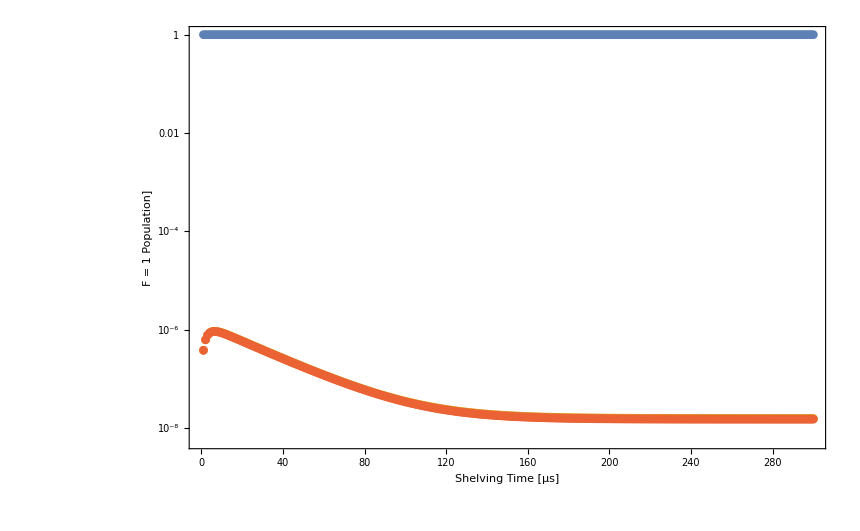

```mathematica
ListLogPlot[{Re[PointsExtractor[points,1,1]]/.{xx_,yy_}-> {1*^6*xx,yy},Re[PointsExtractor[points,2,2]]/.{xx_,yy_}-> {1*^6*xx,yy},Re[PointsExtractor[points,3,3]]/.{xx_,yy_}-> {1*^6*xx,yy},Re[PointsExtractor[points,4,4]]/.{xx_,yy_}-> {1*^6*xx,yy}},Joined->False(*,PlotRange->{{0,200},{.1,1}}*),Frame->True,FrameLabel->{Style["Shelving Time [μs]",{Black,Large}],Style["F = 1 Population]",{Black,Large}]},FrameTicksStyle->Directive[Black,25]]
```

```mathematica
(*Define Group function for plotting*)
Group[t_,jj_,kk_] = Table[ToExpression[StringJoin["Re[ρ",ToString[ii],"b",ToString[ii],"[t]/.sol[[1]]]"]],{ii,jj,kk}]
```

Table::iterb: Iterator {ii,jj,kk} does not have appropriate bounds.

Table[ToExpression[Re[ρ<>ToString[ii]<>b<>ToString[ii]<>[t]/.sol[[1]]]],{ii,jj,kk}]

```mathematica
Total[Group[t,2,4]/.t-> tstop]
```

-4.62184×10^-6

```mathematica
Group[t,1,1]/.t-> tstop
```

{0.999999}

```mathematica
Total[Group[t,25,36]/.t-> tstop]
```

5.38386×10^-6

```mathematica
Total[Group[t,12,16]/.t-> tstop]
```

-2.01212×10^-7

```mathematica
Total[Group[t,9,11]/.t -> tstop]
```

4.99159×10^-9

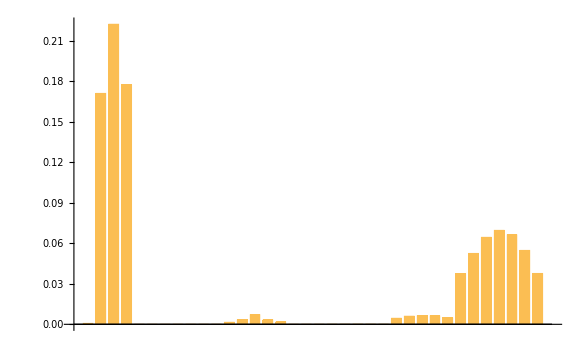

```mathematica
BarChart[Table[ Group[t,ii,ii][[1]]/.t-> tstop,{ii,1,36}]]
```

### Random plots

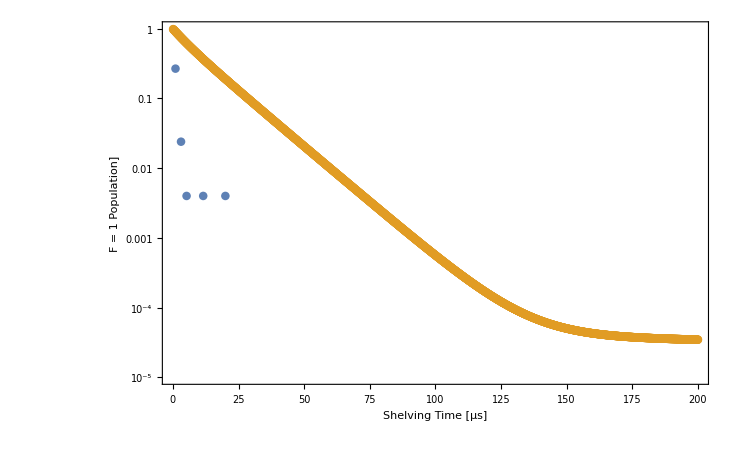

```mathematica
ListLogPlot[{OPcurve,Re[PointsExtractor[points,2,4]]/.{xx_,yy_}-> {1*^6*xx,yy}},Joined->False,PlotRange->{{0,200},{1*^-5,1}},Frame->True,FrameLabel->{Style["Shelving Time [μs]",{Black,Large}],Style["F = 1 Population]",{Black,Large}]},FrameTicksStyle->Directive[Black,25]]
```

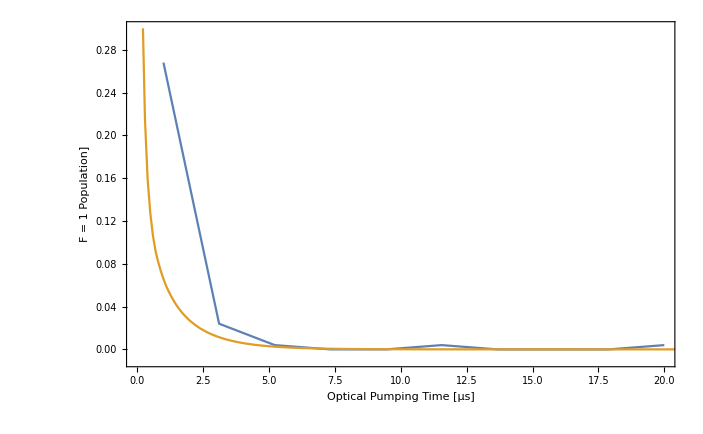

```mathematica
ListPlot[{OPcurve,Re[PointsExtractor[points,2,4]]/.{xx_,yy_}-> {1*^6*xx,yy}},Joined->True,PlotRange->{{0,20},{-0.01,0.3}},Frame->True,FrameLabel->{Style["Optical Pumping Time [μs]",{Black,Large}],Style["F = 1 Population]",{Black,Large}]},FrameTicksStyle->Directive[Black,25]]
```

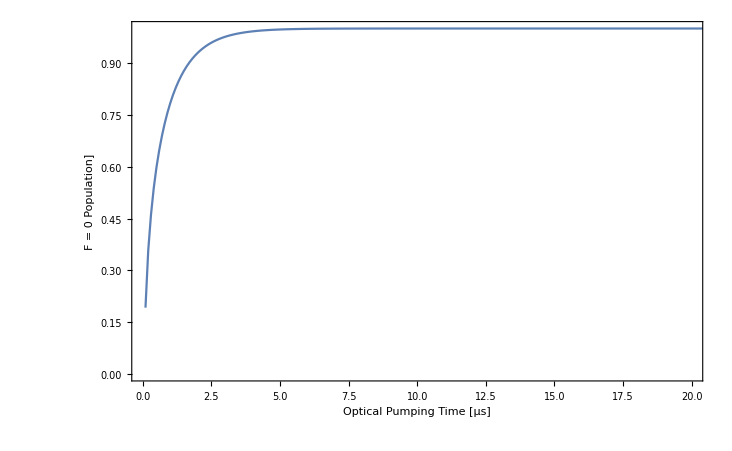

```mathematica
ListPlot[{Re[PointsExtractor[points,1,1]]/.{xx_,yy_}-> {1*^6*xx,yy}},Joined->True,PlotRange->{{0,20},All},Frame->True,FrameLabel->{Style["Optical Pumping Time [μs]",{Black,Large}],Style["F = 0 Population]",{Black,Large}]},FrameTicksStyle->Directive[Black,25]]
```

```mathematica
MemoryInUse[]
```

182493168

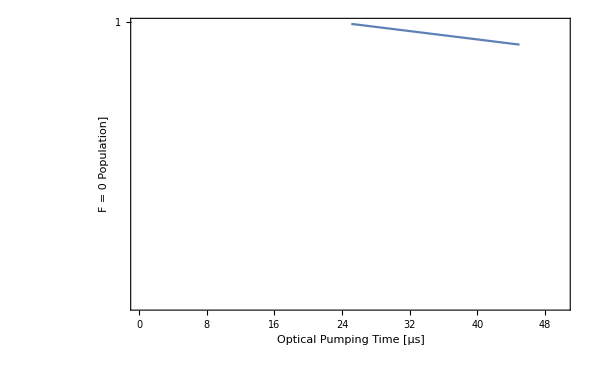

```mathematica
ListLogPlot[{Re[PointsExtractor[points3,1,1]]/.{xx_,yy_}-> {1*^6*xx,yy}},Joined->True,PlotRange->{{0,50},{0.99,0.999945}},Frame->True,FrameLabel->{Style["Optical Pumping Time [μs]",{Black,Large}],Style["F = 0 Population]",{Black,Large}]},FrameTicksStyle->Directive[Black,25],Background->White]
```

```mathematica
Re[PointsExtractor[points,2,4]][[-1]]
Re[PointsExtractor[points,2,4]][[-1]]
```

```mathematica
Re[PointsExtractor[points,2,4]][[-1]]
```

{0.00002,0.0000119386}

```mathematica
Group[t,1,1]/.t-> tstop
```

{0.00326877}

```mathematica
s = Total[Group[t,2,4]/.t-> tstop]
```

0.000221567

```mathematica
p = Total[Group[t,5,8]/.t-> tstop]
```

1.68728×10^-7

```mathematica
d = Total[Group[t,9,16]/.t-> tstop]
```

0.0119717

```mathematica
d3 = Total[Group[t,17,36]/.t-> tstop]
```

0.984538

```mathematica
Total[Group[t,1,36]/.t-> tstop]-1
```

-2.22045×10^-16

```mathematica
1-s
```

0.999963

Part::partd: Part specification points2 ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification points2 ⟦ 1, 1, 1 ⟧ is longer than depth of object.

Part::partd: Part specification points2 ⟦ 1, 1, 2 ;; 2 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

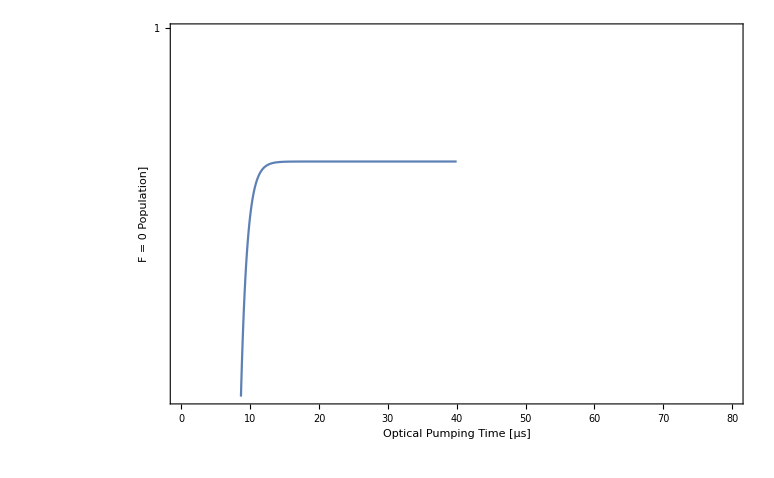

```mathematica
ListLogPlot[{Re[PointsExtractor[points,1,1]]/.{xx_,yy_}-> {1*^6*xx,yy},Re[PointsExtractor[points2,1,1]]/.{xx_,yy_}-> {1*^6*xx,yy}},Joined->True,PlotRange->{{0,80},{0.9999,0.999999}},Frame->True,FrameLabel->{Style["Optical Pumping Time [μs]",{Black,Large}],Style["F = 0 Population]",{Black,Large}]},FrameTicksStyle->Directive[Black,25],Background->White]
```

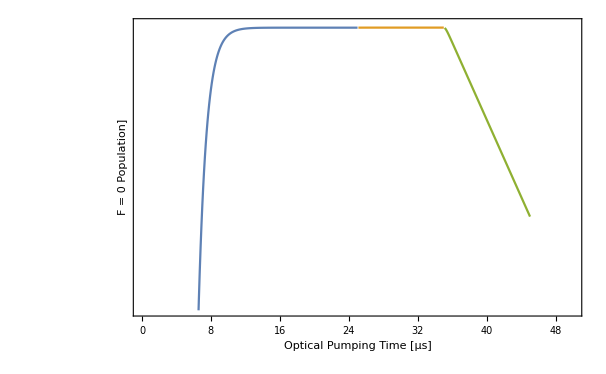

```mathematica
ListLogPlot[{Re[PointsExtractor[points,1,1]]/.{xx_,yy_}-> {1*^6*xx,yy},Re[PointsExtractor[points2,1,1]]/.{xx_,yy_}-> {1*^6*xx,yy},Re[PointsExtractor[points3,1,1]]/.{xx_,yy_}-> {1*^6*xx,yy},},Joined->True,PlotRange->{{0,50},{0.9994,0.99995}},Frame->True,FrameLabel->{Style["Optical Pumping Time [μs]",{Black,Large}],Style["F = 0 Population]",{Black,Large}]},FrameTicksStyle->Directive[Black,25],Background->White]
```

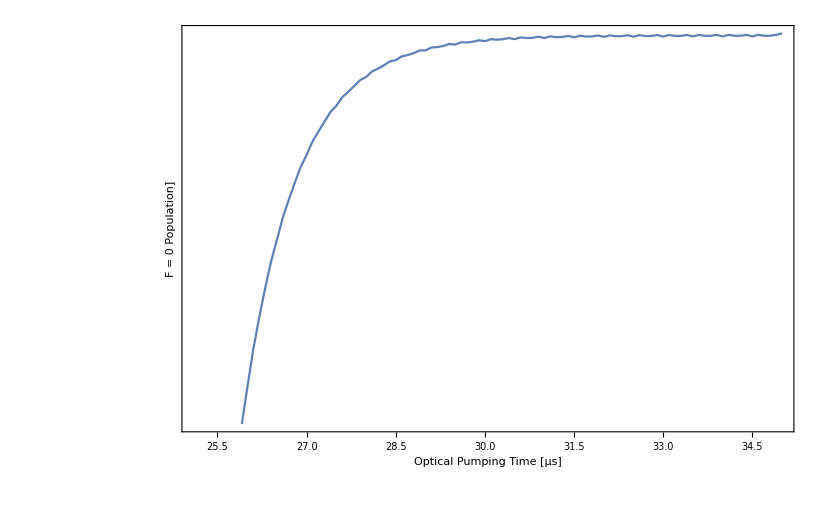

```mathematica
ListLogPlot[{c},Joined->True,Frame->True,FrameLabel->{Style["Optical Pumping Time [μs]",{Black,Large}],Style["F = 0 Population]",{Black,Large}]},FrameTicksStyle->Directive[Black,25],Background->White]
```

```mathematica
(Re[PointsExtractor[points2,1,1]]/.{xx_,yy_}-> {1*^6*xx,yy})[[100,2]]-(Re[PointsExtractor[points2,1,1]]/.{xx_,yy_}-> {1*^6*xx,yy})[[50,2]]
```

6.39718×10^-10

```mathematica
(Re[PointsExtractor[points2,1,1]]/.{xx_,yy_}-> {1*^6*xx,yy})[[100,2]]-(Re[PointsExtractor[points2,1,1]]/.{xx_,yy_}-> {1*^6*xx,yy})[[75,2]]
```

2.69326×10^-10

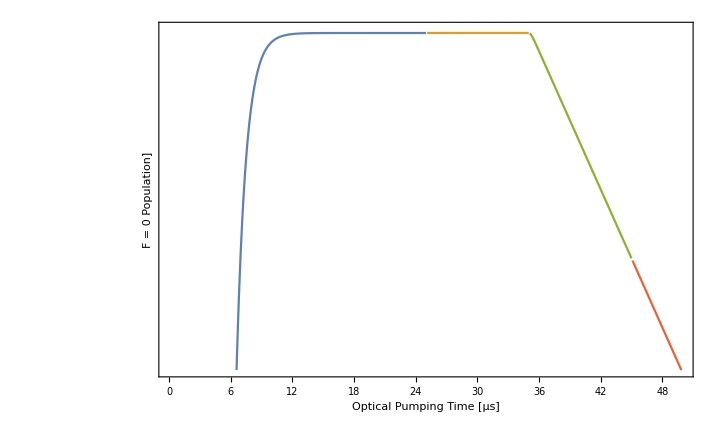

```mathematica
ListLogPlot[{Re[PointsExtractor[points,1,1]]/.{xx_,yy_}-> {1*^6*xx,yy},Re[PointsExtractor[points2,1,1]]/.{xx_,yy_}-> {1*^6*xx,yy},Re[PointsExtractor[points3,1,1]]/.{xx_,yy_}-> {1*^6*xx,yy},
Re[PointsExtractor[points4,1,1]]/.{xx_,yy_}-> {1*^6*xx,yy}},Joined->True,PlotRange->{{0,50},{0.9994,0.99995}},Frame->True,FrameLabel->{Style["Optical Pumping Time [μs]",{Black,Large}],Style["F = 0 Population]",{Black,Large}]},FrameTicksStyle->Directive[Black,25],Background->White]
```

```mathematica
PointsExtractor[points,1,1][[-1]]
```

{0.000025,0.999943+2.20172×10^-11 ⅈ}

```mathematica
(*Define Group function for plotting*)
Group[t_,jj_,kk_] = Table[ToExpression[StringJoin["Re[ρ",ToString[ii],"b",ToString[ii],"[t]/.sol[[1]]]"]],{ii,jj,kk}]
```

Table::iterb: Iterator {ii, jj, kk} does not have appropriate bounds.

Table[ToExpression[Re[ρ<>ToString[ii]<>b<>ToString[ii]<>[t]/.sol[[1]]]],{ii,jj,kk}]

```mathematica
Group2[t_,jj_,kk_] = Table[ToExpression[StringJoin["Re[ρ",ToString[ii],"b",ToString[ii],"[t]/.sol2[[1]]]"]],{ii,jj,kk}]
```

Table::iterb: Iterator {ii, jj, kk} does not have appropriate bounds.

Table[ToExpression[Re[ρ<>ToString[ii]<>b<>ToString[ii]<>[t]/.sol2[[1]]]],{ii,jj,kk}]

```mathematica
Group[t,12,12]/.t-> tstop
Group[t,16,16]/.t-> tstop
```

{0.0000114183}

{6.73559×10^-6}

```mathematica
Group2[t,12,12]/.t-> (tstop+2*^-6)
Group2[t,16,16]/.t-> (tstop+2*^-6)
```

{0.0000113983}

{6.72302×10^-6}

```mathematica
Total[Group[t,9,16]/.t-> tstop]
Total[Group[t,2,4]/.t-> tstop]
```

0.0000284951

0.0000226867

```mathematica
1-0.000022686692165956278
```

0.999977

```mathematica
Total[Group2[t,9,16]/.t-> (tstop+2*^-6)]
Total[Group2[t,2,4]/.t-> (tstop+2*^-6)]
```

0.0000284415

0.0000226423

```mathematica
MatrixForm[Simplify[Ωmat[[16,All]] *2.*^-6,t>0]]
```

(0.+0. ⅈ
0.
0.
0.
0.
0.
0.
20.162+34.9217 ⅇ^((0.+5.65487×10^9 ⅈ) t)+20.162 ⅇ^((0.+1.12092×10^10 ⅈ) t)
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.)

```mathematica
State[[12]]
```

{12,Eng→9.18345×10^14,F→2,Mf→-2,J→3/2,L→2,n→5,config→3}

```mathematica
State[[16]]
```

{16,Eng→9.18345×10^14,F→2,Mf→2,J→3/2,L→2,n→5,config→3}

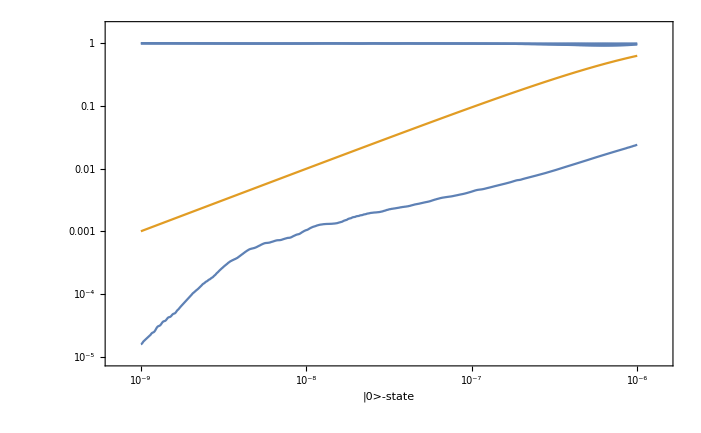

```mathematica
(*What happens to |S,F=0>*)
LogLogPlot[{Group[t,1,4],1-Exp[-t/1*^-6]},{t,1*^-9,tstop},PlotRange->All,Frame-> True,FrameLabel->"|0>-state"]
```

```mathematica
Re[ρ1b1[tstop]/.j]
```

{0.0239622}

```mathematica
MatrixForm[Transpose[{Table[ii,{ii,1,36}],(Group[t,1,36])/.t-> tstop}]]
```

(1 | 0.63099
2 | 0.0724907
3 | 0.11294
4 | 0.0478859
5 | 0.0000241402
6 | 0.0000889394
7 | 0.0000683202
8 | 0.0000975155
9 | 0.00219838
10 | 0.000807355
11 | 0.00038649
12 | 0.0505625
13 | 0.0278543
14 | 0.00975613
15 | 0.0186931
16 | 0.0251553
17 | 0.
18 | 0.
19 | 0.
20 | 0.
21 | 0.
22 | 0.
23 | 0.
24 | 0.
25 | 0.
26 | 0.
27 | 0.
28 | 0.
29 | 0.
30 | 0.
31 | 0.
32 | 0.
33 | 0.
34 | 0.
35 | 0.
36 | 0.)

```mathematica
Exp[-200/1.]
```

1.3839×10^-87

```mathematica
Exp[-200/10.]
```

2.06115×10^-9

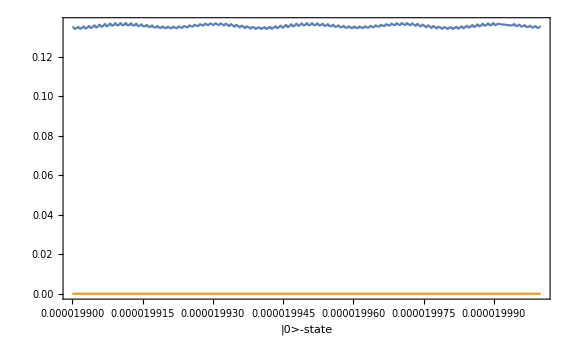

```mathematica
(*What happens to |S,F=0>*)
Plot[{Total[Group[t,9,16]],Total[Group[t,17,36]]},{t,tstop-100*^-9,tstop},PlotRange->All,Frame-> True,FrameLabel->"|0>-state"]
```

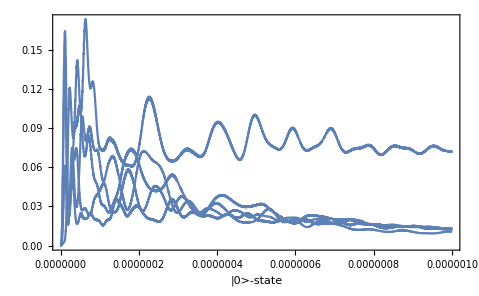

```mathematica
(*What happens to |S,F=0>*)
Plot[Group[t,12,16],{t,0,tstop},PlotRange->All,Frame-> True,FrameLabel->"|0>-state"]
```

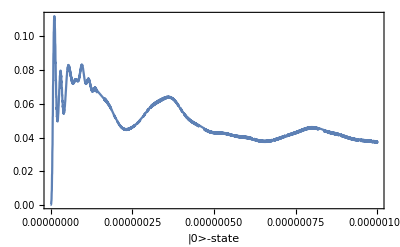

```mathematica
Plot[Group[t,10,10],{t,0,tstop},PlotRange->All,Frame-> True,FrameLabel->"|0>-state"]
```

```mathematica
Re[ρ1b1[tstop]/.j]
```

{0.999936}

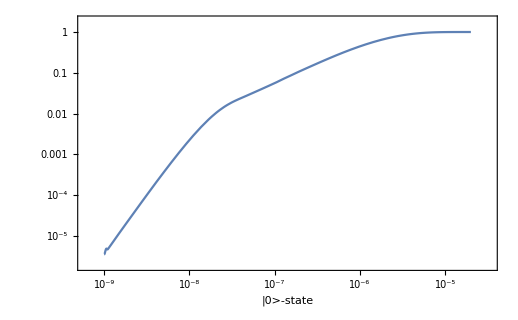

```mathematica
LogLogPlot[{Re[ρ1b1[t]/.j]},{t,1*^-9,tstop},PlotRange->All,Frame-> True,FrameLabel->"|0>-state"]
```

### Test Section

```mathematica
Table[If[(Ωmat[[jj,ii]] != Conjugate[Ωmat[[ii,jj]]])/.t-> 1,{ii,jj}],{ii,1,36},{jj,1,36}]
```

{{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null},{Null,Null,Null,Null,{2,5},{2,6},{2,7},Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null},{Null,Null,Null,Null,{3,5},{3,6},Null,{3,8},Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null},{Null,Null,Null,Null,{4,5},Null,{4,7},{4,8},Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null},{Null,{5,2},{5,3},{5,4},Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null},{Null,{6,2},{6,3},Null,Null,Null,Null,Null,Null,Null,Null,{6,12},{6,13},{6,14},Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null},{Null,{7,2},Null,{7,4},Null,Null,Null,Null,Null,Null,Null,Null,{7,13},{7,14},{7,15},Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null},{Null,Null,{8,3},{8,4},Null,Null,Null,Null,Null,Null,Null,Null,Null,{8,14},{8,15},{8,16},Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null},{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null},{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null},{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null},{Null,Null,Null,Null,Null,{12,6},Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null},{Null,Null,Null,Null,Null,{13,6},{13,7},Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null},{Null,Null,Null,Null,Null,{14,6},{14,7},{14,8},Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null},{Null,Null,Null,Null,Null,Null,{15,7},{15,8},Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null},{Null,Null,Null,Null,Null,Null,Null,{16,8},Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null},{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null},{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null},{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null},{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null},{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null},{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null},{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null},{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null},{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null},{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null},{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null},{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null},{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null},{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null},{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null},{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null},{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null},{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null},{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null},{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}}

```mathematica
Ωmat[[8,15]]
```

0.+7.99087×10^7 ⅇ^((0.-6.28319×10^7 ⅈ) t)+7.99087×10^7 ⅇ^((0.+5.84336×10^9 ⅈ) t)

```mathematica
Ωmat[[15,8]]
```

0.+7.99087×10^7 ⅇ^((0.+6.28319×10^7 ⅈ) t)+7.99087×10^7 ⅇ^((0.-5.84336×10^9 ⅈ) t)

```mathematica
(*So when you really look at the exponents they differ at the 10^-15 level. I guess because I'm adding and subtracting numbers that are huge*)
$MachinePrecision
```

15.9546

```mathematica
E1
```

{-758.683,1072.94,758.683}

```mathematica
Efield[Isp1,θsp1,ωsp1]
```

{-758.683,1072.94,758.683}

```mathematica
Elasers
```

{{-758.683,1072.94,758.683,3.81778×10^15},{-5475.32,7743.27,5475.32,2.89937×10^15},{-5475.32,7743.27,5475.32,2.89938×10^15}}

```mathematica
{Efield[Isp1,θsp1,ωsp1],Efield[Idp2,θdp2,ωdp2],Efield[Idp1,θdp1,ωdp1]}
```

{{-758.683,1072.94,758.683},{-5475.32,7743.27,5475.32},{-5475.32,7743.27,5475.32}}

0.375